# xAct Tutorial

## José M. Martín-García, Wolfram

## ICERM 2020, September 15

## Plan of the talk

1. Introduction to xAct

2. Abstract computations with xTensor

3. Component computations with xCoba

4. Perturbation theory with xPert

5. Riemann identities witn Invar

6. Other xAct packages

7. Conclusions and future plans

## 1. Introduction to xAct

## 1.1. History

The project started in early 2002, during my postdoc at the University of Southampton.

Perturbation theory and the search for formulations of the Einstein equations were the drivers to keep improving the system, by then called exTensor.

R. Prix taught me about GPL, and suggested to change to xTensor.

P. Matteucci suggested to use some recent articles (July 2001, by R. Portugal) using permutation group theory to handle indices.

The amount of group theory I had to code was so large that the project split into two packages: xPerm for permutation group theory, xTensor for tensors. The name xAct was introduced to refer to the whole project.

First public version of xAct was released on March 4, 2004, with two packages.

A. García-Parrado and G. Faye were two early users, and helped much shaping the system.

Many additions during 2004 - 2010. Slower pace of evolution since then.

Now there are 20 packages in xAct.

## 1.2. Resources

The xAct webpage: [www.xact.eshttp://www.xact.esNonehttp://www.xact.esHyperlinkActionRecycledHyperlinkActive]

The xAct-contrib github: [github.com/xAct-contribhttps://github.com/xAct-contribNonehttps://github.com/xAct-contribHyperlinkActionRecycledHyperlinkActive], [contrib.xact.eshttp://contrib.xact.es/Nonehttp://contrib.xact.es/HyperlinkActionRecycledHyperlinkActive]

The xAct forum: [groups.google.com/g/xacthttps://groups.google.com/g/xactNonehttps://groups.google.com/g/xactHyperlinkActionRecycledHyperlinkActive]

There are also questions in [mathematica.stackexchange.comhttps://mathematica.stackexchange.com/search?q=xActNonehttps://mathematica.stackexchange.com/search?q=xActHyperlinkActionRecycledHyperlinkActive]

## 1.3. The structure of xAct

xAct is a collection of packages, organized hierarchically.

When you load a package, all dependencies are loaded too.

#### Core packages

xCore: tools for the rest of the system. JMMG. 2007.

xPerm: permutation group theory. JMMG. 2003.

xTensor: abstract tensor computations. JMMG. 2002.

xCoba: tensor computations by components. D. Yllanes, JMMG. 2005.

#### Application packages

xPert : metric perturbation theory. D. Brizuela, JMMG, G. Mena-Marugán. 2006.

Harmonics: tensor spherical harmonics. D. Brizuela, JMMG, G. Mena-Marugán. 2006.

Invar: invariants of the Riemann tensor. JMMG, R. Portugal, D. Yllanes. 2006.

Spinors: spinor calculus. A. García-Parrado, JMMG. 2007.

SymManipulator: symmetrized tensor expressions. T. Bäckdahl. 2011.

xPand: cosmological perturbations. C. Pitrou, X. Roy, O. Umeh. 2012.

xTras: field theory. T. Nutma. 2012.

xTerior: exterior calculus. A. García-Parrado, L. C. Stein. 2013.

SpinFrames: NP and GHP form of spinor equations. T. Bäckdahl, S. Aksteiner. 2015.

xIST/COPPER: general scalar-tensor theories and perturbations. J. Noller. 2016.

EFTofPNG: effective field theory of post-Newtonian gravity. M. Levi, J. Steinhoff. 2017.

bimEX: 3+1 bimetric relativity. F. Torsello. 2019.

FieldsX: fermions, gauge fields and BRST cohomology. M. B. Fröb. 2020.

#### Input/Output packages

TexAct: Tex formatting of tensor expressions. T. Bäckdahl, JMMG, B. Wardell. 2008.

xPrint: graphical interface to xAct. Alessandro Stecchina. 2009.

#### Exceptional packages

AVF: algebra-valued forms. H. D. Wahlquist . 2003. In 2011 F. B. Estabrook sent it to me.

## 1.4. Abstract vs. component computations

### Abstract computations

Deal with tensor expressions and identities that are independent of choices of frames and/or coordinates.

Performed using Penrose’s abstract indices, nicely described in Wald’s General Relativity book.

xAct follows Wald’s conventions for signs, Riemann indices order, etc. For Spinors we followed Spinors and space-time, by Penrose & Rindler.

There are sign configuration variables, with Wald’s defaults. They can be changed at the beginning of a session.

### Component computations

Deal with tensors expressed as arrays of components in a given frame (aka basis), each component being a scalar function of some coordinate fields.

-Graphics-

Performed with constructions that always know in which frame we are working.

Different frames will be represented with different colors. If an expression has colored parts it is still possibly basis-dependent. If the expression has all its parts in black then it is frame-independent (abstract).

### Both together

These two types of computation are so different that traditionally there usually were two separate packages, or a switch to move from one type to the other.

xAct combines both types in a coherent framework, essentially performing the component computations with the abstract tools, and forcing everything to be geometric. The key idea is always to keep track of basis/chart dependencies.

Somebody said that “Differential Geometry is the study of objects that stay invariant under changes of notation”. Every dependency must be explicit in a computer implementation. xAct only breaks that rule once: the raising and lowering of indices with metrics.

## 1.5. Crash course in Wolfram Language

### Some historical data

Currently in version 12.1.1, since June 2020.

Versions:

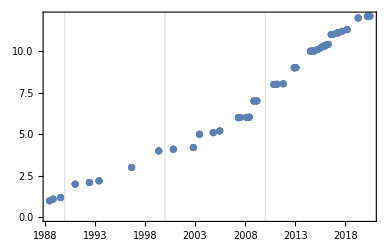

```mathematica
versions={
{{1988,6,23},"1.0.0"},
{{1988,10,31},"1.1.0"},
{{1989,8,1},"1.2.0"},
{{1991,1,15},"2.0.0"},
{{1992,6,15},"2.1.0"},
{{1993,6,1},"2.2.0"},
{{1996,9,3},"3.0.0"},
{{1999,5,19},"4.0.0"},
{{2000,11,2},"4.1.0"},
{{2002,11,1},"4.2.0"},
{{2003,6,12},"5.0.0"},
{{2004,10,25},"5.1.0"},
{{2005,6,20},"5.2.0"},
{{2007,5,1},"6.0.0"},
{{2007,7,5},"6.0.1"},
{{2008,2,25},"6.0.2"},
{{2008,6},"6.0.3"},
{{2008,11,18},"7.0.0"},
{{2009,3,5},"7.0.1"},
{{2010,11,15},"8.0.0"},
{{2011,3,7},"8.0.1"},
{{2011,10,24},"8.0.4"},
{{2012,11,28},"9.0.0"},
{{2013,1,30},"9.0.1"},
{{2014,7,9},"10.0.0"},
{{2014,9,17},"10.0.1"},
{{2014,12,10},"10.0.2"},
{{2015,3,30},"10.1.0"},
{{2015,7,14},"10.2.0"},
{{2015,10,15},"10.3.0"},
{{2015,12,16},"10.3.1"},
{{2016,3,2},"10.4.0"},
{{2016,4,18},"10.4.1"},
{{2016,8,8},"11.0.0"},
{{2016,9,28},"11.0.1"},
{{2017,3,16},"11.1.0"},
{{2017,4,25},"11.1.1"},
{{2017,9,14},"11.2.0"},
{{2018,3,8},"11.3.0"},
{{2019,4,16},"12.0.0"},
{{2020,3,18},"12.1.0"},
{{2020,6,17},"12.1.1"}};
values={#1,{1,1/10,1/100}.(FromDigits/@StringSplit[#2,"."])}&@@@versions;
DateListPlot[values,Mesh->Full,Joined->False,GridLines->{{{1990,1,1},{2000,1,1},{2010,1,1}},None}]
```

Number of symbols:

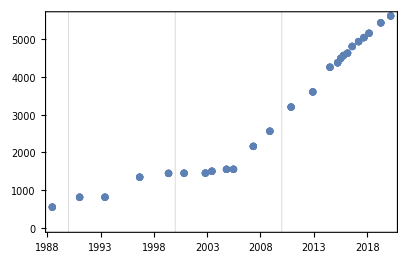

```mathematica
symbols=Table[EntityClass["WolframLanguageSymbol","VersionIntroduced"->version]//EntityList,{version,{1.0,2.0,2.2,3.0,4.0,4.1,4.2,5.0,5.1,5.2,6.0,7.0,8.0,9.0,10.0,10.1,10.2,10.3,10.4,11.0,11.1,11.2,11.3,12.0,12.1}}];
accum=Accumulate[Length/@symbols];
symbolsN={
{{1988,6,23},554}, (* 1.0 *)
{{1991,1,15},815}, (* 2.0 *)
{{1993,6,1},816}, (* 2.2 *)
{{1996,9,3},1345}, (* 3.0 *)
{{1999,5,19},1446}, (* 4.0 *)
{{2000,11,2},1450}, (* 4.1 *)
{{2002,11,1},1453}, (* 4.2 *)
{{2003,6,12},1502}, (* 5.0 *)
{{2004,10,25},1553}, (* 5.1 *)
{{2005,6,20},1554}, (* 5.2 *)
{{2007,5,1},2160}, (* 6.0 *)
{{2008,11,18},2560}, (* 7.0 *)
{{2010,11,15},3198}, (* 8.0 *)
{{2012,11,28},3598}, (* 9.0 *)
{{2014,7,9},4251}, (* 10.0 *)
{{2015,3,30},4368}, (* 10.1 *)
{{2015,7,14},4485}, (* 10.2 *)
{{2015,10,15},4560}, (* 10.3 *)
{{2016,3,2},4622}, (* 10.4 *)
{{2016,8,8},4800}, (* 11.0 *)
{{2017,3,16},4928}, (* 11.1 *)
{{2017,9,14},5034}, (* 11.2 *)
{{2018,3,8},5148}, (* 11.3 *)
{{2019,4,16},5424},  (* 12.0 *)
{{2020,3,18},5605} (* 12.1 *)
};
DateListPlot[symbolsN,Mesh->Full,Joined->False,GridLines->{{{1990,1,1},{2000,1,1},{2010,1,1}},None}]
```

Word cloud of individual words in the symbol names (like Function, ImageSize o RegionMemberFunction):

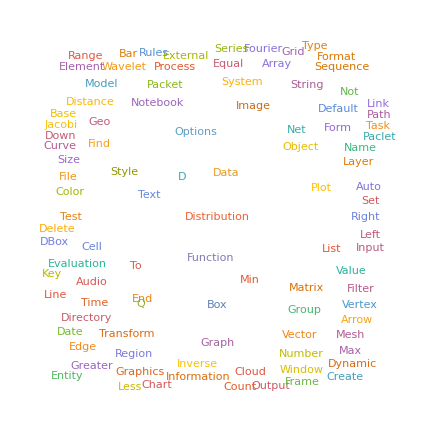

```mathematica
breakAtCapital[string_String]:=StringSplit[StringReplace[string,{"$"->"",RegularExpression["[0-9]"]->""}],RegularExpression["(?<=[a-z])(?=[A-Z])"]]
words=Flatten[breakAtCapital/@Names["System`*"]];
WordCloud[words]
```

### Everything is an expression

Algebraic computation:

```mathematica
expr=(3/2-Sqrt[5/11])^7
```

(3/2-√(5/11))^7

```mathematica
Expand[expr]
```

19586157/170368-(14492393 √(5/11))/85184

```mathematica
N[expr,20]
```

0.26189346164476465036

```mathematica
FullForm[expr]
```

Power[Plus[Rational[3,2],Times[-1,Power[Rational[5,11],Rational[1,2]]]],7]

Integral/differential computation:

```mathematica
Integrate[1/(1+x^3),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
D[%,x]
```

1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2))

```mathematica
Simplify[%]
```

1/(1+x^3)

```mathematica
%//FullForm
```

Power[Plus[1,Power[x,3]],-1]

Equivalent notations for (unary) function application:

```mathematica
{f[x],f@x,x//f}
```

{f[x],f[x],f[x]}

### Polynomial computations

Take a polynomial, expressed in any form:

```mathematica
(x+1)^10(-128+448 x+ x^2(-672+560 x-280 x^2+84 x^3-14 x^4+x^5))
```

(1+x)^10 (-128+448 x+x^2 (-672+560 x-280 x^2+84 x^3-14 x^4+x^5))

Expand will convert it into a linear combination of monomials:

```mathematica
Expand[%]
```

-128-832 x-1952 x^2-1360 x^3+1960 x^4+3668 x^5+322 x^6-2983 x^7-1340 x^8+1285 x^9+860 x^10-350 x^11-280 x^12+70 x^13+50 x^14-11 x^15-4 x^16+x^17

Simplify will try to write it in the simplest possible form:

```mathematica
Simplify[%]
```

(-2+x)^7 (1+x)^10

### The power of pattern matching

• Replacement rules with patterns are a very powerful technique to handle indices:

```mathematica
rule=T[a_,b_]T[-b_,c_]:>T[a,c]
```

T[a_,b_] T[-b_,c_]:>T[a,c]

```mathematica
{T[-i,j]T[k,i],T[-i,j]T[i,k]}
```

{T[-i,j] T[k,i],T[-i,j] T[i,k]}

The first case matches, because the Times product is commutative:

```mathematica
%/.rule
```

{T[k,j],T[-i,j] T[i,k]}

• There are many other powerful WL constructions that are very useful in the handling of tensor expressions: upvalues, delayed assignments, flexible typesetting, and much more. I’ll mention some of them. There are, of course, many other commands to process and visualization information.

## 2. Abstract computations with xTensor

## 2.1. Load the package

If xAct is correctly installed, then this should load the xTensor package:

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 2.2. Define basic objects

xTensor has its own type system and registration mechanism, that keeps track of all that has been declared during a session, and the mutual relations. The same symbol cannot be used to define two different objects. However two different symbols can be typeset in the same way (say both the Riemann and Ricci tensors can be typeset as R).

• Define a 4d manifold. Note how its associated vector bundle is defined too:

```mathematica
DefManifold[M,4,{a,b,c,d,e,f,g,i,j,k,l}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

• Define a contravariant vector field:

```mathematica
DefTensor[v[a],M]
```

** DefTensor: Defining tensor v[a].

```mathematica
v[a]
```

v | a

```mathematica
FullForm[%]
```

v[a]

• The delta tensor is already defined:

```mathematica
delta[-a,b]
```

δ |   | b
a |

```mathematica
delta[-a,b]v[a]
```

v | b

```mathematica
delta[-a,a]
```

4

• Define an antisymmetric covariant vector field:

```mathematica
DefTensor[F[-a,-b],M,Antisymmetric[{-a,-b}]]
```

** DefTensor: Defining tensor F[-a,-b].

```mathematica
F[-a,-b]
```

F |   |  
a | b

In the following we will use InputForm intstead of FullForm, because the former shows covariant indices in a more readable form:

```mathematica
InputForm[%]
```

F[-a, -b]

```mathematica
FullForm[%%]
```

F[Times[-1,a],Times[-1,b]]

## 2.3. Canonicalization

ToCanonical is the most important function in xTensor. It handles everything about index canonicalization, internally calling the group-theoretical algorithms. It first calls Expand on the tensorial expression and then acts on each term of the expanded expression individually.

• There is no automatic canonicalization:

```mathematica
F[-b,-a]
```

F |   |  
b | a

```mathematica
ToCanonical[ F[-b,-a] ]
```

-F |   |  
a | b

• Commutative products:

```mathematica
v[a]F[-a,-b]v[b]
```

F |   |  
a | b v | a
  v | b

```mathematica
ToCanonical[%]
```

0

• Define two more objects:

```mathematica
DefTensor[w[-a],M]
```

** DefTensor: Defining tensor w[-a].

```mathematica
DefTensor[T[-a,b],M]
```

** DefTensor: Defining tensor T[-a,b].

• Expression with dummy indices:

```mathematica
expr=F[-a,-d]v[d]v[b]w[-b]+3v[b]v[c]w[-c]T[-b,e]F[-e,-a]
```

F |   |  
a | d v | b
  v | d
  w |  
b+3 F |   |  
e | a T |   | e
b |   v | b
  v | c
  w |  
c

```mathematica
ToCanonical[expr]
```

F |   |  
a | c v | b
  v | c
  w |  
b-3 F |   |  
a | c T |   | c
b |   v | b
  v | d
  w |  
d

WL’s Simplify can reduce the expression (there is no tensorial knowledge here):

```mathematica
Simplify[%]
```

F |   |  
a | c v | b
  (v | c
  w |  
b-3 T |   | c
b |   v | d
  w |  
d)

• The combination of ToCanonical followed by Simplify is called Simplification in xTensor:

```mathematica
Simplification[expr]
```

F |   |  
a | c v | b
  (v | c
  w |  
b-3 T |   | c
b |   v | d
  w |  
d)

With large expressions Simplify may take longer to evaluate than ToCanonical.

## 2.4a. Covariant derivatives

• Several other objects are defined together with a covariant derivative (we’ll look at them in the next slide):

```mathematica
DefCovD[CD[-a],SymbolOfCovD->{"|","D"}]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

This is the covariant derivative of a vector field:

```mathematica
CD[-a][ v[b] ]
```

D_a v | b

• You can select whether to show covariant derivatives in prefix (the default) or postfix notation:

```mathematica
$CovDFormat="Postfix";
```

```mathematica
CD[-a][ F[b,-c] ]
```

F | b |   |   
  | c | |a

```mathematica
$CovDFormat="Prefix";
```

```mathematica
CD[-a][ F[b,-c] ]
```

D_a F | b |  
  | c

• The Leibnitz rule is automatic:

```mathematica
CD[-a][3 F[-b,-c]v[c] ]
```

3 (v | c
  (D_a F |   |  
b | c)+F |   |  
b | c (D_a v | c
 ))

```mathematica
%v[b]//ToCanonical
```

3 F |   |  
b | c v | b
  (D_a v | c
 )

## 2.4b. Covariant derivatives: associated tensors

• Let us have a look at the tensors defined with the covariant derivative CD. They all have CD appended in the tensor name:

```mathematica
{TorsionCD[a,-b,-c],ChristoffelCD[a,-b,-c],RiemannCD[-a,-b,-c,d],RicciCD[-a,-b]}
```

{0,Γ[D] | a |   |  
  | b | c,R[D] |   |   |   | d
a | b | c |  ,R[D] |   |  
a | b}

By default, covariant derivatives are defined without torsion.

• Because CD is not associated to a metric, its Riemann tensor is only antisymmetric in one pair:

```mathematica
RiemannCD[-a,-b,-c,d]+RiemannCD[-b,-a,-c,d]//ToCanonical
```

0

• Deduce that result from derivatives of the Christoffel tensor:

```mathematica
RiemannCD[-a,-b,-c,d]//RiemannToChristoffel
```

Γ[D] | d |   |  
  | b | l$2484 Γ[D] | l$2484 |   |  
  | a | c-Γ[D] | d |   |  
  | a | l$2484 Γ[D] | l$2484 |   |  
  | b | c-∂_a Γ[D] | d |   |  
  | b | c+∂_b Γ[D] | d |   |  
  | a | c

```mathematica
%+RiemannCD[-b,-a,-c,d]//RiemannToChristoffel
```

Γ[D] | d |   |  
  | b | l$2484 Γ[D] | l$2484 |   |  
  | a | c-Γ[D] | d |   |  
  | a | l$2484 Γ[D] | l$2484 |   |  
  | b | c-Γ[D] | d |   |  
  | b | l$2487 Γ[D] | l$2487 |   |  
  | a | c+Γ[D] | d |   |  
  | a | l$2487 Γ[D] | l$2487 |   |  
  | b | c

```mathematica
%//ToCanonical
```

0

• When internal dummy indices are introduced, they have unique names with a number that changes each time. This avoids “index collisions”. These indices are called “dollar indices” and there is a function to hide them:

```mathematica
RiemannCD[-a,-b,-c,d]//RiemannToChristoffel//ScreenDollarIndices
```

Γ[D] | d |   |  
  | b | e Γ[D] | e |   |  
  | a | c-Γ[D] | d |   |  
  | a | e Γ[D] | e |   |  
  | b | c-∂_a Γ[D] | d |   |  
  | b | c+∂_b Γ[D] | d |   |  
  | a | c

Write this and you will not see them again:

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
RiemannCD[-a,-b,-c,d]//RiemannToChristoffel
```

Γ[D] | d |   |  
  | b | e Γ[D] | e |   |  
  | a | c-Γ[D] | d |   |  
  | a | e Γ[D] | e |   |  
  | b | c-∂_a Γ[D] | d |   |  
  | b | c+∂_b Γ[D] | d |   |  
  | a | c

but they are still there:

```mathematica
%//InputForm
```

ChristoffelCD[d, -b, -l$2496]*ChristoffelCD[l$2496, -a, -c] - 
 ChristoffelCD[d, -a, -l$2496]*ChristoffelCD[l$2496, -b, -c] - PD[-a][ChristoffelCD[d, -b, -c]] + 
 PD[-b][ChristoffelCD[d, -a, -c]]

## 2.4c. Christoffel tensors and the fiducial ordinary derivative PD

In xAct (and in particular in xTensor) everything must have a well defined tensorial character. The standard statement “Christoffels are not tensors” is unacceptable in xAct. We must find a way to reinterpret them as tensors! This is possible by interpreting the Christoffels as relating two covariant derivatives. Where is the other one?

Following Wald (GR, page 32), we introduce the concept of “ordinary derivative”, defined in terms of an underlying (but fully general) coordinate system. In practical terms it is a covariant derivative without torsion and without curvature. It is called PD in xTensor.

• The Christoffel of CD is the Christoffel tensor relating CD to PD:

```mathematica
Christoffel[CD,PD][a,-b,-d]
```

Γ[D] | a |   |  
  | b | d

```mathematica
%//InputForm
```

ChristoffelCD[a, -b, -d]

```mathematica
Christoffel[PD,CD][a,-b,-d]
```

-Γ[D] | a |   |  
  | b | d

```mathematica
%//InputForm
```

-ChristoffelCD[a, -b, -d]

• Define another covariant derivative, this time with torsion:

```mathematica
DefCovD[Cdt[-a],Torsion->True,SymbolOfCovD->{":","𝒟"}]
```

** DefCovD: Defining covariant derivative Cdt[-a].

** DefTensor: Defining torsion tensor TorsionCdt[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCdt[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCdt[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCdt[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

• The associated tensors are now:

```mathematica
{TorsionCdt[a,-b,-c],ChristoffelCdt[a,-b,-c],RiemannCdt[-a,-b,-c,d],RicciCdt[-a,-b]}
```

{T[𝒟] | a |   |  
  | b | c,Γ[𝒟] | a |   |  
  | b | c,R[𝒟] |   |   |   | d
a | b | c |  ,R[𝒟] |   |  
a | b}

The fact that there is torsion means that commutation of derivatives now gives an additional term:

```mathematica
CD[-a]@CD[-b]@v[c]//SortCovDs
```

R[D] |   |   |   | c
b | a | d |   v | d
 +D_b D_a v | c

```mathematica
Cdt[-a]@Cdt[-b]@v[c]//SortCovDs
```

R[𝒟] |   |   |   | c
b | a | d |   v | d
 +𝒟_b 𝒟_a v | c
 +T[𝒟] | d |   |  
  | b | a (𝒟_d v | c
 )

• We can relate the different derivatives using ChangeCovD, also called CovDToChristoffel:

```mathematica
expr=Cdt[-a][v[a]]
```

𝒟_a v | a

```mathematica
ChangeCovD[expr,Cdt,PD]
```

Γ[𝒟] | a |   |  
  | a | b v | b
 +∂_a v | a

```mathematica
ChangeCovD[expr,Cdt,CD]
```

** DefTensor: Defining tensor ChristoffelCDCdt[a,-b,-c].

-Γ[D,𝒟] | a |   |  
  | a | b v | b
 +D_a v | a

```mathematica
ChangeCovD[%,CD,PD]
```

Γ[D] | a |   |  
  | a | b v | b
 -Γ[D,𝒟] | a |   |  
  | a | b v | b
 +∂_a v | a

The function BreakChristoffel expresses Christoffel[cd1, cd2][a, -b, -c] as Christoffel[cd1][a, -b, -c] - Christoffel[cd2][a, -b, -c]:

```mathematica
%//BreakChristoffel
```

Γ[D] | a |   |  
  | a | b v | b
 -(Γ[D] | a |   |  
  | a | b-Γ[𝒟] | a |   |  
  | a | b) v | b
 +∂_a v | a

```mathematica
%//Simplify
```

Γ[𝒟] | a |   |  
  | a | b v | b
 +∂_a v | a

## 2.4d. Second Bianchi identity

• We can change the typesetting of any tensor at any moment:

```mathematica
PrintAs[ChristoffelCD]
```

Γ[D]

(The ^= notation denotes a WL “upvalue”.)

```mathematica
PrintAs[ChristoffelCD]^="Γ"
```

Γ

```mathematica
PrintAs[RiemannCD]^="R"
```

R

Now we will see:

```mathematica
ChristoffelCD[a,-b,-c]
```

Γ | a |   |  
  | b | c

```mathematica
RiemannCD[-a,-b,-c,d]
```

R |   |   |   | d
a | b | c |

• Antisymmetrize three indices of the covariant derivative of Riemann:

```mathematica
Antisymmetrize[  CD[-e][ RiemannCD[-c,-d,-b,a] ],{-c,-d,-e}  ]
```

1/6 (D_c R |   |   |   | a
d | e | b |  -D_c R |   |   |   | a
e | d | b |  -D_d R |   |   |   | a
c | e | b |  +D_d R |   |   |   | a
e | c | b |  +D_e R |   |   |   | a
c | d | b |  -D_e R |   |   |   | a
d | c | b |  )

```mathematica
3%//ToCanonical
```

D_c R |   |   |   | a
d | e | b |  -D_d R |   |   |   | a
c | e | b |  +D_e R |   |   |   | a
c | d | b |

Now expand the covariant derivatives into partial derivatives and Christoffel terms:

```mathematica
%//CovDToChristoffel
```

Γ | a |   |  
  | e | f R |   |   |   | f
c | d | b |  -Γ | f |   |  
  | e | b R |   |   |   | a
c | d | f |  -Γ | a |   |  
  | d | f R |   |   |   | f
c | e | b |  +Γ | f |   |  
  | d | b R |   |   |   | a
c | e | f |  +Γ | f |   |  
  | d | e R |   |   |   | a
c | f | b |  -Γ | f |   |  
  | e | d R |   |   |   | a
c | f | b |  +Γ | a |   |  
  | c | f R |   |   |   | f
d | e | b |  -Γ | f |   |  
  | c | b R |   |   |   | a
d | e | f |  -Γ | f |   |  
  | c | e R |   |   |   | a
d | f | b |  -Γ | f |   |  
  | e | c R |   |   |   | a
f | d | b |  -Γ | f |   |  
  | c | d R |   |   |   | a
f | e | b |  +Γ | f |   |  
  | d | c R |   |   |   | a
f | e | b |  +∂_c R |   |   |   | a
d | e | b |  -∂_d R |   |   |   | a
c | e | b |  +∂_e R |   |   |   | a
c | d | b |

Convert Riemann into derivatives of Christoffel:

```mathematica
%//RiemannToChristoffel
```

-Γ | f |   |  
  | e | b ∂_c Γ | a |   |  
  | d | f+Γ | f |   |  
  | d | b ∂_c Γ | a |   |  
  | e | f+Γ | a |   |  
  | e | f ∂_c Γ | f |   |  
  | d | b-Γ | a |   |  
  | d | f ∂_c Γ | f |   |  
  | e | b-∂_c ∂_d Γ | a |   |  
  | e | b+∂_c ∂_e Γ | a |   |  
  | d | b+Γ | f |   |  
  | e | b ∂_d Γ | a |   |  
  | c | f-Γ | f |   |  
  | e | b (Γ | a |   |  
  | d | g Γ | g |   |  
  | c | f-Γ | a |   |  
  | c | g Γ | g |   |  
  | d | f-∂_c Γ | a |   |  
  | d | f+∂_d Γ | a |   |  
  | c | f)-Γ | f |   |  
  | c | b ∂_d Γ | a |   |  
  | e | f-Γ | a |   |  
  | e | f ∂_d Γ | f |   |  
  | c | b+Γ | a |   |  
  | e | f (Γ | f |   |  
  | d | g Γ | g |   |  
  | c | b-Γ | f |   |  
  | c | g Γ | g |   |  
  | d | b-∂_c Γ | f |   |  
  | d | b+∂_d Γ | f |   |  
  | c | b)+Γ | a |   |  
  | c | f ∂_d Γ | f |   |  
  | e | b+∂_d ∂_c Γ | a |   |  
  | e | b-∂_d ∂_e Γ | a |   |  
  | c | b-Γ | f |   |  
  | d | b ∂_e Γ | a |   |  
  | c | f+Γ | f |   |  
  | d | b (Γ | a |   |  
  | e | g Γ | g |   |  
  | c | f-Γ | a |   |  
  | c | g Γ | g |   |  
  | e | f-∂_c Γ | a |   |  
  | e | f+∂_e Γ | a |   |  
  | c | f)+Γ | f |   |  
  | c | b ∂_e Γ | a |   |  
  | d | f-Γ | f |   |  
  | c | b (Γ | a |   |  
  | e | g Γ | g |   |  
  | d | f-Γ | a |   |  
  | d | g Γ | g |   |  
  | e | f-∂_d Γ | a |   |  
  | e | f+∂_e Γ | a |   |  
  | d | f)+Γ | a |   |  
  | d | f ∂_e Γ | f |   |  
  | c | b-Γ | a |   |  
  | d | f (Γ | f |   |  
  | e | g Γ | g |   |  
  | c | b-Γ | f |   |  
  | c | g Γ | g |   |  
  | e | b-∂_c Γ | f |   |  
  | e | b+∂_e Γ | f |   |  
  | c | b)-Γ | a |   |  
  | c | f ∂_e Γ | f |   |  
  | d | b+Γ | a |   |  
  | c | f (Γ | f |   |  
  | e | g Γ | g |   |  
  | d | b-Γ | f |   |  
  | d | g Γ | g |   |  
  | e | b-∂_d Γ | f |   |  
  | e | b+∂_e Γ | f |   |  
  | d | b)-∂_e ∂_c Γ | a |   |  
  | d | b+∂_e ∂_d Γ | a |   |  
  | c | b+Γ | f |   |  
  | d | e (Γ | a |   |  
  | f | g Γ | g |   |  
  | c | b-Γ | a |   |  
  | c | g Γ | g |   |  
  | f | b-∂_c Γ | a |   |  
  | f | b+∂_f Γ | a |   |  
  | c | b)-Γ | f |   |  
  | e | d (Γ | a |   |  
  | f | g Γ | g |   |  
  | c | b-Γ | a |   |  
  | c | g Γ | g |   |  
  | f | b-∂_c Γ | a |   |  
  | f | b+∂_f Γ | a |   |  
  | c | b)-Γ | f |   |  
  | e | c (-Γ | a |   |  
  | f | g Γ | g |   |  
  | d | b+Γ | a |   |  
  | d | g Γ | g |   |  
  | f | b+∂_d Γ | a |   |  
  | f | b-∂_f Γ | a |   |  
  | d | b)-Γ | f |   |  
  | c | e (Γ | a |   |  
  | f | g Γ | g |   |  
  | d | b-Γ | a |   |  
  | d | g Γ | g |   |  
  | f | b-∂_d Γ | a |   |  
  | f | b+∂_f Γ | a |   |  
  | d | b)-Γ | f |   |  
  | c | d (-Γ | a |   |  
  | f | g Γ | g |   |  
  | e | b+Γ | a |   |  
  | e | g Γ | g |   |  
  | f | b+∂_e Γ | a |   |  
  | f | b-∂_f Γ | a |   |  
  | e | b)+Γ | f |   |  
  | d | c (-Γ | a |   |  
  | f | g Γ | g |   |  
  | e | b+Γ | a |   |  
  | e | g Γ | g |   |  
  | f | b+∂_e Γ | a |   |  
  | f | b-∂_f Γ | a |   |  
  | e | b)

Check that this is zero:

```mathematica
ToCanonical[%]
```

0

• Exercise: prove the second Bianchi identity for a connection with torsion, starting from the following expression. You will need to transform torsion tensors into differences of Christoffels using TorsionToChristoffel.

```mathematica
Cdt[-a][ RiemannCdt[-b,-c,-d,e] ]-TorsionCdt[f,-a,-b]RiemannCdt[-c,-f,-d,e]
```

-R[𝒟] |   |   |   | e
c | f | d |   T[𝒟] | f |   |  
  | a | b+𝒟_a R[𝒟] |   |   |   | e
b | c | d |

```mathematica
6Antisymmetrize[%,{-a,-b,-c}]
```

-R[𝒟] |   |   |   | e
c | f | d |   T[𝒟] | f |   |  
  | a | b+R[𝒟] |   |   |   | e
b | f | d |   T[𝒟] | f |   |  
  | a | c+R[𝒟] |   |   |   | e
c | f | d |   T[𝒟] | f |   |  
  | b | a-R[𝒟] |   |   |   | e
a | f | d |   T[𝒟] | f |   |  
  | b | c-R[𝒟] |   |   |   | e
b | f | d |   T[𝒟] | f |   |  
  | c | a+R[𝒟] |   |   |   | e
a | f | d |   T[𝒟] | f |   |  
  | c | b+𝒟_a R[𝒟] |   |   |   | e
b | c | d |  -𝒟_a R[𝒟] |   |   |   | e
c | b | d |  -𝒟_b R[𝒟] |   |   |   | e
a | c | d |  +𝒟_b R[𝒟] |   |   |   | e
c | a | d |  +𝒟_c R[𝒟] |   |   |   | e
a | b | d |  -𝒟_c R[𝒟] |   |   |   | e
b | a | d |

Solution. Click on the cell bracket on the right to open, but first try to solve it on your own!

```mathematica
%//CovDToChristoffel
%//RiemannToChristoffel
%//TorsionToChristoffel
%//ToCanonical
```

Γ[𝒟] | e |   |  
  | c | f R[𝒟] |   |   |   | f
a | b | d |  -Γ[𝒟] | f |   |  
  | c | d R[𝒟] |   |   |   | e
a | b | f |  -Γ[𝒟] | e |   |  
  | b | f R[𝒟] |   |   |   | f
a | c | d |  +Γ[𝒟] | f |   |  
  | b | d R[𝒟] |   |   |   | e
a | c | f |  +Γ[𝒟] | f |   |  
  | b | c R[𝒟] |   |   |   | e
a | f | d |  -Γ[𝒟] | f |   |  
  | c | b R[𝒟] |   |   |   | e
a | f | d |  -Γ[𝒟] | e |   |  
  | c | f R[𝒟] |   |   |   | f
b | a | d |  +Γ[𝒟] | f |   |  
  | c | d R[𝒟] |   |   |   | e
b | a | f |  +Γ[𝒟] | e |   |  
  | a | f R[𝒟] |   |   |   | f
b | c | d |  -Γ[𝒟] | f |   |  
  | a | d R[𝒟] |   |   |   | e
b | c | f |  -Γ[𝒟] | f |   |  
  | a | c R[𝒟] |   |   |   | e
b | f | d |  +Γ[𝒟] | f |   |  
  | c | a R[𝒟] |   |   |   | e
b | f | d |  +Γ[𝒟] | e |   |  
  | b | f R[𝒟] |   |   |   | f
c | a | d |  -Γ[𝒟] | f |   |  
  | b | d R[𝒟] |   |   |   | e
c | a | f |  -Γ[𝒟] | e |   |  
  | a | f R[𝒟] |   |   |   | f
c | b | d |  +Γ[𝒟] | f |   |  
  | a | d R[𝒟] |   |   |   | e
c | b | f |  +Γ[𝒟] | f |   |  
  | a | b R[𝒟] |   |   |   | e
c | f | d |  -Γ[𝒟] | f |   |  
  | b | a R[𝒟] |   |   |   | e
c | f | d |  -Γ[𝒟] | f |   |  
  | b | c R[𝒟] |   |   |   | e
f | a | d |  +Γ[𝒟] | f |   |  
  | c | b R[𝒟] |   |   |   | e
f | a | d |  +Γ[𝒟] | f |   |  
  | a | c R[𝒟] |   |   |   | e
f | b | d |  -Γ[𝒟] | f |   |  
  | c | a R[𝒟] |   |   |   | e
f | b | d |  -Γ[𝒟] | f |   |  
  | a | b R[𝒟] |   |   |   | e
f | c | d |  +Γ[𝒟] | f |   |  
  | b | a R[𝒟] |   |   |   | e
f | c | d |  -R[𝒟] |   |   |   | e
c | f | d |   T[𝒟] | f |   |  
  | a | b+R[𝒟] |   |   |   | e
b | f | d |   T[𝒟] | f |   |  
  | a | c+R[𝒟] |   |   |   | e
c | f | d |   T[𝒟] | f |   |  
  | b | a-R[𝒟] |   |   |   | e
a | f | d |   T[𝒟] | f |   |  
  | b | c-R[𝒟] |   |   |   | e
b | f | d |   T[𝒟] | f |   |  
  | c | a+R[𝒟] |   |   |   | e
a | f | d |   T[𝒟] | f |   |  
  | c | b+∂_a R[𝒟] |   |   |   | e
b | c | d |  -∂_a R[𝒟] |   |   |   | e
c | b | d |  -∂_b R[𝒟] |   |   |   | e
a | c | d |  +∂_b R[𝒟] |   |   |   | e
c | a | d |  +∂_c R[𝒟] |   |   |   | e
a | b | d |  -∂_c R[𝒟] |   |   |   | e
b | a | d |

-2 Γ[𝒟] | f |   |  
  | c | d ∂_a Γ[𝒟] | e |   |  
  | b | f+2 Γ[𝒟] | f |   |  
  | b | d ∂_a Γ[𝒟] | e |   |  
  | c | f+2 Γ[𝒟] | e |   |  
  | c | f ∂_a Γ[𝒟] | f |   |  
  | b | d-2 Γ[𝒟] | e |   |  
  | b | f ∂_a Γ[𝒟] | f |   |  
  | c | d-2 ∂_a ∂_b Γ[𝒟] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[𝒟] | e |   |  
  | b | d+Γ[𝒟] | f |   |  
  | c | d (-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | f+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | f+∂_a Γ[𝒟] | e |   |  
  | b | f-∂_b Γ[𝒟] | e |   |  
  | a | f)+2 Γ[𝒟] | f |   |  
  | c | d ∂_b Γ[𝒟] | e |   |  
  | a | f-Γ[𝒟] | f |   |  
  | c | d (Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | f-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | f-∂_a Γ[𝒟] | e |   |  
  | b | f+∂_b Γ[𝒟] | e |   |  
  | a | f)-2 Γ[𝒟] | f |   |  
  | a | d ∂_b Γ[𝒟] | e |   |  
  | c | f-Γ[𝒟] | e |   |  
  | c | f (-Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | d+∂_a Γ[𝒟] | f |   |  
  | b | d-∂_b Γ[𝒟] | f |   |  
  | a | d)-2 Γ[𝒟] | e |   |  
  | c | f ∂_b Γ[𝒟] | f |   |  
  | a | d+Γ[𝒟] | e |   |  
  | c | f (Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | d-∂_a Γ[𝒟] | f |   |  
  | b | d+∂_b Γ[𝒟] | f |   |  
  | a | d)+2 Γ[𝒟] | e |   |  
  | a | f ∂_b Γ[𝒟] | f |   |  
  | c | d+2 ∂_b ∂_a Γ[𝒟] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[𝒟] | e |   |  
  | a | d-Γ[𝒟] | f |   |  
  | b | d (-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | f+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | f+∂_a Γ[𝒟] | e |   |  
  | c | f-∂_c Γ[𝒟] | e |   |  
  | a | f)-2 Γ[𝒟] | f |   |  
  | b | d ∂_c Γ[𝒟] | e |   |  
  | a | f+Γ[𝒟] | f |   |  
  | b | d (Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | f-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | f-∂_a Γ[𝒟] | e |   |  
  | c | f+∂_c Γ[𝒟] | e |   |  
  | a | f)+Γ[𝒟] | f |   |  
  | a | d (-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | f+Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | f+∂_b Γ[𝒟] | e |   |  
  | c | f-∂_c Γ[𝒟] | e |   |  
  | b | f)+2 Γ[𝒟] | f |   |  
  | a | d ∂_c Γ[𝒟] | e |   |  
  | b | f-Γ[𝒟] | f |   |  
  | a | d (Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | f-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | f-∂_b Γ[𝒟] | e |   |  
  | c | f+∂_c Γ[𝒟] | e |   |  
  | b | f)+Γ[𝒟] | e |   |  
  | b | f (-Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | d+∂_a Γ[𝒟] | f |   |  
  | c | d-∂_c Γ[𝒟] | f |   |  
  | a | d)+2 Γ[𝒟] | e |   |  
  | b | f ∂_c Γ[𝒟] | f |   |  
  | a | d-Γ[𝒟] | e |   |  
  | b | f (Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | d-∂_a Γ[𝒟] | f |   |  
  | c | d+∂_c Γ[𝒟] | f |   |  
  | a | d)-Γ[𝒟] | e |   |  
  | a | f (-Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | d+Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | d+∂_b Γ[𝒟] | f |   |  
  | c | d-∂_c Γ[𝒟] | f |   |  
  | b | d)-2 Γ[𝒟] | e |   |  
  | a | f ∂_c Γ[𝒟] | f |   |  
  | b | d+Γ[𝒟] | e |   |  
  | a | f (Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | d-∂_b Γ[𝒟] | f |   |  
  | c | d+∂_c Γ[𝒟] | f |   |  
  | b | d)-2 ∂_c ∂_a Γ[𝒟] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[𝒟] | e |   |  
  | a | d-Γ[𝒟] | f |   |  
  | b | c (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d+∂_a Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | a | d)+Γ[𝒟] | f |   |  
  | c | b (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d+∂_a Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | a | d)+Γ[𝒟] | f |   |  
  | b | c (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)-Γ[𝒟] | f |   |  
  | c | b (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)-T[𝒟] | f |   |  
  | b | c (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)+T[𝒟] | f |   |  
  | c | b (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)+Γ[𝒟] | f |   |  
  | a | c (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d+Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d+∂_b Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | b | d)-Γ[𝒟] | f |   |  
  | c | a (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d+Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d+∂_b Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | b | d)-Γ[𝒟] | f |   |  
  | a | c (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)+Γ[𝒟] | f |   |  
  | c | a (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)+T[𝒟] | f |   |  
  | a | c (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)-T[𝒟] | f |   |  
  | c | a (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)-Γ[𝒟] | f |   |  
  | a | b (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d+Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d+∂_c Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | c | d)+Γ[𝒟] | f |   |  
  | b | a (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d+Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d+∂_c Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | c | d)+Γ[𝒟] | f |   |  
  | a | b (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)-Γ[𝒟] | f |   |  
  | b | a (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)-T[𝒟] | f |   |  
  | a | b (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)+T[𝒟] | f |   |  
  | b | a (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)

-2 Γ[𝒟] | f |   |  
  | c | d ∂_a Γ[𝒟] | e |   |  
  | b | f+2 Γ[𝒟] | f |   |  
  | b | d ∂_a Γ[𝒟] | e |   |  
  | c | f+2 Γ[𝒟] | e |   |  
  | c | f ∂_a Γ[𝒟] | f |   |  
  | b | d-2 Γ[𝒟] | e |   |  
  | b | f ∂_a Γ[𝒟] | f |   |  
  | c | d-2 ∂_a ∂_b Γ[𝒟] | e |   |  
  | c | d+2 ∂_a ∂_c Γ[𝒟] | e |   |  
  | b | d+Γ[𝒟] | f |   |  
  | c | d (-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | f+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | f+∂_a Γ[𝒟] | e |   |  
  | b | f-∂_b Γ[𝒟] | e |   |  
  | a | f)+2 Γ[𝒟] | f |   |  
  | c | d ∂_b Γ[𝒟] | e |   |  
  | a | f-Γ[𝒟] | f |   |  
  | c | d (Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | f-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | f-∂_a Γ[𝒟] | e |   |  
  | b | f+∂_b Γ[𝒟] | e |   |  
  | a | f)-2 Γ[𝒟] | f |   |  
  | a | d ∂_b Γ[𝒟] | e |   |  
  | c | f-Γ[𝒟] | e |   |  
  | c | f (-Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | d+∂_a Γ[𝒟] | f |   |  
  | b | d-∂_b Γ[𝒟] | f |   |  
  | a | d)-2 Γ[𝒟] | e |   |  
  | c | f ∂_b Γ[𝒟] | f |   |  
  | a | d+Γ[𝒟] | e |   |  
  | c | f (Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | b | d-∂_a Γ[𝒟] | f |   |  
  | b | d+∂_b Γ[𝒟] | f |   |  
  | a | d)+2 Γ[𝒟] | e |   |  
  | a | f ∂_b Γ[𝒟] | f |   |  
  | c | d+2 ∂_b ∂_a Γ[𝒟] | e |   |  
  | c | d-2 ∂_b ∂_c Γ[𝒟] | e |   |  
  | a | d-Γ[𝒟] | f |   |  
  | b | d (-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | f+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | f+∂_a Γ[𝒟] | e |   |  
  | c | f-∂_c Γ[𝒟] | e |   |  
  | a | f)-2 Γ[𝒟] | f |   |  
  | b | d ∂_c Γ[𝒟] | e |   |  
  | a | f+Γ[𝒟] | f |   |  
  | b | d (Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | f-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | f-∂_a Γ[𝒟] | e |   |  
  | c | f+∂_c Γ[𝒟] | e |   |  
  | a | f)+Γ[𝒟] | f |   |  
  | a | d (-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | f+Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | f+∂_b Γ[𝒟] | e |   |  
  | c | f-∂_c Γ[𝒟] | e |   |  
  | b | f)+2 Γ[𝒟] | f |   |  
  | a | d ∂_c Γ[𝒟] | e |   |  
  | b | f-Γ[𝒟] | f |   |  
  | a | d (Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | f-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | f-∂_b Γ[𝒟] | e |   |  
  | c | f+∂_c Γ[𝒟] | e |   |  
  | b | f)+Γ[𝒟] | e |   |  
  | b | f (-Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | d+∂_a Γ[𝒟] | f |   |  
  | c | d-∂_c Γ[𝒟] | f |   |  
  | a | d)+2 Γ[𝒟] | e |   |  
  | b | f ∂_c Γ[𝒟] | f |   |  
  | a | d-Γ[𝒟] | e |   |  
  | b | f (Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | f |   |  
  | a | g Γ[𝒟] | g |   |  
  | c | d-∂_a Γ[𝒟] | f |   |  
  | c | d+∂_c Γ[𝒟] | f |   |  
  | a | d)-Γ[𝒟] | e |   |  
  | a | f (-Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | d+Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | d+∂_b Γ[𝒟] | f |   |  
  | c | d-∂_c Γ[𝒟] | f |   |  
  | b | d)-2 Γ[𝒟] | e |   |  
  | a | f ∂_c Γ[𝒟] | f |   |  
  | b | d+Γ[𝒟] | e |   |  
  | a | f (Γ[𝒟] | f |   |  
  | c | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | f |   |  
  | b | g Γ[𝒟] | g |   |  
  | c | d-∂_b Γ[𝒟] | f |   |  
  | c | d+∂_c Γ[𝒟] | f |   |  
  | b | d)-2 ∂_c ∂_a Γ[𝒟] | e |   |  
  | b | d+2 ∂_c ∂_b Γ[𝒟] | e |   |  
  | a | d-Γ[𝒟] | f |   |  
  | b | c (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d+∂_a Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | a | d)+Γ[𝒟] | f |   |  
  | c | b (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d+Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d+∂_a Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | a | d)+Γ[𝒟] | f |   |  
  | b | c (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)-(Γ[𝒟] | f |   |  
  | b | c-Γ[𝒟] | f |   |  
  | c | b) (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)-Γ[𝒟] | f |   |  
  | c | b (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)+(-Γ[𝒟] | f |   |  
  | b | c+Γ[𝒟] | f |   |  
  | c | b) (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | a | d-Γ[𝒟] | e |   |  
  | a | g Γ[𝒟] | g |   |  
  | f | d-∂_a Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | a | d)+Γ[𝒟] | f |   |  
  | a | c (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d+Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d+∂_b Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | b | d)-Γ[𝒟] | f |   |  
  | c | a (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d+Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d+∂_b Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | b | d)-Γ[𝒟] | f |   |  
  | a | c (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)+(Γ[𝒟] | f |   |  
  | a | c-Γ[𝒟] | f |   |  
  | c | a) (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)+Γ[𝒟] | f |   |  
  | c | a (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)-(-Γ[𝒟] | f |   |  
  | a | c+Γ[𝒟] | f |   |  
  | c | a) (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | b | d-Γ[𝒟] | e |   |  
  | b | g Γ[𝒟] | g |   |  
  | f | d-∂_b Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | b | d)-Γ[𝒟] | f |   |  
  | a | b (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d+Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d+∂_c Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | c | d)+Γ[𝒟] | f |   |  
  | b | a (-Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d+Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d+∂_c Γ[𝒟] | e |   |  
  | f | d-∂_f Γ[𝒟] | e |   |  
  | c | d)+Γ[𝒟] | f |   |  
  | a | b (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)-(Γ[𝒟] | f |   |  
  | a | b-Γ[𝒟] | f |   |  
  | b | a) (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)-Γ[𝒟] | f |   |  
  | b | a (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)+(-Γ[𝒟] | f |   |  
  | a | b+Γ[𝒟] | f |   |  
  | b | a) (Γ[𝒟] | e |   |  
  | f | g Γ[𝒟] | g |   |  
  | c | d-Γ[𝒟] | e |   |  
  | c | g Γ[𝒟] | g |   |  
  | f | d-∂_c Γ[𝒟] | e |   |  
  | f | d+∂_f Γ[𝒟] | e |   |  
  | c | d)

0

• Exercise: prove the first Bianchi identity for a connection with torsion, starting from this expression:

```mathematica
RiemannCdt[-a,-b,-c,d]+Cdt[-a][ TorsionCdt[d,-b,-c] ]-TorsionCdt[e,-a,-b]TorsionCdt[d,-c,-e]
```

R[𝒟] |   |   |   | d
a | b | c |  -T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | a | b+𝒟_a T[𝒟] | d |   |  
  | b | c

```mathematica
6Antisymmetrize[%,{-a,-b,-c}]
```

R[𝒟] |   |   |   | d
a | b | c |  -R[𝒟] |   |   |   | d
a | c | b |  -R[𝒟] |   |   |   | d
b | a | c |  +R[𝒟] |   |   |   | d
b | c | a |  +R[𝒟] |   |   |   | d
c | a | b |  -R[𝒟] |   |   |   | d
c | b | a |  -T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | a | b+T[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | a | c+T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | b | a-T[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | b | c-T[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | c | a+T[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | c | b+𝒟_a T[𝒟] | d |   |  
  | b | c-𝒟_a T[𝒟] | d |   |  
  | c | b-𝒟_b T[𝒟] | d |   |  
  | a | c+𝒟_b T[𝒟] | d |   |  
  | c | a+𝒟_c T[𝒟] | d |   |  
  | a | b-𝒟_c T[𝒟] | d |   |  
  | b | a

Solution. Click on the cell bracket on the right to open, but first try to solve it on your own!

```mathematica
%//CovDToChristoffel
%//RiemannToChristoffel
%//TorsionToChristoffel
%//ToCanonical
```

R[𝒟] |   |   |   | d
a | b | c |  -R[𝒟] |   |   |   | d
a | c | b |  -R[𝒟] |   |   |   | d
b | a | c |  +R[𝒟] |   |   |   | d
b | c | a |  +R[𝒟] |   |   |   | d
c | a | b |  -R[𝒟] |   |   |   | d
c | b | a |  +Γ[𝒟] | e |   |  
  | b | c T[𝒟] | d |   |  
  | a | e-Γ[𝒟] | e |   |  
  | c | b T[𝒟] | d |   |  
  | a | e-Γ[𝒟] | e |   |  
  | a | c T[𝒟] | d |   |  
  | b | e+Γ[𝒟] | e |   |  
  | c | a T[𝒟] | d |   |  
  | b | e+Γ[𝒟] | e |   |  
  | a | b T[𝒟] | d |   |  
  | c | e-Γ[𝒟] | e |   |  
  | b | a T[𝒟] | d |   |  
  | c | e-Γ[𝒟] | e |   |  
  | b | c T[𝒟] | d |   |  
  | e | a+Γ[𝒟] | e |   |  
  | c | b T[𝒟] | d |   |  
  | e | a+Γ[𝒟] | e |   |  
  | a | c T[𝒟] | d |   |  
  | e | b-Γ[𝒟] | e |   |  
  | c | a T[𝒟] | d |   |  
  | e | b-Γ[𝒟] | e |   |  
  | a | b T[𝒟] | d |   |  
  | e | c+Γ[𝒟] | e |   |  
  | b | a T[𝒟] | d |   |  
  | e | c+Γ[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | a | b-T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | a | b-Γ[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | a | c+T[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | a | c-Γ[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | b | a+T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | b | a+Γ[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | b | c-T[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | b | c+Γ[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | c | a-T[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | c | a-Γ[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | c | b+T[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | c | b+∂_a T[𝒟] | d |   |  
  | b | c-∂_a T[𝒟] | d |   |  
  | c | b-∂_b T[𝒟] | d |   |  
  | a | c+∂_b T[𝒟] | d |   |  
  | c | a+∂_c T[𝒟] | d |   |  
  | a | b-∂_c T[𝒟] | d |   |  
  | b | a

-2 Γ[𝒟] | d |   |  
  | c | e Γ[𝒟] | e |   |  
  | a | b+2 Γ[𝒟] | d |   |  
  | b | e Γ[𝒟] | e |   |  
  | a | c+2 Γ[𝒟] | d |   |  
  | c | e Γ[𝒟] | e |   |  
  | b | a-2 Γ[𝒟] | d |   |  
  | a | e Γ[𝒟] | e |   |  
  | b | c-2 Γ[𝒟] | d |   |  
  | b | e Γ[𝒟] | e |   |  
  | c | a+2 Γ[𝒟] | d |   |  
  | a | e Γ[𝒟] | e |   |  
  | c | b+Γ[𝒟] | e |   |  
  | b | c T[𝒟] | d |   |  
  | a | e-Γ[𝒟] | e |   |  
  | c | b T[𝒟] | d |   |  
  | a | e-Γ[𝒟] | e |   |  
  | a | c T[𝒟] | d |   |  
  | b | e+Γ[𝒟] | e |   |  
  | c | a T[𝒟] | d |   |  
  | b | e+Γ[𝒟] | e |   |  
  | a | b T[𝒟] | d |   |  
  | c | e-Γ[𝒟] | e |   |  
  | b | a T[𝒟] | d |   |  
  | c | e-Γ[𝒟] | e |   |  
  | b | c T[𝒟] | d |   |  
  | e | a+Γ[𝒟] | e |   |  
  | c | b T[𝒟] | d |   |  
  | e | a+Γ[𝒟] | e |   |  
  | a | c T[𝒟] | d |   |  
  | e | b-Γ[𝒟] | e |   |  
  | c | a T[𝒟] | d |   |  
  | e | b-Γ[𝒟] | e |   |  
  | a | b T[𝒟] | d |   |  
  | e | c+Γ[𝒟] | e |   |  
  | b | a T[𝒟] | d |   |  
  | e | c+Γ[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | a | b-T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | a | b-Γ[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | a | c+T[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | a | c-Γ[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | b | a+T[𝒟] | d |   |  
  | c | e T[𝒟] | e |   |  
  | b | a+Γ[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | b | c-T[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | b | c+Γ[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | c | a-T[𝒟] | d |   |  
  | b | e T[𝒟] | e |   |  
  | c | a-Γ[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | c | b+T[𝒟] | d |   |  
  | a | e T[𝒟] | e |   |  
  | c | b-2 ∂_a Γ[𝒟] | d |   |  
  | b | c+2 ∂_a Γ[𝒟] | d |   |  
  | c | b+∂_a T[𝒟] | d |   |  
  | b | c-∂_a T[𝒟] | d |   |  
  | c | b+2 ∂_b Γ[𝒟] | d |   |  
  | a | c-2 ∂_b Γ[𝒟] | d |   |  
  | c | a-∂_b T[𝒟] | d |   |  
  | a | c+∂_b T[𝒟] | d |   |  
  | c | a-2 ∂_c Γ[𝒟] | d |   |  
  | a | b+2 ∂_c Γ[𝒟] | d |   |  
  | b | a+∂_c T[𝒟] | d |   |  
  | a | b-∂_c T[𝒟] | d |   |  
  | b | a

-2 Γ[𝒟] | d |   |  
  | c | e Γ[𝒟] | e |   |  
  | a | b+(Γ[𝒟] | d |   |  
  | c | e-Γ[𝒟] | d |   |  
  | e | c) Γ[𝒟] | e |   |  
  | a | b-(-Γ[𝒟] | d |   |  
  | c | e+Γ[𝒟] | d |   |  
  | e | c) Γ[𝒟] | e |   |  
  | a | b+2 Γ[𝒟] | d |   |  
  | b | e Γ[𝒟] | e |   |  
  | a | c-(Γ[𝒟] | d |   |  
  | b | e-Γ[𝒟] | d |   |  
  | e | b) Γ[𝒟] | e |   |  
  | a | c+(-Γ[𝒟] | d |   |  
  | b | e+Γ[𝒟] | d |   |  
  | e | b) Γ[𝒟] | e |   |  
  | a | c+Γ[𝒟] | d |   |  
  | c | e (Γ[𝒟] | e |   |  
  | a | b-Γ[𝒟] | e |   |  
  | b | a)-(Γ[𝒟] | d |   |  
  | c | e-Γ[𝒟] | d |   |  
  | e | c) (Γ[𝒟] | e |   |  
  | a | b-Γ[𝒟] | e |   |  
  | b | a)+2 Γ[𝒟] | d |   |  
  | c | e Γ[𝒟] | e |   |  
  | b | a-(Γ[𝒟] | d |   |  
  | c | e-Γ[𝒟] | d |   |  
  | e | c) Γ[𝒟] | e |   |  
  | b | a+(-Γ[𝒟] | d |   |  
  | c | e+Γ[𝒟] | d |   |  
  | e | c) Γ[𝒟] | e |   |  
  | b | a-Γ[𝒟] | d |   |  
  | c | e (-Γ[𝒟] | e |   |  
  | a | b+Γ[𝒟] | e |   |  
  | b | a)+(Γ[𝒟] | d |   |  
  | c | e-Γ[𝒟] | d |   |  
  | e | c) (-Γ[𝒟] | e |   |  
  | a | b+Γ[𝒟] | e |   |  
  | b | a)-2 Γ[𝒟] | d |   |  
  | a | e Γ[𝒟] | e |   |  
  | b | c+(Γ[𝒟] | d |   |  
  | a | e-Γ[𝒟] | d |   |  
  | e | a) Γ[𝒟] | e |   |  
  | b | c-(-Γ[𝒟] | d |   |  
  | a | e+Γ[𝒟] | d |   |  
  | e | a) Γ[𝒟] | e |   |  
  | b | c-Γ[𝒟] | d |   |  
  | b | e (Γ[𝒟] | e |   |  
  | a | c-Γ[𝒟] | e |   |  
  | c | a)+(Γ[𝒟] | d |   |  
  | b | e-Γ[𝒟] | d |   |  
  | e | b) (Γ[𝒟] | e |   |  
  | a | c-Γ[𝒟] | e |   |  
  | c | a)-2 Γ[𝒟] | d |   |  
  | b | e Γ[𝒟] | e |   |  
  | c | a+(Γ[𝒟] | d |   |  
  | b | e-Γ[𝒟] | d |   |  
  | e | b) Γ[𝒟] | e |   |  
  | c | a-(-Γ[𝒟] | d |   |  
  | b | e+Γ[𝒟] | d |   |  
  | e | b) Γ[𝒟] | e |   |  
  | c | a+Γ[𝒟] | d |   |  
  | b | e (-Γ[𝒟] | e |   |  
  | a | c+Γ[𝒟] | e |   |  
  | c | a)-(Γ[𝒟] | d |   |  
  | b | e-Γ[𝒟] | d |   |  
  | e | b) (-Γ[𝒟] | e |   |  
  | a | c+Γ[𝒟] | e |   |  
  | c | a)+Γ[𝒟] | d |   |  
  | a | e (Γ[𝒟] | e |   |  
  | b | c-Γ[𝒟] | e |   |  
  | c | b)-(Γ[𝒟] | d |   |  
  | a | e-Γ[𝒟] | d |   |  
  | e | a) (Γ[𝒟] | e |   |  
  | b | c-Γ[𝒟] | e |   |  
  | c | b)+2 Γ[𝒟] | d |   |  
  | a | e Γ[𝒟] | e |   |  
  | c | b-(Γ[𝒟] | d |   |  
  | a | e-Γ[𝒟] | d |   |  
  | e | a) Γ[𝒟] | e |   |  
  | c | b+(-Γ[𝒟] | d |   |  
  | a | e+Γ[𝒟] | d |   |  
  | e | a) Γ[𝒟] | e |   |  
  | c | b-Γ[𝒟] | d |   |  
  | a | e (-Γ[𝒟] | e |   |  
  | b | c+Γ[𝒟] | e |   |  
  | c | b)+(Γ[𝒟] | d |   |  
  | a | e-Γ[𝒟] | d |   |  
  | e | a) (-Γ[𝒟] | e |   |  
  | b | c+Γ[𝒟] | e |   |  
  | c | b)

0

• Undefine the covariant derivative CD. The associated tensors are removed too.

```mathematica
UndefCovD[CD]
```

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined tensor ChristoffelCDCdt

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefCovD: Undefined covariant derivative CD

## 2.5a. Metric tensor fields

A metric is a symmetric two-covariant tensor field with which we do three special things:

	1) We define its Levi-Civita connection, which gives zero on the metric. Then the curvature tensors of that connection obey further properties.
	
	2) We will use the metric to raise and lower indices of all other tensors on the same vector bundle.
	
	3) We define an associated volume form.

• Define a metric field. We could call it g, but g is already used as an index, so instead we call it met and format it as g. The -1 indicates that the metric has negative signature:

```mathematica
DefMetric[-1,met[-a,-b],cd,PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor met[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmet[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetramet[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetramet†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative cd[-a].

** DefTensor: Defining vanishing torsion tensor Torsioncd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanncd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincd[-a,-b].

** DefTensor: Defining Weyl tensor Weylcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detmet[]. Determinant.

This is the metric:

```mathematica
met[-a,-b]
```

g |   |  
a | b

```mathematica
%//InputForm
```

met[-a, -b]

and this is the inverse metric:

```mathematica
met[a,b]
```

g | a | b
  |

• Contractions of the metric and its inverse are automatic:

```mathematica
met[-a,-b]met[b,c]
```

δ |   | c
a |

• The Levi-Civita connection of the metric gives zero:

```mathematica
cd[-a][met[-b,-c]]
```

0

```mathematica
cd[-a][met[b,c]]
```

0

Other derivatives do not give zero on the metric:

```mathematica
PD[-a][met[-b,-c]]
```

∂_a g |   |  
b | c

```mathematica
Cdt[-a][met[-b,-c]]
```

𝒟_a g |   |  
b | c

## 2.5b. Metric contractions

Contractions with delta are always automatic, but contractions of metrics are not, because there are situations in which we want full control on whether indices are covariant or contravariant. In other words, sometimes we want to have all metric factors explicit, and not absorved in “moved indices”. We’ll use the command ContractMetric to force metric contractions.

• This contraction is not automatic:

```mathematica
met[-a,-b]v[b]
```

g |   |  
a | b v | b

This forces metric contraction:

```mathematica
ContractMetric[%]
```

v |  
a

• Contraction over the Levi-Civita connection works in the same way:

```mathematica
met[-a,-b]cd[-c][v[b]]
```

g |   |  
a | b (▽_c v | b
 )

```mathematica
ContractMetric[%]
```

▽_c v |  
a

For other derivatives we need to activate an option:

```mathematica
met[-a,-b]PD[-c][v[b]]
```

g |   |  
a | b ∂_c v | b

```mathematica
ContractMetric[%]
```

g |   |  
a | b ∂_c v | b

```mathematica
ContractMetric[%%,OverDerivatives->True]
```

-v | b
  ∂_c g |   |  
a | b+∂_c v |  
a

## 2.5c. Full Riemann symmetry

Contractions with delta are always automatic, but contractions of metrics are not, because there are situations in which we want full control on whether indices are covariant or contravariant. In other words, sometimes we want to have all metric factors explicit, and not absorved in “moved indices”. We’ll use the command ContractMetric to force metric contractions.

• We had shown antisymmetry of the first pair of indices of Riemann. Now we can show antisymmetry in the second pair:

```mathematica
Riemanncd[-a,-b,-c,-d]
```

R[▽] |   |   |   |  
a | b | c | d

```mathematica
Riemanncd[-a,-b,-c,-d]+Riemanncd[-a,-b,-d,-c]//RiemannToChristoffel
```

g |   |  
d | e (Γ[▽] | e |   |  
  | b | f Γ[▽] | f |   |  
  | a | c-Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | b | c-∂_a Γ[▽] | e |   |  
  | b | c+∂_b Γ[▽] | e |   |  
  | a | c)+g |   |  
c | e (Γ[▽] | e |   |  
  | b | f Γ[▽] | f |   |  
  | a | d-Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | b | d-∂_a Γ[▽] | e |   |  
  | b | d+∂_b Γ[▽] | e |   |  
  | a | d)

```mathematica
%//ChristoffelToGradMetric
```

g |   |  
d | e (1/4 g | e | g
  |   g | f | i
  |   (∂_b g |   |  
f | g+∂_f g |   |  
b | g-∂_g g |   |  
b | f) (∂_a g |   |  
c | i+∂_c g |   |  
a | i-∂_i g |   |  
a | c)-1/4 g | e | j
  |   g | f | k
  |   (∂_a g |   |  
f | j+∂_f g |   |  
a | j-∂_j g |   |  
a | f) (∂_b g |   |  
c | k+∂_c g |   |  
b | k-∂_k g |   |  
b | c)+1/2 (-g | e | l
  |   (∂_a ∂_b g |   |  
c | l+∂_a ∂_c g |   |  
b | l-∂_a ∂_l g |   |  
b | c)+g | e | l1
  |   g | l | l2
  |   ∂_a g |   |  
l1 | l2 (∂_b g |   |  
c | l+∂_c g |   |  
b | l-∂_l g |   |  
b | c))+1/2 (g | e | l3
  |   (∂_b ∂_a g |   |  
c | l3+∂_b ∂_c g |   |  
a | l3-∂_b ∂_l3 g |   |  
a | c)-g | e | l4
  |   g | l3 | l5
  |   ∂_b g |   |  
l4 | l5 (∂_a g |   |  
c | l3+∂_c g |   |  
a | l3-∂_l3 g |   |  
a | c)))+g |   |  
c | e (1/4 g | e | g
  |   g | f | i
  |   (∂_b g |   |  
f | g+∂_f g |   |  
b | g-∂_g g |   |  
b | f) (∂_a g |   |  
d | i+∂_d g |   |  
a | i-∂_i g |   |  
a | d)-1/4 g | e | j
  |   g | f | k
  |   (∂_a g |   |  
f | j+∂_f g |   |  
a | j-∂_j g |   |  
a | f) (∂_b g |   |  
d | k+∂_d g |   |  
b | k-∂_k g |   |  
b | d)+1/2 (-g | e | l
  |   (∂_a ∂_b g |   |  
d | l+∂_a ∂_d g |   |  
b | l-∂_a ∂_l g |   |  
b | d)+g | e | l1
  |   g | l | l2
  |   ∂_a g |   |  
l1 | l2 (∂_b g |   |  
d | l+∂_d g |   |  
b | l-∂_l g |   |  
b | d))+1/2 (g | e | l3
  |   (∂_b ∂_a g |   |  
d | l3+∂_b ∂_d g |   |  
a | l3-∂_b ∂_l3 g |   |  
a | d)-g | e | l4
  |   g | l3 | l5
  |   ∂_b g |   |  
l4 | l5 (∂_a g |   |  
d | l3+∂_d g |   |  
a | l3-∂_l3 g |   |  
a | d)))

```mathematica
ToCanonical[%]
```

0

• Exercise: show that Riemann is symmetric under exchange of the first and second pair of indices.

Solution. Click on the cell bracket on the right to open, but first try to solve it on your own!

```mathematica
Riemanncd[-a,-b,-c,-d]-Riemanncd[-c,-d,-a,-b]
%//RiemannToChristoffel
%//ChristoffelToGradMetric
%//ToCanonical
```

R[▽] |   |   |   |  
a | b | c | d-R[▽] |   |   |   |  
c | d | a | b

g |   |  
d | e (Γ[▽] | e |   |  
  | b | f Γ[▽] | f |   |  
  | a | c-Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | b | c-∂_a Γ[▽] | e |   |  
  | b | c+∂_b Γ[▽] | e |   |  
  | a | c)-g |   |  
b | e (Γ[▽] | e |   |  
  | d | f Γ[▽] | f |   |  
  | c | a-Γ[▽] | e |   |  
  | c | f Γ[▽] | f |   |  
  | d | a-∂_c Γ[▽] | e |   |  
  | d | a+∂_d Γ[▽] | e |   |  
  | c | a)

g |   |  
d | e (1/4 g | e | g
  |   g | f | i
  |   (∂_b g |   |  
f | g+∂_f g |   |  
b | g-∂_g g |   |  
b | f) (∂_a g |   |  
c | i+∂_c g |   |  
a | i-∂_i g |   |  
a | c)-1/4 g | e | j
  |   g | f | k
  |   (∂_a g |   |  
f | j+∂_f g |   |  
a | j-∂_j g |   |  
a | f) (∂_b g |   |  
c | k+∂_c g |   |  
b | k-∂_k g |   |  
b | c)+1/2 (-g | e | l
  |   (∂_a ∂_b g |   |  
c | l+∂_a ∂_c g |   |  
b | l-∂_a ∂_l g |   |  
b | c)+g | e | l1
  |   g | l | l2
  |   ∂_a g |   |  
l1 | l2 (∂_b g |   |  
c | l+∂_c g |   |  
b | l-∂_l g |   |  
b | c))+1/2 (g | e | l3
  |   (∂_b ∂_a g |   |  
c | l3+∂_b ∂_c g |   |  
a | l3-∂_b ∂_l3 g |   |  
a | c)-g | e | l4
  |   g | l3 | l5
  |   ∂_b g |   |  
l4 | l5 (∂_a g |   |  
c | l3+∂_c g |   |  
a | l3-∂_l3 g |   |  
a | c)))-g |   |  
b | e (1/4 g | e | g
  |   g | f | i
  |   (∂_d g |   |  
f | g+∂_f g |   |  
d | g-∂_g g |   |  
d | f) (∂_a g |   |  
c | i+∂_c g |   |  
a | i-∂_i g |   |  
c | a)-1/4 g | e | j
  |   g | f | k
  |   (∂_c g |   |  
f | j+∂_f g |   |  
c | j-∂_j g |   |  
c | f) (∂_a g |   |  
d | k+∂_d g |   |  
a | k-∂_k g |   |  
d | a)+1/2 (-g | e | l
  |   (∂_c ∂_a g |   |  
d | l+∂_c ∂_d g |   |  
a | l-∂_c ∂_l g |   |  
d | a)+g | e | l1
  |   g | l | l2
  |   ∂_c g |   |  
l1 | l2 (∂_a g |   |  
d | l+∂_d g |   |  
a | l-∂_l g |   |  
d | a))+1/2 (g | e | l3
  |   (∂_d ∂_a g |   |  
c | l3+∂_d ∂_c g |   |  
a | l3-∂_d ∂_l3 g |   |  
c | a)-g | e | l4
  |   g | l3 | l5
  |   ∂_d g |   |  
l4 | l5 (∂_a g |   |  
c | l3+∂_c g |   |  
a | l3-∂_l3 g |   |  
c | a)))

0

## 2.5d. Other metric-related tensors

• Contractions of Riemann give Ricci tensors:

```mathematica
Riemanncd[-a,-b,a,-d]
```

R[▽] |   |  
b | d

```mathematica
%//InputForm
```

Riccicd[-b, -d]

• Contractions of Ricci give Ricci scalars:

```mathematica
Riccicd[-a,-b]met[a,b]
```

R[▽]

```mathematica
%//InputForm
```

RicciScalarcd[]

• Expand the Riemann tensor in terms of Weyl:

```mathematica
Riemanncd[-a,-b,-c,-d]//RiemannToWeyl
```

1/2 g |   |  
b | d R[▽] |   |  
a | c-1/2 g |   |  
b | c R[▽] |   |  
a | d-1/2 g |   |  
a | d R[▽] |   |  
b | c+1/2 g |   |  
a | c R[▽] |   |  
b | d+1/6 g |   |  
a | d g |   |  
b | c R[▽]-1/6 g |   |  
a | c g |   |  
b | d R[▽]+W[▽] |   |   |   |  
a | b | c | d

```mathematica
%//WeylToRiemann
```

1/2 g |   |  
b | d R[▽] |   |  
a | c-1/2 g |   |  
d | b R[▽] |   |  
a | c-1/2 g |   |  
b | c R[▽] |   |  
a | d+1/2 g |   |  
c | b R[▽] |   |  
a | d-1/2 g |   |  
a | d R[▽] |   |  
b | c+1/2 g |   |  
d | a R[▽] |   |  
b | c+1/2 g |   |  
a | c R[▽] |   |  
b | d-1/2 g |   |  
c | a R[▽] |   |  
b | d+1/6 g |   |  
a | d g |   |  
b | c R[▽]-1/6 g |   |  
a | c g |   |  
b | d R[▽]-1/6 g |   |  
c | b g |   |  
d | a R[▽]+1/6 g |   |  
c | a g |   |  
d | b R[▽]+R[▽] |   |   |   |  
a | b | c | d

```mathematica
%//ToCanonical
```

R[▽] |   |   |   |  
a | b | c | d

• Expand the Ricci tensor in terms of the Einstein tensor:

```mathematica
Riccicd[-a,-b]//RicciToEinstein
```

G[▽] |   |  
a | b+1/2 g |   |  
b | a R[▽]

• Expand the Ricci tensor in terms of a trace-free part:

```mathematica
Riccicd[-a,-b]//RicciToTFRicci
```

1/4 g |   |  
a | b R[▽]+S[▽] |   |  
a | b

```mathematica
%//InputForm
```

(met[-a, -b]*RicciScalarcd[])/4 + TFRiccicd[-a, -b]

• There is also the volume form antisiymmetric tensor associated to the metric:

```mathematica
epsilonmet[-a,-b,-c,-d]
```

ϵg |   |   |   |  
a | b | c | d

which is also associated to the Levi-Civita connection:

```mathematica
%//cd[-e]
```

0

Products of epsilon tensors give “determinants” of metric tensors:

```mathematica
epsilonmet[-a,-b,-c,-d]epsilonmet[-e,-f,-i,-j]
```

-g |   |  
a | j g |   |  
b | i g |   |  
c | f g |   |  
d | e+g |   |  
a | i g |   |  
b | j g |   |  
c | f g |   |  
d | e+g |   |  
a | j g |   |  
b | f g |   |  
c | i g |   |  
d | e-g |   |  
a | f g |   |  
b | j g |   |  
c | i g |   |  
d | e-g |   |  
a | i g |   |  
b | f g |   |  
c | j g |   |  
d | e+g |   |  
a | f g |   |  
b | i g |   |  
c | j g |   |  
d | e+g |   |  
a | j g |   |  
b | i g |   |  
c | e g |   |  
d | f-g |   |  
a | i g |   |  
b | j g |   |  
c | e g |   |  
d | f-g |   |  
a | j g |   |  
b | e g |   |  
c | i g |   |  
d | f+g |   |  
a | e g |   |  
b | j g |   |  
c | i g |   |  
d | f+g |   |  
a | i g |   |  
b | e g |   |  
c | j g |   |  
d | f-g |   |  
a | e g |   |  
b | i g |   |  
c | j g |   |  
d | f-g |   |  
a | j g |   |  
b | f g |   |  
c | e g |   |  
d | i+g |   |  
a | f g |   |  
b | j g |   |  
c | e g |   |  
d | i+g |   |  
a | j g |   |  
b | e g |   |  
c | f g |   |  
d | i-g |   |  
a | e g |   |  
b | j g |   |  
c | f g |   |  
d | i-g |   |  
a | f g |   |  
b | e g |   |  
c | j g |   |  
d | i+g |   |  
a | e g |   |  
b | f g |   |  
c | j g |   |  
d | i+g |   |  
a | i g |   |  
b | f g |   |  
c | e g |   |  
d | j-g |   |  
a | f g |   |  
b | i g |   |  
c | e g |   |  
d | j-g |   |  
a | i g |   |  
b | e g |   |  
c | f g |   |  
d | j+g |   |  
a | e g |   |  
b | i g |   |  
c | f g |   |  
d | j+g |   |  
a | f g |   |  
b | e g |   |  
c | i g |   |  
d | j-g |   |  
a | e g |   |  
b | f g |   |  
c | i g |   |  
d | j

```mathematica
epsilonmet[-a,-b,-c,-d]epsilonmet[-e,-f,-i,d]
```

g |   |  
a | i g |   |  
b | f g |   |  
c | e-g |   |  
a | f g |   |  
b | i g |   |  
c | e-g |   |  
a | i g |   |  
b | e g |   |  
c | f+g |   |  
a | e g |   |  
b | i g |   |  
c | f+g |   |  
a | f g |   |  
b | e g |   |  
c | i-g |   |  
a | e g |   |  
b | f g |   |  
c | i

```mathematica
epsilonmet[-a,-b,-c,-d]epsilonmet[-e,-f,c,d]
```

2 g |   |  
a | f g |   |  
b | e-2 g |   |  
a | e g |   |  
b | f

```mathematica
epsilonmet[-a,-b,-c,-d]epsilonmet[-e,b,c,d]
```

-6 g |   |  
a | e

```mathematica
epsilonmet[-a,-b,-c,-d]epsilonmet[a,b,c,d]
```

-24

• Or the determinant of the metric, which is a density of weight +2, indicated with the two overtildes:

```mathematica
Detmet[]
```

g^OverTilde[~]

We will talk about tensor densities when performing component computations with xCoba.

## 2.6. Working with two metrics

When we have two (or more) metrics on the same vector bundle, we can only use one to raise and lower indices, which is the “first metric”, i.e. the first that was defined. The other(s) is(are) referred to as “frozen metric(s)” in xAct.

• Define another metric:

```mathematica
DefMetric[-1,MET[-a,-b],CD,SymbolOfCovD->{"#","𝔇"}]
```

DefMetric::old: There are already metrics {met} in vbundle 𝕋M.

** DefTensor: Defining symmetric metric tensor MET[-a,-b].

** DefTensor: Defining inverse metric tensor InvMET[a,b]. Metric is frozen!

** DefTensor: Defining antisymmetric tensor epsilonMET[-a,-b,-c,-d].

** DefTensor: Defining tetrametric TetraMET[-a,-b,-c,-d].

** DefTensor: Defining tetrametric TetraMET†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannDownCD[-a,-b,-c,-d].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density DetMET[]. Determinant.

• These are inverses of each other:

```mathematica
MET[-a,-b]InvMET[b,c]
```

δ |   | c
a |

but not these:

```mathematica
MET[-a,-b]MET[b,c]
```

MET |   |  
a | b MET | b | c
  |

```mathematica
%//SeparateMetric[met]
```

g | b | d
  |   g | c | e
  |   MET |   |  
a | b MET |   |  
d | e

• Same thing happens with the Riemann tensors

```mathematica
RiemannCD[-a,-b,-c,-e]==RiemannCD[-a,-b,-c,d]met[-d,-e]
```

R[𝔇] |   |   |   |  
a | b | c | e==g |   |  
d | e R[𝔇] |   |   |   | d
a | b | c |

```mathematica
RiemannDownCD[-a,-b,-c,-e]==RiemannCD[-a,-b,-c,d]MET[-d,-e]
```

ℛ[𝔇] |   |   |   |  
a | b | c | e==MET |   |  
d | e R[𝔇] |   |   |   | d
a | b | c |

• Suppose we want to construct rules relating the two metrics as in a conformal transformation:

```mathematica
DefTensor[ϕ[],M]
```

** DefTensor: Defining tensor ϕ[].

Note that the pattern a_ accepts both covariant and contravariant indices. The typesetting shows them as contravariant:

```mathematica
confRules={MET[a_,b_]:>ϕ[]^2met[a,b],InvMET[a_,b_]:>met[a,b]/ϕ[]^2}
```

{MET | a̲ | b̲
  |  :>ϕ^2 g | a | b
  |  ,iMET | a̲ | b̲
  |  :>(g | a | b
  |)/ϕ^2}

• Let us compute the relation between Christoffel tensors:

```mathematica
ChristoffelCD[a,-b,-c]-Christoffelcd[a,-b,-c]
```

-Γ[▽] | a |   |  
  | b | c+Γ[𝔇] | a |   |  
  | b | c

```mathematica
%//ChristoffelToGradMetric
```

-1/2 g | a | d
  |   (∂_b g |   |  
c | d+∂_c g |   |  
b | d-∂_d g |   |  
b | c)+1/2 iMET | a | d
  |   (∂_b MET |   |  
c | d+∂_c MET |   |  
b | d-∂_d MET |   |  
b | c)

```mathematica
%/.confRules
```

-1/2 g | a | d
  |   (∂_b g |   |  
c | d+∂_c g |   |  
b | d-∂_d g |   |  
b | c)+(g | a | d
  |   (ϕ^2 ∂_b g |   |  
c | d+2 g |   |  
c | d ϕ ∂_b ϕ+ϕ^2 ∂_c g |   |  
b | d+2 g |   |  
b | d ϕ ∂_c ϕ-ϕ^2 ∂_d g |   |  
b | c-2 g |   |  
b | c ϕ ∂_d ϕ))/(2 ϕ^2)

```mathematica
ToCanonical[%,UseMetricOnVBundle->None]
```

(δ | a |  
  | c ∂_b ϕ)/ϕ+(δ | a |  
  | b ∂_c ϕ)/ϕ-(g | a | d
  |   g |   |  
b | c ∂_d ϕ)/ϕ

• Show that the Weyl tensors (with all indices down!) are proportional to each other, and find the proportionality coefficient (call it X):

```mathematica
DefTensor[X[],M]
```

** DefTensor: Defining tensor X[].

```mathematica
WeylCD[-a,-b,-c,-d]-X[]Weylcd[-a,-b,-c,-d]
```

W[𝔇] |   |   |   |  
a | b | c | d-W[▽] |   |   |   |  
a | b | c | d X

```mathematica
%//WeylToRiemann
```

-1/2 MET |   |  
b | d R[𝔇] |   |  
a | c+1/2 MET |   |  
b | c R[𝔇] |   |  
a | d+1/2 MET |   |  
a | d R[𝔇] |   |  
b | c-1/2 MET |   |  
a | c R[𝔇] |   |  
b | d-1/6 MET |   |  
a | d MET |   |  
b | c R[𝔇]+1/6 MET |   |  
a | c MET |   |  
b | d R[𝔇]+ℛ[𝔇] |   |   |   |  
a | b | c | d-(-1/2 g |   |  
d | b R[▽] |   |  
a | c+1/2 g |   |  
c | b R[▽] |   |  
a | d+1/2 g |   |  
d | a R[▽] |   |  
b | c-1/2 g |   |  
c | a R[▽] |   |  
b | d-1/6 g |   |  
c | b g |   |  
d | a R[▽]+1/6 g |   |  
c | a g |   |  
d | b R[▽]+R[▽] |   |   |   |  
a | b | c | d) X

```mathematica
%//RiemannDownToRiemann
```

-1/2 MET |   |  
b | d R[𝔇] |   |  
a | c+1/2 MET |   |  
b | c R[𝔇] |   |  
a | d+1/2 MET |   |  
a | d R[𝔇] |   |  
b | c-1/2 MET |   |  
a | c R[𝔇] |   |  
b | d-1/6 MET |   |  
a | d MET |   |  
b | c R[𝔇]+1/6 MET |   |  
a | c MET |   |  
b | d R[𝔇]+MET |   |  
e | d R[𝔇] |   |   |   | e
a | b | c |  -(-1/2 g |   |  
d | b R[▽] |   |  
a | c+1/2 g |   |  
c | b R[▽] |   |  
a | d+1/2 g |   |  
d | a R[▽] |   |  
b | c-1/2 g |   |  
c | a R[▽] |   |  
b | d-1/6 g |   |  
c | b g |   |  
d | a R[▽]+1/6 g |   |  
c | a g |   |  
d | b R[▽]+R[▽] |   |   |   |  
a | b | c | d) X

```mathematica
%//RiemannToChristoffel
```

-1/6 MET |   |  
a | d MET |   |  
b | c (iMET | a | b
  |   (Γ[𝔇] | c |   |  
  | c | d Γ[𝔇] | d |   |  
  | a | b-Γ[𝔇] | c |   |  
  | a | d Γ[𝔇] | d |   |  
  | c | b-∂_a Γ[𝔇] | c |   |  
  | c | b+∂_c Γ[𝔇] | c |   |  
  | a | b))+1/6 MET |   |  
a | c MET |   |  
b | d (iMET | a | b
  |   (Γ[𝔇] | c |   |  
  | c | d Γ[𝔇] | d |   |  
  | a | b-Γ[𝔇] | c |   |  
  | a | d Γ[𝔇] | d |   |  
  | c | b-∂_a Γ[𝔇] | c |   |  
  | c | b+∂_c Γ[𝔇] | c |   |  
  | a | b))+MET |   |  
e | d (Γ[𝔇] | e |   |  
  | b | f Γ[𝔇] | f |   |  
  | a | c-Γ[𝔇] | e |   |  
  | a | f Γ[𝔇] | f |   |  
  | b | c-∂_a Γ[𝔇] | e |   |  
  | b | c+∂_b Γ[𝔇] | e |   |  
  | a | c)-1/2 MET |   |  
b | d (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | a | c-Γ[𝔇] | e |   |  
  | a | f Γ[𝔇] | f |   |  
  | e | c-∂_a Γ[𝔇] | e |   |  
  | e | c+∂_e Γ[𝔇] | e |   |  
  | a | c)+1/2 MET |   |  
b | c (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | f Γ[𝔇] | f |   |  
  | e | d-∂_a Γ[𝔇] | e |   |  
  | e | d+∂_e Γ[𝔇] | e |   |  
  | a | d)+1/2 MET |   |  
a | d (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | b | c-Γ[𝔇] | e |   |  
  | b | f Γ[𝔇] | f |   |  
  | e | c-∂_b Γ[𝔇] | e |   |  
  | e | c+∂_e Γ[𝔇] | e |   |  
  | b | c)-1/2 MET |   |  
a | c (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | f Γ[𝔇] | f |   |  
  | e | d-∂_b Γ[𝔇] | e |   |  
  | e | d+∂_e Γ[𝔇] | e |   |  
  | b | d)-X (-1/6 g |   |  
c | b g |   |  
d | a (g | a | b
  |   (Γ[▽] | c |   |  
  | c | d Γ[▽] | d |   |  
  | a | b-Γ[▽] | c |   |  
  | a | d Γ[▽] | d |   |  
  | c | b-∂_a Γ[▽] | c |   |  
  | c | b+∂_c Γ[▽] | c |   |  
  | a | b))+1/6 g |   |  
c | a g |   |  
d | b (g | a | b
  |   (Γ[▽] | c |   |  
  | c | d Γ[▽] | d |   |  
  | a | b-Γ[▽] | c |   |  
  | a | d Γ[▽] | d |   |  
  | c | b-∂_a Γ[▽] | c |   |  
  | c | b+∂_c Γ[▽] | c |   |  
  | a | b))+g |   |  
d | l2 (Γ[▽] | l2 |   |  
  | b | l3 Γ[▽] | l3 |   |  
  | a | c-Γ[▽] | l2 |   |  
  | a | l3 Γ[▽] | l3 |   |  
  | b | c-∂_a Γ[▽] | l2 |   |  
  | b | c+∂_b Γ[▽] | l2 |   |  
  | a | c)-1/2 g |   |  
d | b (Γ[▽] | e |   |  
  | e | f Γ[▽] | f |   |  
  | a | c-Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | e | c-∂_a Γ[▽] | e |   |  
  | e | c+∂_e Γ[▽] | e |   |  
  | a | c)+1/2 g |   |  
c | b (Γ[▽] | g |   |  
  | g | i Γ[▽] | i |   |  
  | a | d-Γ[▽] | g |   |  
  | a | i Γ[▽] | i |   |  
  | g | d-∂_a Γ[▽] | g |   |  
  | g | d+∂_g Γ[▽] | g |   |  
  | a | d)+1/2 g |   |  
d | a (Γ[▽] | j |   |  
  | j | k Γ[▽] | k |   |  
  | b | c-Γ[▽] | j |   |  
  | b | k Γ[▽] | k |   |  
  | j | c-∂_b Γ[▽] | j |   |  
  | j | c+∂_j Γ[▽] | j |   |  
  | b | c)-1/2 g |   |  
c | a (Γ[▽] | l |   |  
  | l | l1 Γ[▽] | l1 |   |  
  | b | d-Γ[▽] | l |   |  
  | b | l1 Γ[▽] | l1 |   |  
  | l | d-∂_b Γ[▽] | l |   |  
  | l | d+∂_l Γ[▽] | l |   |  
  | b | d))

```mathematica
%//NoScalar
```

MET |   |  
e | d (Γ[𝔇] | e |   |  
  | b | f Γ[𝔇] | f |   |  
  | a | c-Γ[𝔇] | e |   |  
  | a | f Γ[𝔇] | f |   |  
  | b | c-∂_a Γ[𝔇] | e |   |  
  | b | c+∂_b Γ[𝔇] | e |   |  
  | a | c)-1/2 MET |   |  
b | d (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | a | c-Γ[𝔇] | e |   |  
  | a | f Γ[𝔇] | f |   |  
  | e | c-∂_a Γ[𝔇] | e |   |  
  | e | c+∂_e Γ[𝔇] | e |   |  
  | a | c)+1/2 MET |   |  
b | c (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | a | d-Γ[𝔇] | e |   |  
  | a | f Γ[𝔇] | f |   |  
  | e | d-∂_a Γ[𝔇] | e |   |  
  | e | d+∂_e Γ[𝔇] | e |   |  
  | a | d)+1/2 MET |   |  
a | d (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | b | c-Γ[𝔇] | e |   |  
  | b | f Γ[𝔇] | f |   |  
  | e | c-∂_b Γ[𝔇] | e |   |  
  | e | c+∂_e Γ[𝔇] | e |   |  
  | b | c)-1/2 MET |   |  
a | c (Γ[𝔇] | e |   |  
  | e | f Γ[𝔇] | f |   |  
  | b | d-Γ[𝔇] | e |   |  
  | b | f Γ[𝔇] | f |   |  
  | e | d-∂_b Γ[𝔇] | e |   |  
  | e | d+∂_e Γ[𝔇] | e |   |  
  | b | d)-1/6 iMET | e | f
  |   MET |   |  
a | d MET |   |  
b | c (Γ[𝔇] | g |   |  
  | g | i Γ[𝔇] | i |   |  
  | e | f-Γ[𝔇] | g |   |  
  | e | i Γ[𝔇] | i |   |  
  | g | f-∂_e Γ[𝔇] | g |   |  
  | g | f+∂_g Γ[𝔇] | g |   |  
  | e | f)+1/6 iMET | e | f
  |   MET |   |  
a | c MET |   |  
b | d (Γ[𝔇] | g |   |  
  | g | i Γ[𝔇] | i |   |  
  | e | f-Γ[𝔇] | g |   |  
  | e | i Γ[𝔇] | i |   |  
  | g | f-∂_e Γ[𝔇] | g |   |  
  | g | f+∂_g Γ[𝔇] | g |   |  
  | e | f)-X (g |   |  
d | l2 (Γ[▽] | l2 |   |  
  | b | l3 Γ[▽] | l3 |   |  
  | a | c-Γ[▽] | l2 |   |  
  | a | l3 Γ[▽] | l3 |   |  
  | b | c-∂_a Γ[▽] | l2 |   |  
  | b | c+∂_b Γ[▽] | l2 |   |  
  | a | c)-1/2 g |   |  
d | b (Γ[▽] | e |   |  
  | e | f Γ[▽] | f |   |  
  | a | c-Γ[▽] | e |   |  
  | a | f Γ[▽] | f |   |  
  | e | c-∂_a Γ[▽] | e |   |  
  | e | c+∂_e Γ[▽] | e |   |  
  | a | c)+1/2 g |   |  
c | b (Γ[▽] | g |   |  
  | g | i Γ[▽] | i |   |  
  | a | d-Γ[▽] | g |   |  
  | a | i Γ[▽] | i |   |  
  | g | d-∂_a Γ[▽] | g |   |  
  | g | d+∂_g Γ[▽] | g |   |  
  | a | d)+1/2 g |   |  
d | a (Γ[▽] | j |   |  
  | j | k Γ[▽] | k |   |  
  | b | c-Γ[▽] | j |   |  
  | b | k Γ[▽] | k |   |  
  | j | c-∂_b Γ[▽] | j |   |  
  | j | c+∂_j Γ[▽] | j |   |  
  | b | c)-1/2 g |   |  
c | a (Γ[▽] | l |   |  
  | l | l1 Γ[▽] | l1 |   |  
  | b | d-Γ[▽] | l |   |  
  | b | l1 Γ[▽] | l1 |   |  
  | l | d-∂_b Γ[▽] | l |   |  
  | l | d+∂_l Γ[▽] | l |   |  
  | b | d)-1/6 g |   |  
c | b g |   |  
d | a g | l4 | l5
  |   (Γ[▽] | l6 |   |  
  | l6 | l7 Γ[▽] | l7 |   |  
  | l4 | l5-Γ[▽] | l6 |   |  
  | l4 | l7 Γ[▽] | l7 |   |  
  | l6 | l5-∂_l4 Γ[▽] | l6 |   |  
  | l6 | l5+∂_l6 Γ[▽] | l6 |   |  
  | l4 | l5)+1/6 g |   |  
c | a g |   |  
d | b g | l8 | l9
  |   (-Γ[▽] | l10 |   |  
  | l8 | l11 Γ[▽] | l11 |   |  
  | l10 | l9+Γ[▽] | l10 |   |  
  | l10 | l11 Γ[▽] | l11 |   |  
  | l8 | l9+∂_l10 Γ[▽] | l10 |   |  
  | l8 | l9-∂_l8 Γ[▽] | l10 |   |  
  | l10 | l9))

```mathematica
%//ChristoffelToGradMetric
```

MET |   |  
e | d (1/4 iMET | e | g
  |   iMET | f | i
  |   (∂_b MET |   |  
f | g+∂_f MET |   |  
b | g-∂_g MET |   |  
b | f) (∂_a MET |   |  
c | i+∂_c MET |   |  
a | i-∂_i MET |   |  
a | c)-1/4 iMET | e | j
  |   iMET | f | k
  |   (∂_a MET |   |  
f | j+∂_f MET |   |  
a | j-∂_j MET |   |  
a | f) (∂_b MET |   |  
c | k+∂_c MET |   |  
b | k-∂_k MET |   |  
b | c)+1/2 (-iMET | e | l
  |   (∂_a ∂_b MET |   |  
c | l+∂_a ∂_c MET |   |  
b | l-∂_a ∂_l MET |   |  
b | c)+iMET | e | l1
  |   iMET | l | l10
  |   ∂_a MET |   |  
l1 | l10 (∂_b MET |   |  
c | l+∂_c MET |   |  
b | l-∂_l MET |   |  
b | c))+1/2 (iMET | e | l11
  |   (∂_b ∂_a MET |   |  
c | l11+∂_b ∂_c MET |   |  
a | l11-∂_b ∂_l11 MET |   |  
a | c)-iMET | e | l12
  |   iMET | l11 | l13
  |   ∂_b MET |   |  
l12 | l13 (∂_a MET |   |  
c | l11+∂_c MET |   |  
a | l11-∂_l11 MET |   |  
a | c)))-1/2 MET |   |  
b | d (1/4 iMET | e | g
  |   iMET | f | i
  |   (∂_e MET |   |  
f | g+∂_f MET |   |  
e | g-∂_g MET |   |  
e | f) (∂_a MET |   |  
c | i+∂_c MET |   |  
a | i-∂_i MET |   |  
a | c)-1/4 iMET | e | j
  |   iMET | f | k
  |   (∂_a MET |   |  
f | j+∂_f MET |   |  
a | j-∂_j MET |   |  
a | f) (∂_c MET |   |  
e | k+∂_e MET |   |  
c | k-∂_k MET |   |  
e | c)+1/2 (-iMET | e | l
  |   (∂_a ∂_c MET |   |  
e | l+∂_a ∂_e MET |   |  
c | l-∂_a ∂_l MET |   |  
e | c)+iMET | e | l1
  |   iMET | l | l10
  |   ∂_a MET |   |  
l1 | l10 (∂_c MET |   |  
e | l+∂_e MET |   |  
c | l-∂_l MET |   |  
e | c))+1/2 (iMET | e | l11
  |   (∂_e ∂_a MET |   |  
c | l11+∂_e ∂_c MET |   |  
a | l11-∂_e ∂_l11 MET |   |  
a | c)-iMET | e | l12
  |   iMET | l11 | l13
  |   ∂_e MET |   |  
l12 | l13 (∂_a MET |   |  
c | l11+∂_c MET |   |  
a | l11-∂_l11 MET |   |  
a | c)))+1/2 MET |   |  
b | c (1/4 iMET | e | g
  |   iMET | f | i
  |   (∂_e MET |   |  
f | g+∂_f MET |   |  
e | g-∂_g MET |   |  
e | f) (∂_a MET |   |  
d | i+∂_d MET |   |  
a | i-∂_i MET |   |  
a | d)-1/4 iMET | e | j
  |   iMET | f | k
  |   (∂_a MET |   |  
f | j+∂_f MET |   |  
a | j-∂_j MET |   |  
a | f) (∂_d MET |   |  
e | k+∂_e MET |   |  
d | k-∂_k MET |   |  
e | d)+1/2 (-iMET | e | l
  |   (∂_a ∂_d MET |   |  
e | l+∂_a ∂_e MET |   |  
d | l-∂_a ∂_l MET |   |  
e | d)+iMET | e | l1
  |   iMET | l | l10
  |   ∂_a MET |   |  
l1 | l10 (∂_d MET |   |  
e | l+∂_e MET |   |  
d | l-∂_l MET |   |  
e | d))+1/2 (iMET | e | l11
  |   (∂_e ∂_a MET |   |  
d | l11+∂_e ∂_d MET |   |  
a | l11-∂_e ∂_l11 MET |   |  
a | d)-iMET | e | l12
  |   iMET | l11 | l13
  |   ∂_e MET |   |  
l12 | l13 (∂_a MET |   |  
d | l11+∂_d MET |   |  
a | l11-∂_l11 MET |   |  
a | d)))+1/2 MET |   |  
a | d (1/4 iMET | e | g
  |   iMET | f | i
  |   (∂_e MET |   |  
f | g+∂_f MET |   |  
e | g-∂_g MET |   |  
e | f) (∂_b MET |   |  
c | i+∂_c MET |   |  
b | i-∂_i MET |   |  
b | c)-1/4 iMET | e | j
  |   iMET | f | k
  |   (∂_b MET |   |  
f | j+∂_f MET |   |  
b | j-∂_j MET |   |  
b | f) (∂_c MET |   |  
e | k+∂_e MET |   |  
c | k-∂_k MET |   |  
e | c)+1/2 (-iMET | e | l
  |   (∂_b ∂_c MET |   |  
e | l+∂_b ∂_e MET |   |  
c | l-∂_b ∂_l MET |   |  
e | c)+iMET | e | l1
  |   iMET | l | l10
  |   ∂_b MET |   |  
l1 | l10 (∂_c MET |   |  
e | l+∂_e MET |   |  
c | l-∂_l MET |   |  
e | c))+1/2 (iMET | e | l11
  |   (∂_e ∂_b MET |   |  
c | l11+∂_e ∂_c MET |   |  
b | l11-∂_e ∂_l11 MET |   |  
b | c)-iMET | e | l12
  |   iMET | l11 | l13
  |   ∂_e MET |   |  
l12 | l13 (∂_b MET |   |  
c | l11+∂_c MET |   |  
b | l11-∂_l11 MET |   |  
b | c)))-1/2 MET |   |  
a | c (1/4 iMET | e | g
  |   iMET | f | i
  |   (∂_e MET |   |  
f | g+∂_f MET |   |  
e | g-∂_g MET |   |  
e | f) (∂_b MET |   |  
d | i+∂_d MET |   |  
b | i-∂_i MET |   |  
b | d)-1/4 iMET | e | j
  |   iMET | f | k
  |   (∂_b MET |   |  
f | j+∂_f MET |   |  
b | j-∂_j MET |   |  
b | f) (∂_d MET |   |  
e | k+∂_e MET |   |  
d | k-∂_k MET |   |  
e | d)+1/2 (-iMET | e | l
  |   (∂_b ∂_d MET |   |  
e | l+∂_b ∂_e MET |   |  
d | l-∂_b ∂_l MET |   |  
e | d)+iMET | e | l1
  |   iMET | l | l10
  |   ∂_b MET |   |  
l1 | l10 (∂_d MET |   |  
e | l+∂_e MET |   |  
d | l-∂_l MET |   |  
e | d))+1/2 (iMET | e | l11
  |   (∂_e ∂_b MET |   |  
d | l11+∂_e ∂_d MET |   |  
b | l11-∂_e ∂_l11 MET |   |  
b | d)-iMET | e | l12
  |   iMET | l11 | l13
  |   ∂_e MET |   |  
l12 | l13 (∂_b MET |   |  
d | l11+∂_d MET |   |  
b | l11-∂_l11 MET |   |  
b | d)))-1/6 iMET | e | f
  |   MET |   |  
a | d MET |   |  
b | c (1/4 iMET | g | j
  |   iMET | i | k
  |   (∂_g MET |   |  
i | j+∂_i MET |   |  
g | j-∂_j MET |   |  
g | i) (∂_e MET |   |  
f | k+∂_f MET |   |  
e | k-∂_k MET |   |  
e | f)-1/4 iMET | g | l
  |   iMET | i | l1
  |   (∂_e MET |   |  
i | l+∂_i MET |   |  
e | l-∂_l MET |   |  
e | i) (∂_f MET |   |  
g | l1+∂_g MET |   |  
f | l1-∂_l1 MET |   |  
g | f)+1/2 (-iMET | g | l10
  |   (∂_e ∂_f MET |   |  
g | l10+∂_e ∂_g MET |   |  
f | l10-∂_e ∂_l10 MET |   |  
g | f)+iMET | g | l11
  |   iMET | l10 | l12
  |   ∂_e MET |   |  
l11 | l12 (∂_f MET |   |  
g | l10+∂_g MET |   |  
f | l10-∂_l10 MET |   |  
g | f))+1/2 (iMET | g | l13
  |   (∂_g ∂_e MET |   |  
f | l13+∂_g ∂_f MET |   |  
e | l13-∂_g ∂_l13 MET |   |  
e | f)-iMET | g | l14
  |   iMET | l13 | l15
  |   ∂_g MET |   |  
l14 | l15 (∂_e MET |   |  
f | l13+∂_f MET |   |  
e | l13-∂_l13 MET |   |  
e | f)))+1/6 iMET | e | f
  |   MET |   |  
a | c MET |   |  
b | d (1/4 iMET | g | j
  |   iMET | i | k
  |   (∂_g MET |   |  
i | j+∂_i MET |   |  
g | j-∂_j MET |   |  
g | i) (∂_e MET |   |  
f | k+∂_f MET |   |  
e | k-∂_k MET |   |  
e | f)-1/4 iMET | g | l
  |   iMET | i | l1
  |   (∂_e MET |   |  
i | l+∂_i MET |   |  
e | l-∂_l MET |   |  
e | i) (∂_f MET |   |  
g | l1+∂_g MET |   |  
f | l1-∂_l1 MET |   |  
g | f)+1/2 (-iMET | g | l10
  |   (∂_e ∂_f MET |   |  
g | l10+∂_e ∂_g MET |   |  
f | l10-∂_e ∂_l10 MET |   |  
g | f)+iMET | g | l11
  |   iMET | l10 | l12
  |   ∂_e MET |   |  
l11 | l12 (∂_f MET |   |  
g | l10+∂_g MET |   |  
f | l10-∂_l10 MET |   |  
g | f))+1/2 (iMET | g | l13
  |   (∂_g ∂_e MET |   |  
f | l13+∂_g ∂_f MET |   |  
e | l13-∂_g ∂_l13 MET |   |  
e | f)-iMET | g | l14
  |   iMET | l13 | l15
  |   ∂_g MET |   |  
l14 | l15 (∂_e MET |   |  
f | l13+∂_f MET |   |  
e | l13-∂_l13 MET |   |  
e | f)))-X (g |   |  
d | l10 (1/4 g | l10 | l12
  |   g | l11 | l13
  |   (∂_b g |   |  
l11 | l12+∂_l11 g |   |  
b | l12-∂_l12 g |   |  
b | l11) (∂_a g |   |  
c | l13+∂_c g |   |  
a | l13-∂_l13 g |   |  
a | c)-1/4 g | l10 | l14
  |   g | l11 | l15
  |   (∂_a g |   |  
l11 | l14+∂_l11 g |   |  
a | l14-∂_l14 g |   |  
a | l11) (∂_b g |   |  
c | l15+∂_c g |   |  
b | l15-∂_l15 g |   |  
b | c)+1/2 (-g | l10 | l16
  |   (∂_a ∂_b g |   |  
c | l16+∂_a ∂_c g |   |  
b | l16-∂_a ∂_l16 g |   |  
b | c)+g | l10 | l17
  |   g | l16 | l18
  |   ∂_a g |   |  
l17 | l18 (∂_b g |   |  
c | l16+∂_c g |   |  
b | l16-∂_l16 g |   |  
b | c))+1/2 (g | l10 | l19
  |   (∂_b ∂_a g |   |  
c | l19+∂_b ∂_c g |   |  
a | l19-∂_b ∂_l19 g |   |  
a | c)-g | l10 | l20
  |   g | l19 | l21
  |   ∂_b g |   |  
l20 | l21 (∂_a g |   |  
c | l19+∂_c g |   |  
a | l19-∂_l19 g |   |  
a | c)))-1/2 g |   |  
d | b (1/4 g | e | l22
  |   g | f | l23
  |   (∂_e g |   |  
f | l22+∂_f g |   |  
e | l22-∂_l22 g |   |  
e | f) (∂_a g |   |  
c | l23+∂_c g |   |  
a | l23-∂_l23 g |   |  
a | c)-1/4 g | e | l24
  |   g | f | l25
  |   (∂_a g |   |  
f | l24+∂_f g |   |  
a | l24-∂_l24 g |   |  
a | f) (∂_c g |   |  
e | l25+∂_e g |   |  
c | l25-∂_l25 g |   |  
e | c)+1/2 (-g | e | l26
  |   (∂_a ∂_c g |   |  
e | l26+∂_a ∂_e g |   |  
c | l26-∂_a ∂_l26 g |   |  
e | c)+g | e | l27
  |   g | l26 | l28
  |   ∂_a g |   |  
l27 | l28 (∂_c g |   |  
e | l26+∂_e g |   |  
c | l26-∂_l26 g |   |  
e | c))+1/2 (g | e | l29
  |   (∂_e ∂_a g |   |  
c | l29+∂_e ∂_c g |   |  
a | l29-∂_e ∂_l29 g |   |  
a | c)-g | e | l30
  |   g | l29 | l31
  |   ∂_e g |   |  
l30 | l31 (∂_a g |   |  
c | l29+∂_c g |   |  
a | l29-∂_l29 g |   |  
a | c)))+1/2 g |   |  
c | b (1/4 g | g | l32
  |   g | i | l33
  |   (∂_g g |   |  
i | l32+∂_i g |   |  
g | l32-∂_l32 g |   |  
g | i) (∂_a g |   |  
d | l33+∂_d g |   |  
a | l33-∂_l33 g |   |  
a | d)-1/4 g | g | l34
  |   g | i | l35
  |   (∂_a g |   |  
i | l34+∂_i g |   |  
a | l34-∂_l34 g |   |  
a | i) (∂_d g |   |  
g | l35+∂_g g |   |  
d | l35-∂_l35 g |   |  
g | d)+1/2 (-g | g | l36
  |   (∂_a ∂_d g |   |  
g | l36+∂_a ∂_g g |   |  
d | l36-∂_a ∂_l36 g |   |  
g | d)+g | g | l37
  |   g | l36 | l38
  |   ∂_a g |   |  
l37 | l38 (∂_d g |   |  
g | l36+∂_g g |   |  
d | l36-∂_l36 g |   |  
g | d))+1/2 (g | g | l39
  |   (∂_g ∂_a g |   |  
d | l39+∂_g ∂_d g |   |  
a | l39-∂_g ∂_l39 g |   |  
a | d)-g | g | l40
  |   g | l39 | l41
  |   ∂_g g |   |  
l40 | l41 (∂_a g |   |  
d | l39+∂_d g |   |  
a | l39-∂_l39 g |   |  
a | d)))+1/2 g |   |  
d | a (1/4 g | j | l42
  |   g | k | l43
  |   (∂_j g |   |  
k | l42+∂_k g |   |  
j | l42-∂_l42 g |   |  
j | k) (∂_b g |   |  
c | l43+∂_c g |   |  
b | l43-∂_l43 g |   |  
b | c)-1/4 g | j | l44
  |   g | k | l45
  |   (∂_b g |   |  
k | l44+∂_k g |   |  
b | l44-∂_l44 g |   |  
b | k) (∂_c g |   |  
j | l45+∂_j g |   |  
c | l45-∂_l45 g |   |  
j | c)+1/2 (-g | j | l46
  |   (∂_b ∂_c g |   |  
j | l46+∂_b ∂_j g |   |  
c | l46-∂_b ∂_l46 g |   |  
j | c)+g | j | l47
  |   g | l46 | l48
  |   ∂_b g |   |  
l47 | l48 (∂_c g |   |  
j | l46+∂_j g |   |  
c | l46-∂_l46 g |   |  
j | c))+1/2 (g | j | l49
  |   (∂_j ∂_b g |   |  
c | l49+∂_j ∂_c g |   |  
b | l49-∂_j ∂_l49 g |   |  
b | c)-g | j | l50
  |   g | l49 | l51
  |   ∂_j g |   |  
l50 | l51 (∂_b g |   |  
c | l49+∂_c g |   |  
b | l49-∂_l49 g |   |  
b | c)))-1/2 g |   |  
c | a (1/4 g | l | l52
  |   g | l1 | l53
  |   (∂_l g |   |  
l1 | l52+∂_l1 g |   |  
l | l52-∂_l52 g |   |  
l | l1) (∂_b g |   |  
d | l53+∂_d g |   |  
b | l53-∂_l53 g |   |  
b | d)-1/4 g | l | l54
  |   g | l1 | l55
  |   (∂_b g |   |  
l1 | l54+∂_l1 g |   |  
b | l54-∂_l54 g |   |  
b | l1) (∂_d g |   |  
l | l55+∂_l g |   |  
d | l55-∂_l55 g |   |  
l | d)+1/2 (-g | l | l56
  |   (∂_b ∂_d g |   |  
l | l56+∂_b ∂_l g |   |  
d | l56-∂_b ∂_l56 g |   |  
l | d)+g | l | l57
  |   g | l56 | l58
  |   ∂_b g |   |  
l57 | l58 (∂_d g |   |  
l | l56+∂_l g |   |  
d | l56-∂_l56 g |   |  
l | d))+1/2 (g | l | l59
  |   (∂_l ∂_b g |   |  
d | l59+∂_l ∂_d g |   |  
b | l59-∂_l ∂_l59 g |   |  
b | d)-g | l | l60
  |   g | l59 | l61
  |   ∂_l g |   |  
l60 | l61 (∂_b g |   |  
d | l59+∂_d g |   |  
b | l59-∂_l59 g |   |  
b | d)))-1/6 g |   |  
c | b g |   |  
d | a g | l2 | l3
  |   (1/4 g | l4 | l62
  |   g | l5 | l63
  |   (∂_l4 g |   |  
l5 | l62+∂_l5 g |   |  
l4 | l62-∂_l62 g |   |  
l4 | l5) (∂_l2 g |   |  
l3 | l63+∂_l3 g |   |  
l2 | l63-∂_l63 g |   |  
l2 | l3)-1/4 g | l4 | l64
  |   g | l5 | l65
  |   (∂_l2 g |   |  
l5 | l64+∂_l5 g |   |  
l2 | l64-∂_l64 g |   |  
l2 | l5) (∂_l3 g |   |  
l4 | l65+∂_l4 g |   |  
l3 | l65-∂_l65 g |   |  
l4 | l3)+1/2 (-g | l4 | l66
  |   (∂_l2 ∂_l3 g |   |  
l4 | l66+∂_l2 ∂_l4 g |   |  
l3 | l66-∂_l2 ∂_l66 g |   |  
l4 | l3)+g | l4 | l67
  |   g | l66 | l68
  |   ∂_l2 g |   |  
l67 | l68 (∂_l3 g |   |  
l4 | l66+∂_l4 g |   |  
l3 | l66-∂_l66 g |   |  
l4 | l3))+1/2 (g | l4 | l69
  |   (∂_l4 ∂_l2 g |   |  
l3 | l69+∂_l4 ∂_l3 g |   |  
l2 | l69-∂_l4 ∂_l69 g |   |  
l2 | l3)-g | l4 | l70
  |   g | l69 | l71
  |   ∂_l4 g |   |  
l70 | l71 (∂_l2 g |   |  
l3 | l69+∂_l3 g |   |  
l2 | l69-∂_l69 g |   |  
l2 | l3)))+1/6 g |   |  
c | a g |   |  
d | b g | l6 | l7
  |   (1/2 (-g | l8 | l76
  |   (∂_l6 ∂_l7 g |   |  
l8 | l76-∂_l6 ∂_l76 g |   |  
l8 | l7+∂_l6 ∂_l8 g |   |  
l7 | l76)+g | l76 | l78
  |   g | l8 | l77
  |   ∂_l6 g |   |  
l77 | l78 (∂_l7 g |   |  
l8 | l76-∂_l76 g |   |  
l8 | l7+∂_l8 g |   |  
l7 | l76))+1/2 (-g | l79 | l81
  |   g | l8 | l80
  |   (∂_l6 g |   |  
l7 | l79+∂_l7 g |   |  
l6 | l79-∂_l79 g |   |  
l6 | l7) ∂_l8 g |   |  
l80 | l81+g | l8 | l79
  |   (∂_l8 ∂_l6 g |   |  
l7 | l79+∂_l8 ∂_l7 g |   |  
l6 | l79-∂_l8 ∂_l79 g |   |  
l6 | l7))-1/4 g | l8 | l74
  |   g | l9 | l75
  |   (∂_l7 g |   |  
l8 | l75-∂_l75 g |   |  
l8 | l7+∂_l8 g |   |  
l7 | l75) (∂_l6 g |   |  
l9 | l74-∂_l74 g |   |  
l6 | l9+∂_l9 g |   |  
l6 | l74)+1/4 g | l8 | l72
  |   g | l9 | l73
  |   (∂_l6 g |   |  
l7 | l73+∂_l7 g |   |  
l6 | l73-∂_l73 g |   |  
l6 | l7) (-∂_l72 g |   |  
l8 | l9+∂_l8 g |   |  
l9 | l72+∂_l9 g |   |  
l8 | l72)))

```mathematica
Expand[%/.confRules]
```

1/2 X ∂_a ∂_b g |   |  
c | d-1/2 ϕ^2 ∂_a ∂_b g |   |  
c | d-g |   |  
c | d ϕ ∂_a ∂_b ϕ+1/2 X ∂_a ∂_c g |   |  
b | d-1/2 ϕ^2 ∂_a ∂_c g |   |  
b | d-1/4 g |   |  
d | b g | e | f
  |   X ∂_a ∂_c g |   |  
e | f+1/4 g |   |  
b | d g | e | f
  |   ϕ^2 ∂_a ∂_c g |   |  
e | f+1/2 g |   |  
b | d ϕ ∂_a ∂_c ϕ-1/2 X ∂_a ∂_d g |   |  
b | c+855+1/24 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | j
  |   g | i | k
  |   ϕ^2 ∂_e g |   |  
i | j ∂_k g |   |  
g | f+1/24 g |   |  
c | b g |   |  
d | a g | e | f
  |   g | g | j
  |   g | i | k
  |   X ∂_i g |   |  
e | j ∂_k g |   |  
g | f-1/24 g |   |  
c | a g |   |  
d | b g | e | f
  |   g | g | j
  |   g | i | k
  |   X ∂_i g |   |  
e | j ∂_k g |   |  
g | f-1/24 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | j
  |   g | i | k
  |   ϕ^2 ∂_i g |   |  
e | j ∂_k g |   |  
g | f+1/24 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | j
  |   g | i | k
  |   ϕ^2 ∂_i g |   |  
e | j ∂_k g |   |  
g | f-1/24 g |   |  
c | b g |   |  
d | a g | e | f
  |   g | g | j
  |   g | i | k
  |   X ∂_j g |   |  
e | i ∂_k g |   |  
g | f+1/24 g |   |  
c | a g |   |  
d | b g | e | f
  |   g | g | j
  |   g | i | k
  |   X ∂_j g |   |  
e | i ∂_k g |   |  
g | f+1/24 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | j
  |   g | i | k
  |   ϕ^2 ∂_j g |   |  
e | i ∂_k g |   |  
g | f-1/24 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | j
  |   g | i | k
  |   ϕ^2 ∂_j g |   |  
e | i ∂_k g |   |  
g | f
 |  |  |  |

ToCanonical can bring that down to 176, though this is not yet very useful:

```mathematica
expr=ToCanonical[%,UseMetricOnVBundle->None]
```

-1/4 g | e | f
  |   X ∂_a g |   |  
d | f ∂_b g |   |  
c | e+1/4 g | e | f
  |   ϕ^2 ∂_a g |   |  
d | f ∂_b g |   |  
c | e+1/4 g | e | f
  |   X ∂_a g |   |  
c | e ∂_b g |   |  
d | f-1/4 g | e | f
  |   ϕ^2 ∂_a g |   |  
c | e ∂_b g |   |  
d | f+1/4 g | e | f
  |   X ∂_b g |   |  
d | f ∂_c g |   |  
a | e-1/4 g | e | f
  |   ϕ^2 ∂_b g |   |  
d | f ∂_c g |   |  
a | e-1/4 g | e | f
  |   X ∂_a g |   |  
d | f ∂_c g |   |  
b | e+1/4 g | e | f
  |   ϕ^2 ∂_a g |   |  
d | f ∂_c g |   |  
b | e+1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_a g |   |  
e | g ∂_c g |   |  
f | i-1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_a g |   |  
e | g ∂_c g |   |  
f | i-1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_b g |   |  
e | g ∂_c g |   |  
f | i+1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_b g |   |  
e | g ∂_c g |   |  
f | i+1/2 X ∂_c ∂_a g |   |  
b | d-1/2 ϕ^2 ∂_c ∂_a g |   |  
b | d-1/4 g |   |  
b | d g | e | f
  |   X ∂_c ∂_a g |   |  
e | f+1/4 g |   |  
b | d g | e | f
  |   ϕ^2 ∂_c ∂_a g |   |  
e | f-1/2 X ∂_c ∂_b g |   |  
a | d+1/2 ϕ^2 ∂_c ∂_b g |   |  
a | d+1/4 g |   |  
a | d g | e | f
  |   X ∂_c ∂_b g |   |  
e | f-1/4 g |   |  
a | d g | e | f
  |   ϕ^2 ∂_c ∂_b g |   |  
e | f-1/4 g | e | f
  |   X ∂_b g |   |  
c | f ∂_d g |   |  
a | e+1/4 g | e | f
  |   ϕ^2 ∂_b g |   |  
c | f ∂_d g |   |  
a | e-1/4 g | e | f
  |   X ∂_c g |   |  
b | f ∂_d g |   |  
a | e+1/4 g | e | f
  |   ϕ^2 ∂_c g |   |  
b | f ∂_d g |   |  
a | e+1/4 g | e | f
  |   X ∂_a g |   |  
c | f ∂_d g |   |  
b | e-1/4 g | e | f
  |   ϕ^2 ∂_a g |   |  
c | f ∂_d g |   |  
b | e+1/4 g | e | f
  |   X ∂_c g |   |  
a | e ∂_d g |   |  
b | f-1/4 g | e | f
  |   ϕ^2 ∂_c g |   |  
a | e ∂_d g |   |  
b | f-1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_a g |   |  
e | g ∂_d g |   |  
f | i+1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_a g |   |  
e | g ∂_d g |   |  
f | i+1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_b g |   |  
e | g ∂_d g |   |  
f | i-1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_b g |   |  
e | g ∂_d g |   |  
f | i-1/2 X ∂_d ∂_a g |   |  
b | c+1/2 ϕ^2 ∂_d ∂_a g |   |  
b | c+1/4 g |   |  
b | c g | e | f
  |   X ∂_d ∂_a g |   |  
e | f-1/4 g |   |  
b | c g | e | f
  |   ϕ^2 ∂_d ∂_a g |   |  
e | f+1/2 X ∂_d ∂_b g |   |  
a | c-1/2 ϕ^2 ∂_d ∂_b g |   |  
a | c-1/4 g |   |  
a | c g | e | f
  |   X ∂_d ∂_b g |   |  
e | f+1/4 g |   |  
a | c g | e | f
  |   ϕ^2 ∂_d ∂_b g |   |  
e | f-1/4 g | e | f
  |   X ∂_b g |   |  
d | f ∂_e g |   |  
a | c+1/4 g | e | f
  |   ϕ^2 ∂_b g |   |  
d | f ∂_e g |   |  
a | c-1/4 g | e | f
  |   X ∂_d g |   |  
b | f ∂_e g |   |  
a | c+1/4 g | e | f
  |   ϕ^2 ∂_d g |   |  
b | f ∂_e g |   |  
a | c+1/4 g | e | f
  |   X ∂_b g |   |  
c | f ∂_e g |   |  
a | d-1/4 g | e | f
  |   ϕ^2 ∂_b g |   |  
c | f ∂_e g |   |  
a | d+1/4 g | e | f
  |   X ∂_c g |   |  
b | f ∂_e g |   |  
a | d-1/4 g | e | f
  |   ϕ^2 ∂_c g |   |  
b | f ∂_e g |   |  
a | d+1/4 g | e | f
  |   X ∂_a g |   |  
d | f ∂_e g |   |  
b | c-1/4 g | e | f
  |   ϕ^2 ∂_a g |   |  
d | f ∂_e g |   |  
b | c-1/4 g | e | f
  |   X ∂_a g |   |  
c | f ∂_e g |   |  
b | d+1/4 g | e | f
  |   ϕ^2 ∂_a g |   |  
c | f ∂_e g |   |  
b | d+1/4 g | e | f
  |   X ∂_d g |   |  
a | e ∂_f g |   |  
b | c-1/4 g | e | f
  |   ϕ^2 ∂_d g |   |  
a | e ∂_f g |   |  
b | c-1/4 g | e | f
  |   X ∂_e g |   |  
a | d ∂_f g |   |  
b | c+1/4 g | e | f
  |   ϕ^2 ∂_e g |   |  
a | d ∂_f g |   |  
b | c-1/4 g | e | f
  |   X ∂_c g |   |  
a | e ∂_f g |   |  
b | d+1/4 g | e | f
  |   ϕ^2 ∂_c g |   |  
a | e ∂_f g |   |  
b | d+1/4 g | e | f
  |   X ∂_e g |   |  
a | c ∂_f g |   |  
b | d-1/4 g | e | f
  |   ϕ^2 ∂_e g |   |  
a | c ∂_f g |   |  
b | d+1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_a g |   |  
c | e ∂_f g |   |  
g | i-1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_a g |   |  
c | e ∂_f g |   |  
g | i-1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_a g |   |  
d | e ∂_f g |   |  
g | i+1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_a g |   |  
d | e ∂_f g |   |  
g | i-1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_b g |   |  
c | e ∂_f g |   |  
g | i+1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_b g |   |  
c | e ∂_f g |   |  
g | i+1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_b g |   |  
d | e ∂_f g |   |  
g | i-1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_b g |   |  
d | e ∂_f g |   |  
g | i+1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_c g |   |  
a | e ∂_f g |   |  
g | i-1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_c g |   |  
a | e ∂_f g |   |  
g | i-1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_c g |   |  
b | e ∂_f g |   |  
g | i+1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_c g |   |  
b | e ∂_f g |   |  
g | i-1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_d g |   |  
a | e ∂_f g |   |  
g | i+1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_d g |   |  
a | e ∂_f g |   |  
g | i+1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_d g |   |  
b | e ∂_f g |   |  
g | i-1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_d g |   |  
b | e ∂_f g |   |  
g | i-1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
a | c ∂_f g |   |  
g | i+1/8 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
a | c ∂_f g |   |  
g | i+1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
a | d ∂_f g |   |  
g | i-1/8 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
a | d ∂_f g |   |  
g | i+1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
b | c ∂_f g |   |  
g | i-1/8 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
b | c ∂_f g |   |  
g | i-1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
b | d ∂_f g |   |  
g | i+1/8 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
b | d ∂_f g |   |  
g | i+1/4 g |   |  
b | d g | e | f
  |   X ∂_f ∂_a g |   |  
c | e-1/4 g |   |  
b | d g | e | f
  |   ϕ^2 ∂_f ∂_a g |   |  
c | e-1/4 g |   |  
b | c g | e | f
  |   X ∂_f ∂_a g |   |  
d | e+1/4 g |   |  
b | c g | e | f
  |   ϕ^2 ∂_f ∂_a g |   |  
d | e-1/4 g |   |  
a | d g | e | f
  |   X ∂_f ∂_b g |   |  
c | e+1/4 g |   |  
a | d g | e | f
  |   ϕ^2 ∂_f ∂_b g |   |  
c | e+1/4 g |   |  
a | c g | e | f
  |   X ∂_f ∂_b g |   |  
d | e-1/4 g |   |  
a | c g | e | f
  |   ϕ^2 ∂_f ∂_b g |   |  
d | e+1/4 g |   |  
b | d g | e | f
  |   X ∂_f ∂_c g |   |  
a | e-1/4 g |   |  
b | d g | e | f
  |   ϕ^2 ∂_f ∂_c g |   |  
a | e-1/4 g |   |  
a | d g | e | f
  |   X ∂_f ∂_c g |   |  
b | e+1/4 g |   |  
a | d g | e | f
  |   ϕ^2 ∂_f ∂_c g |   |  
b | e-1/4 g |   |  
b | c g | e | f
  |   X ∂_f ∂_d g |   |  
a | e+1/4 g |   |  
b | c g | e | f
  |   ϕ^2 ∂_f ∂_d g |   |  
a | e+1/4 g |   |  
a | c g | e | f
  |   X ∂_f ∂_d g |   |  
b | e-1/4 g |   |  
a | c g | e | f
  |   ϕ^2 ∂_f ∂_d g |   |  
b | e-1/4 g |   |  
b | d g | e | f
  |   X ∂_f ∂_e g |   |  
a | c+1/4 g |   |  
b | d g | e | f
  |   ϕ^2 ∂_f ∂_e g |   |  
a | c+1/4 g |   |  
b | c g | e | f
  |   X ∂_f ∂_e g |   |  
a | d-1/4 g |   |  
b | c g | e | f
  |   ϕ^2 ∂_f ∂_e g |   |  
a | d+1/4 g |   |  
a | d g | e | f
  |   X ∂_f ∂_e g |   |  
b | c-1/4 g |   |  
a | d g | e | f
  |   ϕ^2 ∂_f ∂_e g |   |  
b | c-1/4 g |   |  
a | c g | e | f
  |   X ∂_f ∂_e g |   |  
b | d+1/4 g |   |  
a | c g | e | f
  |   ϕ^2 ∂_f ∂_e g |   |  
b | d-1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_f g |   |  
c | i ∂_g g |   |  
a | e+1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_f g |   |  
c | i ∂_g g |   |  
a | e+1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_f g |   |  
d | i ∂_g g |   |  
a | e-1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_f g |   |  
d | i ∂_g g |   |  
a | e+1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_f g |   |  
c | i ∂_g g |   |  
b | e-1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_f g |   |  
c | i ∂_g g |   |  
b | e-1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_f g |   |  
d | i ∂_g g |   |  
b | e+1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_f g |   |  
d | i ∂_g g |   |  
b | e+1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_g g |   |  
a | e ∂_i g |   |  
c | f-1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_g g |   |  
a | e ∂_i g |   |  
c | f-1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_g g |   |  
b | e ∂_i g |   |  
c | f+1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_g g |   |  
b | e ∂_i g |   |  
c | f-1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_g g |   |  
a | e ∂_i g |   |  
d | f+1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_g g |   |  
a | e ∂_i g |   |  
d | f+1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_g g |   |  
b | e ∂_i g |   |  
d | f-1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_g g |   |  
b | e ∂_i g |   |  
d | f-1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_a g |   |  
c | e ∂_i g |   |  
f | g+1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_a g |   |  
c | e ∂_i g |   |  
f | g+1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_a g |   |  
d | e ∂_i g |   |  
f | g-1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_a g |   |  
d | e ∂_i g |   |  
f | g+1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_b g |   |  
c | e ∂_i g |   |  
f | g-1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_b g |   |  
c | e ∂_i g |   |  
f | g-1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_b g |   |  
d | e ∂_i g |   |  
f | g+1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_b g |   |  
d | e ∂_i g |   |  
f | g-1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_c g |   |  
a | e ∂_i g |   |  
f | g+1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_c g |   |  
a | e ∂_i g |   |  
f | g+1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_c g |   |  
b | e ∂_i g |   |  
f | g-1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_c g |   |  
b | e ∂_i g |   |  
f | g+1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_d g |   |  
a | e ∂_i g |   |  
f | g-1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_d g |   |  
a | e ∂_i g |   |  
f | g-1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_d g |   |  
b | e ∂_i g |   |  
f | g+1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_d g |   |  
b | e ∂_i g |   |  
f | g+1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
a | c ∂_i g |   |  
f | g-1/4 g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
a | c ∂_i g |   |  
f | g-1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
a | d ∂_i g |   |  
f | g+1/4 g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
a | d ∂_i g |   |  
f | g-1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
b | c ∂_i g |   |  
f | g+1/4 g |   |  
a | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
b | c ∂_i g |   |  
f | g+1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   X ∂_e g |   |  
b | d ∂_i g |   |  
f | g-1/4 g |   |  
a | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_e g |   |  
b | d ∂_i g |   |  
f | g-1/24 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_g g |   |  
e | f ∂_i g |   |  
j | k+1/24 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_g g |   |  
e | f ∂_i g |   |  
j | k+1/24 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_g g |   |  
e | f ∂_i g |   |  
j | k-1/24 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_g g |   |  
e | f ∂_i g |   |  
j | k+1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_i ∂_f g |   |  
e | g-1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_i ∂_f g |   |  
e | g-1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_i ∂_f g |   |  
e | g+1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_i ∂_f g |   |  
e | g-1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   X ∂_i ∂_g g |   |  
e | f+1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   X ∂_i ∂_g g |   |  
e | f+1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   ϕ^2 ∂_i ∂_g g |   |  
e | f-1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   ϕ^2 ∂_i ∂_g g |   |  
e | f-1/12 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_i g |   |  
f | k ∂_j g |   |  
e | g+1/12 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_i g |   |  
f | k ∂_j g |   |  
e | g+1/12 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_i g |   |  
f | k ∂_j g |   |  
e | g-1/12 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_i g |   |  
f | k ∂_j g |   |  
e | g+1/8 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_j g |   |  
e | g ∂_k g |   |  
f | i-1/8 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_j g |   |  
e | g ∂_k g |   |  
f | i-1/8 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_j g |   |  
e | g ∂_k g |   |  
f | i+1/8 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_j g |   |  
e | g ∂_k g |   |  
f | i-1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_f g |   |  
e | g ∂_k g |   |  
i | j+1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_f g |   |  
e | g ∂_k g |   |  
i | j+1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_f g |   |  
e | g ∂_k g |   |  
i | j-1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_f g |   |  
e | g ∂_k g |   |  
i | j+1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_g g |   |  
e | f ∂_k g |   |  
i | j-1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   X ∂_g g |   |  
e | f ∂_k g |   |  
i | j-1/6 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_g g |   |  
e | f ∂_k g |   |  
i | j+1/6 g |   |  
a | c g |   |  
b | d g | e | f
  |   g | g | i
  |   g | j | k
  |   ϕ^2 ∂_g g |   |  
e | f ∂_k g |   |  
i | j

```mathematica
Length[expr]
```

176

In this case Simplify is fast enough:

```mathematica
Simplify[expr]
```

1/24 (X-ϕ^2) (12 (∂_c ∂_a g |   |  
b | d-∂_c ∂_b g |   |  
a | d-∂_d ∂_a g |   |  
b | c+∂_d ∂_b g |   |  
a | c)+g | e | f
  |   (6 ∂_b g |   |  
d | f ∂_c g |   |  
a | e+3 g |   |  
b | d g | g | i
  |   ∂_a g |   |  
e | g ∂_c g |   |  
f | i-3 g |   |  
a | d g | g | i
  |   ∂_b g |   |  
e | g ∂_c g |   |  
f | i-6 g |   |  
b | d ∂_c ∂_a g |   |  
e | f+6 g |   |  
a | d ∂_c ∂_b g |   |  
e | f-6 ∂_b g |   |  
c | f ∂_d g |   |  
a | e-6 ∂_c g |   |  
b | f ∂_d g |   |  
a | e+6 ∂_a g |   |  
c | f ∂_d g |   |  
b | e+6 ∂_c g |   |  
a | e ∂_d g |   |  
b | f-3 g |   |  
b | c g | g | i
  |   ∂_a g |   |  
e | g ∂_d g |   |  
f | i+3 g |   |  
a | c g | g | i
  |   ∂_b g |   |  
e | g ∂_d g |   |  
f | i+6 g |   |  
b | c ∂_d ∂_a g |   |  
e | f-6 g |   |  
a | c ∂_d ∂_b g |   |  
e | f-6 ∂_b g |   |  
d | f ∂_e g |   |  
a | c-6 ∂_d g |   |  
b | f ∂_e g |   |  
a | c+6 ∂_b g |   |  
c | f ∂_e g |   |  
a | d+6 ∂_c g |   |  
b | f ∂_e g |   |  
a | d-6 ∂_a g |   |  
d | f (∂_b g |   |  
c | e+∂_c g |   |  
b | e-∂_e g |   |  
b | c)-6 ∂_a g |   |  
c | f ∂_e g |   |  
b | d+6 ∂_d g |   |  
a | e ∂_f g |   |  
b | c-6 ∂_e g |   |  
a | d ∂_f g |   |  
b | c-6 ∂_c g |   |  
a | e ∂_f g |   |  
b | d+6 ∂_e g |   |  
a | c ∂_f g |   |  
b | d-3 g |   |  
b | c g | g | i
  |   ∂_a g |   |  
d | e ∂_f g |   |  
g | i-3 g |   |  
a | d g | g | i
  |   ∂_b g |   |  
c | e ∂_f g |   |  
g | i+3 g |   |  
a | c g | g | i
  |   ∂_b g |   |  
d | e ∂_f g |   |  
g | i+3 g |   |  
b | d g | g | i
  |   ∂_c g |   |  
a | e ∂_f g |   |  
g | i-3 g |   |  
a | d g | g | i
  |   ∂_c g |   |  
b | e ∂_f g |   |  
g | i-3 g |   |  
b | c g | g | i
  |   ∂_d g |   |  
a | e ∂_f g |   |  
g | i+3 g |   |  
a | c g | g | i
  |   ∂_d g |   |  
b | e ∂_f g |   |  
g | i-3 g |   |  
b | d g | g | i
  |   ∂_e g |   |  
a | c ∂_f g |   |  
g | i+3 g |   |  
b | c g | g | i
  |   ∂_e g |   |  
a | d ∂_f g |   |  
g | i+3 g |   |  
a | d g | g | i
  |   ∂_e g |   |  
b | c ∂_f g |   |  
g | i-3 g |   |  
a | c g | g | i
  |   ∂_e g |   |  
b | d ∂_f g |   |  
g | i+6 g |   |  
b | d ∂_f ∂_a g |   |  
c | e-6 g |   |  
b | c ∂_f ∂_a g |   |  
d | e-6 g |   |  
a | d ∂_f ∂_b g |   |  
c | e+6 g |   |  
a | c ∂_f ∂_b g |   |  
d | e+6 g |   |  
b | d ∂_f ∂_c g |   |  
a | e-6 g |   |  
a | d ∂_f ∂_c g |   |  
b | e-6 g |   |  
b | c ∂_f ∂_d g |   |  
a | e+6 g |   |  
a | c ∂_f ∂_d g |   |  
b | e-6 g |   |  
b | d ∂_f ∂_e g |   |  
a | c+6 g |   |  
b | c ∂_f ∂_e g |   |  
a | d+6 g |   |  
a | d ∂_f ∂_e g |   |  
b | c-6 g |   |  
a | c ∂_f ∂_e g |   |  
b | d-6 g |   |  
b | d g | g | i
  |   ∂_f g |   |  
c | i ∂_g g |   |  
a | e+6 g |   |  
b | c g | g | i
  |   ∂_f g |   |  
d | i ∂_g g |   |  
a | e+6 g |   |  
a | d g | g | i
  |   ∂_f g |   |  
c | i ∂_g g |   |  
b | e-6 g |   |  
a | c g | g | i
  |   ∂_f g |   |  
d | i ∂_g g |   |  
b | e+6 g |   |  
b | d g | g | i
  |   ∂_g g |   |  
a | e ∂_i g |   |  
c | f-6 g |   |  
a | d g | g | i
  |   ∂_g g |   |  
b | e ∂_i g |   |  
c | f-6 g |   |  
b | c g | g | i
  |   ∂_g g |   |  
a | e ∂_i g |   |  
d | f+6 g |   |  
a | c g | g | i
  |   ∂_g g |   |  
b | e ∂_i g |   |  
d | f+3 ∂_a g |   |  
c | e (2 ∂_b g |   |  
d | f+g |   |  
b | d g | g | i
  |   (∂_f g |   |  
g | i-2 ∂_i g |   |  
f | g))+6 g |   |  
b | c g | g | i
  |   ∂_a g |   |  
d | e ∂_i g |   |  
f | g+6 g |   |  
a | d g | g | i
  |   ∂_b g |   |  
c | e ∂_i g |   |  
f | g-6 g |   |  
a | c g | g | i
  |   ∂_b g |   |  
d | e ∂_i g |   |  
f | g-6 g |   |  
b | d g | g | i
  |   ∂_c g |   |  
a | e ∂_i g |   |  
f | g+6 g |   |  
a | d g | g | i
  |   ∂_c g |   |  
b | e ∂_i g |   |  
f | g+6 g |   |  
b | c g | g | i
  |   ∂_d g |   |  
a | e ∂_i g |   |  
f | g-6 g |   |  
a | c g | g | i
  |   ∂_d g |   |  
b | e ∂_i g |   |  
f | g+6 g |   |  
b | d g | g | i
  |   ∂_e g |   |  
a | c ∂_i g |   |  
f | g-6 g |   |  
b | c g | g | i
  |   ∂_e g |   |  
a | d ∂_i g |   |  
f | g-6 g |   |  
a | d g | g | i
  |   ∂_e g |   |  
b | c ∂_i g |   |  
f | g+6 g |   |  
a | c g | g | i
  |   ∂_e g |   |  
b | d ∂_i g |   |  
f | g-g |   |  
a | d g |   |  
b | c g | g | i
  |   g | j | k
  |   ∂_g g |   |  
e | f ∂_i g |   |  
j | k+g |   |  
a | c g |   |  
b | d g | g | i
  |   g | j | k
  |   ∂_g g |   |  
e | f ∂_i g |   |  
j | k+4 g |   |  
a | d g |   |  
b | c g | g | i
  |   ∂_i ∂_f g |   |  
e | g-4 g |   |  
a | c g |   |  
b | d g | g | i
  |   ∂_i ∂_f g |   |  
e | g-4 g |   |  
a | d g |   |  
b | c g | g | i
  |   ∂_i ∂_g g |   |  
e | f+4 g |   |  
a | c g |   |  
b | d g | g | i
  |   ∂_i ∂_g g |   |  
e | f-2 g |   |  
a | d g |   |  
b | c g | g | i
  |   g | j | k
  |   ∂_i g |   |  
f | k ∂_j g |   |  
e | g+2 g |   |  
a | c g |   |  
b | d g | g | i
  |   g | j | k
  |   ∂_i g |   |  
f | k ∂_j g |   |  
e | g+3 g |   |  
a | d g |   |  
b | c g | g | i
  |   g | j | k
  |   ∂_j g |   |  
e | g ∂_k g |   |  
f | i-3 g |   |  
a | c g |   |  
b | d g | g | i
  |   g | j | k
  |   ∂_j g |   |  
e | g ∂_k g |   |  
f | i-4 g |   |  
a | d g |   |  
b | c g | g | i
  |   g | j | k
  |   ∂_f g |   |  
e | g ∂_k g |   |  
i | j+4 g |   |  
a | c g |   |  
b | d g | g | i
  |   g | j | k
  |   ∂_f g |   |  
e | g ∂_k g |   |  
i | j+4 g |   |  
a | d g |   |  
b | c g | g | i
  |   g | j | k
  |   ∂_g g |   |  
e | f ∂_k g |   |  
i | j-4 g |   |  
a | c g |   |  
b | d g | g | i
  |   g | j | k
  |   ∂_g g |   |  
e | f ∂_k g |   |  
i | j))

If the expression was too big, we could just look at some leading terms, say the second derivatives of the metric:

```mathematica
Total@Cases[expr,_. PD[_]@PD[_]@met[_,_]]//Simplify
```

1/12 (X-ϕ^2) (6 ∂_c ∂_a g |   |  
b | d-6 ∂_c ∂_b g |   |  
a | d+3 g |   |  
a | d g | e | f
  |   ∂_c ∂_b g |   |  
e | f-6 ∂_d ∂_a g |   |  
b | c+3 g |   |  
b | c g | e | f
  |   ∂_d ∂_a g |   |  
e | f+6 ∂_d ∂_b g |   |  
a | c-3 g |   |  
a | c g | e | f
  |   ∂_d ∂_b g |   |  
e | f-3 g |   |  
b | c g | e | f
  |   ∂_f ∂_a g |   |  
d | e-3 g |   |  
a | d g | e | f
  |   ∂_f ∂_b g |   |  
c | e+3 g |   |  
a | c g | e | f
  |   ∂_f ∂_b g |   |  
d | e-3 g |   |  
a | d g | e | f
  |   ∂_f ∂_c g |   |  
b | e-3 g |   |  
b | c g | e | f
  |   ∂_f ∂_d g |   |  
a | e+3 g |   |  
a | c g | e | f
  |   ∂_f ∂_d g |   |  
b | e+3 g |   |  
b | c g | e | f
  |   ∂_f ∂_e g |   |  
a | d+3 g |   |  
a | d g | e | f
  |   ∂_f ∂_e g |   |  
b | c-3 g |   |  
a | c g | e | f
  |   ∂_f ∂_e g |   |  
b | d+2 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   ∂_i ∂_f g |   |  
e | g-2 g |   |  
a | d g |   |  
b | c g | e | f
  |   g | g | i
  |   ∂_i ∂_g g |   |  
e | f+g |   |  
b | d g | e | f
  |   (-3 ∂_c ∂_a g |   |  
e | f+3 ∂_f ∂_a g |   |  
c | e+3 ∂_f ∂_c g |   |  
a | e-3 ∂_f ∂_e g |   |  
a | c-2 g |   |  
a | c g | g | i
  |   ∂_i ∂_f g |   |  
e | g+2 g |   |  
a | c g | g | i
  |   ∂_i ∂_g g |   |  
e | f))

## 2.7. Lie derivatives

• Lie derivative of a tensor field along a vector field:

```mathematica
LieD[v[a]][met[-b,-c]]
```

ℒ_v g |   |  
b | c

```mathematica
LieDToCovD[%,cd]
```

g |   |  
a | c (▽_b v | a
 )+g |   |  
b | a (▽_c v | a
 )

```mathematica
%//ContractMetric
```

▽_b v |  
c+▽_c v |  
b

## 2.8. Variational derivatives

• Working with variational derivatives with respect to the metric, we need to instruct ToCanonical not to move indices up and down:

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None]
```

{Verbose→False,UseMetricOnVBundle→None,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

• Compute the Maxwell equations from the Lagrangian:

```mathematica
DefTensor[MaxwellA[-a],M,PrintAs->"A"]
```

** DefTensor: Defining tensor MaxwellA[-a].

```mathematica
MaxwellF[a_,b_]:=PD[a][MaxwellA[b]]-PD[b][MaxwellA[a]]
```

```mathematica
lagrangian=met[a,b]met[c,d]MaxwellF[-a,-c]MaxwellF[-b,-d]/4
```

1/4 g | a | b
  |   g | c | d
  |   (∂_a A |  
c-∂_c A |  
a) (∂_b A |  
d-∂_d A |  
b)

```mathematica
sdg=Sqrt[-Detmet[]]
```

√(-g^OverTilde[~])

```mathematica
result1=VarD[MaxwellA[a]][sdg lagrangian]/sdg//ToCanonical
```

1/2 g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_c g |   |  
d | e-1/2 g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_c g |   |  
d | e+g | b | c
  |   ∂_c ∂_a A |  
b-g | b | c
  |   ∂_c ∂_b A |  
a-g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_d g |   |  
a | e+g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_e g |   |  
a | d-g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_e g |   |  
c | d+g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_e g |   |  
c | d

```mathematica
result2=met[b,c]cd[-b][MaxwellF[-a,-c]]//ChangeCovD//ChristoffelToGradMetric//ToCanonical
```

1/2 g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_c g |   |  
d | e-1/2 g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_c g |   |  
d | e+g | b | c
  |   ∂_c ∂_a A |  
b-g | b | c
  |   ∂_c ∂_b A |  
a-g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_d g |   |  
a | e+g | b | d
  |   g | c | e
  |   ∂_c A |  
b ∂_e g |   |  
a | d-g | b | c
  |   g | d | e
  |   ∂_a A |  
b ∂_e g |   |  
c | d+g | b | c
  |   g | d | e
  |   ∂_b A |  
a ∂_e g |   |  
c | d

```mathematica
result1-result2//ToCanonical
```

0

• Expand the Ricci scalar in terms of derivatives of the metric:

```mathematica
rs=RicciScalarcd[]//RiemannToChristoffel//NoScalar//ChristoffelToGradMetric//Expand
```

-1/2 g | a | b
  |   g | c | d
  |   ∂_a ∂_b g |   |  
c | d-1/2 g | a | b
  |   g | c | d
  |   ∂_a ∂_c g |   |  
b | d+1/2 g | a | b
  |   g | c | d
  |   ∂_a ∂_d g |   |  
c | b+1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
e | f ∂_b g |   |  
c | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
d | e ∂_b g |   |  
c | f+1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
e | f ∂_c g |   |  
b | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
d | e ∂_c g |   |  
b | f+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | f ∂_c g |   |  
d | e+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | f ∂_c g |   |  
d | e-1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | d ∂_c g |   |  
e | f-1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | d ∂_c g |   |  
e | f+1/2 g | a | b
  |   g | c | d
  |   ∂_c ∂_a g |   |  
b | d+1/2 g | a | b
  |   g | c | d
  |   ∂_c ∂_b g |   |  
a | d-1/2 g | a | b
  |   g | c | d
  |   ∂_c ∂_d g |   |  
a | b+1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
e | f ∂_d g |   |  
a | b-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
c | f ∂_d g |   |  
a | e-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
b | f ∂_d g |   |  
a | e-1/2 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
e | f ∂_d g |   |  
c | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | f ∂_d g |   |  
c | e+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | f ∂_d g |   |  
c | e+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
c | f ∂_e g |   |  
a | d+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
b | f ∂_e g |   |  
a | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
b | f ∂_e g |   |  
c | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_b g |   |  
a | f ∂_e g |   |  
c | d-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_c g |   |  
d | e ∂_f g |   |  
a | b-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_d g |   |  
c | e ∂_f g |   |  
a | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_e g |   |  
c | d ∂_f g |   |  
a | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_a g |   |  
d | e ∂_f g |   |  
c | b+1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_d g |   |  
a | e ∂_f g |   |  
c | b-1/4 g | a | b
  |   g | c | e
  |   g | d | f
  |   ∂_e g |   |  
a | d ∂_f g |   |  
c | b

Now we perform a direct variational derivative of the Einstein-Hilbert Lagrangian with respect to the inverse metric. It is a long computation, of about 10 seconds:

```mathematica
result1=VarD[met[a,b]][sdg rs]/sdg//ToCanonical
```

1/4 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
c | e ∂_b g |   |  
d | f-1/2 g | c | d
  |   ∂_b ∂_a g |   |  
c | d+1/4 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
b | c ∂_d g |   |  
e | f+1/4 g | c | d
  |   g | e | f
  |   ∂_b g |   |  
a | c ∂_d g |   |  
e | f-1/4 g | c | d
  |   g | e | f
  |   ∂_c g |   |  
a | b ∂_d g |   |  
e | f+1/2 g | c | d
  |   ∂_d ∂_a g |   |  
b | c+1/2 g | c | d
  |   ∂_d ∂_b g |   |  
a | c-1/2 g | c | d
  |   ∂_d ∂_c g |   |  
a | b-1/2 g | c | d
  |   g | e | f
  |   ∂_d g |   |  
b | f ∂_e g |   |  
a | c+1/2 g | c | d
  |   g | e | f
  |   ∂_e g |   |  
a | c ∂_f g |   |  
b | d-1/2 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
b | c ∂_f g |   |  
d | e-1/2 g | c | d
  |   g | e | f
  |   ∂_b g |   |  
a | c ∂_f g |   |  
d | e+1/2 g | c | d
  |   g | e | f
  |   ∂_c g |   |  
a | b ∂_f g |   |  
d | e+1/8 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_e g |   |  
c | d ∂_f g |   |  
g | i-1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   ∂_f ∂_d g |   |  
c | e+1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   ∂_f ∂_e g |   |  
c | d+1/4 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_f g |   |  
d | i ∂_g g |   |  
c | e-3/8 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_g g |   |  
c | e ∂_i g |   |  
d | f+1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_d g |   |  
c | e ∂_i g |   |  
f | g-1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_e g |   |  
c | d ∂_i g |   |  
f | g

The expected result is the Einstein tensor:

```mathematica
result2=Einsteincd[-a,-b]//EinsteinToRicci//RiemannToChristoffel//NoScalar//ChristoffelToGradMetric//ToCanonical
```

1/4 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
c | e ∂_b g |   |  
d | f-1/2 g | c | d
  |   ∂_b ∂_a g |   |  
c | d+1/4 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
b | c ∂_d g |   |  
e | f+1/4 g | c | d
  |   g | e | f
  |   ∂_b g |   |  
a | c ∂_d g |   |  
e | f-1/4 g | c | d
  |   g | e | f
  |   ∂_c g |   |  
a | b ∂_d g |   |  
e | f+1/2 g | c | d
  |   ∂_d ∂_a g |   |  
b | c+1/2 g | c | d
  |   ∂_d ∂_b g |   |  
a | c-1/2 g | c | d
  |   ∂_d ∂_c g |   |  
a | b-1/2 g | c | d
  |   g | e | f
  |   ∂_d g |   |  
b | f ∂_e g |   |  
a | c+1/2 g | c | d
  |   g | e | f
  |   ∂_e g |   |  
a | c ∂_f g |   |  
b | d-1/2 g | c | d
  |   g | e | f
  |   ∂_a g |   |  
b | c ∂_f g |   |  
d | e-1/2 g | c | d
  |   g | e | f
  |   ∂_b g |   |  
a | c ∂_f g |   |  
d | e+1/2 g | c | d
  |   g | e | f
  |   ∂_c g |   |  
a | b ∂_f g |   |  
d | e+1/8 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_e g |   |  
c | d ∂_f g |   |  
g | i-1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   ∂_f ∂_d g |   |  
c | e+1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   ∂_f ∂_e g |   |  
c | d+1/4 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_f g |   |  
d | i ∂_g g |   |  
c | e-3/8 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_g g |   |  
c | e ∂_i g |   |  
d | f+1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_d g |   |  
c | e ∂_i g |   |  
f | g-1/2 g |   |  
a | b g | c | d
  |   g | e | f
  |   g | g | i
  |   ∂_e g |   |  
c | d ∂_i g |   |  
f | g

```mathematica
result1-result2//ToCanonical
```

0

• We’ll see later a much better form of computing this result later with xPert or xTras.

• Set the defaults of ToCanonical back:

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->All]
```

{Verbose→False,UseMetricOnVBundle→All,Method→{ChangeCovD,ExpandChristoffel→False},MathLink:>$xpermQ,TimeVerbose→False}

## 2.9. Other things xTensor can do

### Tensors on “inner” (and possibly complex) vector bundles

So far we only worked with tensors on the tangent bundle. xTensor can handle other bundles, including complex bundles and hermitian tensors on them, though it is not yet ready to support metric fields on those inner bundles.

• Define a complex vector bundle. Declaring it as complex means that the complex conjugated bundle will be constructed:

```mathematica
DefVBundle[InnerC,M,4,{𝔄,𝔅,ℭ,𝔇,𝔈,𝔉,𝔊,ℌ},Dagger->Complex]
```

** DefVBundle: Defining vbundle InnerC.

** DefVBundle: Defining conjugated vbundle InnerC†. Assuming fixed anti-isomorphism between InnerC and InnerC†

Define a connection on InnerC:

```mathematica
DefCovD[ICD[-a],InnerC,SymbolOfCovD->{"*","D"}]
```

** DefCovD: Defining covariant derivative ICD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionICD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelICD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannICD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciICD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelICD[𝔄,-b,-ℭ].

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelICD†[𝔄†,-b,-ℭ†].

** DefTensor: Defining FRiemann tensor FRiemannICD[-a,-b,-ℭ,𝔇]. Antisymmetric only in the first pair.

** DefTensor: Defining FRiemann tensor FRiemannICD†[-a,-b,-ℭ†,𝔇†]. Antisymmetric only in the first pair.

The derivative ICD has curvature in both the tangent bundle TangentM3 and in the inner bundle InnerC. That becomes most apparent when changing to a different derivative:

```mathematica
DefTensor[Y[a,𝔅],M,Dagger->Complex]
```

** DefTensor: Defining tensor Y[a,𝔅].

** DefTensor: Defining tensor Y†[a,𝔅†].

```mathematica
ICD[-c][Y[a,𝔅]]
```

D_c Y | a | 𝔅
  |

```mathematica
ChangeCovD[%,ICD]
```

A[D] | 𝔅 |   |  
  | c | 𝔄 Y | a | 𝔄
  |  +Γ[D] | a |   |  
  | c | b Y | b | 𝔅
  |  +∂_c Y | a | 𝔅
  |

```mathematica
ChangeCovD[%,PD,ICD]
```

D_c Y | a | 𝔅
  |

### Induced metrics

• Start from our metric met, and define an induced metric, orthogonal to a given timelike vector field:

```mathematica
DefTensor[n[a],M]
```

** DefTensor: Defining tensor n[a].

This is another form of upvalue for the symbol n:

```mathematica
n/:n[a_]n[-a_]:=-1
```

```mathematica
n[b]n[-b]
```

-1

```mathematica
DefMetric[1,metrich[-a,-b],cdh,SymbolOfCovD->{"|","D"},InducedFrom->{met,n},PrintAs->"h"]
```

DefMetric::old: There are already metrics {met,MET} in vbundle 𝕋M.

** DefTensor: Defining symmetric metric tensor metrich[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetrich[-a,-b,-c].

** DefTensor: Defining tetrametric Tetrametrich[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametrich†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative cdh[-a].

** DefTensor: Defining vanishing torsion tensor Torsioncdh[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcdh[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanncdh[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccicdh[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcdh[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincdh[-a,-b].

** DefTensor: Defining vanishing Weyl tensor Weylcdh[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicdh[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanncdh[].

** DefCovD:  Computing RiemannToWeylRules for dim 3

** DefCovD:  Computing RicciToTFRicci for dim 3

** DefCovD:  Computing RicciToEinsteinRules for dim 3

** DefTensor: Defining weight +2 density Detmetrich[]. Determinant.

** DefTensor: Defining extrinsic curvature tensor ExtrinsicKmetrich[a,b]. Associated to vector n

** DefTensor: Defining acceleration vector Accelerationn[a]. Associated to vector n

** DefInertHead: Defining projector inert-head Projectormetrich.

We now can work with the extrinsic curvature tensor, and the acceleration vector of the normal n:

```mathematica
ExtrinsicKmetrich[-a,-b]
```

Kh |   |  
a | b

```mathematica
%//ExtrinsicKToGradNormal//ContractMetric
```

-An |  
b n |  
a+▽_a n |  
b

Project curvature tensors along this structure.

```mathematica
GaussCodazzi[Riemanncd[-a,-b,-c,-d],metrich]
```

-Kh |   |  
a | d Kh |   |  
b | c+Kh |   |  
a | c Kh |   |  
b | d+An |  
b An |  
d n |  
a n |  
c-Kh |   | e
b |   Kh |   |  
d | e n |  
a n |  
c-An |  
a An |  
d n |  
b n |  
c+Kh |   | e
a |   Kh |   |  
d | e n |  
b n |  
c-An |  
b An |  
c n |  
a n |  
d+Kh |   | e
b |   Kh |   |  
c | e n |  
a n |  
d+An |  
a An |  
c n |  
b n |  
d-Kh |   | e
a |   Kh |   |  
c | e n |  
b n |  
d-n |  
b n |  
d P_h[n | e
  (▽_e Kh |   |  
a | c)]+n |  
b n |  
c P_h[n | e
  (▽_e Kh |   |  
a | d)]+n |  
a n |  
d P_h[n | e
  (▽_e Kh |   |  
b | c)]-n |  
a n |  
c P_h[n | e
  (▽_e Kh |   |  
b | d)]+R[D] |   |   |   |  
a | b | c | d-n |  
d (D_a Kh |   |  
b | c)+n |  
c (D_a Kh |   |  
b | d)+n |  
d (D_b Kh |   |  
a | c)-n |  
c (D_b Kh |   |  
a | d)-n |  
b n |  
d (D_c An |  
a)+n |  
a n |  
d (D_c An |  
b)-n |  
b (D_c Kh |   |  
a | d)+n |  
a (D_c Kh |   |  
b | d)+n |  
b n |  
c (D_d An |  
a)-n |  
a n |  
c (D_d An |  
b)+n |  
b (D_d Kh |   |  
a | c)-n |  
a (D_d Kh |   |  
b | c)

```mathematica
n[a]n[c]%//Expand
```

An |  
b An |  
d-Kh |   | a
b |   Kh |   |  
d | a-P_h[n | a
  (▽_a Kh |   |  
b | d)]-D_d An |  
b

### Cartesian product manifolds (global metric is diagonal by blocks)

• See documentation file xTensorDoc.nb.

### And many other things

```mathematica
EchoFunction[Length]@Names["xAct`xTensor`*"]
```

456

{ABIndexQ,AbstractIndex,AbstractIndexQ,Acceleration,AChristoffel,AddIndices,AIndex,AIndexQ,AllowUpperDerivatives,Anticommutator,Antihermitian,AntihermitianQ,Antisymmetrize,AnyDependencies,AnyIndices,AnyVBundles,AssociativeProductQ,At,ATensor,AutomaticRules,BaseOfVBundle,Basis,BasisQ,BCIndexQ,BIndex,BIndexQ,Blocked,BlockedQ,Bracket,BracketToCovD,BreakChristoffel,BreakInMonomials,BreakScalars,CartesianProduct,CDIndexQ,ChangeCovD,ChangeCurvature,ChangeFreeIndices,ChangeIndex,ChangeTorsion,Chart,ChartQ,CheckZeroDerivative,CheckZeroDerivativeStart,CheckZeroDerivativeStop,Christoffel,ChristoffelToGradConformal,ChristoffelToGradMetric,ChristoffelToMetric,CIndex,CIndexForm,CIndexQ,ColorPositionsOfPattern,ColorTerms,CommutativityOfProduct,Commutator,CommuteCovDs,CommutePDs,ConformalFactor,ConformalRules,ConformalTo,ConstantMetric,ConstantQ,ConstantSymbol,ConstantSymbolQ,ContractCurvature,ContractDir,ContractMetric,ContractMetrics,ContractProjector,ContractThrough,ContractThroughQ,CovD,CovDOfMetric,CovDQ,CovDToChristoffel,Curvature,CurvatureQ,CurvatureRelations,Cyclize,Dagger,DaggerIndex,DaggerQ,DefAbstractIndex,DefConstantSymbol,DefCovD,DefineCommutator,DefInertHead,DefInfo,DefManifold,DefMapping,DefMetric,DefParameter,DefProduct,DefProductMetric,DefScalarFunction,DefTensor,DefVBundle,delta,DependenciesOf,DependenciesOfCovD,DependenciesOfInertHead,DependenciesOfTensor,Determinant,DiffeomorphismQ,DimOfManifold,DimOfVBundle,DIndex,DIndexQ,Dir,DirCovDToLieD,Disclaimer,DisjointManifoldsQ,DisjointVBundlesQ,DisorderedPairQ,Down,DownIndex,DownIndexQ,DownVectorQ,Dummy,DummyAs,DummyIn,EIndexQ,Einstein,EinsteinToRicci,EmptyManifold,epsilon,epsilonOrientation,epsilonOrientationInBasis,EqualExpressionsQ,ERROR,ExpandCommutator,ExpandGdelta,ExpandProductMetric,ExpandPullBack,ExpandPushForward,ExpandSdelta,Explode,ExtendedFrom,ExtrinsicK,ExtrinsicKToGradNormal,FindAllOfType,FindBlockedIndices,FindDummyIndices,FindFreeIndices,FindIndices,FirstDerQ,FlatMetric,FlatMetricQ,ForceSymmetries,Free,FRiemann,FrobeniusQ,FromMetric,FromProjected,FromStripped,FromTensorDerivative,GaussCodazzi,Gdelta,GetIndicesOfVBundle,GIndexQ,GiveOutputString,GiveSymbol,Grade,GradedProductQ,GradeOfCovD,GradeOfProduct,GradeOfTensor,GradMetricToChristoffel,GradNormalToExtrinsicK,HeadOfTensor,Hermitian,HermitianQ,HostsOf,IdentityElementOfProduct,IdentityMapping,Imaginary,ImmersionQ,IModQ,ImplicitTensorDepQ,Implode,ImposeSymmetry,IndexCoefficient,IndexCollect,IndexForm,IndexList,IndexOrderedQ,IndexRange,IndexRule,IndexRuleDelayed,IndexSet,IndexSetDelayed,IndexSolve,IndexSort,IndicesOf,IndicesOfVBundle,InducedDecomposition,InducedFrom,InertHead,InertHeadQ,Inv,InverseMapping,InvertibleQ,IsIndexOf,Keep,Kretschmann,Labels,LastIndex,LC,Leibnitz,LI,LieD,LieDToCovD,LIndex,LIndexQ,LinearPush,LinearQ,MakeProjectors,MakeRule,Manifold,ManifoldBoundary,ManifoldOfCovD,ManifoldQ,ManifoldsOf,Mapping,MappingDomain,MappingImage,MappingQ,Master,MasterOf,Metric,MetricEndowedQ,MetricOfCovD,MetricOn,MetricQ,MetricScalar,MetricsOfVBundle,MetricToProjector,Monomial,MultiplyHead,NewIndexIn,NoScalar,OrthogonalTo,OrthogonalToVectorQ,OrthogonalWithMetric,OtherDependencies,OverDerivatives,Pair,PairAntisymmetrize,PairQ,PairSymmetrize,ParamD,ParameterQ,ParametersOf,PatternIndex,PatternIndices,PD,PermuteIndices,PIndex,PIndexQ,Precompose,PrimeDagger,PrintAs,PrintAsCharacter,ProductByScalar,ProductOfScalars,ProductQ,Project,ProjectDerivative,Projected,ProjectedWith,Projector,ProjectorQ,ProjectorToMetric,ProjectWith,ProtectNewSymbol,PullBack,PullBackCovD,PullBackTensor,PullBackVBundle,PushForward,PushForwardTensor,PutScalar,RegisterIndices,RemoveIndices,ReplaceDummies,ReplaceIndex,Ricci,RicciScalar,RicciToEinstein,RicciToTFRicci,Riemann,RiemannDown,RiemannDownToRiemann,RiemannToChristoffel,RiemannToRiemannDown,RiemannToWeyl,SameDummies,Scalar,ScalarFunction,ScalarFunctionQ,ScalarQ,ScalarsOfProduct,ScreenDollarIndices,Sdelta,SeparateDir,SeparateMetric,ServantsOf,SetCharacters,SetConformalTo,SetIndexSortPriorities,SetOrthogonal,SetProjected,SetSplitTensors,SignatureOfMetric,SignDetOfMetric,Simplification,SlotsOfTensor,SortCovDs,SortCovDsStart,SortCovDsStop,SplitIndex,SplitManifold,SplitTensor,SplittingsOfManifold,SplittingsOfVBundle,SplitVBundle,STFPart,Stripped,SubdummiesIn,SubmanifoldQ,SubmanifoldsOfManifold,SubmersionQ,SubvbundleQ,SubvbundlesOfVBundle,Supercommutator,Sym,SymbolOfCovD,Symmetrize,Symmetry,SymmetryGroupOfCovD,SymmetryGroupOfTensor,SymmetryOf,SymmetryTableauxOfTensor,Tangent,TangentBundleOfManifold,TangentTensor,Tensor,TensorAt,TensorD,TensorDerivative,TensorID,TestIndices,Tetra,TetraRule,TFRicci,TFRicciToRicci,ToCanonical,ToInducedDerivative,Torsion,TorsionQ,TorsionToChristoffel,ToRule,ToStripped,ToTensorDerivative,TraceDummy,TraceProductDummy,TransposeDagger,Undef,UndefAbstractIndex,UndefConstantSymbol,UndefCovD,UndefInertHead,UndefManifold,UndefMapping,UndefMetric,UndefParameter,UndefProduct,UndefScalarFunction,UndefTensor,UndefVBundle,Up,UpIndex,UpIndexQ,UpVectorQ,UseMetricOnVBundle,UseSymmetries,UxSort,Validate,ValidateSymbolInSession,VanishingQ,VarD,VBundle,VBundleOfIndex,VBundleOfMetric,VBundleQ,VBundlesOfCovD,VectorOfInducedMetric,VisitorsOf,WeightedWithBasis,WeightOf,WeightOfTensor,Weyl,WeylToRiemann,xSort,xSortOrder,xSortPrecedence,xTensorFormStart,xTensorFormStop,xTensorQ,Zero,$AbstractIndices,$AccelerationSign,$Bases,$Charts,$CheckZeroDerivativeVerbose,$CIndexForm,$CommuteCovDsOnScalars,$ComputeNewDummies,$ConstantSymbols,$CovDFormat,$CovDs,$DefInfoQ,$epsilonSign,$ExtrinsicKSign,$FindIndicesAcceptedHeads,$ImplodeInfoQ,$IndexListColor,$InertHeads,$Manifolds,$Mappings,$Metrics,$MixedDers,$ParamDFormat,$Parameters,$ProductManifolds,$ProductMetrics,$Products,$ProjectedFormat,$ProtectNewSymbols,$ReadingVerbose,$RicciSign,$RiemannSign,$Rules,$ScalarColor,$ScalarFunctions,$SeparateScalarsFromScalar,$SumVBundles,$TensorBoxes,$Tensors,$TorsionSign,$TraceDummyVerbose,$UndefInfoQ,$VBundles,$Version,$xPermVersionExpected}

## 2.10. Clean up

• Check the list of tensors we have defined:

```mathematica
$Tensors
```

{v,F,w,T,TorsionCdt,ChristoffelCdt,RiemannCdt,RicciCdt,met,epsilonmet,Tetramet,Tetramet†,Torsioncd,Christoffelcd,Riemanncd,Riccicd,RicciScalarcd,Einsteincd,Weylcd,TFRiccicd,Kretschmanncd,Detmet,MET,InvMET,epsilonMET,TetraMET,TetraMET†,TorsionCD,ChristoffelCD,RiemannDownCD,RiemannCD,RicciCD,RicciScalarCD,EinsteinCD,WeylCD,TFRicciCD,KretschmannCD,DetMET,ϕ,X,MaxwellA,TorsionICD,ChristoffelICD,RiemannICD,RicciICD,AChristoffelICD,AChristoffelICD†,FRiemannICD,FRiemannICD†,Y,Y†,n,metrich,epsilonmetrich,Tetrametrich,Tetrametrich†,Torsioncdh,Christoffelcdh,Riemanncdh,Riccicdh,RicciScalarcdh,Einsteincdh,Weylcdh,TFRiccicdh,Kretschmanncdh,Detmetrich,ExtrinsicKmetrich,Accelerationn}

Some of them are metrics:

```mathematica
$Metrics
```

{met,MET,metrich}

Covariant derivatives:

```mathematica
$CovDs
```

{PD,Cdt,cd,CD,ICD,cdh}

• Undefine the metrics, which undefines all associated objects:

```mathematica
Map[UndefMetric,$Metrics]
```

** UndefTensor: Undefined weight +2 density Detmet

** UndefTensor: Undefined symmetric Christoffel tensor Christoffelcd

** UndefTensor: Undefined symmetric Einstein tensor Einsteincd

** UndefTensor: Undefined Kretschmann scalar Kretschmanncd

** UndefTensor: Undefined symmetric Ricci tensor Riccicd

** UndefTensor: Undefined Ricci scalar RicciScalarcd

** UndefTensor: Undefined Riemann tensor Riemanncd

** UndefTensor: Undefined symmetric TFRicci tensor TFRiccicd

** UndefTensor: Undefined torsion tensor Torsioncd

** UndefTensor: Undefined Weyl tensor Weylcd

** UndefCovD: Undefined covariant derivative cd

** UndefTensor: Undefined tetrametric Tetramet†

** UndefTensor: Undefined tetrametric Tetramet

** UndefTensor: Undefined antisymmetric tensor epsilonmet

** UndefTensor: Undefined symmetric metric tensor met

** UndefTensor: Undefined weight +2 density DetMET

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelCD

** UndefTensor: Undefined symmetric Einstein tensor EinsteinCD

** UndefTensor: Undefined Kretschmann scalar KretschmannCD

** UndefTensor: Undefined symmetric Ricci tensor RicciCD

** UndefTensor: Undefined Ricci scalar RicciScalarCD

** UndefTensor: Undefined Riemann tensor RiemannCD

** UndefTensor: Undefined Riemann tensor RiemannDownCD

** UndefTensor: Undefined symmetric TFRicci tensor TFRicciCD

** UndefTensor: Undefined torsion tensor TorsionCD

** UndefTensor: Undefined Weyl tensor WeylCD

** UndefCovD: Undefined covariant derivative CD

** UndefTensor: Undefined tetrametric TetraMET†

** UndefTensor: Undefined tetrametric TetraMET

** UndefTensor: Undefined antisymmetric tensor epsilonMET

** UndefTensor: Undefined inverse metric tensor InvMET

** UndefTensor: Undefined symmetric metric tensor MET

** UndefInertHead: Undefined projector inert-head Projectormetrich

** UndefTensor: Undefined acceleration vector Accelerationn

** UndefTensor: Undefined extrinsic curvature tensor ExtrinsicKmetrich

** UndefTensor: Undefined weight +2 density Detmetrich

** UndefTensor: Undefined symmetric Christoffel tensor Christoffelcdh

** UndefTensor: Undefined symmetric Einstein tensor Einsteincdh

** UndefTensor: Undefined Kretschmann scalar Kretschmanncdh

** UndefTensor: Undefined symmetric Ricci tensor Riccicdh

** UndefTensor: Undefined Ricci scalar RicciScalarcdh

** UndefTensor: Undefined Riemann tensor Riemanncdh

** UndefTensor: Undefined symmetric TFRicci tensor TFRiccicdh

** UndefTensor: Undefined torsion tensor Torsioncdh

** UndefTensor: Undefined Weyl tensor Weylcdh

** UndefCovD: Undefined covariant derivative cdh

** UndefTensor: Undefined tetrametric Tetrametrich†

** UndefTensor: Undefined tetrametric Tetrametrich

** UndefTensor: Undefined antisymmetric tensor epsilonmetrich

** UndefTensor: Undefined symmetric metric tensor metrich

{Null,Null,Null}

• We still have tensors associated to the connections Cdt and ICD:

```mathematica
$Tensors
```

{v,F,w,T,TorsionCdt,ChristoffelCdt,RiemannCdt,RicciCdt,ϕ,X,MaxwellA,TorsionICD,ChristoffelICD,RiemannICD,RicciICD,AChristoffelICD,AChristoffelICD†,FRiemannICD,FRiemannICD†,Y,Y†,n}

```mathematica
$CovDs
```

{PD,Cdt,ICD}

```mathematica
UndefCovD/@{Cdt,ICD}
```

** UndefTensor: Undefined non-symmetric Christoffel tensor ChristoffelCdt

** UndefTensor: Undefined non-symmetric Ricci tensor RicciCdt

** UndefTensor: Undefined Riemann tensor RiemannCdt

** UndefTensor: Undefined torsion tensor TorsionCdt

** UndefCovD: Undefined covariant derivative Cdt

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelICD†

** UndefTensor: Undefined nonsymmetric AChristoffel tensor AChristoffelICD

** UndefTensor: Undefined symmetric Christoffel tensor ChristoffelICD

** UndefTensor: Undefined FRiemann tensor FRiemannICD†

** UndefTensor: Undefined FRiemann tensor FRiemannICD

** UndefTensor: Undefined non-symmetric Ricci tensor RicciICD

** UndefTensor: Undefined Riemann tensor RiemannICD

** UndefTensor: Undefined torsion tensor TorsionICD

** UndefCovD: Undefined covariant derivative ICD

{Null,Null}

• We still have some tensors:

```mathematica
$Tensors
```

{v,F,w,T,ϕ,X,MaxwellA,Y,Y†,n}

```mathematica
UndefTensor/@%
```

** UndefTensor: Undefined tensor v

** UndefTensor: Undefined tensor F

** UndefTensor: Undefined tensor w

** UndefTensor: Undefined tensor T

** UndefTensor: Undefined tensor ϕ

** UndefTensor: Undefined tensor X

** UndefTensor: Undefined tensor MaxwellA

** UndefTensor: Undefined tensor Y†

** UndefTensor: Undefined tensor Y

UndefTensor::unknown: Unknown tensor Removed[Y†].

** UndefTensor: Undefined tensor n

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
UndefVBundle[InnerC]
```

** UndefVBundle: Undefined conjugated vbundle InnerC†

** UndefVBundle: Undefined vbundle InnerC

• We still keep the manifold M to work with xCoba.

```mathematica
$Manifolds
```

{M}

## 2.11. The group theory algorithms

• The main ideas follow R. Portugal and collaborators [arXiv:math-ph/0107031https://arxiv.org/abs/math-ph/0107031Nonehttps://arxiv.org/abs/math-ph/0107031HyperlinkActionRecycledHyperlinkActive], [arXiv:math-ph/0107032https://arxiv.org/abs/math-ph/0107032Nonehttps://arxiv.org/abs/math-ph/0107032HyperlinkActionRecycledHyperlinkActive].

• Generalized for xAct by JMMG. [arXiv:0803.0862https://arxiv.org/abs/0803.0862Nonehttps://arxiv.org/abs/0803.0862HyperlinkActionRecycledHyperlinkActive].

• B. Niehoff made these methods even faster. [arXiv:1702.08114https://arxiv.org/abs/1702.08114Nonehttps://arxiv.org/abs/1702.08114HyperlinkActionRecycledHyperlinkActive]. Not yet implemented in xAct.

• Key idea: a tensor configuration T[-b, a, c, b, -c] is a mapping from indices (a subset of {a, -a, b, -b, c, -c, ...}) to tensor slots {1, 2, 3, 4, 5}.

• There are two groups of symmetry:

	1) The symmetries S of the slots: whether the tensor is antisymmetric in the first three indices, say.
	
	2) The symmetries D of the dummy indices: exchange a and b due to renaming, or exchange of b and -b due to the metric being symmetric.

The mapping g (the tensor configuration) from indices to slots is equivalent to all configurations D.g.S. This is called a “double coset” in group theory.

• Hence what is needed is an algorithm to find the “canonical representative” configuration in a double coset, meaning the smallest configuration according to some predefined order. This problem is known to be NP, though methods exist that are fast for the majority of practical cases. Sometimes, however, some computations will be very slow...

## 3. Component computations with xCoba

## 3.1. Load the package

If xAct is correctly installed, then this should load the xCoba package:

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 3.2. Define a basis or frame

The main new ingredient to define components is a basis (or frame) of vector fields. We will give the basis a name, and then refer to the vectors via numbers.

• Define two different bases red and blue on the TangentM vector bundle, both with numbers 0, 1, 2, 3. We will use Red and Blue colors, respectively:

```mathematica
DefBasis[red,TangentM,{0,1,2,3},BasisColor->Red]
```

** DefBasis: Defining basis red.

** DefCovD: Defining parallel derivative PDred[-a].

** DefTensor: Defining torsion tensor TorsionPDred[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDred[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDred[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDred[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpred[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownred[-a,-b,-c,-d].

```mathematica
DefBasis[blue,TangentM,{0,1,2,3},BasisColor->Blue]
```

** DefBasis: Defining basis blue.

** DefCovD: Defining parallel derivative PDblue[-a].

** DefTensor: Defining torsion tensor TorsionPDblue[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDblue[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDblue[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDblue[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpblue[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownblue[-a,-b,-c,-d].

## 3.3. CTensor

CTensor[...] expressions play in xCoba the role of tensor symbols in xAct. The main syntax is

	CTensor[array, bases, weight]

We will talk later about density weights.

• This is a vector field in the red basis:

```mathematica
w=CTensor[{10,-23,1,6},{red}]
```

CTensor[{10,-23,1,6},{red},0]

```mathematica
w[a]
```

10
-23
1
6 | a

• Tensor product with itself:

```mathematica
w[a]w[b]
```

100 | -230 | 10 | 60
-230 | 529 | -23 | -138
10 | -23 | 1 | 6
60 | -138 | 6 | 36 | a | b
  |

```mathematica
%//InputForm
```

CTensor[{{100, -230, 10, 60}, {-230, 529, -23, -138}, {10, -23, 1, 6}, {60, -138, 6, 36}}, 
  {red, red}, 0][a, b]

Once more:

```mathematica
w[a]w[b]w[c]//ToCanonical
```

1000
-2300
100
600 | -2300
5290
-230
-1380 | 100
-230
10
60 | 600
-1380
60
360
-2300
5290
-230
-1380 | 5290
-12167
529
3174 | -230
529
-23
-138 | -1380
3174
-138
-828
100
-230
10
60 | -230
529
-23
-138 | 10
-23
1
6 | 60
-138
6
36
600
-1380
60
360 | -1380
3174
-138
-828 | 60
-138
6
36 | 360
-828
36
216 | a | b | c
  |   |

```mathematica
HeadOfTensor[%,{a,b,c}]
```

CTensor[{{{1000,-2300,100,600},{-2300,5290,-230,-1380},{100,-230,10,60},{600,-1380,60,360}},{{-2300,5290,-230,-1380},{5290,-12167,529,3174},{-230,529,-23,-138},{-1380,3174,-138,-828}},{{100,-230,10,60},{-230,529,-23,-138},{10,-23,1,6},{60,-138,6,36}},{{600,-1380,60,360},{-1380,3174,-138,-828},{60,-138,6,36},{360,-828,36,216}}},{red,red,red},0]

• Introduce a vector in the blue basis:

```mathematica
u=CTensor[{2,-2,2,-2},{blue}]
```

CTensor[{2,-2,2,-2},{blue},0]

```mathematica
u[a]w[b]
```

20 | -46 | 2 | 12
-20 | 46 | -2 | -12
20 | -46 | 2 | 12
-20 | 46 | -2 | -12 | a | b
  |

```mathematica
%//InputForm
```

CTensor[{{20, -46, 2, 12}, {-20, 46, -2, -12}, {20, -46, 2, 12}, {-20, 46, -2, -12}}, 
  {blue, red}, 0][a, b]

## 3.4. Basis vectors

• Take our vector w:

```mathematica
w[a]
```

10
-23
1
6 | a

• Expand into a linear combination of abstract basis vectors:

```mathematica
BasisExpand[%,{red}]
```

10 e |   | a
0 |  -23 e |   | a
1 |  +e |   | a
2 |  +6 e |   | a
3 |

```mathematica
%//InputForm
```

10*Basis[{0, -red}, a] - 23*Basis[{1, -red}, a] + Basis[{2, -red}, a] + 6*Basis[{3, -red}, a]

```mathematica
%%//FromBasisExpand
```

10
-23
1
6 | a

• Basis is an abstract tensor of two indices. The basis is stored in the index, using the notation {number, basis} or {number, -basis}. This is the notation of “marked indices”. Basis indices represent a contraction with a basis vectors, and hence the objects above are actually vectors, not rank-2 objects.

```mathematica
{Basis[{0,-red},a],Basis[-a,{1,red}]}
```

{e |   | a
0 |  ,e |   | 1
a |  }

• Basis vectors can be combined as usual. Take these two objects and multiply them:

```mathematica
Basis[{0,-red},a]Basis[-a,{1,red}]
```

e |   | 1
a |   e |   | a
0 |

```mathematica
%//ContractBasis
```

0

```mathematica
Basis[{1,-red},a]Basis[-a,{1,red}]//ContractBasis
```

1

• Basis is actually just another name for delta, and they interconvert into each other as appropriate:

```mathematica
Basis[-a,b]
```

δ |   | b
a |

```mathematica
delta[{0,-red},b]
```

e |   | b
0 |

## 3.5. Components of abstract tensors

• Define a Tensor T on M:

```mathematica
DefTensor[T[a,b],M]
```

** DefTensor: Defining tensor T[a,b].

• A component of an abstract tensor is the contraction of the tensor with basis vectors:

```mathematica
T[a,b]Basis[-a,{1,red}]Basis[-b,{2,red}]
```

e |   | 1
a |   e |   | 2
b |   T | a | b
  |

```mathematica
%//ContractBasis
```

T | 1 | 2
  |

```mathematica
%//InputForm
```

T[{1, red}, {2, red}]

• This is the array of scalar components (no abstract index remains!) of the tensor T:

```mathematica
ComponentArray[T,{red,red}]
```

{{T | 0 | 0
  |  ,T | 0 | 1
  |  ,T | 0 | 2
  |  ,T | 0 | 3
  |  },{T | 1 | 0
  |  ,T | 1 | 1
  |  ,T | 1 | 2
  |  ,T | 1 | 3
  |  },{T | 2 | 0
  |  ,T | 2 | 1
  |  ,T | 2 | 2
  |  ,T | 2 | 3
  |  },{T | 3 | 0
  |  ,T | 3 | 1
  |  ,T | 3 | 2
  |  ,T | 3 | 3
  |  }}

• If we have a CTensor object then this will extract individual components:

```mathematica
w[a]
```

10
-23
1
6 | a

```mathematica
w[{1,red}]
```

-23

That is equivalent to

```mathematica
w[a]Basis[-a,{1,red}]
```

e |   | 1
a |   10
-23
1
6 | a

```mathematica
%//ContractBasis
```

-23

• If we have a different basis:

```mathematica
w[a]Basis[-a,{1,blue}]
```

e |   | 1
a |   10
-23
1
6 | a

we get this linear combination of the scalars of the basis change between the red and blue bases:

```mathematica
%//ContractBasis
```

10 e |   | 1
0 |  -23 e |   | 1
1 |  +e |   | 1
2 |  +6 e |   | 1
3 |

## 3.6. Changes of basis

• We need to provide values of all scalars Basis[{n, -basis1}, {m, basis2}].

```mathematica
change=RandomInteger[{-10,10},{4,4}]
```

{{8,1,6,1},{5,-3,8,-10},{10,8,-9,-9},{3,9,-1,0}}

```mathematica
Det[change]
```

-12365

```mathematica
SetBasisChange[CTensor[change,{-red,blue}]]
```

Added independent rule e |   | 0
0 |  →1351/12365 for tensor Basis

Added independent rule e |   | 1
0 |  →-422/12365 for tensor Basis

Added independent rule e |   | 2
0 |  →619/12365 for tensor Basis

Added independent rule e |   | 3
0 |  →-841/12365 for tensor Basis

Added independent rule e |   | 0
1 |  →-431/12365 for tensor Basis

Added independent rule e |   | 1
1 |  →217/12365 for tensor Basis

Added independent rule e |   | 2
1 |  →-289/12365 for tensor Basis

Added independent rule e |   | 3
1 |  →1751/12365 for tensor Basis

Added independent rule e |   | 0
2 |  →174/12365 for tensor Basis

Added independent rule e |   | 1
2 |  →687/12365 for tensor Basis

Added independent rule e |   | 2
2 |  →-744/12365 for tensor Basis

Added independent rule e |   | 3
2 |  →871/12365 for tensor Basis

Added independent rule e |   | 0
3 |  →944/12365 for tensor Basis

Added independent rule e |   | 1
3 |  →-963/12365 for tensor Basis

Added independent rule e |   | 2
3 |  →-199/12365 for tensor Basis

Added independent rule e |   | 3
3 |  →-249/12365 for tensor Basis

Added independent rule e |   | 0
0 |  →8 for tensor Basis

Added independent rule e |   | 1
0 |  →1 for tensor Basis

Added independent rule e |   | 2
0 |  →6 for tensor Basis

Added independent rule e |   | 3
0 |  →1 for tensor Basis

Added independent rule e |   | 0
1 |  →5 for tensor Basis

Added independent rule e |   | 1
1 |  →-3 for tensor Basis

Added independent rule e |   | 2
1 |  →8 for tensor Basis

Added independent rule e |   | 3
1 |  →-10 for tensor Basis

Added independent rule e |   | 0
2 |  →10 for tensor Basis

Added independent rule e |   | 1
2 |  →8 for tensor Basis

Added independent rule e |   | 2
2 |  →-9 for tensor Basis

Added independent rule e |   | 3
2 |  →-9 for tensor Basis

Added independent rule e |   | 0
3 |  →3 for tensor Basis

Added independent rule e |   | 1
3 |  →9 for tensor Basis

Added independent rule e |   | 2
3 |  →-1 for tensor Basis

Added independent rule e |   | 3
3 |  →0 for tensor Basis

** DefTensor: Defining Jacobianbluered[].

Added independent rule (J̃)_~→OverTilde[-1/12365]_~ for tensor Jacobianbluered

• Now, let us go back to our previous computation:

```mathematica
w[a]
```

10
-23
1
6 | a

```mathematica
w[{1,red}]
```

-23

```mathematica
w[{1,blue}]
```

141

• In fact we can change the whole vector:

```mathematica
wb=ToCTensor[w,{blue}]
```

CTensor[{-7,141,-139,231},{blue},0]

```mathematica
ToCTensor[wb,{red}]
```

CTensor[{10,-23,1,6},{red},0]

• Exercise: compute the tensor product of w with itself and express it in the four possible basis configurations, namely {red, red}, {red, blue}, {blue, red}, and {blue, blue}.

```mathematica
w[a]w[b]
ww=HeadOfTensor[%,{a,b}]
{ww[a,b],
ToCTensor[ww,{red,blue}][a,b],
ToCTensor[ww,{blue,red}][a,b],
ToCTensor[ww,{blue,blue}][a,b]}
```

100 | -230 | 10 | 60
-230 | 529 | -23 | -138
10 | -23 | 1 | 6
60 | -138 | 6 | 36 | a | b
  |

CTensor[{{100,-230,10,60},{-230,529,-23,-138},{10,-23,1,6},{60,-138,6,36}},{red,red},0]

{100 | -230 | 10 | 60
-230 | 529 | -23 | -138
10 | -23 | 1 | 6
60 | -138 | 6 | 36 | a | b
  |  ,-70 | 1410 | -1390 | 2310
161 | -3243 | 3197 | -5313
-7 | 141 | -139 | 231
-42 | 846 | -834 | 1386 | a | b
  |  ,-70 | 161 | -7 | -42
1410 | -3243 | 141 | 846
-1390 | 3197 | -139 | -834
2310 | -5313 | 231 | 1386 | a | b
  |  ,49 | -987 | 973 | -1617
-987 | 19881 | -19599 | 32571
973 | -19599 | 19321 | -32109
-1617 | 32571 | -32109 | 53361 | a | b
  |  }

Note how the tensor does not look symmetric when using mixed bases.

## 3.7. Densities

• The determinant of a 2-covariant tensor, like a metric, must be computed by first choosing a basis to form a matrix of components, and then taking the determinant of that metric. Hence the scalar determinant actually depends on the choice of basis. It is a density.

```mathematica
ctred=CTensor[With[{m=RandomInteger[{-10,10},{4,4}]},m+Transpose[m]],{-red,-red}]
```

CTensor[{{-14,-4,19,-9},{-4,16,-2,-4},{19,-2,0,0},{-9,-4,0,12}},{-red,-red},0]

```mathematica
ctblue=ToCTensor[ctred,{-blue,-blue}]
```

CTensor[{{40780194/152893225,-46751404/152893225,-44160559/152893225,11489166/152893225},{-46751404/152893225,51221614/152893225,23695919/152893225,-18264556/152893225},{-44160559/152893225,23695919/152893225,4885224/152893225,-35543826/152893225},{11489166/152893225,-18264556/152893225,-35543826/152893225,4786224/152893225}},{-blue,-blue},0]

```mathematica
Determinant[ctred]
```

CTensor[-56156,{},2 red]

```mathematica
detr=%[]
```

OverTilde[OverTilde[-56156]]

```mathematica
Determinant[ctblue]
```

CTensor[-56156/152893225,{},2 blue]

```mathematica
detb=%[]
```

OverTilde[OverTilde[-56156/152893225]]

```mathematica
jac=Determinant[CTensor[change,{-red,blue}]][]
```

OverTilde[-12365_~]

```mathematica
%//InputForm
```

CTensor[-12365, {}, -blue + red][]

```mathematica
{detr,detb jac^2}//Simplify
```

{OverTilde[OverTilde[-56156]],OverTilde[OverTilde[-56156]]}

## 3.8. Charts

• Define a chart called cart, with scalar fields named t, x, y, z, whose respective vectors are numbered 0, 1, 2, 3. This defines a basis with the same name:

```mathematica
DefChart[cart,M,{0,1,2,3},{t[],x[],y[],z[]},ChartColor->Green]
```

** DefChart: Defining chart cart.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping cart.

** DefMapping: Defining inverse mapping icart.

** DefTensor: Defining mapping differential tensor dicart[-a,icarta].

** DefTensor: Defining mapping differential tensor dcart[-a,carta].

** DefBasis: Defining basis cart. Coordinated basis.

** DefCovD: Defining parallel derivative PDcart[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDcart[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDcart[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcart[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDcart[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpcart[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDowncart[-a,-b,-c,-d].

• The coordinate chart has an associated (“parallel”) ordinary derivative (zero torsion and zero curvature), which gives zero on all vector and covector fields of the chart:

```mathematica
PDcart[-a][Basis[{0,-cart},b]]
```

0

• Recall the PD ordinary derivative of xTensor. It was precisely the parallel derivative of some unspecified (but general) coordinate chart.

• Now we can construct functions of the coordinate scalar fields. Note the important distinction between the words “function” and “field”.

```mathematica
DefScalarFunction[F]
```

** DefScalarFunction: Defining scalar function F.

Note the fact that we need to provide the empty pairs of brackes, because t, x, y, z are scalar fields! Those brackets are as important as those of v[a].

```mathematica
F[t[],x[],y[],z[]]
```

F[t,x,y,z]

All covariant derivatives (ordinary or not) give the same result acting on scalar fields:

```mathematica
PD[-a][%]
```

e |   | 3
a |   F^(0,0,0,1)[t,x,y,z]+e |   | 2
a |   F^(0,0,1,0)[t,x,y,z]+e |   | 1
a |   F^(0,1,0,0)[t,x,y,z]+e |   | 0
a |   F^(1,0,0,0)[t,x,y,z]

## 3.9. Metric field: Schwarzschild

• Define a coordinate system:

```mathematica
DefChart[schw,M,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Brown,FormatBasis->{"Partials","Differentials"}]
```

** DefChart: Defining chart schw.

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping schw.

** DefMapping: Defining inverse mapping ischw.

** DefTensor: Defining mapping differential tensor dischw[-a,ischwa].

** DefTensor: Defining mapping differential tensor dschw[-a,schwa].

** DefBasis: Defining basis schw. Coordinated basis.

** DefCovD: Defining parallel derivative PDschw[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDschw[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDschw[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDschw[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDschw[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpschw[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownschw[-a,-b,-c,-d].

• Now define a metric field, the Schwarzschild metric:

```mathematica
DefConstantSymbol[mass,PrintAs->"M"]
```

** DefConstantSymbol: Defining constant symbol mass.

```mathematica
met=CTensor[DiagonalMatrix[{-1+2mass/r[],1/(1-2mass/r[]),r[]^2,r[]^2Sin[θ[]]^2}],{-schw,-schw}];
```

```mathematica
met[-a,-b]
```

-1+(2 M)/r | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2 |   |  
a | b

```mathematica
BasisExpand[%,{schw}]
```

(dr |  
a dr |  
b)/(1-(2 M)/r)+dt |  
a dt |  
b (-1+(2 M)/r)+dθ |  
a dθ |  
b r^2+dϕ |  
a dϕ |  
b r^2 Sin[θ]^2

• That tensor does not have any information about being a metric. In particular we cannot yet use it to raise and lower indices:

```mathematica
met[a,b]//Catch
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

We can compute the inverse metric manually:

```mathematica
Inv[met]
```

CTensor[{{r/(2 M-r),0,0,0},{0,1-(2 M)/r,0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}},{schw,schw},0]

• This is a contravariant vector, because we are using basis schw, rather than basis -schw for a covariant vector:

```mathematica
v=CTensor[{0,r[],0,0},{schw}]
```

CTensor[{0,r,0,0},{schw},0]

```mathematica
v[a]
```

0
r
0
0 | a

```mathematica
v[-a]//Catch
```

MetricsOfVBundle::missing: There is no metric in 𝕋M.

Of course, you can manually use the metric to lower indices:

```mathematica
met[-a,-b]v[b]
```

0
r/(1-(2 M)/r)
0
0 |  
a

• We now declare the met is the metric on the vbundle of the coordinated frame of schw (this is roughly the equivalent of DefMetric in xTensor). In some cases SetCMetric can unambiguously compute the signature from the matrix of components, but in general it cannot, so we need to specify the signature as a triple {number of +1s, number of -1s, number of 0s}:

```mathematica
SetCMetric[met,schw,SignatureOfMetric->{3,1,0}]
```

Now that we have a metric, raising and lowering indices automatically produces the expected result:

```mathematica
{v[a],v[-a]}
```

{0
r
0
0 | a
 ,0
r/(1-(2 M)/r)
0
0 |  
a}

This is a contraction:

```mathematica
v[a]v[-a]
```

r^2/(1-(2 M)/r)

• If we raise one index of the metric we get the identity:

```mathematica
met[-a,b]
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1 |   | b
a |

This is the inverse metric:

```mathematica
met[a,b]
```

r/(2 M-r) | 0 | 0 | 0
0 | 1-(2 M)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[θ]^2/r^2 | a | b
  |

• The determinant is a scalar density:

```mathematica
Determinant[met][]
```

OverTilde[OverTilde[-r^4 Sin[θ]^2]]

```mathematica
%//InputForm
```

CTensor[-(r[]^4*Sin[θ[]]^2), {}, 2*schw][]

The volume form is a tensor, not a density, and its components are scalars:

```mathematica
epsilon[met]
```

CTensor[SparseArray[…],{-schw,-schw,-schw,-schw},0]

```mathematica
epsilon[met][{0,-schw},{1,-schw},{2,-schw},{3,-schw}]
```

√(r^4 Sin[θ]^2)

## 3.10. Levi-Civita connection and curvature

In the same way that we have “component tensors” CTensor[array, bases, weight], we also have “component covariant derivatives”  using CCovD.

• This is the Levi-Civita connection associated to the metric. It has the structure CCovD[pd, christoffel, metric], meaning that it is the covariant derivative that can be obtained from the derivative pd using the given christoffel tensor. The metric tensor is stored to denote where the object came from:

```mathematica
cd=CovDOfMetric[met]
```

CCovD[PDschw,CTensor[{{{0,-M/(2 M r-r^2),0,0},{-M/(2 M r-r^2),0,0,0},{0,0,0,0},{0,0,0,0}},{{(M (-2 M+r))/r^3,0,0,0},{0,M/(2 M r-r^2),0,0},{0,0,2 M-r,0},{0,0,0,(2 M-r) Sin[θ]^2}},{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}},{schw,-schw,-schw},0],CTensor[{{-1+(2 M)/r,0,0,0},{0,1/(1-(2 M)/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-schw,-schw},0]]

• Now we can use it to compute covariant derivatives of tensor fields. The notation is identical to that used in xTensor. Note that the differentiation index is added last (following the behavior of D):

```mathematica
cd[-a][v[b]]
```

-M/(2 M-r) | 0 | 0 | 0
0 | 1+M/(2 M-r) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1 | b |  
  | a

• The covariant derivative of the metric field is zero:

```mathematica
cd[-a][met[-b,-c]]
```

0

• This is the Christoffel tensor of the Levi-Civita connection with respect to the partial derivative of the chart:

```mathematica
Christoffel[cd,PDschw]
```

CTensor[{{{0,-M/(2 M r-r^2),0,0},{-M/(2 M r-r^2),0,0,0},{0,0,0,0},{0,0,0,0}},{{(M (-2 M+r))/r^3,0,0,0},{0,M/(2 M r-r^2),0,0},{0,0,2 M-r,0},{0,0,0,(2 M-r) Sin[θ]^2}},{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}},{schw,-schw,-schw},0]

```mathematica
%[a,-b,-c]
```

0
-M/(2 M r-r^2)
0
0 | -M/(2 M r-r^2)
0
0
0 | 0
0
0
0 | 0
0
0
0
(M (-2 M+r))/r^3
0
0
0 | 0
M/(2 M r-r^2)
0
0 | 0
0
2 M-r
0 | 0
0
0
(2 M-r) Sin[θ]^2
0
0
0
0 | 0
0
1/r
0 | 0
1/r
0
0 | 0
0
0
-Cos[θ] Sin[θ]
0
0
0
0 | 0
0
0
1/r | 0
0
0
Cot[θ] | 0
1/r
Cot[θ]
0 | a |   |  
  | b | c

```mathematica
ToBasisExpand[%]
```

dϕ |  
b dθ |  
c ∂/(∂ϕ) | a
  Cot[θ]+dθ |  
b dϕ |  
c ∂/(∂ϕ) | a
  Cot[θ]+dθ |  
b dθ |  
c ∂/(∂r) | a
  (2 M-r)+(dθ |  
b dr |  
c ∂/(∂θ) | a)/r+(dr |  
b dθ |  
c ∂/(∂θ) | a)/r+(dϕ |  
b dr |  
c ∂/(∂ϕ) | a)/r+(dr |  
b dϕ |  
c ∂/(∂ϕ) | a)/r+(M dt |  
b dt |  
c ∂/(∂r) | a
  (-2 M+r))/r^3-(M dr |  
b dt |  
c ∂/(∂t) | a)/(2 M r-r^2)-(M dt |  
b dr |  
c ∂/(∂t) | a)/(2 M r-r^2)+(M dr |  
b dr |  
c ∂/(∂r) | a)/(2 M r-r^2)-dϕ |  
b dϕ |  
c ∂/(∂θ) | a
  Cos[θ] Sin[θ]+dϕ |  
b dϕ |  
c ∂/(∂r) | a
  (2 M-r) Sin[θ]^2

• Commuting covariant derivatives:

```mathematica
comm=cd[-b]@cd[-a]@v[c]-cd[-a]@cd[-b]@v[c]//Simplify
```

0
(2 M)/(2 M r-r^2)
0
0 | -(2 M)/(2 M r-r^2)
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
M/(2 M r-r^2)
0 | 0
-M/(2 M r-r^2)
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
M/(2 M r-r^2) | 0
0
0
0 | 0
-M/(2 M r-r^2)
0
0 | c |   |  
  | a | b

• We can check that the result coincides with the expected contraction with the Riemann tensor of the connection:

```mathematica
comm==Riemann[cd][-a,-b,-d,c]v[d]
```

0
(2 M)/(2 M r-r^2)
0
0 | -(2 M)/(2 M r-r^2)
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
M/(2 M r-r^2)
0 | 0
-M/(2 M r-r^2)
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
M/(2 M r-r^2) | 0
0
0
0 | 0
-M/(2 M r-r^2)
0
0 | c |   |  
  | a | b==0
0
0
0 | (2 M)/((2 M-r) r)
0
0
0 | 0
0
0
0 | 0
0
0
0
-(2 M)/((2 M-r) r)
0
0
0 | 0
0
0
0 | 0
0
M/((2 M-r) r)
0 | 0
0
0
M/((2 M-r) r)
0
0
0
0 | 0
0
-M/((2 M-r) r)
0 | 0
0
0
0 | 0
0
0
0
0
0
0
0 | 0
0
0
-M/((2 M-r) r) | 0
0
0
0 | 0
0
0
0 |   |   | c
a | b |

```mathematica
%//Simplify
```

True

• Being a Levi-Civita connection, it has zero torsion:

```mathematica
Torsion[cd][a,-b,-c]
```

0

• The Schwarzschild metric is Ricci-flat:

```mathematica
Ricci[cd][-a,-b]
```

0

```mathematica
Riemann[cd][-a,-b,-c,d]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 M (2 M-r))/r^4 | 0 | 0
(2 M)/((2 M-r) r^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4 | 0
0 | 0 | 0 | 0
M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M Sin[θ]^2)/r | 0 | 0 | 0
0 | (2 M (-2 M+r))/r^4 | 0 | 0
-(2 M)/((2 M-r) r^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/((2 M-r) r^2) | 0
0 | M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/((2 M-r) r^2)
0 | 0 | 0 | 0
0 | (M Sin[θ]^2)/r | 0 | 0
0 | 0 | (M (2 M-r))/r^4 | 0
0 | 0 | 0 | 0
-M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -M/((2 M-r) r^2) | 0
0 | -M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 M)/r
0 | 0 | -(2 M Sin[θ]^2)/r | 0
0 | 0 | 0 | (M (2 M-r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -M/((2 M-r) r^2)
0 | 0 | 0 | 0
0 | -(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 M)/r
0 | 0 | (2 M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   | d
a | b | c |

• Unset the metric, so that we can use other metrics on the same manifold.

```mathematica
UnsetCMetric[met]
```

## 3.11. Kerr-Newman in Boyer-Lindquist coordinates

• Deactivate info messages:

```mathematica
$DefInfoQ=$UndefInfoQ=False;
$CVVerbose=False;
```

• Define the Boyer-Lindquist coordinates:

```mathematica
DefChart[BL,M,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

and the parameters of the solution:

```mathematica
DefConstantSymbol[Mass,PrintAs->"M"]
DefConstantSymbol[Rotation,PrintAs->"a"]
DefConstantSymbol[Charge,PrintAs->"Q"]
```

• The metric is:

```mathematica
ρ2=r[]^2+Rotation^2Cos[θ[]]^2;
Δ=r[]^2-2Mass r[]+Rotation^2+Charge^2;
```

```mathematica
ρ2((PD[-a][r[]]PD[-b][r[]])/Δ+PD[-a][θ[]]PD[-b][θ[]])-(PD[-a][t[]]-Rotation Sin[θ[]]^2PD[-a][ϕ[]])(PD[-b][t[]]-Rotation Sin[θ[]]^2PD[-b][ϕ[]])Δ/ρ2+((r[]^2+Rotation^2)PD[-a][ϕ[]]-Rotation PD[-a][t[]])((r[]^2+Rotation^2)PD[-b][ϕ[]]-Rotation PD[-b][t[]])Sin[θ[]]^2/ρ2
```

(a^2 Cos[θ]^2+r^2) (e |   | 2
a |   e |   | 2
b |  +(e |   | 1
a |   e |   | 1
b |)/(Q^2+a^2-2 M r+r^2))+((-a e |   | 0
a |  +e |   | 3
a |   (a^2+r^2)) (-a e |   | 0
b |  +e |   | 3
b |   (a^2+r^2)) Sin[θ]^2)/(a^2 Cos[θ]^2+r^2)-((Q^2+a^2-2 M r+r^2) (e |   | 0
a |  -a e |   | 3
a |   Sin[θ]^2) (e |   | 0
b |  -a e |   | 3
b |   Sin[θ]^2))/(a^2 Cos[θ]^2+r^2)

```mathematica
KNmetricBL=HeadOfTensor[FromBasisExpand[%],{-a,-b}]//Simplify
```

CTensor[{{-(Q^2+a^2-2 M r+r^2-a^2 Sin[θ]^2)/(a^2 Cos[θ]^2+r^2),0,0,(a (Q^2-2 M r) Sin[θ]^2)/(a^2 Cos[θ]^2+r^2)},{0,(a^2 Cos[θ]^2+r^2)/(Q^2+a^2-2 M r+r^2),0,0},{0,0,a^2 Cos[θ]^2+r^2,0},{(a (Q^2-2 M r) Sin[θ]^2)/(a^2 Cos[θ]^2+r^2),0,0,(Sin[θ]^2 ((a^2+r^2)^2-a^2 (Q^2+a^2-2 M r+r^2) Sin[θ]^2))/(a^2 Cos[θ]^2+r^2)}},{-BL,-BL},0]

• Compute curvature tensors with MetricCompute:

```mathematica
MetricCompute[KNmetricBL,BL,All,Parallelize->True]//AbsoluteTiming
```

{11.1563,Null}

• Extract information:

```mathematica
cd=CovDOfMetric[KNmetricBL];
```

```mathematica
RicciScalar[cd][]
```

0

• Ricci tensor:

```mathematica
KNricciBL=Ricci[cd]
```

CTensor[{{(4 Q^2 (2 Q^2+3 a^2-a^2 Cos[2 θ]-4 M r+2 r^2))/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0,-(8 Q^2 a (Q^2+2 (a^2+r (-M+r))) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{0,-(2 Q^2)/((a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0},{0,0,(2 Q^2)/(a^2+a^2 Cos[2 θ]+2 r^2),0},{-(8 Q^2 a (Q^2+2 (a^2+r (-M+r))) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0,-(4 Q^2 (-Q^2 a^2-3 a^4+2 M a^2 r-5 a^2 r^2-2 r^4+a^2 Cos[2 θ] (Q^2+a^2-2 M r+r^2)) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^3)}},{-BL,-BL},0]

```mathematica
Kretschmann[cd][]
```

-1/((a^2+a^2 Cos[2 θ]+2 r^2)^6)32 (-42 Q^4 a^4+30 M^2 a^6+3 M^2 a^6 Cos[6 θ]+360 Q^2 M a^4 r+272 Q^4 a^2 r^2-540 M^2 a^4 r^2-960 Q^2 M a^2 r^3-112 Q^4 r^4+720 M^2 a^2 r^4+192 Q^2 M r^5-96 M^2 r^6+2 a^4 Cos[4 θ] (-7 Q^4+60 Q^2 M r+9 M^2 (a^2-10 r^2))+a^2 Cos[2 θ] (-8 Q^4 (7 a^2-34 r^2)+480 Q^2 M r (a^2-2 r^2)+45 M^2 (a^4-16 a^2 r^2+16 r^4)))

```mathematica
Riemann[cd][-a,-b,-c,d]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0 | 0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0 | ● | 0 | 0 | ●
0 | 0 | ● | 0
0 | ● | 0 | 0
● | 0 | 0 | ●
0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ● | 0 | 0 | ●
0 | 0 | ● | 0
0 | ● | 0 | 0
● | 0 | 0 | ● | 0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0
0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0 | ● | 0 | 0 | ●
0 | 0 | ● | 0
0 | ● | 0 | 0
● | 0 | 0 | ● | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0
● | 0 | 0 | ●
0 | 0 | ● | 0
0 | ● | 0 | 0
● | 0 | 0 | ● | 0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0 | 0 | ● | ● | 0
● | 0 | 0 | ●
● | 0 | 0 | ●
0 | ● | ● | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   | d
a | b | c |

• Check the Bianchi identity:

```mathematica
cdriemdown=TensorDerivative[RiemannDown[cd],cd];
```

```mathematica
cdriemdown[-a,-b,-c,-d,-e]+cdriemdown[-b,-c,-a,-d,-e]+cdriemdown[-c,-a,-b,-d,-e]//Simplify
```

0

## 3.12. Kerr-Newman in the rotating frame

• Now define the rotating frame in terms of the BL coordinates. Note that we need to provide the frame in a very specific way:

```mathematica
change={{(r[]^2+Rotation^2)/ρ2,0,0,Rotation/ρ2},{0,1,0,0},{0,0,1,0},{Rotation Sin[θ[]]^2,0,0,1}}
```

{{(a^2+r^2)/(a^2 Cos[θ]^2+r^2),0,0,a/(a^2 Cos[θ]^2+r^2)},{0,1,0,0},{0,0,1,0},{a Sin[θ]^2,0,0,1}}

```mathematica
DefBasis[frame,TangentM,{0,1,2,3},BasisColor->Blue,BasisChange->CTensor[change,{-frame,BL}]]
```

This means:

```mathematica
ToCTensor[Basis,{-frame,BL}]
```

CTensor[{{(a^2+r^2)/(a^2 Cos[θ]^2+r^2),0,0,a/(a^2 Cos[θ]^2+r^2)},{0,1,0,0},{0,0,1,0},{a Sin[θ]^2,0,0,1}},{-frame,BL},0]

```mathematica
ToCTensor[Basis,{-BL,frame}]//Simplify
```

CTensor[{{1,0,0,-(2 a)/(a^2+a^2 Cos[2 θ]+2 r^2)},{0,1,0,0},{0,0,1,0},{-a Sin[θ]^2,0,0,(2 (a^2+r^2))/(a^2+a^2 Cos[2 θ]+2 r^2)}},{-BL,frame},0]

• For example:

```mathematica
ToCTensor[CTensor[{vt,vr,vθ,vϕ},{BL}],{frame}]
```

CTensor[{vt-a vϕ Sin[θ]^2,vr,vθ,(2 (-a vt+a^2 vϕ+vϕ r^2))/(a^2+a^2 Cos[2 θ]+2 r^2)},{frame},0]

```mathematica
Remove[vt,vr,vθ,vϕ]
```

• The metric tensor is diagonal in this frame:

```mathematica
factor=r[]^2/ρ2(1-(2Mass)/r[]+(Rotation^2+Charge^2)/r[]^2);
```

```mathematica
KNmetricRF=CTensor[DiagonalMatrix[{-factor,1/factor,ρ2,ρ2 Sin[θ[]]^2}],{-frame,-frame},0]
```

CTensor[{{-((1+(Q^2+a^2)/r^2-(2 M)/r) r^2)/(a^2 Cos[θ]^2+r^2),0,0,0},{0,(a^2 Cos[θ]^2+r^2)/((1+(Q^2+a^2)/r^2-(2 M)/r) r^2),0,0},{0,0,a^2 Cos[θ]^2+r^2,0},{0,0,0,(a^2 Cos[θ]^2+r^2) Sin[θ]^2}},{-frame,-frame},0]

```mathematica
KNmetricRF[-a,-b]
```

● | 0 | 0 | 0
0 | ● | 0 | 0
0 | 0 | a^2 Cos[θ]^2+r^2 | 0
0 | 0 | 0 | (a^2 Cos[θ]^2+r^2) Sin[θ]^2 |   |  
a | b

• Check correspondence with the metric previously computed:

```mathematica
ToCTensor[KNmetricRF,{-BL,-BL}][-a,-b]==KNmetricBL[-a,-b]//Simplify
```

True

• Compute curvature tensors:

```mathematica
MetricCompute[KNmetricRF,BL,All,Parallelize->True]//AbsoluteTiming
```

{3.10875,Null}

• Extract information:

```mathematica
cd=CovDOfMetric[KNmetricRF];
```

```mathematica
RicciScalar[cd][]
```

0

• The Ricci tensor is again diagonal in this frame:

```mathematica
Ricci[cd]
```

CTensor[{{(8 Q^2 (Q^2+a^2+r (-2 M+r)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0,0},{0,-(2 Q^2)/((a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0},{0,0,(2 Q^2)/(a^2+a^2 Cos[2 θ]+2 r^2),0},{0,0,0,(2 Q^2 Sin[θ]^2)/(a^2+a^2 Cos[2 θ]+2 r^2)}},{-frame,-frame},0]

```mathematica
%[-a,-b]
```

● | 0 | 0 | 0
0 | ● | 0 | 0
0 | 0 | (2 Q^2)/(a^2+a^2 Cos[2 θ]+2 r^2) | 0
0 | 0 | 0 | ● |   |  
a | b

```mathematica
Kretschmann[cd][]
```

-1/((a^2+a^2 Cos[2 θ]+2 r^2)^6)32 (-42 Q^4 a^4+30 M^2 a^6+3 M^2 a^6 Cos[6 θ]+360 Q^2 M a^4 r+272 Q^4 a^2 r^2-540 M^2 a^4 r^2-960 Q^2 M a^2 r^3-112 Q^4 r^4+720 M^2 a^2 r^4+192 Q^2 M r^5-96 M^2 r^6+2 a^4 Cos[4 θ] (-7 Q^4+60 Q^2 M r+9 M^2 (a^2-10 r^2))+a^2 Cos[2 θ] (-8 Q^4 (7 a^2-34 r^2)+480 Q^2 M r (a^2-2 r^2)+45 M^2 (a^4-16 a^2 r^2+16 r^4)))

```mathematica
Riemann[cd]
```

CTensor[{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-(8 (Q^2+a^2+r (-2 M+r)) (-6 M a^2 r+4 M r^3+a^2 Cos[2 θ] (Q^2-6 M r)+Q^2 (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^4),0,0},{-(2 (-6 M a^2 r+4 M r^3+a^2 Cos[2 θ] (Q^2-6 M r)+Q^2 (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^2 (Q^2+a^2+r (-2 M+r))),0,0,0},{0,0,0,-(8 a Cot[θ] (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{0,0,(4 a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0}},{{0,0,((Q^2+a^2+r (-2 M+r)) (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)))/(2 (a^2 Cos[θ]^2+r^2)^4),0},{0,0,0,-(4 a Cot[θ] (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{(-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2))/(2 (a^2 Cos[θ]^2+r^2)^2),0,0,0},{0,(2 a (Q^2+a^2+r (-2 M+r)) (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0}},{{0,0,0,(8 (Q^2+a^2+r (-2 M+r)) (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^4)},{0,0,(2 a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0},{0,-(2 a (Q^2+a^2+r (-2 M+r)) (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0},{(2 (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^2),0,0,0}}},{{{0,(8 (Q^2+a^2+r (-2 M+r)) (-6 M a^2 r+4 M r^3+a^2 Cos[2 θ] (Q^2-6 M r)+Q^2 (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^4),0,0},{(2 (-6 M a^2 r+4 M r^3+a^2 Cos[2 θ] (Q^2-6 M r)+Q^2 (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^2 (Q^2+a^2+r (-2 M+r))),0,0,0},{0,0,0,(8 a Cot[θ] (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{0,0,-(4 a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,(4 a Cot[θ] (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{0,0,-(-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2))/(2 (a^2 Cos[θ]^2+r^2)^2 (Q^2+a^2+r (-2 M+r))),0},{0,(-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2))/(2 (a^2 Cos[θ]^2+r^2)^2),0,0},{(a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/(2 (a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0,0}},{{0,0,-(2 a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0},{0,0,0,(6 M a^2 r-4 M r^3-2 a^2 Cos[2 θ] (Q^2-3 M r)-2 Q^2 (a^2-2 r^2))/((a^2+a^2 Cos[2 θ]+2 r^2)^2 (Q^2+a^2+r (-2 M+r)))},{-(a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/(2 (a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0,0},{0,(2 (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^2),0,0}}},{{{0,0,-((Q^2+a^2+r (-2 M+r)) (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)))/(2 (a^2 Cos[θ]^2+r^2)^4),0},{0,0,0,(4 a Cot[θ] (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{-(-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2))/(2 (a^2 Cos[θ]^2+r^2)^2),0,0,0},{0,-(2 a (Q^2+a^2+r (-2 M+r)) (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0}},{{0,0,0,-(4 a Cot[θ] (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^3)},{0,0,(-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2))/(2 (a^2 Cos[θ]^2+r^2)^2 (Q^2+a^2+r (-2 M+r))),0},{0,-(-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2))/(2 (a^2 Cos[θ]^2+r^2)^2),0,0},{-(a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/(2 (a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-(4 a (Q^2+a^2+r (-2 M+r)) (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0},{-(a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0,0},{0,0,0,-(2 (Q^2-2 M r) (-3 a^2-3 a^2 Cos[2 θ]+2 r^2))/((a^2+a^2 Cos[2 θ]+2 r^2)^2)},{0,0,-(2 (Q^2-2 M r) (3 a^2+3 a^2 Cos[2 θ]-2 r^2) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^2),0}}},{{{0,0,0,-(8 (Q^2+a^2+r (-2 M+r)) (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)))/((a^2+a^2 Cos[2 θ]+2 r^2)^4)},{0,0,-(2 a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0},{0,(2 a (Q^2+a^2+r (-2 M+r)) (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0},{-(2 (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^2),0,0,0}},{{0,0,(2 a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0},{0,0,0,-(6 M a^2 r-4 M r^3-2 a^2 Cos[2 θ] (Q^2-3 M r)-2 Q^2 (a^2-2 r^2))/((a^2+a^2 Cos[2 θ]+2 r^2)^2 (Q^2+a^2+r (-2 M+r)))},{(a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/(2 (a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0,0},{0,-(2 (-3 M a^2 r+2 M r^3+a^2 Cos[2 θ] (Q^2-3 M r)+Q^2 (a^2-2 r^2)) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^2),0,0}},{{0,(4 a (Q^2+a^2+r (-2 M+r)) (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2)^3),0,0},{(a (M a^2 Cos[2 θ]+4 Q^2 r+M (a^2-6 r^2)) Sin[2 θ])/((a^2+a^2 Cos[2 θ]+2 r^2) (Q^2+a^2+r (-2 M+r))),0,0,0},{0,0,0,(2 (Q^2-2 M r) (-3 a^2-3 a^2 Cos[2 θ]+2 r^2))/((a^2+a^2 Cos[2 θ]+2 r^2)^2)},{0,0,(2 (Q^2-2 M r) (3 a^2+3 a^2 Cos[2 θ]-2 r^2) Sin[θ]^2)/((a^2+a^2 Cos[2 θ]+2 r^2)^2),0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}},{-frame,-frame,-frame,frame},0]

Check the symmetries of the Riemann tensor with all indices down:

```mathematica
TensorSymmetry[RiemannDown[cd][[1]]]
```

{{System`Cycles[{{3,4}}],-1},{System`Cycles[{{1,2}}],-1},{System`Cycles[{{1,3},{2,4}}],1}}

• Check the Bianchi identity:

```mathematica
cdriemdown=TensorDerivative[RiemannDown[cd],cd];
```

```mathematica
cdriemdown[-a,-b,-c,-d,-e]+cdriemdown[-b,-c,-a,-d,-e]+cdriemdown[-c,-a,-b,-d,-e]//Simplify
```

0

## 3.13. Cleanup

```mathematica
$Tensors
```

{TorsionPDred,ChristoffelPDred,RiemannPDred,RicciPDred,etaUpred,etaDownred,TorsionPDblue,ChristoffelPDblue,RiemannPDblue,RicciPDblue,etaUpblue,etaDownblue,T,Jacobianbluered,t,x,y,z,dicart,dcart,TorsionPDcart,ChristoffelPDcart,RiemannPDcart,RicciPDcart,etaUpcart,etaDowncart,r,θ,ϕ,dischw,dschw,TorsionPDschw,ChristoffelPDschw,RiemannPDschw,RicciPDschw,etaUpschw,etaDownschw,diBL,dBL,TorsionPDBL,ChristoffelPDBL,RiemannPDBL,RicciPDBL,etaUpBL,etaDownBL,TorsionPDframe,ChristoffelPDframe,RiemannPDframe,RicciPDframe,JacobianBLframe,ChristoffelPDBLPDframe,etaUpframe,etaDownframe}

```mathematica
$Bases
```

{red,blue,cart,schw,BL,frame}

```mathematica
$Charts
```

{cart,schw,BL}

```mathematica
UndefTensor/@{Jacobianbluered,JacobianBLframe};
```

```mathematica
UndefBasis/@{red,blue,frame}
```

{Null,Null,Null}

```mathematica
UndefChart/@{cart,schw,BL}
```

{Null,Null,Null}

```mathematica
Exit
```

## 4. Perturbation theory with xPert

## 4.1. Load the package

If xAct is correctly installed, then this should load the xPert package:

```mathematica
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

Note that some configuration defaults of xTensor were changed.

## 4.2. Define a perturbative structure around a background metric

• Define a set of perturbations (of arbitrary order) around the background metric g, with perturbative parameter ϵ:

```mathematica
DefManifold[M,4,{a,b,c,d,e,f,i,j,k,l}]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefMetric[-1,g[-a,-b],cd]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative cd[-a].

** DefTensor: Defining vanishing torsion tensor Torsioncd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanncd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincd[-a,-b].

** DefTensor: Defining Weyl tensor Weylcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor h[LI[order],-a,-b].

• Perturbations of the metric to any other:

```mathematica
Perturbed[g[-a,-b],3]
```

g |   |  
a | b+ϵ h | 1 |   |  
  | a | b+1/2 ϵ^2 h | 2 |   |  
  | a | b+1/6 ϵ^3 h | 3 |   |  
  | a | b

```mathematica
Perturbation[g[-a,-b],3]
```

h | 3 |   |  
  | a | b

It helps to color the “perturbation label indices”:

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],Red]
```

```mathematica
Perturbation[g[-a,-b],3]
```

h | 3 |   |  
  | a | b

```mathematica
%//InputForm
```

h[LI[3], -a, -b]

## 4.3. Perturb the inverse metric

• Perturb the inverse metric:

```mathematica
Perturbed[g[a,b],3]
```

g | a | b
  |  +ϵ △[g | a | b
  |  ]+1/2 ϵ^2 △^2[g | a | b
  |  ]+1/6 ϵ^3 △^3[g | a | b
  |  ]

```mathematica
%//ExpandPerturbation
```

g | a | b
  |  -ϵ h | 1 | a | b
  |   |  +1/2 ϵ^2 (2 h | 1 | a | c
  |   |   h | 1 |   | b
  | c |  -h | 2 | a | b
  |   |  )+1/6 ϵ^3 (-6 h | 1 | a | c
  |   |   h | 1 |   | d
  | c |   h | 1 |   | b
  | d |  +3 h | 1 |   | b
  | f |   h | 2 | a | f
  |   |  +3 h | 1 | a | e
  |   |   h | 2 |   | b
  | e |  -h | 3 | a | b
  |   |  )

• Perturb at a specific order:

```mathematica
Perturbation[g[a,b],2]
```

△^2[g | a | b
  |  ]

```mathematica
%//ExpandPerturbation
```

2 h | 1 | a | c
  |   |   h | 1 |   | b
  | c |  -h | 2 | a | b
  |   |

• Check inversion relations:

```mathematica
Perturbed[g[-a,-b],3]
```

g |   |  
a | b+ϵ h | 1 |   |  
  | a | b+1/2 ϵ^2 h | 2 |   |  
  | a | b+1/6 ϵ^3 h | 3 |   |  
  | a | b

```mathematica
Perturbed[g[b,c],3]//ExpandPerturbation
```

g | b | c
  |  -ϵ h | 1 | b | c
  |   |  +1/2 ϵ^2 (2 h | 1 |   | c
  | a |   h | 1 | b | a
  |   |  -h | 2 | b | c
  |   |  )+1/6 ϵ^3 (-6 h | 1 |   | d
  | a |   h | 1 | b | a
  |   |   h | 1 |   | c
  | d |  +3 h | 1 |   | c
  | f |   h | 2 | b | f
  |   |  +3 h | 1 | b | e
  |   |   h | 2 |   | c
  | e |  -h | 3 | b | c
  |   |  )

```mathematica
% %%//Expand
```

δ |   | c
a |  +ϵ g | b | c
  |   h | 1 |   |  
  | a | b-ϵ g |   |  
a | b h | 1 | b | c
  |   |  -ϵ^2 h | 1 |   |  
  | a | b h | 1 | b | c
  |   |  +ϵ^2 g |   |  
a | b h | 1 | b | d
  |   |   h | 1 |   | c
  | d |  +ϵ^3 h | 1 |   |  
  | a | b h | 1 | b | d
  |   |   h | 1 |   | c
  | d |  -ϵ^3 g |   |  
a | b h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | c
  | e |  -ϵ^4 h | 1 |   |  
  | a | b h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | c
  | e |  +1/2 ϵ^2 g | b | c
  |   h | 2 |   |  
  | a | b-1/2 ϵ^3 h | 1 | b | c
  |   |   h | 2 |   |  
  | a | b+1/2 ϵ^4 h | 1 | b | d
  |   |   h | 1 |   | c
  | d |   h | 2 |   |  
  | a | b-1/2 ϵ^5 h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | c
  | e |   h | 2 |   |  
  | a | b-1/2 ϵ^2 g |   |  
a | b h | 2 | b | c
  |   |  -1/2 ϵ^3 h | 1 |   |  
  | a | b h | 2 | b | c
  |   |  -1/4 ϵ^4 h | 2 |   |  
  | a | b h | 2 | b | c
  |   |  +1/2 ϵ^3 g |   |  
a | b h | 1 |   | c
  | d |   h | 2 | b | d
  |   |  +1/2 ϵ^4 h | 1 |   |  
  | a | b h | 1 |   | c
  | d |   h | 2 | b | d
  |   |  +1/4 ϵ^5 h | 1 |   | c
  | d |   h | 2 |   |  
  | a | b h | 2 | b | d
  |   |  +1/2 ϵ^3 g |   |  
a | b h | 1 | b | d
  |   |   h | 2 |   | c
  | d |  +1/2 ϵ^4 h | 1 |   |  
  | a | b h | 1 | b | d
  |   |   h | 2 |   | c
  | d |  +1/4 ϵ^5 h | 1 | b | d
  |   |   h | 2 |   |  
  | a | b h | 2 |   | c
  | d |  +1/6 ϵ^3 g | b | c
  |   h | 3 |   |  
  | a | b-1/6 ϵ^4 h | 1 | b | c
  |   |   h | 3 |   |  
  | a | b+1/6 ϵ^5 h | 1 | b | d
  |   |   h | 1 |   | c
  | d |   h | 3 |   |  
  | a | b-1/6 ϵ^6 h | 1 | b | d
  |   |   h | 1 |   | e
  | d |   h | 1 |   | c
  | e |   h | 3 |   |  
  | a | b-1/12 ϵ^5 h | 2 | b | c
  |   |   h | 3 |   |  
  | a | b+1/12 ϵ^6 h | 1 |   | c
  | d |   h | 2 | b | d
  |   |   h | 3 |   |  
  | a | b+1/12 ϵ^6 h | 1 | b | d
  |   |   h | 2 |   | c
  | d |   h | 3 |   |  
  | a | b-1/6 ϵ^3 g |   |  
a | b h | 3 | b | c
  |   |  -1/6 ϵ^4 h | 1 |   |  
  | a | b h | 3 | b | c
  |   |  -1/12 ϵ^5 h | 2 |   |  
  | a | b h | 3 | b | c
  |   |  -1/36 ϵ^6 h | 3 |   |  
  | a | b h | 3 | b | c
  |   |

```mathematica
%//ContractMetric//ToCanonical
```

δ |   | c
a |  -ϵ^4 h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e+1/2 ϵ^4 h | 1 |   |  
  | b | d h | 1 | c | d
  |   |   h | 2 |   | b
  | a |  -1/2 ϵ^5 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 2 |   | b
  | a |  +1/2 ϵ^4 h | 1 |   | b
  | a |   h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d+1/4 ϵ^5 h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 2 |   |  
  | b | d-1/4 ϵ^4 h | 2 |   | b
  | a |   h | 2 | c |  
  |   | b+1/2 ϵ^4 h | 1 |   | b
  | a |   h | 1 |   |  
  | b | d h | 2 | c | d
  |   |  +1/4 ϵ^5 h | 1 |   |  
  | b | d h | 2 |   | b
  | a |   h | 2 | c | d
  |   |  -1/6 ϵ^4 h | 1 | c |  
  |   | b h | 3 |   | b
  | a |  +1/6 ϵ^5 h | 1 |   |  
  | b | d h | 1 | c | d
  |   |   h | 3 |   | b
  | a |  -1/6 ϵ^6 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 3 |   | b
  | a |  +1/12 ϵ^6 h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d h | 3 |   | b
  | a |  -1/12 ϵ^5 h | 2 | c |  
  |   | b h | 3 |   | b
  | a |  +1/12 ϵ^6 h | 1 |   |  
  | b | d h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  -1/6 ϵ^4 h | 1 |   | b
  | a |   h | 3 | c |  
  |   | b-1/12 ϵ^5 h | 2 |   | b
  | a |   h | 3 | c |  
  |   | b-1/36 ϵ^6 h | 3 |   | b
  | a |   h | 3 | c |  
  |   | b

```mathematica
Collect[%,ϵ]
```

δ |   | c
a |  +ϵ^4 (-h | 1 |   | b
  | a |   h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e+1/2 h | 1 |   |  
  | b | d h | 1 | c | d
  |   |   h | 2 |   | b
  | a |  +1/2 h | 1 |   | b
  | a |   h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d-1/4 h | 2 |   | b
  | a |   h | 2 | c |  
  |   | b+1/2 h | 1 |   | b
  | a |   h | 1 |   |  
  | b | d h | 2 | c | d
  |   |  -1/6 h | 1 | c |  
  |   | b h | 3 |   | b
  | a |  -1/6 h | 1 |   | b
  | a |   h | 3 | c |  
  |   | b)+ϵ^5 (-1/2 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 2 |   | b
  | a |  +1/4 h | 1 | c | d
  |   |   h | 2 |   | b
  | a |   h | 2 |   |  
  | b | d+1/4 h | 1 |   |  
  | b | d h | 2 |   | b
  | a |   h | 2 | c | d
  |   |  +1/6 h | 1 |   |  
  | b | d h | 1 | c | d
  |   |   h | 3 |   | b
  | a |  -1/12 h | 2 | c |  
  |   | b h | 3 |   | b
  | a |  -1/12 h | 2 |   | b
  | a |   h | 3 | c |  
  |   | b)+ϵ^6 (-1/6 h | 1 |   | e
  | b |   h | 1 | c | d
  |   |   h | 1 |   |  
  | d | e h | 3 |   | b
  | a |  +1/12 h | 1 | c | d
  |   |   h | 2 |   |  
  | b | d h | 3 |   | b
  | a |  +1/12 h | 1 |   |  
  | b | d h | 2 | c | d
  |   |   h | 3 |   | b
  | a |  -1/36 h | 3 |   | b
  | a |   h | 3 | c |  
  |   | b)

## 4.4. Perturb the curvature tensors

• Change the typesetting of Riemann, given that here we work with only one metric:

```mathematica
PrintAs[Riemanncd]^="R";
```

• First perturbation of Riemann:

```mathematica
Perturbation[Riemanncd[-a,-b,-c,d],1]
```

△[R |   |   |   | d
a | b | c |  ]

```mathematica
ExpandPerturbation[%]
```

1/2 (-h | 1 | d |   |    |   
  |   | c | ;b | ;a-h | 1 | d |   |    |   
  |   | b | ;c | ;a+h | 1 |   |   | ;d |   
  | c | b |    | ;a)+1/2 (h | 1 | d |   |    |   
  |   | c | ;a | ;b+h | 1 | d |   |    |   
  |   | a | ;c | ;b-h | 1 |   |   | ;d |   
  | c | a |    | ;b)

```mathematica
SortCovDs[%]//ToCanonical
```

-1/2 h | 1 | d | e
  |   |   R |   |   |   |  
a | b | c | e-1/2 h | 1 |   | e
  | c |   R |   |   | d |  
a | b |   | e-1/2 h | 1 | d | e
  |   |   R |   |   |   |  
a | c | b | e-1/2 h | 1 |   | e
  | b |   R |   |   | d |  
a | c |   | e+1/2 h | 1 |   | e
  | c |   R |   | d |   |  
a |   | b | e+1/2 h | 1 |   | e
  | b |   R |   | d |   |  
a |   | c | e+1/2 h | 1 | d | e
  |   |   R |   |   |   |  
a | e | b | c-1/2 h | 1 |   | e
  | c |   R |   |   |   | d
a | e | b |  +1/2 h | 1 |   | e
  | a |   R |   |   | d |  
b | c |   | e-1/2 h | 1 |   | e
  | a |   R |   | d |   |  
b |   | c | e-1/2 h | 1 |   | d |    |   
  | b |   | ;a | ;c+1/2 h | 1 |   | d |    |   
  | a |   | ;b | ;c+1/2 h | 1 |   |   |    | ;d
  | b | c | ;a |   -1/2 h | 1 |   |   |    | ;d
  | a | c | ;b |

• Around flat spacetime:

```mathematica
%/._Riemanncd->0
```

-1/2 h | 1 |   | d |    |   
  | b |   | ;a | ;c+1/2 h | 1 |   | d |    |   
  | a |   | ;b | ;c+1/2 h | 1 |   |   |    | ;d
  | b | c | ;a |   -1/2 h | 1 |   |   |    | ;d
  | a | c | ;b |

• Fourth-order perturbation of Riemann:

```mathematica
Perturbation[Riemanncd[-a,-b,-c,d],4]
```

△^4[R |   |   |   | d
a | b | c |  ]

```mathematica
ExpandPerturbation[%]//Expand
```

2 h | 3 | d | e
  |   |   h | 1 |   |   |    |   
  | e | c | ;b | ;a-6 h | 1 |   | f
  | e |   h | 2 | d | e
  |   |   h | 1 |   |   |    |   
  | f | c | ;b | ;a-6 h | 1 | d | e
  |   |   h | 2 |   | f
  | e |   h | 1 |   |   |    |   
  | f | c | ;b | ;a+12 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | i
  | f |   h | 1 |   |   |    |   
  | i | c | ;b | ;a+3 h | 2 | d | e
  |   |   h | 2 |   |   |    |   
  | e | c | ;b | ;a-6 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 2 |   |   |    |   
  | f | c | ;b | ;a+2 h | 1 | d | e
  |   |   h | 3 |   |   |    |   
  | e | c | ;b | ;a-1/2 h | 4 | d |   |    |   
  |   | c | ;b | ;a+2 h | 3 | d | e
  |   |   h | 1 |   |   |    |   
  | e | b | ;c | ;a-6 h | 1 |   | f
  | e |   h | 2 | d | e
  |   |   h | 1 |   |   |    |   
  | f | b | ;c | ;a-6 h | 1 | d | e
  |   |   h | 2 |   | f
  | e |   h | 1 |   |   |    |   
  | f | b | ;c | ;a+12 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | i
  | f |   h | 1 |   |   |    |   
  | i | b | ;c | ;a+3 h | 2 | d | e
  |   |   h | 2 |   |   |    |   
  | e | b | ;c | ;a-6 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 2 |   |   |    |   
  | f | b | ;c | ;a+2 h | 1 | d | e
  |   |   h | 3 |   |   |    |   
  | e | b | ;c | ;a-1/2 h | 4 | d |   |    |   
  |   | b | ;c | ;a+1/2 h | 4 |   |   | ;d |   
  | c | b |    | ;a-2 h | 3 | d | e
  |   |   h | 1 |   |   |    |   
  | c | b | ;e | ;a-3 h | 2 | d | e
  |   |   h | 2 |   |   |    |   
  | c | b | ;e | ;a-2 h | 1 | d | e
  |   |   h | 3 |   |   |    |   
  | c | b | ;e | ;a+6 h | 1 |   | f
  | e |   h | 2 | d | e
  |   |   h | 1 |   |   |    |   
  | c | b | ;f | ;a+6 h | 1 | d | e
  |   |   h | 2 |   | f
  | e |   h | 1 |   |   |    |   
  | c | b | ;f | ;a+6 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 2 |   |   |    |   
  | c | b | ;f | ;a-12 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | i
  | f |   h | 1 |   |   |    |   
  | c | b | ;i | ;a+6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | e | c | ;b-3 h | 2 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | e | c | ;b-3 h | 2 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | c | ;b+6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 | f |   |   
  |   | i | ;a h | 1 |   |   |   
  | e | c | ;b+6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | c | ;b-3 h | 1 | d | f
  |   |   h | 2 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | e | c | ;b-3 h | 1 |   | e
  | f |   h | 2 | f | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | c | ;b+h | 3 | e | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | c | ;b-h | 3 |   |   |   
  | e | c | ;a h | 1 | e | d |   
  |   |   | ;b-6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;a h | 1 | e |   |   
  |   | f | ;b+3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;a h | 1 | e |   |   
  |   | f | ;b+3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | c | ;a h | 1 | e |   |   
  |   | f | ;b+3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 1 | f | d |   
  |   |   | ;b+3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | c | ;a h | 1 | f | d |   
  |   |   | ;b-6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 1 | f |   |   
  |   | i | ;b-6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;a h | 1 | i | d |   
  |   |   | ;b-3 h | 1 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;a h | 2 |   |   |   
  | e | c | ;b-3 h | 1 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;a h | 2 |   |   |   
  | e | c | ;b+3/2 h | 2 | e | d |   
  |   |   | ;a h | 2 |   |   |   
  | e | c | ;b-3/2 h | 2 |   |   |   
  | e | c | ;a h | 2 | e | d |   
  |   |   | ;b+3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;a h | 2 | e |   |   
  |   | f | ;b+3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 2 | f | d |   
  |   |   | ;b+h | 1 | e | d |   
  |   |   | ;a h | 3 |   |   |   
  | e | c | ;b-h | 1 |   |   |   
  | e | c | ;a h | 3 | e | d |   
  |   |   | ;b-2 h | 3 | d | e
  |   |   h | 1 |   |   |    |   
  | e | c | ;a | ;b+6 h | 1 |   | f
  | e |   h | 2 | d | e
  |   |   h | 1 |   |   |    |   
  | f | c | ;a | ;b+6 h | 1 | d | e
  |   |   h | 2 |   | f
  | e |   h | 1 |   |   |    |   
  | f | c | ;a | ;b-12 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | i
  | f |   h | 1 |   |   |    |   
  | i | c | ;a | ;b-3 h | 2 | d | e
  |   |   h | 2 |   |   |    |   
  | e | c | ;a | ;b+6 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 2 |   |   |    |   
  | f | c | ;a | ;b-2 h | 1 | d | e
  |   |   h | 3 |   |   |    |   
  | e | c | ;a | ;b+1/2 h | 4 | d |   |    |   
  |   | c | ;a | ;b-2 h | 3 | d | e
  |   |   h | 1 |   |   |    |   
  | e | a | ;c | ;b+6 h | 1 |   | f
  | e |   h | 2 | d | e
  |   |   h | 1 |   |   |    |   
  | f | a | ;c | ;b+6 h | 1 | d | e
  |   |   h | 2 |   | f
  | e |   h | 1 |   |   |    |   
  | f | a | ;c | ;b-12 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | i
  | f |   h | 1 |   |   |    |   
  | i | a | ;c | ;b-3 h | 2 | d | e
  |   |   h | 2 |   |   |    |   
  | e | a | ;c | ;b+6 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 2 |   |   |    |   
  | f | a | ;c | ;b-2 h | 1 | d | e
  |   |   h | 3 |   |   |    |   
  | e | a | ;c | ;b+1/2 h | 4 | d |   |    |   
  |   | a | ;c | ;b-1/2 h | 4 |   |   | ;d |   
  | c | a |    | ;b+2 h | 3 | d | e
  |   |   h | 1 |   |   |    |   
  | c | a | ;e | ;b+3 h | 2 | d | e
  |   |   h | 2 |   |   |    |   
  | c | a | ;e | ;b+2 h | 1 | d | e
  |   |   h | 3 |   |   |    |   
  | c | a | ;e | ;b-6 h | 1 |   | f
  | e |   h | 2 | d | e
  |   |   h | 1 |   |   |    |   
  | c | a | ;f | ;b-6 h | 1 | d | e
  |   |   h | 2 |   | f
  | e |   h | 1 |   |   |    |   
  | c | a | ;f | ;b-6 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 2 |   |   |    |   
  | c | a | ;f | ;b+12 h | 1 | d | e
  |   |   h | 1 |   | f
  | e |   h | 1 |   | i
  | f |   h | 1 |   |   |    |   
  | c | a | ;i | ;b-6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 | e |   |   
  |   | f | ;b h | 1 |   |   |   
  | e | a | ;c+3 h | 2 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;b h | 1 |   |   |   
  | e | a | ;c+3 h | 2 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;b h | 1 |   |   |   
  | e | a | ;c-6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 | f |   |   
  |   | i | ;b h | 1 |   |   |   
  | e | a | ;c-6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i | d |   
  |   |   | ;b h | 1 |   |   |   
  | e | a | ;c+3 h | 1 | d | f
  |   |   h | 2 | e |   |   
  |   | f | ;b h | 1 |   |   |   
  | e | a | ;c+3 h | 1 |   | e
  | f |   h | 2 | f | d |   
  |   |   | ;b h | 1 |   |   |   
  | e | a | ;c-h | 3 | e | d |   
  |   |   | ;b h | 1 |   |   |   
  | e | a | ;c+6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | e | b | ;c-3 h | 2 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | e | b | ;c-3 h | 2 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | b | ;c+6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 | f |   |   
  |   | i | ;a h | 1 |   |   |   
  | e | b | ;c+6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | b | ;c-3 h | 1 | d | f
  |   |   h | 2 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | e | b | ;c-3 h | 1 |   | e
  | f |   h | 2 | f | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | b | ;c+h | 3 | e | d |   
  |   |   | ;a h | 1 |   |   |   
  | e | b | ;c+3 h | 1 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;b h | 2 |   |   |   
  | e | a | ;c+3 h | 1 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;b h | 2 |   |   |   
  | e | a | ;c-3/2 h | 2 | e | d |   
  |   |   | ;b h | 2 |   |   |   
  | e | a | ;c-3 h | 1 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;a h | 2 |   |   |   
  | e | b | ;c-3 h | 1 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;a h | 2 |   |   |   
  | e | b | ;c+3/2 h | 2 | e | d |   
  |   |   | ;a h | 2 |   |   |   
  | e | b | ;c-h | 1 | e | d |   
  |   |   | ;b h | 3 |   |   |   
  | e | a | ;c+h | 1 | e | d |   
  |   |   | ;a h | 3 |   |   |   
  | e | b | ;c+h | 3 |   |   |   
  | e | c | ;b h | 1 | e |   | ;d
  |   | a |   +h | 3 |   |   |   
  | e | b | ;c h | 1 | e |   | ;d
  |   | a |   -h | 3 |   |   |   
  | e | c | ;a h | 1 | e |   | ;d
  |   | b |   -h | 3 |   |   |   
  | e | a | ;c h | 1 | e |   | ;d
  |   | b |   -3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;b h | 1 | f |   | ;d
  |   | a |   -3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | c | ;b h | 1 | f |   | ;d
  |   | a |   -3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | b | ;c h | 1 | f |   | ;d
  |   | a |   -3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | b | ;c h | 1 | f |   | ;d
  |   | a |   +3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 1 | f |   | ;d
  |   | b |   +3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | c | ;a h | 1 | f |   | ;d
  |   | b |   +3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | a | ;c h | 1 | f |   | ;d
  |   | b |   +3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | a | ;c h | 1 | f |   | ;d
  |   | b |   +6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;b h | 1 | i |   | ;d
  |   | a |   +6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | b | ;c h | 1 | i |   | ;d
  |   | a |   -6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;a h | 1 | i |   | ;d
  |   | b |   -6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | a | ;c h | 1 | i |   | ;d
  |   | b |   +3/2 h | 2 |   |   |   
  | e | c | ;b h | 2 | e |   | ;d
  |   | a |   +3/2 h | 2 |   |   |   
  | e | b | ;c h | 2 | e |   | ;d
  |   | a |   -3/2 h | 2 |   |   |   
  | e | c | ;a h | 2 | e |   | ;d
  |   | b |   -3/2 h | 2 |   |   |   
  | e | a | ;c h | 2 | e |   | ;d
  |   | b |   -3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;b h | 2 | f |   | ;d
  |   | a |   -3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | b | ;c h | 2 | f |   | ;d
  |   | a |   +3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 2 | f |   | ;d
  |   | b |   +3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | a | ;c h | 2 | f |   | ;d
  |   | b |   +h | 1 |   |   |   
  | e | c | ;b h | 3 | e |   | ;d
  |   | a |   +h | 1 |   |   |   
  | e | b | ;c h | 3 | e |   | ;d
  |   | a |   -h | 1 |   |   |   
  | e | c | ;a h | 3 | e |   | ;d
  |   | b |   -h | 1 |   |   |   
  | e | a | ;c h | 3 | e |   | ;d
  |   | b |   +6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 | e |   |   
  |   | f | ;b h | 1 |   |   |   
  | a | c | ;e-3 h | 2 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;b h | 1 |   |   |   
  | a | c | ;e-3 h | 2 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;b h | 1 |   |   |   
  | a | c | ;e+6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 | f |   |   
  |   | i | ;b h | 1 |   |   |   
  | a | c | ;e+6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i | d |   
  |   |   | ;b h | 1 |   |   |   
  | a | c | ;e-3 h | 1 | d | f
  |   |   h | 2 | e |   |   
  |   | f | ;b h | 1 |   |   |   
  | a | c | ;e-3 h | 1 |   | e
  | f |   h | 2 | f | d |   
  |   |   | ;b h | 1 |   |   |   
  | a | c | ;e+h | 3 | e | d |   
  |   |   | ;b h | 1 |   |   |   
  | a | c | ;e-3 h | 2 |   | e
  | f |   h | 1 | f |   | ;d
  |   | b |    h | 1 |   |   |   
  | a | c | ;e+6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i |   | ;d
  |   | b |    h | 1 |   |   |   
  | a | c | ;e-3 h | 1 |   | e
  | f |   h | 2 | f |   | ;d
  |   | b |    h | 1 |   |   |   
  | a | c | ;e+h | 3 | e |   | ;d
  |   | b |    h | 1 |   |   |   
  | a | c | ;e-6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | b | c | ;e+3 h | 2 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | b | c | ;e+3 h | 2 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;a h | 1 |   |   |   
  | b | c | ;e-6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 | f |   |   
  |   | i | ;a h | 1 |   |   |   
  | b | c | ;e-6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i | d |   
  |   |   | ;a h | 1 |   |   |   
  | b | c | ;e+3 h | 1 | d | f
  |   |   h | 2 | e |   |   
  |   | f | ;a h | 1 |   |   |   
  | b | c | ;e+3 h | 1 |   | e
  | f |   h | 2 | f | d |   
  |   |   | ;a h | 1 |   |   |   
  | b | c | ;e-h | 3 | e | d |   
  |   |   | ;a h | 1 |   |   |   
  | b | c | ;e+3 h | 2 |   | e
  | f |   h | 1 | f |   | ;d
  |   | a |    h | 1 |   |   |   
  | b | c | ;e-6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 | i |   | ;d
  |   | a |    h | 1 |   |   |   
  | b | c | ;e+3 h | 1 |   | e
  | f |   h | 2 | f |   | ;d
  |   | a |    h | 1 |   |   |   
  | b | c | ;e-h | 3 | e |   | ;d
  |   | a |    h | 1 |   |   |   
  | b | c | ;e-3 h | 1 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;b h | 2 |   |   |   
  | a | c | ;e-3 h | 1 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;b h | 2 |   |   |   
  | a | c | ;e+3/2 h | 2 | e | d |   
  |   |   | ;b h | 2 |   |   |   
  | a | c | ;e-3 h | 1 |   | e
  | f |   h | 1 | f |   | ;d
  |   | b |    h | 2 |   |   |   
  | a | c | ;e+3/2 h | 2 | e |   | ;d
  |   | b |    h | 2 |   |   |   
  | a | c | ;e+3 h | 1 | d | f
  |   |   h | 1 | e |   |   
  |   | f | ;a h | 2 |   |   |   
  | b | c | ;e+3 h | 1 |   | e
  | f |   h | 1 | f | d |   
  |   |   | ;a h | 2 |   |   |   
  | b | c | ;e-3/2 h | 2 | e | d |   
  |   |   | ;a h | 2 |   |   |   
  | b | c | ;e+3 h | 1 |   | e
  | f |   h | 1 | f |   | ;d
  |   | a |    h | 2 |   |   |   
  | b | c | ;e-3/2 h | 2 | e |   | ;d
  |   | a |    h | 2 |   |   |   
  | b | c | ;e+h | 1 | e | d |   
  |   |   | ;b h | 3 |   |   |   
  | a | c | ;e+h | 1 | e |   | ;d
  |   | b |    h | 3 |   |   |   
  | a | c | ;e-h | 1 | e | d |   
  |   |   | ;a h | 3 |   |   |   
  | b | c | ;e-h | 1 | e |   | ;d
  |   | a |    h | 3 |   |   |   
  | b | c | ;e-h | 3 |   |   |   
  | e | c | ;b h | 1 | d |   | ;e
  |   | a |   -h | 3 |   |   |   
  | e | b | ;c h | 1 | d |   | ;e
  |   | a |   +h | 3 |   |   |   
  | b | c | ;e h | 1 | d |   | ;e
  |   | a |   +h | 3 |   |   |   
  | e | c | ;a h | 1 | d |   | ;e
  |   | b |   +h | 3 |   |   |   
  | e | a | ;c h | 1 | d |   | ;e
  |   | b |   -h | 3 |   |   |   
  | a | c | ;e h | 1 | d |   | ;e
  |   | b |   -6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;b h | 1 |   |   | ;e
  | f | a |   +3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;b h | 1 |   |   | ;e
  | f | a |   +3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | c | ;b h | 1 |   |   | ;e
  | f | a |   -6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | b | ;c h | 1 |   |   | ;e
  | f | a |   +3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | b | ;c h | 1 |   |   | ;e
  | f | a |   +3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | b | ;c h | 1 |   |   | ;e
  | f | a |   +6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | b | c | ;e h | 1 |   |   | ;e
  | f | a |   -3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | b | c | ;e h | 1 |   |   | ;e
  | f | a |   -3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | b | c | ;e h | 1 |   |   | ;e
  | f | a |   +6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;a h | 1 |   |   | ;e
  | f | b |   -3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;a h | 1 |   |   | ;e
  | f | b |   -3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | c | ;a h | 1 |   |   | ;e
  | f | b |   +6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | a | ;c h | 1 |   |   | ;e
  | f | b |   -3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | a | ;c h | 1 |   |   | ;e
  | f | b |   -3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | a | ;c h | 1 |   |   | ;e
  | f | b |   -6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | a | c | ;e h | 1 |   |   | ;e
  | f | b |   +3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | a | c | ;e h | 1 |   |   | ;e
  | f | b |   +3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | a | c | ;e h | 1 |   |   | ;e
  | f | b |   -3/2 h | 2 |   |   |   
  | e | c | ;b h | 2 | d |   | ;e
  |   | a |   -3/2 h | 2 |   |   |   
  | e | b | ;c h | 2 | d |   | ;e
  |   | a |   +3/2 h | 2 |   |   |   
  | b | c | ;e h | 2 | d |   | ;e
  |   | a |   +3/2 h | 2 |   |   |   
  | e | c | ;a h | 2 | d |   | ;e
  |   | b |   +3/2 h | 2 |   |   |   
  | e | a | ;c h | 2 | d |   | ;e
  |   | b |   -3/2 h | 2 |   |   |   
  | a | c | ;e h | 2 | d |   | ;e
  |   | b |   +3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;b h | 2 |   |   | ;e
  | f | a |   +3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | b | ;c h | 2 |   |   | ;e
  | f | a |   -3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | b | c | ;e h | 2 |   |   | ;e
  | f | a |   -3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;a h | 2 |   |   | ;e
  | f | b |   -3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | a | ;c h | 2 |   |   | ;e
  | f | b |   +3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | a | c | ;e h | 2 |   |   | ;e
  | f | b |   -h | 1 |   |   |   
  | e | c | ;b h | 3 | d |   | ;e
  |   | a |   -h | 1 |   |   |   
  | e | b | ;c h | 3 | d |   | ;e
  |   | a |   +h | 1 |   |   |   
  | b | c | ;e h | 3 | d |   | ;e
  |   | a |   +h | 1 |   |   |   
  | e | c | ;a h | 3 | d |   | ;e
  |   | b |   +h | 1 |   |   |   
  | e | a | ;c h | 3 | d |   | ;e
  |   | b |   -h | 1 |   |   |   
  | a | c | ;e h | 3 | d |   | ;e
  |   | b |   +6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;b h | 1 | e |   |   
  |   | a | ;f-3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;b h | 1 | e |   |   
  |   | a | ;f-3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | c | ;b h | 1 | e |   |   
  |   | a | ;f+6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | b | ;c h | 1 | e |   |   
  |   | a | ;f-3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | b | ;c h | 1 | e |   |   
  |   | a | ;f-3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | b | ;c h | 1 | e |   |   
  |   | a | ;f-6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | b | c | ;e h | 1 | e |   |   
  |   | a | ;f+3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | b | c | ;e h | 1 | e |   |   
  |   | a | ;f+3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | b | c | ;e h | 1 | e |   |   
  |   | a | ;f-6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;a h | 1 | e |   |   
  |   | b | ;f+3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;a h | 1 | e |   |   
  |   | b | ;f+3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | c | ;a h | 1 | e |   |   
  |   | b | ;f-6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | a | ;c h | 1 | e |   |   
  |   | b | ;f+3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | e | a | ;c h | 1 | e |   |   
  |   | b | ;f+3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | e | a | ;c h | 1 | e |   |   
  |   | b | ;f+6 h | 1 | d | i
  |   |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | a | c | ;e h | 1 | e |   |   
  |   | b | ;f-3 h | 2 | d | f
  |   |   h | 1 |   |   |   
  | a | c | ;e h | 1 | e |   |   
  |   | b | ;f-3 h | 1 | d | f
  |   |   h | 2 |   |   |   
  | a | c | ;e h | 1 | e |   |   
  |   | b | ;f-3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;b h | 2 | e |   |   
  |   | a | ;f-3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | b | ;c h | 2 | e |   |   
  |   | a | ;f+3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | b | c | ;e h | 2 | e |   |   
  |   | a | ;f+3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | c | ;a h | 2 | e |   |   
  |   | b | ;f+3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | e | a | ;c h | 2 | e |   |   
  |   | b | ;f-3 h | 1 | d | f
  |   |   h | 1 |   |   |   
  | a | c | ;e h | 2 | e |   |   
  |   | b | ;f+3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;b h | 1 | d |   | ;f
  |   | a |   +3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | c | ;b h | 1 | d |   | ;f
  |   | a |   +3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | b | ;c h | 1 | d |   | ;f
  |   | a |   +3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | b | ;c h | 1 | d |   | ;f
  |   | a |   -3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | b | c | ;e h | 1 | d |   | ;f
  |   | a |   -3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | b | c | ;e h | 1 | d |   | ;f
  |   | a |   -3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 1 | d |   | ;f
  |   | b |   -3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | c | ;a h | 1 | d |   | ;f
  |   | b |   -3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | e | a | ;c h | 1 | d |   | ;f
  |   | b |   -3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | e | a | ;c h | 1 | d |   | ;f
  |   | b |   +3 h | 2 |   | e
  | f |   h | 1 |   |   |   
  | a | c | ;e h | 1 | d |   | ;f
  |   | b |   +3 h | 1 |   | e
  | f |   h | 2 |   |   |   
  | a | c | ;e h | 1 | d |   | ;f
  |   | b |   -6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;b h | 1 |   |   | ;f
  | i | a |   -6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | b | ;c h | 1 |   |   | ;f
  | i | a |   +6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | b | c | ;e h | 1 |   |   | ;f
  | i | a |   +6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 1 |   |   | ;f
  | i | b |   +6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | a | ;c h | 1 |   |   | ;f
  | i | b |   -6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | a | c | ;e h | 1 |   |   | ;f
  | i | b |   +3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;b h | 2 | d |   | ;f
  |   | a |   +3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | b | ;c h | 2 | d |   | ;f
  |   | a |   -3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | b | c | ;e h | 2 | d |   | ;f
  |   | a |   -3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 2 | d |   | ;f
  |   | b |   -3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | a | ;c h | 2 | d |   | ;f
  |   | b |   +3 h | 1 |   | e
  | f |   h | 1 |   |   |   
  | a | c | ;e h | 2 | d |   | ;f
  |   | b |   +6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;b h | 1 | f |   |   
  |   | a | ;i+6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | b | ;c h | 1 | f |   |   
  |   | a | ;i-6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | b | c | ;e h | 1 | f |   |   
  |   | a | ;i-6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | c | ;a h | 1 | f |   |   
  |   | b | ;i-6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | e | a | ;c h | 1 | f |   |   
  |   | b | ;i+6 h | 1 | d | i
  |   |   h | 1 |   | e
  | f |   h | 1 |   |   |   
  | a | c | ;e h | 1 | f |   |   
  |   | b | ;i-6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;b h | 1 | d |   | ;i
  |   | a |   -6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | b | ;c h | 1 | d |   | ;i
  |   | a |   +6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | b | c | ;e h | 1 | d |   | ;i
  |   | a |   +6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | c | ;a h | 1 | d |   | ;i
  |   | b |   +6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | e | a | ;c h | 1 | d |   | ;i
  |   | b |   -6 h | 1 |   | e
  | f |   h | 1 |   | f
  | i |   h | 1 |   |   |   
  | a | c | ;e h | 1 | d |   | ;i
  |   | b |

```mathematica
UndefTensor[h]
```

** UndefTensor: Undefined tensor h

```mathematica
UndefParameter[ϵ]
```

** UndefParameter: Undefined parameter ϵ

```mathematica
UndefMetric[g]
```

** UndefTensor: Undefined weight +2 density Detg

** UndefTensor: Undefined symmetric Christoffel tensor Christoffelcd

** UndefTensor: Undefined symmetric Einstein tensor Einsteincd

** UndefTensor: Undefined Kretschmann scalar Kretschmanncd

** UndefTensor: Undefined symmetric Ricci tensor Riccicd

** UndefTensor: Undefined Ricci scalar RicciScalarcd

** UndefTensor: Undefined Riemann tensor Riemanncd

** UndefTensor: Undefined symmetric TFRicci tensor TFRiccicd

** UndefTensor: Undefined torsion tensor Torsioncd

** UndefTensor: Undefined Weyl tensor Weylcd

** UndefCovD: Undefined covariant derivative cd

** UndefTensor: Undefined tetrametric Tetrag†

** UndefTensor: Undefined tetrametric Tetrag

** UndefTensor: Undefined antisymmetric tensor epsilong

** UndefTensor: Undefined symmetric metric tensor g

## 4.5. Use xPert to perform variational derivatives

• This is implemented in xTras, by Teake Nutma:

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,2,16}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

• Define the metric again. Internally a perturbation structure is defined for it:

```mathematica
DefMetric[-1,g[-a,-b],cd,CurvatureRelations->True]
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative cd[-a].

** DefTensor: Defining vanishing torsion tensor Torsioncd[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor Christoffelcd[a,-b,-c].

** DefTensor: Defining Riemann tensor Riemanncd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor Riccicd[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarcd[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor Einsteincd[-a,-b].

** DefTensor: Defining Weyl tensor Weylcd[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRiccicd[-a,-b].

** DefTensor: Defining Kretschmann scalar Kretschmanncd[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemanncd[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor Schoutencd[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCcd[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCcd[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detg[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterg.

** DefTensor: Defining tensor Perturbationg[LI[order],-a,-b].

```mathematica
PrintAs[Riemanncd]^="R";
PrintAs[Riccicd]^="R";
PrintAs[RicciScalarcd]^="R";
PrintAs[Einsteincd]^="G";
```

• Now we can use the extended VarD command of xTras. Integrations by parts performed with the given connection:

```mathematica
VarD[g[-a,-b],cd][RicciScalarcd[]]
```

-g | a | c
  |   g | b | d
  |   R |   |  
c | d

• There is also a version that takes care of the determinants of the metric:

```mathematica
?VarL
```

```mathematica
VarL[g[-a,-b]][RicciScalarcd[]]
```

-g | a | c
  |   g | b | d
  |   R |   |  
c | d+1/2 g | a | b
  |   R

```mathematica
%//RicciToEinstein//ToCanonical
```

-G | a | b
  |

• Variation of more complicated scalars, like Ricci square:

```mathematica
s1=Riccicd[-a,-b]Riccicd[a,b]
```

R |   |  
a | b R | a | b
  |

```mathematica
VarL[g[-a,-b]][s1]
```

1/2 g | a | b
  |   R |   |  
c | d R | c | d
  |  -2 g | a | c
  |   g | b | d
  |   g | e | f
  |   R |   |  
c | e R |   |  
d | f+1/4 (▽^a▽_c R | b | c
  |  )+1/4 g | b | c
  |   g | d | e
  |   (▽^a▽_e R |   |  
c | d)+1/4 (▽^b▽_c R | a | c
  |  )+1/4 g | a | c
  |   g | d | e
  |   (▽^b▽_e R |   |  
c | d)-1/4 g | b | c
  |   (▽_c▽_d R | a | d
  |  )-1/4 g | a | c
  |   (▽_c▽_d R | b | d
  |  )-1/4 g | a | c
  |   g | b | d
  |   g | e | f
  |   (▽_c▽_f R |   |  
d | e)-1/2 (▽^c▽_c R | a | b
  |  )+1/2 g | b | c
  |   (▽_d▽_c R | a | d
  |  )+1/2 g | a | c
  |   (▽_d▽_c R | b | d
  |  )-1/2 g | a | b
  |   (▽_d▽_c R | c | d
  |  )-1/4 g | a | c
  |   g | b | d
  |   g | e | f
  |   (▽_d▽_f R |   |  
c | e)-1/2 g | a | c
  |   g | b | d
  |   (▽^e▽_e R |   |  
c | d)+1/2 g | a | c
  |   g | b | d
  |   g | e | f
  |   (▽_f▽_c R |   |  
d | e)+1/2 g | a | c
  |   g | b | d
  |   g | e | f
  |   (▽_f▽_d R |   |  
c | e)-1/2 g | a | b
  |   g | c | d
  |   g | e | f
  |   (▽_f▽_d R |   |  
c | e)

```mathematica
%//ContractMetric//ToCanonical
```

-2 R | a | c
  |   R | b |  
  | c+1/2 g | a | b
  |   R |   |  
c | d R | c | d
  |  +▽_c▽^a R | b | c
  |  +▽_c▽^b R | a | c
  |  -▽_c▽^c R | a | b
  |  -g | a | b
  |   (▽_d▽_c R | c | d
  |  )

Or Riemann square:

```mathematica
s2=Riemanncd[-a,-b,-c,-d]Riemanncd[a,b,c,d]
```

R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |

```mathematica
VarL[g[-a,-b]][s2]
```

1/2 R | a | c | d | e
  |   |   |   R | b |   |   |  
  | c | d | e+1/2 R | a |   |   |  
  | c | d | e R | b | c | d | e
  |   |   |  +1/2 g | b | c
  |   g | d | e
  |   g | f | i
  |   g | j | k
  |   R | a |   |   |  
  | d | f | j R |   |   |   |  
c | e | i | k+1/2 g | a | c
  |   g | d | e
  |   g | f | i
  |   g | j | k
  |   R | b |   |   |  
  | d | f | j R |   |   |   |  
c | e | i | k+1/2 g | a | b
  |   R |   |   |   |  
c | d | e | f R | c | d | e | f
  |   |   |  -4 g | a | c
  |   g | b | d
  |   g | e | f
  |   g | i | j
  |   g | k | l
  |   R |   |   |   |  
c | e | i | k R |   |   |   |  
d | f | j | l-1/2 (▽_c▽_d R | a | c | b | d
  |   |   |  )-1/2 (▽_d▽_c R | a | c | b | d
  |   |   |  )-1/2 g |   |  
c | d (▽^d▽_e R | a | c | b | e
  |   |   |  )-1/2 g |   |  
c | d (▽^d▽_e R | a | e | b | c
  |   |   |  )-1/2 g | a | c
  |   g | b | d
  |   g | e | f
  |   g | i | j
  |   (▽_f▽_j R |   |   |   |  
c | e | d | i)-1/2 g | a | c
  |   g | b | d
  |   g | e | f
  |   (▽^i▽_f R |   |   |   |  
c | e | d | i)-1/2 g | a | c
  |   g | b | d
  |   g | e | f
  |   (▽^i▽_f R |   |   |   |  
c | i | d | e)-1/2 g | a | c
  |   g | b | d
  |   g | e | f
  |   g | i | j
  |   (▽_j▽_f R |   |   |   |  
c | e | d | i)

```mathematica
%//ContractMetric//ToCanonical
```

-2 R | a | c | d | e
  |   |   |   R | b |   |   |  
  | c | d | e+1/2 g | a | b
  |   R |   |   |   |  
c | d | e | f R | c | d | e | f
  |   |   |  -2 (▽_c▽_d R | a | c | b | d
  |   |   |  )-2 (▽_d▽_c R | a | c | b | d
  |   |   |  )

• xTras does many other things!

```mathematica
?xAct`xTras`*
```

• Terminate the kernel, to avoid undefining the various things xTras created

```mathematica
Exit
```

## 5. Riemann invariants with Invar

## 5.1. Load the package

If xAct is correctly installed, then this should load the xPert package:

```mathematica
<<xAct`Invar`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

• For normal operation, Invar requires downloading large collections of identities of Riemann polynomials.

## 5.2. Example of pure brute force

• In dimension 4 the Riemann tensor has 20 - 6 = 14 independent scalar freedoms. Hence the scalar polynomials of the Riemann tensor must obey very many identities. How can we handle this in a practical way?

• Simple idea: precompute them all up to certain order. We did with this xAct for all identities containing up to products of 7 Riemann tensors, and then we generalized to handle up to 12 derivatives of the metric, meaning things like 10 derivatives of Riemann, or the product of the fourth-order derivatives of two Riemanns, etc. We got more than half a million identities, and they are all tabulated.

• Define a manifold and its metric:

```mathematica
DefManifold[M4,4,IndexRange[a,z]]
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

```mathematica
DefMetric[-1,metric[-a,-b],CD,CurvatureRelations->False,PrintAs->"g"]
```

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[epsilonmetric]^="ϵ";
```

• Random Riemann monomials:

```mathematica
RandomRiemannMonomial[{0,2,2},metric]
```

(R | b |   | c |  
  | c |   | g R | e |   |   |   | ;a | ;d
  | a | f | h |    |    R |   |   | h |   | ;f | ;g
d | b |   | e |    |   )

```mathematica
expr=RiemannToInv[%]
```

-I_(022,509)

```mathematica
InvSimplify[expr]
```

(D_(00,2) D_(000,2))/32+(125 I_(0,1)^5)/192-5/32 I_(0,1)^3 I_(2,1)-165/32 I_(0,1)^3 I_(00,1)+7/8 I_(0,1) I_(2,1) I_(00,1)+5/4 I_(0,1) I_(00,1)^2+1/64 I_(0,1)^3 I_(00,2)-1/32 I_(0,1) I_(2,1) I_(00,2)+5/32 I_(0,1) I_(00,1) I_(00,2)+1/8 I_(0,1)^2 I_(02,1)-(I_(00,1) I_(02,1))/4+5/16 I_(0,1)^2 I_(02,2)-(3 I_(00,1) I_(02,2))/4+(I_(00,2) I_(02,2))/16+1/2 I_(0,1)^2 I_(02,6)-(I_(00,1) I_(02,6))/2-97/12 I_(0,1)^2 I_(000,1)+(I_(2,1) I_(000,1))/2-(3 I_(00,1) I_(000,1))/2+(I_(00,2) I_(000,1))/8+13/8 I_(0,1)^2 I_(000,2)-(I_(2,1) I_(000,2))/2+3 I_(00,1) I_(000,2)+(I_(00,2) I_(000,2))/8+1/32 I_(0,1)^2 I_(000,5)-(I_(00,1) I_(000,5))/8+(I_(0,1) I_(002,1))/2+I_(0,1) I_(002,2)+(I_(0,1) I_(002,5))/4-(I_(0,1) I_(002,8))/2-I_(0,1) I_(002,14)-(I_(0,1) I_(002,41))/2+I_(022,172)-I_(022,176)-6 I_(0,1) I_(0000,1)-(7 I_(0,1) I_(0000,5))/8+(3 I_(0,1) I_(0000,7))/4+(I_(0002,1))/2+I_(0002,2)-(I_(0002,9))/2-2 I_(0002,12)-I_(0002,23)+I_(0002,31)-2 I_(0002,32)+(I_(0002,34))/2+2 I_(0002,35)-I_(0002,37)-3 I_(0002,85)-I_(0002,99)+3 I_(0002,120)-(15 I_(00000,2))/2+(3 I_(00000,8))/2

```mathematica
%//InvToRiemann
```

125/192 (R | a | b |   |  
  |   | a | b)^5+1/64 (R | a | b |   |  
  |   | a | b)^3 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  )-165/32 (R | a | b |   |  
  |   | a | b)^3 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d)+5/32 (R | a | b |   |  
  |   | a | b) (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d)+5/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d)^2+1/32 (R | a | b |   |  
  |   | a | b)^2 (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   |   |   |  
c | d | e | f)-1/8 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   |   |   |  
c | d | e | f)-97/12 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f)+1/8 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f)-3/2 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f)+13/8 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f)+1/8 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f)+3 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f)+1/32 (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
c | e | f | h R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |  )-7/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   |  
c |   | e | f R |   | h |   |  
d |   | g | h)-6 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | h |   |  
e |   | g | h)+3/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R |   | h |   |  
f |   | g | h)-15/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | h |   | i
e |   | h |   R |   | j |   |  
g |   | i | j)+3/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R |   | h |   | i
f |   | h |   R |   | j |   |  
g |   | i | j)+1/8 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R | d | e |   |   |    |   
  |   | d | e | ;b | ;c)-1/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R | d | e |   |   |    |   
  |   | d | e | ;b | ;c)-5/32 (R | a | b |   |  
  |   | a | b)^3 (R | a | b |   |   | ;c |   
  |   | a | b |    | ;c)-1/32 (R | a | b |   |  
  |   | a | b) (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   |   | ;c |   
  |   | a | b |    | ;c)+7/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   |   | ;c |   
  |   | a | b |    | ;c)+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f) (R | a | b |   |   | ;c |   
  |   | a | b |    | ;c)-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f) (R | a | b |   |   | ;c |   
  |   | a | b |    | ;c)+1/2 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R |   | e |   |   |    |   
a |   | c | e | ;b | ;d)-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R |   | e |   |   |    |   
a |   | c | e | ;b | ;d)+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   |   |    |   
  |   | f | g | ;c | ;e)+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   |   |    |   
g |   | h | i | ;d | ;e)+5/16 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e |   
b |   | c | d |    | ;e)+1/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e |   
b |   | c | d |    | ;e)-3/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e |   
b |   | c | d |    | ;e)-(R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   |   |    |   
c |   | e | g | ;d | ;f)+1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   |   |    |   
b |   | c | g | ;e | ;f)-1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   |   |   |   |    |   
b | d | c | f | ;e | ;g)+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R | h | i |   |   |    |   
  |   | h | i | ;e | ;g)-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R | h | i |   |   |    |   
  |   | h | i | ;e | ;g)+(R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |   | ;g |   
c |   | e | f |    | ;g)-1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |   | ;g |   
d |   | e | f |    | ;g)-(R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
f |   | g | h | ;d | ;e R |   | d |   | e | ;f | ;g
b |   | c |   |    |   )+(R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
d |   | f | h | ;e | ;g R |   | d |   | e | ;f | ;g
b |   | c |   |    |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   |   |    |   
d |   | g | i | ;e | ;h)-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | i |   |   |    |   
c |   | d | i | ;f | ;h)+2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R |   | i |   |   |    |   
c |   | e | i | ;f | ;h)+3 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | i |   |   |    |   
d |   | g | i | ;f | ;h)-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   |   |    |   
e |   | g | i | ;f | ;h)-3 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | i |   |   |    |   
e |   | g | i | ;f | ;h)+(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   |   |    |   
d |   | e | i | ;g | ;h)-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   |   |   |   |    |   
c | f | e | h | ;g | ;i)+(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | h |   |   | ;i |   
e |   | g | h |    | ;i)-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | h |   |   | ;i |   
e |   | g | h |    | ;i)

## 5.3. A higher-order case

• This goes to the limit of 12 metric derivatives:

```mathematica
RandomRiemannMonomial[{0,2,4},metric]
```

(R | a |   | d | f
  | d |   |   R | h | e | c |   | ;i | ;g |    |   
  |   |   | h |    |    | ;e | ;b R |   |   |   |   |    | ;b
c | i | a | g | ;f |   )

```mathematica
expr=RiemannToInv[%]
```

-I_(024,4611)

```mathematica
InvSimplify[expr]
```

-7/16 D_(11,1) D_(000,2)-(D_(00,2) D_(011,1))/16+(5 D_(00,2) D_(011,2))/32-(D_(00,2) D_(011,3))/16+(D_(00,2) D_(011,39))/8+(3 D_(00,2) D_(011,63))/32+5/64 D_(00,2) D_(11,1) I_(0,1)-29/48 I_(0,1)^3 I_(11,1)+393/64 I_(0,1) I_(00,1) I_(11,1)+11/64 I_(0,1) I_(00,2) I_(11,1)+163/48 I_(0,1)^3 I_(11,4)-47/4 I_(0,1) I_(00,1) I_(11,4)-13/32 I_(0,1) I_(00,2) I_(11,4)-33/16 I_(0,1)^3 I_(11,5)+9/16 I_(0,1) I_(00,1) I_(11,5)+5/8 I_(0,1) I_(00,2) I_(11,5)-3/4 I_(0,1)^2 I_(22,1)+(3 I_(00,1) I_(22,1))/4+11/8 I_(0,1)^2 I_(22,17)-(3 I_(00,1) I_(22,17))/2+1/4 I_(0,1)^2 I_(22,19)+(59 I_(11,1) I_(000,1))/24-(49 I_(11,4) I_(000,1))/6+(7 I_(11,5) I_(000,1))/2-(293 I_(11,1) I_(000,2))/32+(41 I_(11,4) I_(000,2))/8+(71 I_(11,5) I_(000,2))/8-195/32 I_(0,1)^2 I_(011,1)+(39 I_(00,1) I_(011,1))/32-(23 I_(00,2) I_(011,1))/64+19/8 I_(0,1)^2 I_(011,2)-(167 I_(00,1) I_(011,2))/16+(I_(00,2) I_(011,2))/16-231/16 I_(0,1)^2 I_(011,3)+(145 I_(00,1) I_(011,3))/8-(17 I_(00,2) I_(011,3))/16+91/8 I_(0,1)^2 I_(011,8)-(11 I_(00,1) I_(011,8))/4-(I_(00,2) I_(011,8))/16+17/2 I_(0,1)^2 I_(011,9)-(181 I_(00,1) I_(011,9))/8+(21 I_(00,2) I_(011,9))/16-165/16 I_(0,1)^2 I_(011,10)-(9 I_(00,1) I_(011,10))/2-(I_(00,2) I_(011,10))/16+37/16 I_(0,1)^2 I_(011,11)-(9 I_(00,1) I_(011,11))/2+(5 I_(00,2) I_(011,11))/16+8 I_(0,1)^2 I_(011,13)-(71 I_(00,1) I_(011,13))/8-13/2 I_(0,1)^2 I_(011,17)+(83 I_(00,1) I_(011,17))/8-(I_(00,2) I_(011,17))/4+111/16 I_(0,1)^2 I_(011,18)-(21 I_(00,1) I_(011,18))/4+(I_(00,2) I_(011,18))/16+7/16 I_(0,1)^2 I_(011,23)-(47 I_(00,1) I_(011,23))/8-15/2 I_(0,1)^2 I_(011,24)+(49 I_(00,1) I_(011,24))/2+4 I_(0,1)^2 I_(011,25)-(43 I_(00,1) I_(011,25))/4+1/32 I_(0,1)^2 I_(011,28)-(11 I_(00,1) I_(011,28))/32+3/4 I_(0,1)^2 I_(011,58)+(I_(00,1) I_(011,58))/4+(3 I_(0,1) I_(022,1))/16+(9 I_(0,1) I_(022,6))/2+I_(0,1) I_(022,8)+(11 I_(0,1) I_(022,49))/2+(I_(0,1) I_(022,51))/4-(I_(0,1) I_(022,54))/2-(I_(0,1) I_(022,65))/4-(3 I_(0,1) I_(022,170))/2-2 I_(0,1) I_(022,172)+(I_(0,1) I_(022,243))/4+(I_(0,1) I_(022,271))/2-(I_(0,1) I_(022,542))/2-I_(0,1) I_(112,1)+(I_(0,1) I_(112,3))/2+2 I_(0,1) I_(112,23)+3 I_(0,1) I_(112,26)+(I_(0,1) I_(112,28))/2+(3 I_(0,1) I_(112,34))/2+I_(0,1) I_(112,71)+4 I_(0,1) I_(112,73)+2 I_(0,1) I_(112,74)-I_(0,1) I_(112,79)-(I_(0,1) I_(112,101))/2+I_(0,1) I_(112,199)-I_(0,1) I_(112,246)-2 I_(0,1) I_(112,317)+(I_(0,1) I_(112,365))/2+I_(0,1) I_(112,669)-(37 I_(0,1) I_(0011,1))/4+(131 I_(0,1) I_(0011,2))/16-(143 I_(0,1) I_(0011,3))/8+(19 I_(0,1) I_(0011,5))/4-(43 I_(0,1) I_(0011,6))/8+27 I_(0,1) I_(0011,10)+17 I_(0,1) I_(0011,11)-(135 I_(0,1) I_(0011,12))/4+(23 I_(0,1) I_(0011,13))/8-(41 I_(0,1) I_(0011,16))/8-(25 I_(0,1) I_(0011,17))/8+(25 I_(0,1) I_(0011,18))/8-4 I_(0,1) I_(0011,19)+(11 I_(0,1) I_(0011,20))/4-(41 I_(0,1) I_(0011,21))/8+(57 I_(0,1) I_(0011,23))/32-(23 I_(0,1) I_(0011,24))/4+(75 I_(0,1) I_(0011,25))/8+(75 I_(0,1) I_(0011,28))/8-(75 I_(0,1) I_(0011,29))/8+(45 I_(0,1) I_(0011,31))/8-(I_(0,1) I_(0011,33))/4-(31 I_(0,1) I_(0011,42))/8-(85 I_(0,1) I_(0011,43))/8-I_(0,1) I_(0011,44)-(123 I_(0,1) I_(0011,45))/8+(65 I_(0,1) I_(0011,46))/4-(13 I_(0,1) I_(0011,50))/8-(37 I_(0,1) I_(0011,55))/4+(31 I_(0,1) I_(0011,57))/4-(21 I_(0,1) I_(0011,59))/2+(5 I_(0,1) I_(0011,60))/4-7 I_(0,1) I_(0011,62)-2 I_(0,1) I_(0011,72)+(I_(0,1) I_(0011,78))/2-(3 I_(0,1) I_(0011,79))/2+(I_(0,1) I_(0011,86))/2-(I_(0,1) I_(0011,87))/4+(3 I_(0,1) I_(0011,89))/8-3 I_(0,1) I_(0011,100)+(I_(0,1) I_(0011,112))/4-(I_(0,1) I_(0011,125))/4-(I_(0,1) I_(0011,128))/2+(9 I_(0,1) I_(0011,135))/2-(13 I_(0,1) I_(0011,136))/4+(11 I_(0,1) I_(0011,165))/2-7 I_(0,1) I_(0011,166)-5 I_(0,1) I_(0011,168)+(17 I_(0,1) I_(0011,169))/4+(I_(0,1) I_(0011,170))/4-I_(0,1) I_(0011,208)+(I_(0,1) I_(0011,280))/2+(I_(0,1) I_(0011,281))/4-(3 I_(0,1) I_(0011,362))/8-(5 I_(0,1) I_(0011,363))/2-(3 I_(0,1) I_(0011,367))/4+I_(0,1) I_(0011,377)+2 I_(0,1) I_(0011,378)+I_(0,1) I_(0011,383)-(5 I_(0,1) I_(0011,402))/16+(7 I_(0,1) I_(0011,776))/4-I_(0,1) I_(0011,859)+I_(0,1) I_(0011,861)+(19 I_(0022,9))/4+(3 I_(0022,11))/2-(3 I_(0022,24))/4+6 I_(0022,80)-2 I_(0022,85)-3 I_(0022,118)+2 I_(0022,120)+3 I_(0022,125)-I_(0022,127)-I_(0022,155)-(I_(0022,177))/8-(I_(0022,198))/2+(I_(0022,229))/2-I_(0022,295)+(I_(0022,507))/2-(3 I_(0022,516))/2-2 I_(0022,518)-I_(0022,635)+I_(0022,645)+4 I_(0022,831)+I_(0022,960)+(I_(0022,963))/2+(I_(0022,1124))/2-(I_(0022,1279))/2+(I_(0022,1445))/2-I_(0022,2391)+I_(0022,2534)-I_(0022,3093)+I_(0022,3672)+(I_(0022,3743))/4+I_(0022,3923)+I_(0022,4131)-I_(0022,4180)+2 I_(0022,4331)+I_(0022,4342)+(5 I_(0112,4))/2+(I_(0112,6))/8-(I_(0112,10))/2+(7 I_(0112,25))/4-I_(0112,38)-(3 I_(0112,47))/4+(7 I_(0112,65))/2+(I_(0112,71))/4+7 I_(0112,95)+I_(0112,97)+2 I_(0112,99)-I_(0112,113)-I_(0112,124)+(I_(0112,132))/4-3 I_(0112,189)-5 I_(0112,192)-I_(0112,194)-(3 I_(0112,216))/2-(I_(0112,219))/2+2 I_(0112,266)+5 I_(0112,268)+2 I_(0112,269)+2 I_(0112,272)+9 I_(0112,274)+2 I_(0112,276)-2 I_(0112,284)+(3 I_(0112,297))/2+(I_(0112,301))/2-(I_(0112,343))/2-(I_(0112,345))/2-2 I_(0112,386)-I_(0112,390)+(I_(0112,410))/2-(I_(0112,507))/2+I_(0112,509)-(I_(0112,520))/2+I_(0112,584)-2 I_(0112,588)+(I_(0112,676))/4+(I_(0112,691))/2-(3 I_(0112,696))/2+I_(0112,701)-2 I_(0112,790)-2 I_(0112,795)-I_(0112,797)+I_(0112,1101)+(I_(0112,1148))/2+2 I_(0112,1237)-I_(0112,1242)-I_(0112,1247)-2 I_(0112,1390)-I_(0112,1396)-4 I_(0112,1405)-I_(0112,1411)+I_(0112,1417)+I_(0112,1431)-I_(0112,1581)-2 I_(0112,1612)+2 I_(0112,1614)-2 I_(0112,1617)-8 I_(0112,1624)-2 I_(0112,1626)-I_(0112,1863)-(I_(0112,1890))/2+I_(0112,1893)+(I_(0112,1915))/2+(I_(0112,1919))/2+(I_(0112,2042))/2-(I_(0112,2131))/2-(I_(0112,2136))/2-I_(0112,2266)-3 I_(0112,2269)-2 I_(0112,2270)-2 I_(0112,3174)+(I_(0112,3232))/2+2 I_(0112,4885)+I_(0112,5010)-2 I_(0112,5561)-2 I_(0112,5605)+2 I_(0112,7518)-4 I_(0112,7520)-I_(0112,7607)+I_(0112,7709)+I_(0112,8022)+I_(0112,8281)-I_(0112,8283)+I_(0112,8295)+I_(0112,8391)+I_(0112,8427)-(115 I_(00011,1))/16+11 I_(00011,2)-(45 I_(00011,3))/4-(15 I_(00011,5))/4+5 I_(00011,6)-(7 I_(00011,7))/2+(49 I_(00011,12))/2+(69 I_(00011,13))/4-(69 I_(00011,14))/2+5 I_(00011,15)-I_(00011,19)-9 I_(00011,22)+I_(00011,23)+(11 I_(00011,25))/2-7 I_(00011,26)+(9 I_(00011,30))/2-I_(00011,31)-(11 I_(00011,32))/2+2 I_(00011,33)-(81 I_(00011,35))/8-(55 I_(00011,37))/2-I_(00011,39)+(5 I_(00011,41))/2+(31 I_(00011,46))/4-(55 I_(00011,47))/4+(25 I_(00011,49))/4-I_(00011,52)+(55 I_(00011,56))/4-(31 I_(00011,57))/2-(15 I_(00011,58))/4+(15 I_(00011,59))/4+(63 I_(00011,60))/4-(25 I_(00011,62))/4+(3 I_(00011,68))/2-(13 I_(00011,80))/2-(53 I_(00011,81))/2+4 I_(00011,82)-(17 I_(00011,83))/2-(37 I_(00011,87))/2+16 I_(00011,88)-(I_(00011,92))/2-6 I_(00011,98)+9 I_(00011,100)-(23 I_(00011,102))/2-(I_(00011,103))/2-7 I_(00011,105)+4 I_(00011,116)-6 I_(00011,117)+(I_(00011,118))/2+(I_(00011,132))/2+(27 I_(00011,133))/4+(5 I_(00011,134))/2-(7 I_(00011,135))/2-11 I_(00011,136)-14 I_(00011,139)-(11 I_(00011,140))/2+(31 I_(00011,141))/4-3 I_(00011,145)+I_(00011,152)+4 I_(00011,161)+3 I_(00011,162)+(21 I_(00011,164))/4-(67 I_(00011,175))/4+(21 I_(00011,176))/2+3 I_(00011,178)+(5 I_(00011,179))/2+10 I_(00011,186)-I_(00011,190)-(11 I_(00011,200))/2-I_(00011,201)-(13 I_(00011,202))/2+(3 I_(00011,223))/4+2 I_(00011,228)+(29 I_(00011,240))/4-(39 I_(00011,241))/8+(21 I_(00011,248))/2+5 I_(00011,249)-4 I_(00011,258)-(33 I_(00011,265))/2+(13 I_(00011,267))/2+(15 I_(00011,275))/4-3 I_(00011,276)-3 I_(00011,280)-2 I_(00011,287)-12 I_(00011,291)-I_(00011,304)+(17 I_(00011,305))/2-(7 I_(00011,327))/8+I_(00011,348)-5 I_(00011,375)+14 I_(00011,405)+4 I_(00011,417)-4 I_(00011,418)+11 I_(00011,419)+17 I_(00011,420)-(17 I_(00011,421))/2-6 I_(00011,450)+(7 I_(00011,462))/2-4 I_(00011,463)-3 I_(00011,465)+2 I_(00011,466)-(I_(00011,467))/2+15 I_(00011,494)-11 I_(00011,496)+21 I_(00011,498)-11 I_(00011,514)+18 I_(00011,516)-2 I_(00011,522)-4 I_(00011,567)+(9 I_(00011,568))/2-(11 I_(00011,569))/2+(17 I_(00011,571))/2-I_(00011,608)+(7 I_(00011,609))/2-2 I_(00011,615)+I_(00011,651)+2 I_(00011,652)-4 I_(00011,659)-3 I_(00011,737)+(23 I_(00011,738))/2+5 I_(00011,739)+6 I_(00011,751)-I_(00011,770)-3 I_(00011,772)+11 I_(00011,788)+(I_(00011,850))/2-2 I_(00011,917)-4 I_(00011,918)-2 I_(00011,954)-4 I_(00011,1004)+4 I_(00011,1006)+4 I_(00011,1048)-8 I_(00011,1049)-7 I_(00011,1050)-2 I_(00011,1112)-I_(00011,1132)-(3 I_(00011,1133))/2-4 I_(00011,1143)+2 I_(00011,1145)-4 I_(00011,1500)+4 I_(00011,1541)-(I_(00011,1658))/2+6 I_(00011,1939)-6 I_(00011,1940)-2 I_(00011,1942)+12 I_(00011,1943)-7 I_(00011,1944)-3 I_(00011,2438)+2 I_(00011,2512)-8 I_(00011,2513)+9 I_(00011,2514)+2 I_(00011,3099)-2 I_(00011,3101)-6 I_(00011,3366)+4 I_(00011,3503)

```mathematica
riemanns=%//InvToRiemann
```

37/16 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   | g |   |   |   
e |   | f | g | ;c)+5/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   | g |   |   |   
e |   | f | g | ;c)-9/2 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   | g |   |   |   
e |   | f | g | ;c)-195/32 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R | d | e |   |   |   
  |   | d | e | ;b R | f | g |   |   |   
  |   | f | g | ;c)-23/64 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R | d | e |   |   |   
  |   | d | e | ;b R | f | g |   |   |   
  |   | f | g | ;c)+39/32 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R | d | e |   |   |   
  |   | d | e | ;b R | f | g |   |   |   
  |   | f | g | ;c)-29/48 (R | a | b |   |  
  |   | a | b)^3 (R | d | e |   |   |   
  |   | d | e | ;c R | a | b |   |   | ;c
  |   | a | b |   )+11/64 (R | a | b |   |  
  |   | a | b) (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | d | e |   |   |   
  |   | d | e | ;c R | a | b |   |   | ;c
  |   | a | b |   )+393/64 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | d | e |   |   |   
  |   | d | e | ;c R | a | b |   |   | ;c
  |   | a | b |   )+59/24 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f) (R | d | e |   |   |   
  |   | d | e | ;c R | a | b |   |   | ;c
  |   | a | b |   )-293/32 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f) (R | d | e |   |   |   
  |   | d | e | ;c R | a | b |   |   | ;c
  |   | a | b |   )+4 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R |   | e |   | f |   
a |   | e |   | ;b R |   | g |   |   |   
c |   | f | g | ;d)-43/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R |   | e |   | f |   
a |   | e |   | ;b R |   | g |   |   |   
c |   | f | g | ;d)+8 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R |   | e |   |   |   
a |   | c | e | ;b R | f | g |   |   |   
  |   | f | g | ;d)-71/8 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R |   | e |   |   |   
a |   | c | e | ;b R | f | g |   |   |   
  |   | f | g | ;d)-33/16 (R | a | b |   |  
  |   | a | b)^3 (R |   | e |   |   |   
b |   | d | e | ;c R | a | b |   | c | ;d
  |   | a |   |   )+5/8 (R | a | b |   |  
  |   | a | b) (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R |   | e |   |   |   
b |   | d | e | ;c R | a | b |   | c | ;d
  |   | a |   |   )+9/16 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R |   | e |   |   |   
b |   | d | e | ;c R | a | b |   | c | ;d
  |   | a |   |   )+7/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f) (R |   | e |   |   |   
b |   | d | e | ;c R | a | b |   | c | ;d
  |   | a |   |   )+71/8 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f) (R |   | e |   |   |   
b |   | d | e | ;c R | a | b |   | c | ;d
  |   | a |   |   )+163/48 (R | a | b |   |  
  |   | a | b)^3 (R |   | e |   |   |   
b |   | c | e | ;d R | a | b |   | c | ;d
  |   | a |   |   )-13/32 (R | a | b |   |  
  |   | a | b) (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R |   | e |   |   |   
b |   | c | e | ;d R | a | b |   | c | ;d
  |   | a |   |   )-47/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R |   | e |   |   |   
b |   | c | e | ;d R | a | b |   | c | ;d
  |   | a |   |   )-49/6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   |  
c |   | e | f) (R |   | e |   |   |   
b |   | c | e | ;d R | a | b |   | c | ;d
  |   | a |   |   )+41/8 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   |  
d |   | e | f) (R |   | e |   |   |   
b |   | c | e | ;d R | a | b |   | c | ;d
  |   | a |   |   )-3/4 (R | a | b |   |  
  |   | a | b)^2 (R | e | f |   |   |    |   
  |   | e | f | ;c | ;d R | a | b |   |   | ;c | ;d
  |   | a | b |    |   )+3/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | e | f |   |   |    |   
  |   | e | f | ;c | ;d R | a | b |   |   | ;c | ;d
  |   | a | b |    |   )-231/16 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R | f | g |   |   |   
  |   | f | g | ;e)-17/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R | f | g |   |   |   
  |   | f | g | ;e)+145/8 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R | f | g |   |   |   
  |   | f | g | ;e)+23/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h |   
  |   | f |   | ;c R |   | i |   |   |   
g |   | h | i | ;e)-13/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h |   
  |   | f |   | ;d R |   | i |   |   |   
g |   | h | i | ;e)-37/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   |   |   
  |   | f | g | ;c R | h | i |   |   |   
  |   | h | i | ;e)+57/32 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   |   |   
  |   | f | g | ;d R | h | i |   |   |   
  |   | h | i | ;e)+15/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   |   |   
g |   | h | i | ;d R | j | k |   |   |   
  |   | j | k | ;e)+1/32 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R | f | g |   |   |   
  |   | f | g | ;e R |   |   |   |   | ;e
a | b | c | d |   )-11/32 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R | f | g |   |   |   
  |   | f | g | ;e R |   |   |   |   | ;e
a | b | c | d |   )+19/8 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R | f | g |   |   |   
  |   | f | g | ;e R |   | d |   |   | ;e
b |   | c | d |   )+1/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R | f | g |   |   |   
  |   | f | g | ;e R |   | d |   |   | ;e
b |   | c | d |   )-167/16 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R | f | g |   |   |   
  |   | f | g | ;e R |   | d |   |   | ;e
b |   | c | d |   )+1/4 (R | a | b |   |  
  |   | a | b)^2 (R |   | f |   |   |    |   
b |   | d | f | ;c | ;e R | a | b |   | c | ;d | ;e
  |   | a |   |    |   )+11/8 (R | a | b |   |  
  |   | a | b)^2 (R |   | f |   |   |    |   
b |   | c | f | ;d | ;e R | a | b |   | c | ;d | ;e
  |   | a |   |    |   )-3/2 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R |   | f |   |   |    |   
b |   | c | f | ;d | ;e R | a | b |   | c | ;d | ;e
  |   | a |   |    |   )-41/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   | h |   
b |   | g |   | ;e R |   | i |   |   |   
c |   | h | i | ;f)-7 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h |   
c |   | g |   | ;e R |   | i |   |   |   
d |   | h | i | ;f)+11/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   | h |   
b |   | g |   | ;c R |   | i |   |   |   
e |   | h | i | ;f)+(R | a | b |   |  
  |   | a | b) (R |   | e |   | f
a |   | c |   R | a | b | c | d
  |   |   |   R |   | g |   | h |   
b |   | g |   | ;d R |   | i |   |   |   
e |   | h | i | ;f)-3/4 (R | a | b |   |  
  |   | a | b) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   | g |   | h |   
c |   | g |   | ;d R |   | i |   |   |   
e |   | h | i | ;f)+5/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h |   
c |   | g |   | ;d R |   | i |   |   |   
e |   | h | i | ;f)-3/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   | h |   
b |   | c |   | ;e R |   | i |   |   |   
g |   | h | i | ;f)+(R | a | b |   |  
  |   | a | b) (R |   | e |   | f
a |   | c |   R | a | b | c | d
  |   |   |   R |   | g |   | h |   
b |   | d |   | ;e R |   | i |   |   |   
g |   | h | i | ;f)-(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   | j |   |   |   
b |   | c | j | ;e R |   | k |   |   |   
h |   | i | k | ;f)-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   | j |   |   |   
c |   | d | j | ;e R |   | k |   |   |   
h |   | i | k | ;f)-43/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   |   |   
b |   | e | g | ;c R | h | i |   |   |   
  |   | h | i | ;f)+45/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   |   |   
d |   | e | g | ;c R | h | i |   |   |   
  |   | h | i | ;f)-1/4 (R | a | b |   |  
  |   | a | b) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   | g |   |   |   
c |   | e | g | ;d R | h | i |   |   |   
  |   | h | i | ;f)-75/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   |   |   
c |   | e | g | ;d R | h | i |   |   |   
  |   | h | i | ;f)+19/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   |   |   
b |   | c | g | ;e R | h | i |   |   |   
  |   | h | i | ;f)-1/2 (R | a | b |   |  
  |   | a | b) (R |   | e |   | f
a |   | c |   R | a | b | c | d
  |   |   |   R |   | g |   |   |   
b |   | d | g | ;e R | h | i |   |   |   
  |   | h | i | ;f)+75/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   |   |   
c |   | d | g | ;e R | h | i |   |   |   
  |   | h | i | ;f)+3/4 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R |   | g |   |   |   
d |   | f | g | ;e R |   |   |   | e | ;f
a | b | c |   |   )+1/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R |   | g |   |   |   
d |   | f | g | ;e R |   |   |   | e | ;f
a | b | c |   |   )-15/2 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R |   | g |   |   |   
b |   | f | g | ;d R |   | e |   |   | ;f
a |   | c | e |   )+49/2 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R |   | g |   |   |   
b |   | f | g | ;d R |   | e |   |   | ;f
a |   | c | e |   )+7/16 (R | a | b |   |  
  |   | a | b)^2 (R | a | b | c | d
  |   |   |   R |   | g |   |   |   
b |   | d | g | ;f R |   | e |   |   | ;f
a |   | c | e |   )-47/8 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b | c | d
  |   |   |   R |   | g |   |   |   
b |   | d | g | ;f R |   | e |   |   | ;f
a |   | c | e |   )+111/16 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
d |   | f | g | ;e R |   | d |   | e | ;f
b |   | c |   |   )+1/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
d |   | f | g | ;e R |   | d |   | e | ;f
b |   | c |   |   )-21/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
d |   | f | g | ;e R |   | d |   | e | ;f
b |   | c |   |   )-13/2 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
d |   | e | g | ;f R |   | d |   | e | ;f
b |   | c |   |   )-1/4 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
d |   | e | g | ;f R |   | d |   | e | ;f
b |   | c |   |   )+83/8 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
d |   | e | g | ;f R |   | d |   | e | ;f
b |   | c |   |   )+1/2 (R | a | b |   | c
  |   | a |   R | g | h |   |   |   
  |   | g | h | ;d R | i | j |   |   |    |   
  |   | i | j | ;e | ;f R |   | d |   | e | ;f
b |   | c |   |   )-165/16 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
e |   | f | g | ;c R |   | d |   | e | ;f
b |   | d |   |   )-1/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
e |   | f | g | ;c R |   | d |   | e | ;f
b |   | d |   |   )-9/2 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
e |   | f | g | ;c R |   | d |   | e | ;f
b |   | d |   |   )+17/2 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
c |   | f | g | ;e R |   | d |   | e | ;f
b |   | d |   |   )+21/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
c |   | f | g | ;e R |   | d |   | e | ;f
b |   | d |   |   )-181/8 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
c |   | f | g | ;e R |   | d |   | e | ;f
b |   | d |   |   )+91/8 (R | a | b |   |  
  |   | a | b)^2 (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
c |   | e | g | ;f R |   | d |   | e | ;f
b |   | d |   |   )-1/16 (R |   |   |   |  
a | b | c | d R | a | b | c | d
  |   |   |  ) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
c |   | e | g | ;f R |   | d |   | e | ;f
b |   | d |   |   )-11/4 (R | a | b |   | c
  |   | a |   R |   | d |   |  
b |   | c | d) (R | a | b |   | c
  |   | a |   R |   | g |   |   |   
c |   | e | g | ;f R |   | d |   | e | ;f
b |   | d |   |   )+1/2 (R | a | b |   | c
  |   | a |   R | g | h |   | i |   
  |   | g |   | ;c R |   | j |   |   |    |   
h |   | i | j | ;e | ;f R |   | d |   | e | ;f
b |   | d |   |   )-1/2 (R | a | b |   | c
  |   | a |   R | g | h |   |   |   
  |   | g | h | ;c R | i | j |   |   |    |   
  |   | i | j | ;e | ;f R |   | d |   | e | ;f
b |   | d |   |   )+3/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R | g | h |   |   |    |   
  |   | g | h | ;d | ;f R |   | e |   |   | ;f
b |   | c | e |   )+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R | g | h |   |   |    |   
  |   | g | h | ;e | ;f R |   | d |   | e | ;f
c |   | d |   |   )-(R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R | g | h |   |   |    |   
  |   | g | h | ;c | ;f R | d | e |   |   | ;f
  |   | d | e |   )+3/16 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | g | h |   |   |    |   
  |   | g | h | ;c | ;f R | d | e |   |   |    | ;f
  |   | d | e | ;b |   )+(R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | g | h |   |   |    |   
  |   | g | h | ;e | ;f R |   | d |   | e |    | ;f
b |   | d |   | ;c |   )+9/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | g | h |   |   |    |   
  |   | g | h | ;e | ;f R |   | d |   |   | ;e | ;f
b |   | c | d |    |   )+1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R | h | i |   |   |   
  |   | h | i | ;c R |   |   |   |   |   
b | d | e | f | ;g)+3/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | h |   |   |   
b |   | d | h | ;f R |   | i |   |   |   
c |   | e | i | ;g)-1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | h |   |   |   
b |   | d | h | ;c R |   | i |   |   |   
e |   | f | i | ;g)+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | h |   |   |   
b |   | c | h | ;d R |   | i |   |   |   
e |   | f | i | ;g)-143/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g |   
c |   | f |   | ;e R | h | i |   |   |   
  |   | h | i | ;g)+75/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g |   
d |   | f |   | ;e R | h | i |   |   |   
  |   | h | i | ;g)-3 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g |   
c | e | d |   | ;f R | h | i |   |   |   
  |   | h | i | ;g)+5 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R | h | i |   | j |   
  |   | h |   | ;e R |   | k |   |   |   
i |   | j | k | ;g)-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R | h | i |   | j |   
  |   | h |   | ;e R |   | k |   |   |   
i |   | j | k | ;g)+6 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R | h | i |   | j |   
  |   | h |   | ;f R |   | k |   |   |   
i |   | j | k | ;g)-6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R | h | i |   | j |   
  |   | h |   | ;f R |   | k |   |   |   
i |   | j | k | ;g)-115/16 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R | h | i |   |   |   
  |   | h | i | ;e R | j | k |   |   |   
  |   | j | k | ;g)-81/8 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R | h | i |   |   |   
  |   | h | i | ;e R | j | k |   |   |   
  |   | j | k | ;g)-39/8 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R | h | i |   |   |   
  |   | h | i | ;f R | j | k |   |   |   
  |   | j | k | ;g)+29/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R | h | i |   |   |   
  |   | h | i | ;f R | j | k |   |   |   
  |   | j | k | ;g)+(R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   | h |   |   |    |   
c |   | e | h | ;f | ;g R |   |   | e | f | ;g
b | d |   |   |   )+(R | a | b |   | c
  |   | a |   R | h | i |   |   |   
  |   | h | i | ;e R |   | j |   |   |    |   
c |   | d | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |   )-3/2 (R | a | b |   | c
  |   | a |   R | h | i |   |   |   
  |   | h | i | ;d R |   | j |   |   |    |   
c |   | e | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |   )+1/2 (R | a | b |   | c
  |   | a |   R | h | i |   |   |   
  |   | h | i | ;c R |   | j |   |   |    |   
d |   | e | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | h |   | i |   
e |   | h |   | ;c R |   | j |   |   |    |   
d |   | i | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | h |   | i |   
d |   | h |   | ;c R |   | j |   |   |    |   
e |   | i | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |   )+1/4 (R | a | b |   | c
  |   | a |   R |   | h |   |   |   
d |   | e | h | ;c R | i | j |   |   |    |   
  |   | i | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |   )-1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | h | i |   |   |   
  |   | h | i | ;g R |   |   |   |   | ;g
b | e | c | f |   )-(R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   | h |   |   |    |   
d |   | e | h | ;f | ;g R |   | e |   | f | ;g
b |   | c |   |   )+5/64 (R | a | b |   |  
  |   | a | b) (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
c | d | f | g R | a | b |   | c | ;d
  |   | a |   |    R |   | e |   | f | ;g
b |   | e |   |   )-7/16 (ϵ |   |   |   |  
c | e | f | h R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |  ) (ϵ |   |   |   |  
c | d | f | g R | a | b |   | c | ;d
  |   | a |   |    R |   | e |   | f | ;g
b |   | e |   |   )+2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   | h |   |   |    |   
c |   | g | h | ;d | ;f R |   | e |   | f | ;g
b |   | e |   |   )+4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   | h |   |   |    |   
c |   | f | h | ;d | ;g R |   | e |   | f | ;g
b |   | e |   |   )+(R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   | h |   |   |    |   
c |   | d | h | ;f | ;g R |   | e |   | f | ;g
b |   | e |   |   )-5/16 (R | a | b |   |  
  |   | a | b) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R | h | i |   |   |   
  |   | h | i | ;g R |   |   |   |   | ;g
c | d | e | f |   )-1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R |   | h |   |   |    |   
d |   | e | h | ;f | ;g R |   | d | e | f | ;g
c |   |   |   |   )+131/16 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | h | i |   |   |   
  |   | h | i | ;g R |   | f |   |   | ;g
c |   | e | f |   )-(R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   | h |   |   |    |   
b |   | f | h | ;c | ;g R |   | e |   | f | ;g
d |   | e |   |   )-23/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | h | i |   |   |   
  |   | h | i | ;g R |   | f |   |   | ;g
d |   | e | f |   )+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R |   | h |   |   |    |   
e |   | g | h | ;c | ;f R | d | e |   | f | ;g
  |   | d |   |   )+3 (R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R |   | h |   |   |    |   
e |   | f | h | ;c | ;g R | d | e |   | f | ;g
  |   | d |   |   )+2 (R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R |   | h |   |   |    |   
c |   | e | h | ;f | ;g R | d | e |   | f | ;g
  |   | d |   |   )+(R | a | b |   | c
  |   | a |   R |   | h | i | j |   
e |   |   |   | ;f R |   |   |   |   |    |   
b | h | c | i | ;j | ;g R | d | e |   | f | ;g
  |   | d |   |   )+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b | c | d
  |   |   |   R |   | h |   |   |    |   
c |   | f | h | ;d | ;g R |   | e |   | f |    | ;g
a |   | e |   | ;b |   )-1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
e |   | f | h | ;c | ;g R | d | e |   | f |    | ;g
  |   | d |   | ;b |   )+1/4 (R | a | b |   |  
  |   | a | b) (R | a | b | c | d
  |   |   |   R |   | h |   |   |    |   
b |   | d | h | ;f | ;g R |   | e |   |   | ;f | ;g
a |   | c | e |    |   )-2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
d |   | f | h | ;e | ;g R |   | d |   | e | ;f | ;g
b |   | c |   |    |   )-3/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
d |   | e | h | ;f | ;g R |   | d |   | e | ;f | ;g
b |   | c |   |    |   )-1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
e |   | f | h | ;c | ;g R |   | d |   | e | ;f | ;g
b |   | d |   |    |   )+1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
c |   | f | h | ;e | ;g R |   | d |   | e | ;f | ;g
b |   | d |   |    |   )+11/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | h |   |   |    |   
c |   | e | h | ;f | ;g R |   | d |   | e | ;f | ;g
b |   | d |   |    |   )-7/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R | j | k |   |   |   
  |   | j | k | ;e R |   | i |   |   |   
c |   | g | i | ;h)-13/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   | k |   |   |   
e |   | i | k | ;f R |   | j |   |   |   
c |   | d | j | ;h)-15/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R | j | k |   |   |   
  |   | j | k | ;e R |   | i |   |   |   
d |   | g | i | ;h)+(R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
b | f | c | i | ;j | ;g R | d | e |   | f | ;g
  |   | d |   |    R |   | h | i | j |   
e |   |   |   | ;h)-7 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
c |   | i |   | ;g R |   | k |   |   |   
e |   | j | k | ;h)+31/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
d |   | i |   | ;g R |   | k |   |   |   
e |   | j | k | ;h)+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | g |   | h |   
b |   | c |   | ;e R |   | i |   |   |   
f |   | g | i | ;h)-(R | a | b |   |  
  |   | a | b) (R |   | e |   | f
a |   | c |   R | a | b | c | d
  |   |   |   R |   | g |   | h |   
b |   | d |   | ;e R |   | i |   |   |   
f |   | g | i | ;h)-(R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h |   
c |   | d |   | ;e R |   | i |   |   |   
f |   | g | i | ;h)-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | i |   | j |   
c |   | i |   | ;d R |   | k |   |   |   
f |   | j | k | ;h)+10 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R |   | i |   | j |   
c |   | i |   | ;e R |   | k |   |   |   
f |   | j | k | ;h)-7 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   | j |   
e |   | i |   | ;g R |   | k |   |   |   
f |   | j | k | ;h)+18 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | i |   | j |   
e |   | i |   | ;g R |   | k |   |   |   
f |   | j | k | ;h)+11/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
c |   | i |   | ;e R |   | k |   |   |   
g |   | j | k | ;h)-11/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
d |   | i |   | ;e R |   | k |   |   |   
g |   | j | k | ;h)+11 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | i |   | j |   
d |   | i |   | ;f R |   | k |   |   |   
g |   | j | k | ;h)-2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
c |   | e |   R |   | i |   | j |   
d |   | i |   | ;f R |   | k |   |   |   
g |   | j | k | ;h)-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   | j |   
e |   | i |   | ;f R |   | k |   |   |   
g |   | j | k | ;h)-11 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | i |   | j |   
e |   | i |   | ;f R |   | k |   |   |   
g |   | j | k | ;h)+4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | i |   | j |   
c |   | d |   | ;f R |   | k |   |   |   
i |   | j | k | ;h)+7/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
d |   | e |   | ;g R |   | k |   |   |   
i |   | j | k | ;h)-2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
c |   | e |   R |   | i |   | j |   
d |   | f |   | ;g R |   | k |   |   |   
i |   | j | k | ;h)+5 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | i |   |   |   
c |   | g | i | ;e R | j | k |   |   |   
  |   | j | k | ;h)-31/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   |   |   
d |   | g | i | ;e R | j | k |   |   |   
  |   | j | k | ;h)+25/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   |   |   
f |   | g | i | ;e R | j | k |   |   |   
  |   | j | k | ;h)+13/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | i |   |   |   
f |   | g | i | ;e R | j | k |   |   |   
  |   | j | k | ;h)-25/4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | i |   |   |   
c |   | d | i | ;f R | j | k |   |   |   
  |   | j | k | ;h)+63/4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R |   | i |   |   |   
c |   | e | i | ;f R | j | k |   |   |   
  |   | j | k | ;h)+17/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | i |   |   |   
d |   | g | i | ;f R | j | k |   |   |   
  |   | j | k | ;h)-55/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   |   |   
e |   | g | i | ;f R | j | k |   |   |   
  |   | j | k | ;h)-33/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | i |   |   |   
e |   | g | i | ;f R | j | k |   |   |   
  |   | j | k | ;h)-15/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | i |   |   |   
c |   | e | i | ;g R | j | k |   |   |   
  |   | j | k | ;h)+55/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   |   |   
d |   | e | i | ;g R | j | k |   |   |   
  |   | j | k | ;h)-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | i |   |   |   
d |   | f | i | ;g R | j | k |   |   |   
  |   | j | k | ;h)+(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
c |   | e |   R |   | i |   |   |   
d |   | f | i | ;g R | j | k |   |   |   
  |   | j | k | ;h)+31/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   |   |   
e |   | f | i | ;g R | j | k |   |   |   
  |   | j | k | ;h)+1/4 (R | a | b |   | c
  |   | a |   R |   | g |   | h |   
e |   | g |   | ;c R |   | d |   | e | ;f
b |   | d |   |    R | i | j |   |   |    |   
  |   | i | j | ;f | ;h)+1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | i |   |   |   
e |   | h | i | ;g R |   |   |   |   | ;h
b | d | c | f |   )+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | i |   |   |   
e |   | g | i | ;h R |   |   |   |   | ;h
b | d | c | f |   )-2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | i |   |   |   
f |   | h | i | ;g R |   |   |   | g | ;h
b | e | c |   |   )+(R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   |   |   |   |    |   
c | d | e | f | ;g | ;h R |   | e | f | g | ;h
b |   |   |   |   )-25/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | i |   |   |   
e |   | h | i | ;f R |   | g |   |   | ;h
b |   | c | g |   )-41/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | i |   |   |   
e |   | f | i | ;h R |   | g |   |   | ;h
b |   | c | g |   )+2 (R | a | b |   |  
  |   | a | b) (R |   | e |   | f
a |   | c |   R | a | b | c | d
  |   |   |   R |   | i |   |   |   
e |   | h | i | ;f R |   | g |   |   | ;h
b |   | d | g |   )+(R | a | b |   |  
  |   | a | b) (R |   | e |   | f
a |   | c |   R | a | b | c | d
  |   |   |   R |   | i |   |   |   
e |   | f | i | ;h R |   | g |   |   | ;h
b |   | d | g |   )-4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | i |   |   |   
c |   | h | i | ;f R |   | g |   |   | ;h
b |   | e | g |   )+25/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | i |   |   |   
c |   | f | i | ;h R |   | g |   |   | ;h
b |   | e | g |   )+7/4 (R | a | b |   |  
  |   | a | b) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   | i |   |   |   
f |   | h | i | ;g R |   |   |   | g | ;h
c | d | e |   |   )-7 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
f |   | h | i | ;g R |   |   |   | g | ;h
c | d | e |   |   )+11/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
f |   | g | i | ;h R |   |   |   | g | ;h
c | d | e |   |   )+1/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
g |   | h | i | ;f R |   |   |   | g | ;h
c | e | d |   |   )+17/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
f |   | h | i | ;g R |   |   |   | g | ;h
c | e | d |   |   )-5 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
f |   | g | i | ;h R |   |   |   | g | ;h
c | e | d |   |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   |   |   | g | ;h
c | e | f |   |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   |   |   | g | ;h
c | f | e |   |   )+65/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | i |   |   |   
f |   | h | i | ;g R |   | f |   | g | ;h
c |   | e |   |   )-123/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | i |   |   |   
f |   | g | i | ;h R |   | f |   | g | ;h
c |   | e |   |   )-135/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | i |   |   |   
g |   | h | i | ;e R |   | f |   | g | ;h
c |   | f |   |   )+17 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | i |   |   |   
e |   | h | i | ;g R |   | f |   | g | ;h
c |   | f |   |   )+27 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | i |   |   |   
e |   | g | i | ;h R |   | f |   | g | ;h
c |   | f |   |   )-37/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
e |   | h | i | ;f R |   | g |   |   | ;h
c |   | d | g |   )-5/2 (R | a | b |   |  
  |   | a | b) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   | i |   |   |   
d |   | h | i | ;f R |   | g |   |   | ;h
c |   | e | g |   )+31/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
d |   | h | i | ;f R |   | g |   |   | ;h
c |   | e | g |   )-3/8 (R | a | b |   |  
  |   | a | b) (R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |   R |   | i |   |   |   
d |   | f | i | ;h R |   | g |   |   | ;h
c |   | e | g |   )+7/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R | i | j |   |   |    |   
  |   | i | j | ;f | ;h R |   | g |   |   | ;h
c |   | e | g |   )-13/4 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | i |   |   |   
f |   | h | i | ;g R |   | f |   | g | ;h
d |   | e |   |   )+9/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | i |   |   |   
f |   | g | i | ;h R |   | f |   | g | ;h
d |   | e |   |   )-(R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | i |   |   |   
g |   | h | i | ;e R |   | f |   | g | ;h
d |   | f |   |   )-85/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | i |   |   |   
e |   | h | i | ;g R |   | f |   | g | ;h
d |   | f |   |   )-31/8 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | i |   |   |   
e |   | g | i | ;h R |   | f |   | g | ;h
d |   | f |   |   )-21/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | i |   |   |   
f |   | h | i | ;c R |   | g |   |   | ;h
d |   | e | g |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | c |   |    R | i | j |   |   |    |   
  |   | i | j | ;f | ;h R |   | g |   |   | ;h
d |   | e | g |   )+1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   |   | ;c
  |   | a | b |    R |   |   |   |   |    |   
c | d | e | f | ;g | ;h R | d | e | f | g | ;h
  |   |   |   |   )-3/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   | f |   | g | ;h
e |   | f |   |   )-(R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   | f |   | g | ;h
e |   | f |   |   )-2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c | ;d
  |   | a |   |    R |   |   |   |   |    |   
b | f | c | g | ;d | ;h R | e | f |   | g | ;h
  |   | e |   |   )+1/8 (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R | i | j |   |   |    |   
  |   | i | j | ;e | ;h R | f | g |   |   | ;h
  |   | f | g |   )+5/2 (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R | i | j |   |   |    |   
  |   | i | j | ;e | ;h R | f | g |   |   | ;h
  |   | f | g |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | i | j |   |   |    |   
  |   | i | j | ;f | ;h R |   | g |   |   |    | ;h
c |   | e | g | ;d |   )-1/8 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | i | j |   |   |    |   
  |   | i | j | ;e | ;h R | f | g |   |   |    | ;h
  |   | f | g | ;d |   )+1/2 (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   |   |   |   |    | ;h
b | d | c | f | ;e |   )+(R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | i |   | j |    |   
g |   | i |   | ;j | ;h R |   |   |   |   |    | ;h
b | d | c | f | ;e |   )-3/4 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | i | j |   |   |    |   
  |   | i | j | ;f | ;h R |   | g |   |   |    | ;h
b |   | c | g | ;e |   )+3/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   | f |   | g |    | ;h
c |   | f |   | ;e |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   | f |   | g |    | ;h
d |   | f |   | ;e |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   |   |   | g |    | ;h
c | e | d |   | ;f |   )-1/2 (R | a | b |   |  
  |   | a | b) (R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
c | e | d | g | ;f | ;h R |   | d | e | f | ;g | ;h
b |   |   |   |    |   )-(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   |   |   |   | ;g | ;h
b | e | c | f |    |   )+19/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | i | j |   |   |    |   
  |   | i | j | ;g | ;h R |   | f |   |   | ;g | ;h
c |   | e | f |    |   )-3 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R | j | k |   |   |   
  |   | j | k | ;e R |   |   |   |   |   
c | f | g | h | ;i)+2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   | j |   |   |   
b |   | e | j | ;h R |   | k |   |   |   
c |   | f | k | ;i)-5 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R | j | k |   |   |   
  |   | j | k | ;c R |   |   |   |   |   
d | e | f | h | ;i)-1/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g | h | i
d |   |   |   R | j | k |   |   |   
  |   | j | k | ;c R |   |   |   |   |   
e | f | g | h | ;i)+21/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   | j |   |   |   
c |   | f | j | ;h R |   | k |   |   |   
e |   | g | k | ;i)-7 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g | h | i
d |   |   |   R |   | j |   |   |   
c |   | e | j | ;h R |   | k |   |   |   
f |   | g | k | ;i)-11/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   | j |   |   |   
b |   | e | j | ;c R |   | k |   |   |   
f |   | h | k | ;i)+9/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   | j |   |   |   
b |   | c | j | ;e R |   | k |   |   |   
f |   | h | k | ;i)-11/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   | j |   |   |   
c |   | d | j | ;e R |   | k |   |   |   
f |   | h | k | ;i)-8 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g | h | i
d |   |   |   R |   | j |   |   |   
c |   | e | j | ;g R |   | k |   |   |   
f |   | h | k | ;i)-3/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   |   |   | j |   
c | d | e |   | ;h R |   | k |   |   |   
f |   | j | k | ;i)+2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   |   |   | j |   
c | e | d |   | ;h R |   | k |   |   |   
f |   | j | k | ;i)+3 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   | j |   |   |   
c |   | f | j | ;e R |   | k |   |   |   
g |   | h | k | ;i)+4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g | h | i
d |   |   |   R |   | j |   |   |   
c |   | e | j | ;f R |   | k |   |   |   
g |   | h | k | ;i)+4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   | j |   |   |   
c |   | e | j | ;f R |   | k |   |   |   
g |   | h | k | ;i)-4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   |   |   | j |   
c | e | d |   | ;f R |   | k |   |   |   
h |   | j | k | ;i)+4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g | h | i
d |   |   |   R |   |   |   | j |   
c | e | f |   | ;g R |   | k |   |   |   
h |   | j | k | ;i)-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   |   |   | j |   
c | f | e |   | ;g R |   | k |   |   |   
h |   | j | k | ;i)+5/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | h |   | i |   
g |   | h |   | ;e R | j | k |   |   |   
  |   | j | k | ;i)-45/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | h |   | i |   
e |   | h |   | ;g R | j | k |   |   |   
  |   | j | k | ;i)-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | h |   | i |   
e |   | h |   | ;g R | j | k |   |   |   
  |   | j | k | ;i)-12 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R |   | h |   | i |   
f |   | h |   | ;g R | j | k |   |   |   
  |   | j | k | ;i)+5 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R |   | h |   | i |   
f |   | h |   | ;g R | j | k |   |   |   
  |   | j | k | ;i)+3/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   |   |   |   |   
b | e | c | f | ;h R | j | k |   |   |   
  |   | j | k | ;i)-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   |   |   | i |   
c | g | e |   | ;h R | j | k |   |   |   
  |   | j | k | ;i)-3 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   |   |   | i |   
d | g | e |   | ;h R | j | k |   |   |   
  |   | j | k | ;i)+4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   |   |   | i |   
d | g | f |   | ;h R | j | k |   |   |   
  |   | j | k | ;i)-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   |   |   | i |   
e | g | f |   | ;h R | j | k |   |   |   
  |   | j | k | ;i)-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   |   |   | i |   
e | g | f |   | ;h R | j | k |   |   |   
  |   | j | k | ;i)+1/4 (R | a | b |   | c
  |   | a |   R | g | h |   | i |   
  |   | g |   | ;b R | d | e |   |   | ;f
  |   | d | e |    R |   | j |   |   |    |   
c |   | h | j | ;f | ;i)-(R | a | b |   | c
  |   | a |   R | g | h |   | i |   
  |   | g |   | ;d R |   | d |   | e | ;f
b |   | c |   |    R |   | j |   |   |    |   
e |   | h | j | ;f | ;i)+3/2 (R | a | b |   | c
  |   | a |   R | g | h |   | i |   
  |   | g |   | ;c R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
e |   | h | j | ;f | ;i)+(R | a | b |   | c
  |   | a |   R |   | h |   | i |   
d |   | h |   | ;e R |   | d | e | f | ;g
b |   |   |   |    R |   | j |   |   |    |   
c |   | f | j | ;g | ;i)+1/2 (R | a | b |   | c
  |   | a |   R |   | h |   | i |   
e |   | h |   | ;c R |   | d | e | f | ;g
b |   |   |   |    R |   | j |   |   |    |   
d |   | f | j | ;g | ;i)-7/8 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R | j | k |   |   |   
  |   | j | k | ;i R |   |   |   |   | ;i
c | e | f | h |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   |   | g | h | ;i
c | e |   |   |   )-(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
e |   | g | j | ;h | ;i R |   |   | g | h | ;i
c | f |   |   |   )-(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
g |   | h | j | ;f | ;i R |   | g |   | h | ;i
c |   | e |   |   )-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   | g |   | h | ;i
c |   | e |   |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
e |   | g | j | ;h | ;i R |   | g |   | h | ;i
c |   | f |   |   )+5/32 (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
e | f | h | i R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | g |   | h | ;i
c |   | g |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
e |   | i | j | ;f | ;h R |   | g |   | h | ;i
c |   | g |   |   )+5 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
e |   | h | j | ;f | ;i R |   | g |   | h | ;i
c |   | g |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
e |   | f | j | ;h | ;i R |   | g |   | h | ;i
c |   | g |   |   )+15/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R | j | k |   |   |   
  |   | j | k | ;i R |   |   |   |   | ;i
d | g | e | h |   )+1/8 (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
e | f | h | i R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | c |   |    R |   | g |   | h | ;i
d |   | g |   |   )-(R | a | b |   | c
  |   | a |   R |   | j |   |   |    |   
h |   | i | j | ;e | ;f R |   | d |   | e | ;f
b |   | c |   |    R |   | g |   | h | ;i
d |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | c |   |    R |   | j |   |   |    |   
e |   | i | j | ;f | ;h R |   | g |   | h | ;i
d |   | g |   |   )+3/32 (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
c | f | g | i R | a | b |   | c
  |   | a |   R |   | d | e | f | ;g
b |   |   |   |    R |   | h |   |   | ;i
d |   | e | h |   )-(R | a | b |   | c
  |   | a |   R |   | j |   |   |    |   
c |   | i | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |    R |   | h |   |   | ;i
d |   | e | h |   )-(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | g | j | ;h | ;i R |   |   | g | h | ;i
e | f |   |   |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   | f | g | h | ;i
e |   |   |   |   )+(R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   | f | g | h | ;i
e |   |   |   |   )+1/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   | j |   |   |    |   
c |   | g | j | ;h | ;i R |   | g |   | h | ;i
e |   | f |   |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | g | j | ;h | ;i R |   | g |   | h | ;i
e |   | f |   |   )-1/16 (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
c | f | h | i R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | g |   | h | ;i
e |   | g |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | i | j | ;f | ;h R |   | g |   | h | ;i
e |   | g |   |   )-1/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   | j |   |   |    |   
c |   | h | j | ;f | ;i R |   | g |   | h | ;i
e |   | g |   |   )+9 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | h | j | ;f | ;i R |   | g |   | h | ;i
e |   | g |   |   )-1/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   | j |   |   |    |   
c |   | f | j | ;h | ;i R |   | g |   | h | ;i
e |   | g |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | f | j | ;h | ;i R |   | g |   | h | ;i
e |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R | d | e |   | f | ;g
  |   | d |   |    R |   | j |   |   |    |   
b |   | c | j | ;g | ;i R |   | h |   |   | ;i
e |   | f | h |   )+11 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R | j | k |   |   |   
  |   | j | k | ;i R |   | h |   |   | ;i
e |   | g | h |   )-55/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R | j | k |   |   |   
  |   | j | k | ;i R |   | h |   |   | ;i
e |   | g | h |   )-(R | a | b |   | c
  |   | a |   R | d | e |   | f | ;g
  |   | d |   |    R |   | j |   |   |    |   
b |   | c | j | ;f | ;i R |   | h |   |   | ;i
e |   | g | h |   )-(R | a | b |   | c
  |   | a |   R | d | e |   |   | ;f
  |   | d | e |    R |   | j |   |   |    |   
b |   | c | j | ;h | ;i R |   | g |   | h | ;i
f |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | e | j | ;h | ;i R |   | g |   | h | ;i
f |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R | j | k |   |   |   
  |   | j | k | ;i R |   | h |   |   | ;i
f |   | g | h |   )+21/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R | j | k |   |   |   
  |   | j | k | ;i R |   | h |   |   | ;i
f |   | g | h |   )-(R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R |   | j |   |   |    |   
g |   | i | j | ;e | ;h R | f | g |   | h | ;i
  |   | f |   |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R |   | j |   |   |    |   
g |   | h | j | ;e | ;i R | f | g |   | h | ;i
  |   | f |   |   )-5 (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R |   | j |   |   |    |   
g |   | h | j | ;e | ;i R | f | g |   | h | ;i
  |   | f |   |   )-(R | a | b |   | c
  |   | a |   R | d | e |   |   |   
  |   | d | e | ;b R |   | j |   |   |    |   
c |   | g | j | ;h | ;i R | f | g |   | h | ;i
  |   | f |   |   )-3/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R |   | j |   |   |    |   
e |   | g | j | ;h | ;i R | f | g |   | h | ;i
  |   | f |   |   )-3 (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R |   | j |   |   |    |   
e |   | g | j | ;h | ;i R | f | g |   | h | ;i
  |   | f |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | j |   |   |    |   
d |   | i | j | ;e | ;f R |   | d |   | e | ;f
b |   | c |   |    R | g | h |   |   | ;i
  |   | g | h |   )-1/16 (ϵ |   |   |   |  
c | d | e | f R |   |   | e | f
a | b |   |   R | a | b | c | d
  |   |   |  ) (ϵ |   |   |   |  
c | e | f | i R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R | g | h |   |   | ;i
  |   | g | h |   )+2 (R | a | b |   | c
  |   | a |   R |   | j |   |   |    |   
c |   | i | j | ;e | ;f R |   | d |   | e | ;f
b |   | d |   |    R | g | h |   |   | ;i
  |   | g | h |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | f | j | ;e | ;i R | g | h |   |   | ;i
  |   | g | h |   )+7/4 (R | a | b |   | c
  |   | a |   R | d | e |   |   | ;f
  |   | d | e |    R |   | j |   |   |    |   
b |   | c | j | ;f | ;i R | g | h |   |   | ;i
  |   | g | h |   )+7 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   | j |   |   |    |   
c |   | e | j | ;f | ;i R | g | h |   |   | ;i
  |   | g | h |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | c |   |    R |   | j |   |   |    |   
d |   | e | j | ;f | ;i R | g | h |   |   | ;i
  |   | g | h |   )+2 (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | j |   |   |    |   
f |   | h | j | ;g | ;i R |   |   |   | h |    | ;i
b | d | c |   | ;e |   )+1/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
g |   | h | j | ;f | ;i R |   | g |   | h |    | ;i
b |   | c |   | ;e |   )+(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   | g |   | h |    | ;i
b |   | c |   | ;e |   )-(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
c |   | h | j | ;f | ;i R |   | g |   | h |    | ;i
b |   | g |   | ;e |   )-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   | g |   | h |    | ;i
c |   | d |   | ;e |   )+(R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | j |   |   |    |   
g |   | h | j | ;e | ;i R |   |   |   | h |    | ;i
b | d | c |   | ;f |   )+1/2 (R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | j |   |   |    |   
c |   | e | j | ;g | ;i R |   | h |   |   |    | ;i
b |   | d | h | ;f |   )-(R | a | b |   | c
  |   | a |   R | d | e | f | g
  |   |   |   R |   | j |   |   |    |   
e |   | h | j | ;g | ;i R |   |   |   |   | ;h | ;i
b | d | c | f |    |   )+4 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
f |   | h | j | ;g | ;i R |   |   |   | g | ;h | ;i
b | e | c |   |    |   )+(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
f |   | g | h | ;j | ;i R |   |   |   | g | ;h | ;i
b | e | c |   |    |   )+2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
e |   | h | j | ;f | ;i R |   | g |   |   | ;h | ;i
b |   | c | g |    |   )-3 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
e |   | f | j | ;h | ;i R |   | g |   |   | ;h | ;i
b |   | c | g |    |   )-(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
c |   | h | j | ;f | ;i R |   | g |   |   | ;h | ;i
b |   | e | g |    |   )+3 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   | j |   |   |    |   
c |   | f | j | ;h | ;i R |   | g |   |   | ;h | ;i
b |   | e | g |    |   )+(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | j |   |   |    |   
f |   | h | j | ;g | ;i R |   |   |   | g | ;h | ;i
c | e | d |   |    |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | j |   |   |    |   
f |   | h | j | ;g | ;i R |   | f |   | g | ;h | ;i
c |   | e |   |    |   )-3/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | j |   |   |    |   
f |   | g | j | ;h | ;i R |   | f |   | g | ;h | ;i
c |   | e |   |    |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | j |   |   |    |   
g |   | h | j | ;e | ;i R |   | f |   | g | ;h | ;i
c |   | f |   |    |   )+6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | j |   |   |    |   
e |   | g | j | ;h | ;i R |   | f |   | g | ;h | ;i
c |   | f |   |    |   )-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | j |   |   |    |   
d |   | h | j | ;f | ;i R |   | g |   |   | ;h | ;i
c |   | e | g |    |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | j |   |   |    |   
e |   | h | j | ;g | ;i R |   | f |   | g | ;h | ;i
d |   | f |   |    |   )+(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | j |   |   |    |   
f |   | h | j | ;c | ;i R |   | g |   |   | ;h | ;i
d |   | e | g |    |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
c |   | g |   | ;h R |   | k |   |   |   
e |   | i | k | ;j)-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
d |   | g |   | ;h R |   | k |   |   |   
e |   | i | k | ;j)+2 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   |   |   | j |   
b | e | c |   | ;h R |   | k |   |   |   
f |   | i | k | ;j)-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   |   |   | j |   
c | d | e |   | ;h R |   | k |   |   |   
f |   | i | k | ;j)-14 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
d |   | i |   | ;e R |   | k |   |   |   
g |   | h | k | ;j)-4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | i |   | j |   
c |   | d |   | ;f R |   | k |   |   |   
h |   | i | k | ;j)-3 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
c |   | e |   | ;g R |   | k |   |   |   
h |   | i | k | ;j)-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | i |   | j |   
d |   | e |   | ;g R |   | k |   |   |   
h |   | i | k | ;j)+2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
c |   | e |   R |   | i |   | j |   
d |   | f |   | ;g R |   | k |   |   |   
h |   | i | k | ;j)-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | i |   | j |   
e |   | f |   | ;g R |   | k |   |   |   
h |   | i | k | ;j)+(R | a | b |   | c
  |   | a |   R | h | i |   | j |   
  |   | h |   | ;c R |   | d | e | f | ;g
b |   |   |   |    R |   |   |   |   |    |   
d | e | f | i | ;g | ;j)+3/4 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R | g | h |   | i
  |   | g |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   |   | ;j
b | e | c | f |   )-2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R | g | h |   | i
  |   | g |   R |   | k |   |   |   
f |   | j | k | ;i R |   |   |   |   | ;j
c | e | d | h |   )-6 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g | h | i
d |   |   |   R |   | k |   |   |   
g |   | j | k | ;i R |   |   |   |   | ;j
c | e | f | h |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
c | e | f |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   | k |   |   |   
g |   | j | k | ;i R |   |   |   |   | ;j
c | f | e | h |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g | h | i
  |   |   |   R |   | k |   |   |   
g |   | i | k | ;j R |   |   |   |   | ;j
c | f | e | h |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
i |   | j | k | ;h R |   |   |   | i | ;j
c | g | e |   |   )-6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
c | g | e |   |   )+4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
c | g | e |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
e | g | f | h | ;i | ;j R |   | g | h | i | ;j
c |   |   |   |   )+5/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | k |   |   |   
f |   | j | k | ;h R |   | i |   |   | ;j
c |   | d | i |   )+3 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
e |   | g |   R |   | k |   |   |   
f |   | h | k | ;j R |   | i |   |   | ;j
c |   | d | i |   )+21/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R |   | k |   |   |   
f |   | j | k | ;h R |   | i |   |   | ;j
c |   | e | i |   )-67/4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
d |   | g |   R |   | k |   |   |   
f |   | h | k | ;j R |   | i |   |   | ;j
c |   | e | i |   )-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
g |   | h | k | ;j R |   | i |   |   | ;j
c |   | e | i |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
h |   | j | k | ;e R |   | i |   |   | ;j
c |   | g | i |   )-9 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
e |   | j | k | ;h R |   | i |   |   | ;j
c |   | g | i |   )-11/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
i |   | j | k | ;h R |   |   |   | i | ;j
d | g | e |   |   )+9/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
d | g | e |   |   )-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
d | g | e |   |   )+9 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | k |   |   |   
i |   | j | k | ;h R |   |   |   | i | ;j
d | g | f |   |   )-8 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
d | g | f |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
d | g | f |   |   )+17/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
e |   | j | k | ;i R |   |   |   | i | ;j
d | g | h |   |   )-4 (R | a | b |   | c
  |   | a |   R |   | d | e | f | ;g
b |   |   |   |    R |   |   |   |   |    |   
c | e | f | j | ;g | ;i R |   | h |   | i | ;j
d |   | h |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d | e | f | ;g
b |   |   |   |    R |   |   |   |   |    |   
c | e | f | i | ;g | ;j R |   | h |   | i | ;j
d |   | h |   |   )+27/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
g |   | j | k | ;h R |   | i |   |   | ;j
d |   | e | i |   )+1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
g |   | h | k | ;j R |   | i |   |   | ;j
d |   | e | i |   )-(R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | k |   |   |   
g |   | j | k | ;h R |   | i |   |   | ;j
d |   | f | i |   )-4 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
c |   | e |   R |   | k |   |   |   
g |   | j | k | ;h R |   | i |   |   | ;j
d |   | f | i |   )-2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   | g |   | h
c |   | e |   R |   | k |   |   |   
g |   | h | k | ;j R |   | i |   |   | ;j
d |   | f | i |   )-11 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
h |   | j | k | ;e R |   | i |   |   | ;j
d |   | g | i |   )-7/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
e |   | j | k | ;h R |   | i |   |   | ;j
d |   | g | i |   )-3 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   | g | h
c | e |   |   R |   | k |   |   |   
f |   | j | k | ;h R |   | i |   |   | ;j
d |   | g | i |   )+5/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R | f | g |   | h
  |   | f |   R |   | k |   |   |   
e |   | h | k | ;j R |   | i |   |   | ;j
d |   | g | i |   )-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
e | f | g |   |   )-6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
e | f | g |   |   )+7/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
e | f | g |   |   )+6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
e | f | g |   |   )-1/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
i |   | j | k | ;h R |   |   |   | i | ;j
e | g | f |   |   )-7 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
i |   | j | k | ;h R |   |   |   | i | ;j
e | g | f |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
e | g | f |   |   )+12 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   |   | i | ;j
e | g | f |   |   )-3 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
e | g | f |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
h |   | i | k | ;j R |   |   |   | i | ;j
e | g | f |   |   )+14 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
h |   | j | k | ;i R |   |   | h | i | ;j
e | g |   |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
c | f | g | h | ;i | ;j R |   | g | h | i | ;j
e |   |   |   |   )-(R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
b | h | c | j | ;i | ;g R | d | e |   | f | ;g
  |   | d |   |    R |   | h |   | i | ;j
e |   | f |   |   )+(R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
b | h | c | i | ;j | ;g R | d | e |   | f | ;g
  |   | d |   |    R |   | h |   | i | ;j
e |   | f |   |   )+16 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | k |   |   |   
h |   | j | k | ;i R |   | h |   | i | ;j
e |   | g |   |   )-17/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
h |   | j | k | ;i R |   | h |   | i | ;j
e |   | g |   |   )-37/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | k |   |   |   
h |   | i | k | ;j R |   | h |   | i | ;j
e |   | g |   |   )+17 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
h |   | i | k | ;j R |   | h |   | i | ;j
e |   | g |   |   )+(R | a | b |   | c
  |   | a |   R | d | e |   | f | ;g
  |   | d |   |    R |   |   |   |   |    |   
b | f | c | i | ;h | ;j R |   | h |   | i | ;j
e |   | g |   |   )-69/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | k |   |   |   
i |   | j | k | ;g R |   | h |   | i | ;j
e |   | h |   |   )+4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
i |   | j | k | ;g R |   | h |   | i | ;j
e |   | h |   |   )-(R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
c | i | d | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |    R |   | h |   | i | ;j
e |   | h |   |   )-2 (R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
b | f | c | j | ;i | ;g R | d | e |   | f | ;g
  |   | d |   |    R |   | h |   | i | ;j
e |   | h |   |   )+69/4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | k |   |   |   
g |   | j | k | ;i R |   | h |   | i | ;j
e |   | h |   |   )-53/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
g |   | j | k | ;i R |   | h |   | i | ;j
e |   | h |   |   )-3 (R | a | b |   | c
  |   | a |   R | d | e |   | f | ;g
  |   | d |   |    R |   |   |   |   |    |   
b | f | c | j | ;g | ;i R |   | h |   | i | ;j
e |   | h |   |   )+49/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f |   | g
c |   | f |   R |   | k |   |   |   
g |   | i | k | ;j R |   | h |   | i | ;j
e |   | h |   |   )-13/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
g |   | i | k | ;j R |   | h |   | i | ;j
e |   | h |   |   )-(R | a | b |   | c
  |   | a |   R | d | e |   | f | ;g
  |   | d |   |    R |   |   |   |   |    |   
b | f | c | g | ;i | ;j R |   | h |   | i | ;j
e |   | h |   |   )-6 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
g |   | j | k | ;h R |   | i |   |   | ;j
e |   | f | i |   )+15 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
g |   | j | k | ;h R |   | i |   |   | ;j
e |   | f | i |   )+9 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
f |   | j | k | ;h R |   | i |   |   | ;j
e |   | g | i |   )-11 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
f |   | j | k | ;h R |   | i |   |   | ;j
e |   | g | i |   )+(R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;e R |   |   |   |   |    |   
b | g | c | h | ;i | ;j R |   | g | h | i | ;j
f |   |   |   |   )-3 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R |   | k |   |   |   
h |   | i | k | ;j R |   | h |   | i | ;j
f |   | g |   |   )+5 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R |   | k |   |   |   
i |   | j | k | ;g R |   | h |   | i | ;j
f |   | h |   |   )+11 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R |   | k |   |   |   
i |   | j | k | ;g R |   | h |   | i | ;j
f |   | h |   |   )+23/2 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R |   | k |   |   |   
g |   | j | k | ;i R |   | h |   | i | ;j
f |   | h |   |   )-4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R |   | k |   |   |   
g |   | j | k | ;i R |   | h |   | i | ;j
f |   | h |   |   )-3 (R | a | b |   | c
  |   | a |   R |   | d | e | f
b |   |   |   R |   |   |   | g
c | d | e |   R |   | k |   |   |   
g |   | i | k | ;j R |   | h |   | i | ;j
f |   | h |   |   )+4 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | e |   R |   | k |   |   |   
g |   | i | k | ;j R |   | h |   | i | ;j
f |   | h |   |   )-23/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   | f | g | h
c |   |   |   R |   | k |   |   |   
h |   | j | k | ;e R |   | i |   |   | ;j
f |   | g | i |   )+21 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f | g | h
d |   |   |   R |   | k |   |   |   
h |   | j | k | ;e R |   | i |   |   | ;j
f |   | g | i |   )+1/2 (R | a | b |   | c
  |   | a |   R | d | e |   |   |   
  |   | d | e | ;b R |   |   |   |   |    |   
c | f | g | h | ;i | ;j R | f | g | h | i | ;j
  |   |   |   |   )+(R | a | b |   | c
  |   | a |   R |   | d |   | e |   
b |   | d |   | ;c R |   |   |   |   |    |   
e | f | g | h | ;i | ;j R | f | g | h | i | ;j
  |   |   |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   |   | ;e
b |   | c | d |    R |   |   |   |   |    |   
e | f | g | h | ;i | ;j R | f | g | h | i | ;j
  |   |   |   |   )-17/2 (R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | c |   R |   | f |   | g
d |   | f |   R |   | k |   |   |   
i |   | j | k | ;e R |   | h |   | i | ;j
g |   | h |   |   )-(R | a | b |   | c
  |   | a |   R | d | e |   |   | ;f
  |   | d | e |    R |   |   |   |   |    |   
b | h | c | j | ;f | ;i R | g | h |   | i | ;j
  |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
c | h | e | j | ;f | ;i R | g | h |   | i | ;j
  |   | g |   |   )+2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
c | e | f | j | ;h | ;i R | g | h |   | i | ;j
  |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R | d | e |   |   | ;f
  |   | d | e |    R |   |   |   |   |    |   
b | h | c | i | ;f | ;j R | g | h |   | i | ;j
  |   | g |   |   )-1/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   |   |   |   |    |   
c | h | e | i | ;f | ;j R | g | h |   | i | ;j
  |   | g |   |   )-8 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
c | h | e | i | ;f | ;j R | g | h |   | i | ;j
  |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R | d | e |   |   | ;f
  |   | d | e |    R |   |   |   |   |    |   
b | f | c | h | ;i | ;j R | g | h |   | i | ;j
  |   | g |   |   )-1/2 (R | a | b |   | c
  |   | a |   R | d | e |   | f |   
  |   | d |   | ;b R |   |   |   |   |    |   
c | e | f | h | ;i | ;j R | g | h |   | i | ;j
  |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
c | e | f | h | ;i | ;j R | g | h |   | i | ;j
  |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   | d |   | e | ;f
b |   | d |   |    R |   |   |   |   |    |   
c | f | e | h | ;i | ;j R | g | h |   | i | ;j
  |   | g |   |   )-2 (R | a | b |   | c
  |   | a |   R |   |   |   |   |    |   
c | e | d | j | ;f | ;g R |   | d | e | f | ;g
b |   |   |   |    R | h | i |   |   | ;j
  |   | h | i |   )+1/4 (R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   |   |   |   |    |   
c | f | g | h | ;i | ;j R |   |   | g | h | ;i | ;j
b | e |   |   |    |   )+(R | a | b |   | c
  |   | a |   R | d | e |   | f
  |   | d |   R |   |   |   |   |    |   
e | g | h | i | ;f | ;j R |   | g |   | h | ;i | ;j
b |   | c |   |    |   )-(R | a | b |   | c
  |   | a |   R |   | d |   | e
b |   | d |   R |   |   |   |   |    |   
e | g | f | i | ;h | ;j R |   | f | g | h | ;i | ;j
c |   |   |   |    |   )

## 5.4. How do you copy that to LATEX ?

• We use TexAct, specialized in producing LATEX code for tensors:

```mathematica
<<xAct`TexAct`
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.2, {2020,2,19}

CopyRight (C) 2008-2020, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

• We have this number of terms:

```mathematica
Length[riemanns]
```

436

• Produce TEX result:

```mathematica
tex=TexPrint[riemanns]
```

\tfrac{37}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) + \tfrac{5}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) -  \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) -  \tfrac{195}{32} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) -  \tfrac{23}{64} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) + \tfrac{39}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) -  \tfrac{29}{48} (R^{ab}{}_{ab})^3 (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{11}{64} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{393}{64} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{59}{24} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) -  \tfrac{293}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + 4 (R^{ab}{}_{ab})^2 (R^{abcd} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b} R_{c}{}^{g}{}_{fg}{}_{;d}) -  \tfrac{43}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b} R_{c}{}^{g}{}_{fg}{}_{;d}) + 8 (R^{ab}{}_{ab})^2 (R^{abcd} R_{a}{}^{e}{}_{ce}{}_{;b} R^{fg}{}_{fg}{}_{;d}) -  \tfrac{71}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{a}{}^{e}{}_{ce}{}_{;b} R^{fg}{}_{fg}{}_{;d}) -  \tfrac{33}{16} (R^{ab}{}_{ab})^3 (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{5}{8} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{9}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{71}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{163}{48} (R^{ab}{}_{ab})^3 (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{13}{32} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{47}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{49}{6} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{41}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{3}{4} (R^{ab}{}_{ab})^2 (R^{ef}{}_{ef}{}_{;c}{}_{;d} R^{ab}{}_{ab}{}^{;c}{}^{;d}) + \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ef}{}_{ef}{}_{;c}{}_{;d} R^{ab}{}_{ab}{}^{;c}{}^{;d}) -  \tfrac{231}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) -  \tfrac{17}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) + \tfrac{145}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) + \tfrac{23}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h}{}_{;c} R_{g}{}^{i}{}_{hi}{}_{;e}) -  \tfrac{13}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h}{}_{;d} R_{g}{}^{i}{}_{hi}{}_{;e}) -  \tfrac{37}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{fg}{}_{;c} R^{hi}{}_{hi}{}_{;e}) + \tfrac{57}{32} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{fg}{}_{;d} R^{hi}{}_{hi}{}_{;e}) + \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{i}{}_{hi}{}_{;d} R^{jk}{}_{jk}{}_{;e}) + \tfrac{1}{32} (R^{ab}{}_{ab})^2 (R^{abcd} R^{fg}{}_{fg}{}_{;e} R_{abcd}{}^{;e}) -  \tfrac{11}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R^{fg}{}_{fg}{}_{;e} R_{abcd}{}^{;e}) + \tfrac{19}{8} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) + \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) -  \tfrac{167}{16} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) + \tfrac{1}{4} (R^{ab}{}_{ab})^2 (R_{b}{}^{f}{}_{df}{}_{;c}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) + \tfrac{11}{8} (R^{ab}{}_{ab})^2 (R_{b}{}^{f}{}_{cf}{}_{;d}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{f}{}_{cf}{}_{;d}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) -  \tfrac{41}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{g}{}^{h}{}_{;e} R_{c}{}^{i}{}_{hi}{}_{;f}) - 7 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{g}{}^{h}{}_{;e} R_{d}{}^{i}{}_{hi}{}_{;f}) + \tfrac{11}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{g}{}^{h}{}_{;c} R_{e}{}^{i}{}_{hi}{}_{;f}) + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) -  \tfrac{3}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{c}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) + \tfrac{5}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) -  \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e} R_{g}{}^{i}{}_{hi}{}_{;f}) + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{d}{}^{h}{}_{;e} R_{g}{}^{i}{}_{hi}{}_{;f}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{cj}{}_{;e} R_{h}{}^{k}{}_{ik}{}_{;f}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{c}{}^{j}{}_{dj}{}_{;e} R_{h}{}^{k}{}_{ik}{}_{;f}) -  \tfrac{43}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{eg}{}_{;c} R^{hi}{}_{hi}{}_{;f}) + \tfrac{45}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{eg}{}_{;c} R^{hi}{}_{hi}{}_{;f}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{c}{}^{g}{}_{eg}{}_{;d} R^{hi}{}_{hi}{}_{;f}) -  \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{eg}{}_{;d} R^{hi}{}_{hi}{}_{;f}) + \tfrac{19}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{cg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) + \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{dg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) + \tfrac{3}{4} (R^{ab}{}_{ab})^2 (R^{abcd} R_{d}{}^{g}{}_{fg}{}_{;e} R_{abc}{}^{e}{}^{;f}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{d}{}^{g}{}_{fg}{}_{;e} R_{abc}{}^{e}{}^{;f}) -  \tfrac{15}{2} (R^{ab}{}_{ab})^2 (R^{abcd} R_{b}{}^{g}{}_{fg}{}_{;d} R_{a}{}^{e}{}_{ce}{}^{;f}) + \tfrac{49}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{b}{}^{g}{}_{fg}{}_{;d} R_{a}{}^{e}{}_{ce}{}^{;f}) + \tfrac{7}{16} (R^{ab}{}_{ab})^2 (R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;f} R_{a}{}^{e}{}_{ce}{}^{;f}) -  \tfrac{47}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;f} R_{a}{}^{e}{}_{ce}{}^{;f}) + \tfrac{111}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{21}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{13}{2} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{1}{4} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{83}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;d} R^{ij}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{165}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{17}{2} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{21}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{181}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{91}{8} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{11}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;c} R_{h}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;c} R^{ij}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R^{gh}{}_{gh}{}_{;d}{}_{;f} R_{b}{}^{e}{}_{ce}{}^{;f}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{c}{}^{d}{}_{d}{}^{e}{}^{;f}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R^{gh}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{de}{}^{;f}) + \tfrac{3}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{de}{}_{;b}{}^{;f}) + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c}{}^{;f}) + \tfrac{9}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{cd}{}^{;e}{}^{;f}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R^{hi}{}_{hi}{}_{;c} R_{bdef}{}_{;g}) + \tfrac{3}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{dh}{}_{;f} R_{c}{}^{i}{}_{ei}{}_{;g}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{dh}{}_{;c} R_{e}{}^{i}{}_{fi}{}_{;g}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{ch}{}_{;d} R_{e}{}^{i}{}_{fi}{}_{;g}) -  \tfrac{143}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g}{}_{;e} R^{hi}{}_{hi}{}_{;g}) + \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g}{}_{;e} R^{hi}{}_{hi}{}_{;g}) - 3 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ced}{}^{g}{}_{;f} R^{hi}{}_{hi}{}_{;g}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;e} R_{i}{}^{k}{}_{jk}{}_{;g}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;e} R_{i}{}^{k}{}_{jk}{}_{;g}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;g}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;g}) -  \tfrac{115}{16} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{hi}{}_{hi}{}_{;e} R^{jk}{}_{jk}{}_{;g}) -  \tfrac{81}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{hi}{}_{hi}{}_{;e} R^{jk}{}_{jk}{}_{;g}) -  \tfrac{39}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{hi}{}_{hi}{}_{;f} R^{jk}{}_{jk}{}_{;g}) + \tfrac{29}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{hi}{}_{hi}{}_{;f} R^{jk}{}_{jk}{}_{;g}) + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{bd}{}^{ef}{}^{;g}) + (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;e} R_{c}{}^{j}{}_{dj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;d} R_{c}{}^{j}{}_{ej}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;c} R_{d}{}^{j}{}_{ej}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{h}{}^{i}{}_{;c} R_{d}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{h}{}^{i}{}_{;c} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{eh}{}_{;c} R^{ij}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{hi}{}_{hi}{}_{;g} R_{becf}{}^{;g}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{e}{}_{c}{}^{f}{}^{;g}) + \tfrac{5}{64} (R^{ab}{}_{ab}) (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cdfg} R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{7}{16} (\epsilon_{cefh} R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h}) (\epsilon_{cdfg} R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) + 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{gh}{}_{;d}{}_{;f} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) + 4 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{fh}{}_{;d}{}_{;g} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{dh}{}_{;f}{}_{;g} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{5}{16} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R^{hi}{}_{hi}{}_{;g} R_{cdef}{}^{;g}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{c}{}^{def}{}^{;g}) + \tfrac{131}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{hi}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{ef}{}^{;g}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{h}{}_{fh}{}_{;c}{}_{;g} R_{d}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{23}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{hi}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{ef}{}^{;g}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{e}{}^{h}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{d}{}^{f}{}^{;g}) + 3 (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) + 2 (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) + (R^{ab}{}_{a}{}^{c} R_{e}{}^{hij}{}_{;f} R_{bhci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{abcd} R_{c}{}^{h}{}_{fh}{}_{;d}{}_{;g} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b}{}^{;g}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R^{de}{}_{d}{}^{f}{}_{;b}{}^{;g}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{abcd} R_{b}{}^{h}{}_{dh}{}_{;f}{}_{;g} R_{a}{}^{e}{}_{ce}{}^{;f}{}^{;g}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{fh}{}_{;e}{}_{;g} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}{}^{;g}) -  \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}{}^{;g}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{h}{}_{fh}{}_{;e}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) + \tfrac{11}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) -  \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;e} R_{c}{}^{i}{}_{gi}{}_{;h}) -  \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{e}{}^{k}{}_{ik}{}_{;f} R_{c}{}^{j}{}_{dj}{}_{;h}) -  \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;e} R_{d}{}^{i}{}_{gi}{}_{;h}) + (R^{ab}{}_{a}{}^{c} R_{bfci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{hij}{}_{;h}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;g} R_{e}{}^{k}{}_{jk}{}_{;h}) + \tfrac{31}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;g} R_{e}{}^{k}{}_{jk}{}_{;h}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{d}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{d}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;d} R_{f}{}^{k}{}_{jk}{}_{;h}) + 10 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;e} R_{f}{}^{k}{}_{jk}{}_{;h}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;g} R_{f}{}^{k}{}_{jk}{}_{;h}) + 18 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;g} R_{f}{}^{k}{}_{jk}{}_{;h}) + \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{jk}{}_{;h}) -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{jk}{}_{;h}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{d}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;h}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{e}{}^{j}{}_{;g} R_{i}{}^{k}{}_{jk}{}_{;h}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{f}{}^{j}{}_{;g} R_{i}{}^{k}{}_{jk}{}_{;h}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{31}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) + \tfrac{25}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{f}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) + \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{f}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{25}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{di}{}_{;f} R^{jk}{}_{jk}{}_{;h}) + \tfrac{63}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{ei}{}_{;f} R^{jk}{}_{jk}{}_{;h}) + \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{55}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{33}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{ei}{}_{;g} R^{jk}{}_{jk}{}_{;h}) + \tfrac{55}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{ei}{}_{;g} R^{jk}{}_{jk}{}_{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) + \tfrac{31}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{g}{}^{h}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{i}{}_{hi}{}_{;g} R_{bdcf}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{i}{}_{gi}{}_{;h} R_{bdcf}{}^{;h}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{i}{}_{hi}{}_{;g} R_{bec}{}^{g}{}^{;h}) + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{cdef}{}_{;g}{}_{;h} R_{b}{}^{efg}{}^{;h}) -  \tfrac{25}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{cg}{}^{;h}) -  \tfrac{41}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{cg}{}^{;h}) + 2 (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{e}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{dg}{}^{;h}) + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{e}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{dg}{}^{;h}) - 4 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{eg}{}^{;h}) + \tfrac{25}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{eg}{}^{;h}) + \tfrac{7}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{f}{}^{i}{}_{hi}{}_{;g} R_{cde}{}^{g}{}^{;h}) - 7 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;g} R_{cde}{}^{g}{}^{;h}) + \tfrac{11}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{gi}{}_{;h} R_{cde}{}^{g}{}^{;h}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{g}{}^{i}{}_{hi}{}_{;f} R_{ced}{}^{g}{}^{;h}) + \tfrac{17}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;g} R_{ced}{}^{g}{}^{;h}) - 5 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{gi}{}_{;h} R_{ced}{}^{g}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{cef}{}^{g}{}^{;h}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{cfe}{}^{g}{}^{;h}) + \tfrac{65}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{i}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}) -  \tfrac{123}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{i}{}_{gi}{}_{;h} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}) -  \tfrac{135}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{g}{}^{i}{}_{hi}{}_{;e} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) + 17 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{i}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) + 27 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{i}{}_{gi}{}_{;h} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{37}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{dg}{}^{;h}) -  \tfrac{5}{2} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{d}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{eg}{}^{;h}) + \tfrac{31}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{eg}{}^{;h}) -  \tfrac{3}{8} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{d}{}^{i}{}_{fi}{}_{;h} R_{c}{}^{g}{}_{eg}{}^{;h}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{eg}{}^{;h}) -  \tfrac{13}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{f}{}^{i}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{e}{}^{g}{}^{;h}) + \tfrac{9}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{f}{}^{i}{}_{gi}{}_{;h} R_{d}{}^{f}{}_{e}{}^{g}{}^{;h}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{g}{}^{i}{}_{hi}{}_{;e} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{85}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{i}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{31}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{i}{}_{gi}{}_{;h} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{21}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;c} R_{d}{}^{g}{}_{eg}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{d}{}^{g}{}_{eg}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{cdef}{}_{;g}{}_{;h} R^{defg}{}^{;h}) -  \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{e}{}^{f}{}_{f}{}^{g}{}^{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{e}{}^{f}{}_{f}{}^{g}{}^{;h}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{bfcg}{}_{;d}{}_{;h} R^{ef}{}_{e}{}^{g}{}^{;h}) + \tfrac{1}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}^{;h}) + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{eg}{}_{;d}{}^{;h}) -  \tfrac{1}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}_{;d}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{defg} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{bdcf}{}_{;e}{}^{;h}) + (R^{ab}{}_{a}{}^{c} R^{defg} R_{g}{}^{i}{}_{i}{}^{j}{}_{;j}{}_{;h} R_{bdcf}{}_{;e}{}^{;h}) -  \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{b}{}^{g}{}_{cg}{}_{;e}{}^{;h}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{c}{}^{f}{}_{f}{}^{g}{}_{;e}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{d}{}^{f}{}_{f}{}^{g}{}_{;e}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{ced}{}^{g}{}_{;f}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{cedg}{}_{;f}{}_{;h} R_{b}{}^{def}{}^{;g}{}^{;h}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{becf}{}^{;g}{}^{;h}) + \tfrac{19}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{c}{}^{f}{}_{ef}{}^{;g}{}^{;h}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R^{jk}{}_{jk}{}_{;e} R_{cfgh}{}_{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{ej}{}_{;h} R_{c}{}^{k}{}_{fk}{}_{;i}) - 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R^{jk}{}_{jk}{}_{;c} R_{defh}{}_{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R^{jk}{}_{jk}{}_{;c} R_{efgh}{}_{;i}) + \tfrac{21}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{fj}{}_{;h} R_{e}{}^{k}{}_{gk}{}_{;i}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;h} R_{f}{}^{k}{}_{gk}{}_{;i}) -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{ej}{}_{;c} R_{f}{}^{k}{}_{hk}{}_{;i}) + \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{cj}{}_{;e} R_{f}{}^{k}{}_{hk}{}_{;i}) -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{c}{}^{j}{}_{dj}{}_{;e} R_{f}{}^{k}{}_{hk}{}_{;i}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;g} R_{f}{}^{k}{}_{hk}{}_{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{cde}{}^{j}{}_{;h} R_{f}{}^{k}{}_{jk}{}_{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{ced}{}^{j}{}_{;h} R_{f}{}^{k}{}_{jk}{}_{;i}) + 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{fj}{}_{;e} R_{g}{}^{k}{}_{hk}{}_{;i}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;f} R_{g}{}^{k}{}_{hk}{}_{;i}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{ej}{}_{;f} R_{g}{}^{k}{}_{hk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{ced}{}^{j}{}_{;f} R_{h}{}^{k}{}_{jk}{}_{;i}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{cef}{}^{j}{}_{;g} R_{h}{}^{k}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{cfe}{}^{j}{}_{;g} R_{h}{}^{k}{}_{jk}{}_{;i}) + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{h}{}_{h}{}^{i}{}_{;e} R^{jk}{}_{jk}{}_{;i}) -  \tfrac{45}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{e}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{e}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) - 12 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{f}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{f}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{becf}{}_{;h} R^{jk}{}_{jk}{}_{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{cge}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{dge}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{dgf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{egf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{egf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;b} R^{de}{}_{de}{}^{;f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i}) -  (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;d} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i}) + (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{h}{}^{i}{}_{;e} R_{b}{}^{def}{}^{;g} R_{c}{}^{j}{}_{fj}{}_{;g}{}_{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{h}{}^{i}{}_{;c} R_{b}{}^{def}{}^{;g} R_{d}{}^{j}{}_{fj}{}_{;g}{}_{;i}) -  \tfrac{7}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R^{jk}{}_{jk}{}_{;i} R_{cefh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{ce}{}^{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{cf}{}^{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{g}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{e}{}^{h}{}^{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{e}{}^{h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{f}{}^{h}{}^{;i}) + \tfrac{5}{32} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{efhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;i} R_{dgeh}{}^{;i}) + \tfrac{1}{8} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{efhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{h}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) + \tfrac{3}{32} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cfgi} R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{d}{}^{h}{}_{eh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{c}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R_{d}{}^{h}{}_{eh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{ef}{}^{gh}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{fgh}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{fgh}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{f}{}^{h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{f}{}^{h}{}^{;i}) -  \tfrac{1}{16} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cfhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{b}{}^{j}{}_{cj}{}_{;g}{}_{;i} R_{e}{}^{h}{}_{fh}{}^{;i}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  \tfrac{55}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{b}{}^{j}{}_{cj}{}_{;f}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{b}{}^{j}{}_{cj}{}_{;h}{}_{;i} R_{f}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ej}{}_{;h}{}_{;i} R_{f}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{gh}{}^{;i}) + \tfrac{21}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{g}{}^{j}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{f}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) -  \tfrac{1}{16} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cefi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{fj}{}_{;e}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + \tfrac{7}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{b}{}^{j}{}_{cj}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ej}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{j}{}_{ej}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{defg} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bdc}{}^{h}{}_{;e}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{g}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{g}{}^{h}{}_{;e}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{d}{}^{h}{}_{;e}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R^{defg} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R_{bdc}{}^{h}{}_{;f}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{defg} R_{c}{}^{j}{}_{ej}{}_{;g}{}_{;i} R_{b}{}^{h}{}_{dh}{}_{;f}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bdcf}{}^{;h}{}^{;i}) + 4 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bec}{}^{g}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{gh}{}_{;j}{}_{;i} R_{bec}{}^{g}{}^{;h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{cg}{}^{;h}{}^{;i}) - 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{cg}{}^{;h}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{ced}{}^{g}{}^{;h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}{}^{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{hj}{}_{;c}{}_{;i} R_{d}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{g}{}^{j}{}_{;h} R_{e}{}^{k}{}_{ik}{}_{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{g}{}^{j}{}_{;h} R_{e}{}^{k}{}_{ik}{}_{;j}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{bec}{}^{j}{}_{;h} R_{f}{}^{k}{}_{ik}{}_{;j}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{cde}{}^{j}{}_{;h} R_{f}{}^{k}{}_{ik}{}_{;j}) - 14 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{hk}{}_{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{d}{}^{j}{}_{;f} R_{h}{}^{k}{}_{ik}{}_{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{e}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{e}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{f}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{f}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) + (R^{ab}{}_{a}{}^{c} R^{hi}{}_{h}{}^{j}{}_{;c} R_{b}{}^{def}{}^{;g} R_{defi}{}_{;g}{}_{;j}) + \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{h}{}^{k}{}_{jk}{}_{;i} R_{becf}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{f}{}^{k}{}_{jk}{}_{;i} R_{cedh}{}^{;j}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{g}{}^{k}{}_{jk}{}_{;i} R_{cefh}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{cef}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{g}{}^{k}{}_{jk}{}_{;i} R_{cfeh}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{g}{}^{k}{}_{ik}{}_{;j} R_{cfeh}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{i}{}^{k}{}_{jk}{}_{;h} R_{cge}{}^{i}{}^{;j}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{cge}{}^{i}{}^{;j}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{ik}{}_{;j} R_{cge}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{egfh}{}_{;i}{}_{;j} R_{c}{}^{ghi}{}^{;j}) + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{di}{}^{;j}) + 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{di}{}^{;j}) + \tfrac{21}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{ei}{}^{;j}) -  \tfrac{67}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{ei}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{ei}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;e} R_{c}{}^{i}{}_{gi}{}^{;j}) - 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{gi}{}^{;j}) -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{i}{}^{k}{}_{jk}{}_{;h} R_{dge}{}^{i}{}^{;j}) + \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{dge}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{ik}{}_{;j} R_{dge}{}^{i}{}^{;j}) + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{dgf}{}^{i}{}^{;j}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{dgf}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{dgf}{}^{i}{}^{;j}) + \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;i} R_{dgh}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{cefj}{}_{;g}{}_{;i} R_{d}{}^{h}{}_{h}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{cefi}{}_{;g}{}_{;j} R_{d}{}^{h}{}_{h}{}^{i}{}^{;j}) + \tfrac{27}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{ei}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{ei}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{fi}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{fi}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{fi}{}^{;j}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;e} R_{d}{}^{i}{}_{gi}{}^{;j}) -  \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{gi}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{gi}{}^{;j}) + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{gi}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{efg}{}^{i}{}^{;j}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{efg}{}^{i}{}^{;j}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{efg}{}^{i}{}^{;j}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{efg}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{egf}{}^{i}{}^{;j}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{egf}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{egf}{}^{i}{}^{;j}) + 12 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{egf}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{egf}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{egf}{}^{i}{}^{;j}) + 14 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{eg}{}^{hi}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cfgh}{}_{;i}{}_{;j} R_{e}{}^{ghi}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{bhcj}{}_{;i}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{f}{}^{i}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{bhci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{f}{}^{i}{}^{;j}) + 16 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) -  \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) -  \tfrac{37}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) + 17 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfci}{}_{;h}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) -  \tfrac{69}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{cidj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{bfcj}{}_{;i}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) + \tfrac{69}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  \tfrac{53}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfcj}{}_{;g}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) + \tfrac{49}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfcg}{}_{;i}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{fi}{}^{;j}) + 15 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{fi}{}^{;j}) + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{gi}{}^{;j}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{gi}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;e} R_{bgch}{}_{;i}{}_{;j} R_{f}{}^{ghi}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{g}{}^{i}{}^{;j}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + \tfrac{23}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) -  \tfrac{23}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;e} R_{f}{}^{i}{}_{gi}{}^{;j}) + 21 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;e} R_{f}{}^{i}{}_{gi}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R_{cfgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{efgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{efgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) -  \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;e} R_{g}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bhcj}{}_{;f}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{chej}{}_{;f}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cefj}{}_{;h}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bhci}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{chei}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{chei}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bfch}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{cefh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cefh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cfeh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{cedj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R^{hi}{}_{hi}{}^{;j}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{cfgh}{}_{;i}{}_{;j} R_{be}{}^{gh}{}^{;i}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{eghi}{}_{;f}{}_{;j} R_{b}{}^{g}{}_{c}{}^{h}{}^{;i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{egfi}{}_{;h}{}_{;j} R_{c}{}^{fgh}{}^{;i}{}^{;j})

• That’s a single line, a bit too long. We need to break it:

```mathematica
Options[TexBreak]
```

{TexBreakBy→Character,TexBreakAt→ + | - ,TexBreakString→ \nonumber \\ 
&&,EquationMarks→False,TexBreakInParenthesis→False}

```mathematica
btex=TexBreak[tex]
```

\tfrac{37}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) + \tfrac{5}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) \nonumber \\ 
&& -  \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) -  \tfrac{195}{32} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) \nonumber \\ 
&& -  \tfrac{23}{64} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) + \tfrac{39}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) \nonumber \\ 
&& -  \tfrac{29}{48} (R^{ab}{}_{ab})^3 (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{11}{64} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) \nonumber \\ 
&& + \tfrac{393}{64} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{59}{24} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) \nonumber \\ 
&& -  \tfrac{293}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + 4 (R^{ab}{}_{ab})^2 (R^{abcd} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b} R_{c}{}^{g}{}_{fg}{}_{;d}) \nonumber \\ 
&& -  \tfrac{43}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b} R_{c}{}^{g}{}_{fg}{}_{;d}) + 8 (R^{ab}{}_{ab})^2 (R^{abcd} R_{a}{}^{e}{}_{ce}{}_{;b} R^{fg}{}_{fg}{}_{;d}) \nonumber \\ 
&& -  \tfrac{71}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{a}{}^{e}{}_{ce}{}_{;b} R^{fg}{}_{fg}{}_{;d}) -  \tfrac{33}{16} (R^{ab}{}_{ab})^3 (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{5}{8} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{9}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{71}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{163}{48} (R^{ab}{}_{ab})^3 (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& -  \tfrac{13}{32} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{47}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& -  \tfrac{49}{6} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{41}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{3}{4} (R^{ab}{}_{ab})^2 (R^{ef}{}_{ef}{}_{;c}{}_{;d} R^{ab}{}_{ab}{}^{;c}{}^{;d}) \nonumber \\ 
&& + \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ef}{}_{ef}{}_{;c}{}_{;d} R^{ab}{}_{ab}{}^{;c}{}^{;d}) -  \tfrac{231}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) \nonumber \\ 
&& -  \tfrac{17}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) + \tfrac{145}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) \nonumber \\ 
&& + \tfrac{23}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h}{}_{;c} R_{g}{}^{i}{}_{hi}{}_{;e}) -  \tfrac{13}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h}{}_{;d} R_{g}{}^{i}{}_{hi}{}_{;e}) \nonumber \\ 
&& -  \tfrac{37}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{fg}{}_{;c} R^{hi}{}_{hi}{}_{;e}) + \tfrac{57}{32} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{fg}{}_{;d} R^{hi}{}_{hi}{}_{;e}) \nonumber \\ 
&& + \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{i}{}_{hi}{}_{;d} R^{jk}{}_{jk}{}_{;e}) + \tfrac{1}{32} (R^{ab}{}_{ab})^2 (R^{abcd} R^{fg}{}_{fg}{}_{;e} R_{abcd}{}^{;e}) \nonumber \\ 
&& -  \tfrac{11}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R^{fg}{}_{fg}{}_{;e} R_{abcd}{}^{;e}) + \tfrac{19}{8} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) \nonumber \\ 
&& + \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) -  \tfrac{167}{16} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab})^2 (R_{b}{}^{f}{}_{df}{}_{;c}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) + \tfrac{11}{8} (R^{ab}{}_{ab})^2 (R_{b}{}^{f}{}_{cf}{}_{;d}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) \nonumber \\ 
&& -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{f}{}_{cf}{}_{;d}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) -  \tfrac{41}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{g}{}^{h}{}_{;e} R_{c}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& - 7 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{g}{}^{h}{}_{;e} R_{d}{}^{i}{}_{hi}{}_{;f}) + \tfrac{11}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{g}{}^{h}{}_{;c} R_{e}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) -  \tfrac{3}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{c}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& + \tfrac{5}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) -  \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e} R_{g}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{d}{}^{h}{}_{;e} R_{g}{}^{i}{}_{hi}{}_{;f}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{cj}{}_{;e} R_{h}{}^{k}{}_{ik}{}_{;f}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{c}{}^{j}{}_{dj}{}_{;e} R_{h}{}^{k}{}_{ik}{}_{;f}) -  \tfrac{43}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{eg}{}_{;c} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& + \tfrac{45}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{eg}{}_{;c} R^{hi}{}_{hi}{}_{;f}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{c}{}^{g}{}_{eg}{}_{;d} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& -  \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{eg}{}_{;d} R^{hi}{}_{hi}{}_{;f}) + \tfrac{19}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{cg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) + \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{dg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& + \tfrac{3}{4} (R^{ab}{}_{ab})^2 (R^{abcd} R_{d}{}^{g}{}_{fg}{}_{;e} R_{abc}{}^{e}{}^{;f}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{d}{}^{g}{}_{fg}{}_{;e} R_{abc}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{15}{2} (R^{ab}{}_{ab})^2 (R^{abcd} R_{b}{}^{g}{}_{fg}{}_{;d} R_{a}{}^{e}{}_{ce}{}^{;f}) + \tfrac{49}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{b}{}^{g}{}_{fg}{}_{;d} R_{a}{}^{e}{}_{ce}{}^{;f}) \nonumber \\ 
&& + \tfrac{7}{16} (R^{ab}{}_{ab})^2 (R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;f} R_{a}{}^{e}{}_{ce}{}^{;f}) -  \tfrac{47}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;f} R_{a}{}^{e}{}_{ce}{}^{;f}) \nonumber \\ 
&& + \tfrac{111}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{21}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{13}{2} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{1}{4} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{83}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;d} R^{ij}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{165}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{17}{2} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{21}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{181}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{91}{8} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{11}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;c} R_{h}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;c} R^{ij}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R^{gh}{}_{gh}{}_{;d}{}_{;f} R_{b}{}^{e}{}_{ce}{}^{;f}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{c}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R^{gh}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{de}{}^{;f}) + \tfrac{3}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{de}{}_{;b}{}^{;f}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c}{}^{;f}) + \tfrac{9}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{cd}{}^{;e}{}^{;f}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R^{hi}{}_{hi}{}_{;c} R_{bdef}{}_{;g}) + \tfrac{3}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{dh}{}_{;f} R_{c}{}^{i}{}_{ei}{}_{;g}) \nonumber \\ 
&& -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{dh}{}_{;c} R_{e}{}^{i}{}_{fi}{}_{;g}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{ch}{}_{;d} R_{e}{}^{i}{}_{fi}{}_{;g}) \nonumber \\ 
&& -  \tfrac{143}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g}{}_{;e} R^{hi}{}_{hi}{}_{;g}) + \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g}{}_{;e} R^{hi}{}_{hi}{}_{;g}) \nonumber \\ 
&& - 3 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ced}{}^{g}{}_{;f} R^{hi}{}_{hi}{}_{;g}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;e} R_{i}{}^{k}{}_{jk}{}_{;g}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;e} R_{i}{}^{k}{}_{jk}{}_{;g}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;g}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;g}) -  \tfrac{115}{16} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{hi}{}_{hi}{}_{;e} R^{jk}{}_{jk}{}_{;g}) \nonumber \\ 
&& -  \tfrac{81}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{hi}{}_{hi}{}_{;e} R^{jk}{}_{jk}{}_{;g}) -  \tfrac{39}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{hi}{}_{hi}{}_{;f} R^{jk}{}_{jk}{}_{;g}) \nonumber \\ 
&& + \tfrac{29}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{hi}{}_{hi}{}_{;f} R^{jk}{}_{jk}{}_{;g}) + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{bd}{}^{ef}{}^{;g}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;e} R_{c}{}^{j}{}_{dj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;d} R_{c}{}^{j}{}_{ej}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;c} R_{d}{}^{j}{}_{ej}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{h}{}^{i}{}_{;c} R_{d}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{h}{}^{i}{}_{;c} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{eh}{}_{;c} R^{ij}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) \nonumber \\ 
&& -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{hi}{}_{hi}{}_{;g} R_{becf}{}^{;g}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{e}{}_{c}{}^{f}{}^{;g}) \nonumber \\ 
&& + \tfrac{5}{64} (R^{ab}{}_{ab}) (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cdfg} R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) \nonumber \\ 
&& -  \tfrac{7}{16} (\epsilon_{cefh} R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h}) (\epsilon_{cdfg} R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) \nonumber \\ 
&& + 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{gh}{}_{;d}{}_{;f} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) + 4 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{fh}{}_{;d}{}_{;g} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{dh}{}_{;f}{}_{;g} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{5}{16} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R^{hi}{}_{hi}{}_{;g} R_{cdef}{}^{;g}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{c}{}^{def}{}^{;g}) + \tfrac{131}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{hi}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{ef}{}^{;g}) \nonumber \\ 
&& -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{h}{}_{fh}{}_{;c}{}_{;g} R_{d}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{23}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{hi}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{ef}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{e}{}^{h}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{d}{}^{f}{}^{;g}) + 3 (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) \nonumber \\ 
&& + 2 (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) + (R^{ab}{}_{a}{}^{c} R_{e}{}^{hij}{}_{;f} R_{bhci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{abcd} R_{c}{}^{h}{}_{fh}{}_{;d}{}_{;g} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b}{}^{;g}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R^{de}{}_{d}{}^{f}{}_{;b}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{abcd} R_{b}{}^{h}{}_{dh}{}_{;f}{}_{;g} R_{a}{}^{e}{}_{ce}{}^{;f}{}^{;g}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{fh}{}_{;e}{}_{;g} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}{}^{;g}) \nonumber \\ 
&& -  \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}{}^{;g}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{h}{}_{fh}{}_{;e}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) + \tfrac{11}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) \nonumber \\ 
&& -  \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;e} R_{c}{}^{i}{}_{gi}{}_{;h}) -  \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{e}{}^{k}{}_{ik}{}_{;f} R_{c}{}^{j}{}_{dj}{}_{;h}) \nonumber \\ 
&& -  \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;e} R_{d}{}^{i}{}_{gi}{}_{;h}) + (R^{ab}{}_{a}{}^{c} R_{bfci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{hij}{}_{;h}) \nonumber \\ 
&& - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;g} R_{e}{}^{k}{}_{jk}{}_{;h}) + \tfrac{31}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;g} R_{e}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{d}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) \nonumber \\ 
&& -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{d}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;d} R_{f}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + 10 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;e} R_{f}{}^{k}{}_{jk}{}_{;h}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;g} R_{f}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + 18 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;g} R_{f}{}^{k}{}_{jk}{}_{;h}) + \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{jk}{}_{;h}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{d}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{e}{}^{j}{}_{;g} R_{i}{}^{k}{}_{jk}{}_{;h}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{f}{}^{j}{}_{;g} R_{i}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{31}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{25}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{f}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) + \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{f}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& -  \tfrac{25}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{di}{}_{;f} R^{jk}{}_{jk}{}_{;h}) + \tfrac{63}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{ei}{}_{;f} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{55}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& -  \tfrac{33}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{ei}{}_{;g} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{55}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{ei}{}_{;g} R^{jk}{}_{jk}{}_{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) + \tfrac{31}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{g}{}^{h}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{i}{}_{hi}{}_{;g} R_{bdcf}{}^{;h}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{i}{}_{gi}{}_{;h} R_{bdcf}{}^{;h}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{i}{}_{hi}{}_{;g} R_{bec}{}^{g}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{cdef}{}_{;g}{}_{;h} R_{b}{}^{efg}{}^{;h}) -  \tfrac{25}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{cg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{41}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{cg}{}^{;h}) + 2 (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{e}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{dg}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{e}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{dg}{}^{;h}) - 4 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& + \tfrac{25}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{eg}{}^{;h}) + \tfrac{7}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{f}{}^{i}{}_{hi}{}_{;g} R_{cde}{}^{g}{}^{;h}) \nonumber \\ 
&& - 7 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;g} R_{cde}{}^{g}{}^{;h}) + \tfrac{11}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{gi}{}_{;h} R_{cde}{}^{g}{}^{;h}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{g}{}^{i}{}_{hi}{}_{;f} R_{ced}{}^{g}{}^{;h}) + \tfrac{17}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;g} R_{ced}{}^{g}{}^{;h}) \nonumber \\ 
&& - 5 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{gi}{}_{;h} R_{ced}{}^{g}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{cef}{}^{g}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{cfe}{}^{g}{}^{;h}) + \tfrac{65}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{i}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{123}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{i}{}_{gi}{}_{;h} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{135}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{g}{}^{i}{}_{hi}{}_{;e} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) + 17 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{i}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& + 27 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{i}{}_{gi}{}_{;h} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{37}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{dg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{5}{2} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{d}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{eg}{}^{;h}) + \tfrac{31}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{3}{8} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{d}{}^{i}{}_{fi}{}_{;h} R_{c}{}^{g}{}_{eg}{}^{;h}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{13}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{f}{}^{i}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{e}{}^{g}{}^{;h}) \nonumber \\ 
&& + \tfrac{9}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{f}{}^{i}{}_{gi}{}_{;h} R_{d}{}^{f}{}_{e}{}^{g}{}^{;h}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{g}{}^{i}{}_{hi}{}_{;e} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{85}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{i}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{31}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{i}{}_{gi}{}_{;h} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{21}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;c} R_{d}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{d}{}^{g}{}_{eg}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{cdef}{}_{;g}{}_{;h} R^{defg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{e}{}^{f}{}_{f}{}^{g}{}^{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{e}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{bfcg}{}_{;d}{}_{;h} R^{ef}{}_{e}{}^{g}{}^{;h}) + \tfrac{1}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}^{;h}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{eg}{}_{;d}{}^{;h}) \nonumber \\ 
&& -  \tfrac{1}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}_{;d}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{defg} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{bdcf}{}_{;e}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{defg} R_{g}{}^{i}{}_{i}{}^{j}{}_{;j}{}_{;h} R_{bdcf}{}_{;e}{}^{;h}) -  \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{b}{}^{g}{}_{cg}{}_{;e}{}^{;h}) \nonumber \\ 
&& + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{c}{}^{f}{}_{f}{}^{g}{}_{;e}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{d}{}^{f}{}_{f}{}^{g}{}_{;e}{}^{;h}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{ced}{}^{g}{}_{;f}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{cedg}{}_{;f}{}_{;h} R_{b}{}^{def}{}^{;g}{}^{;h}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{becf}{}^{;g}{}^{;h}) + \tfrac{19}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{c}{}^{f}{}_{ef}{}^{;g}{}^{;h}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R^{jk}{}_{jk}{}_{;e} R_{cfgh}{}_{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{ej}{}_{;h} R_{c}{}^{k}{}_{fk}{}_{;i}) \nonumber \\ 
&& - 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R^{jk}{}_{jk}{}_{;c} R_{defh}{}_{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R^{jk}{}_{jk}{}_{;c} R_{efgh}{}_{;i}) \nonumber \\ 
&& + \tfrac{21}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{fj}{}_{;h} R_{e}{}^{k}{}_{gk}{}_{;i}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;h} R_{f}{}^{k}{}_{gk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{ej}{}_{;c} R_{f}{}^{k}{}_{hk}{}_{;i}) + \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{cj}{}_{;e} R_{f}{}^{k}{}_{hk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{c}{}^{j}{}_{dj}{}_{;e} R_{f}{}^{k}{}_{hk}{}_{;i}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;g} R_{f}{}^{k}{}_{hk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{cde}{}^{j}{}_{;h} R_{f}{}^{k}{}_{jk}{}_{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{ced}{}^{j}{}_{;h} R_{f}{}^{k}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{fj}{}_{;e} R_{g}{}^{k}{}_{hk}{}_{;i}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;f} R_{g}{}^{k}{}_{hk}{}_{;i}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{ej}{}_{;f} R_{g}{}^{k}{}_{hk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{ced}{}^{j}{}_{;f} R_{h}{}^{k}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{cef}{}^{j}{}_{;g} R_{h}{}^{k}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{cfe}{}^{j}{}_{;g} R_{h}{}^{k}{}_{jk}{}_{;i}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{h}{}_{h}{}^{i}{}_{;e} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{45}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{e}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{e}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) - 12 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{f}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{f}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{becf}{}_{;h} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{cge}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{dge}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{dgf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{egf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{egf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;b} R^{de}{}_{de}{}^{;f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;d} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{h}{}^{i}{}_{;e} R_{b}{}^{def}{}^{;g} R_{c}{}^{j}{}_{fj}{}_{;g}{}_{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{h}{}^{i}{}_{;c} R_{b}{}^{def}{}^{;g} R_{d}{}^{j}{}_{fj}{}_{;g}{}_{;i}) \nonumber \\ 
&& -  \tfrac{7}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R^{jk}{}_{jk}{}_{;i} R_{cefh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{ce}{}^{gh}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{cf}{}^{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{g}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{e}{}^{h}{}^{;i}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{e}{}^{h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& + \tfrac{5}{32} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{efhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;i} R_{dgeh}{}^{;i}) \nonumber \\ 
&& + \tfrac{1}{8} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{efhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{h}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + \tfrac{3}{32} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cfgi} R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{d}{}^{h}{}_{eh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{c}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R_{d}{}^{h}{}_{eh}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{ef}{}^{gh}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{fgh}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{fgh}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{f}{}^{h}{}^{;i}) -  \tfrac{1}{16} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cfhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{b}{}^{j}{}_{cj}{}_{;g}{}_{;i} R_{e}{}^{h}{}_{fh}{}^{;i}) \nonumber \\ 
&& + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  \tfrac{55}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{b}{}^{j}{}_{cj}{}_{;f}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{b}{}^{j}{}_{cj}{}_{;h}{}_{;i} R_{f}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ej}{}_{;h}{}_{;i} R_{f}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{gh}{}^{;i}) \nonumber \\ 
&& + \tfrac{21}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{g}{}^{j}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& -  \tfrac{1}{16} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cefi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{fj}{}_{;e}{}_{;i} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& + \tfrac{7}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{b}{}^{j}{}_{cj}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ej}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{j}{}_{ej}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{defg} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bdc}{}^{h}{}_{;e}{}^{;i}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{g}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{g}{}^{h}{}_{;e}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{d}{}^{h}{}_{;e}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{defg} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R_{bdc}{}^{h}{}_{;f}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{defg} R_{c}{}^{j}{}_{ej}{}_{;g}{}_{;i} R_{b}{}^{h}{}_{dh}{}_{;f}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bdcf}{}^{;h}{}^{;i}) + 4 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bec}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{gh}{}_{;j}{}_{;i} R_{bec}{}^{g}{}^{;h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{cg}{}^{;h}{}^{;i}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{cg}{}^{;h}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{eg}{}^{;h}{}^{;i}) \nonumber \\ 
&& + 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{ced}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}{}^{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{hj}{}_{;c}{}_{;i} R_{d}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{g}{}^{j}{}_{;h} R_{e}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{g}{}^{j}{}_{;h} R_{e}{}^{k}{}_{ik}{}_{;j}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{bec}{}^{j}{}_{;h} R_{f}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{cde}{}^{j}{}_{;h} R_{f}{}^{k}{}_{ik}{}_{;j}) - 14 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{hk}{}_{;j}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{d}{}^{j}{}_{;f} R_{h}{}^{k}{}_{ik}{}_{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{e}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{e}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{f}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{f}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) + (R^{ab}{}_{a}{}^{c} R^{hi}{}_{h}{}^{j}{}_{;c} R_{b}{}^{def}{}^{;g} R_{defi}{}_{;g}{}_{;j}) \nonumber \\ 
&& + \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{h}{}^{k}{}_{jk}{}_{;i} R_{becf}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{f}{}^{k}{}_{jk}{}_{;i} R_{cedh}{}^{;j}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{g}{}^{k}{}_{jk}{}_{;i} R_{cefh}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{cef}{}^{i}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{g}{}^{k}{}_{jk}{}_{;i} R_{cfeh}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{g}{}^{k}{}_{ik}{}_{;j} R_{cfeh}{}^{;j}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{i}{}^{k}{}_{jk}{}_{;h} R_{cge}{}^{i}{}^{;j}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{cge}{}^{i}{}^{;j}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{ik}{}_{;j} R_{cge}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{egfh}{}_{;i}{}_{;j} R_{c}{}^{ghi}{}^{;j}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{di}{}^{;j}) + 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{di}{}^{;j}) \nonumber \\ 
&& + \tfrac{21}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{ei}{}^{;j}) -  \tfrac{67}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{ei}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{ei}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;e} R_{c}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& - 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{gi}{}^{;j}) -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{i}{}^{k}{}_{jk}{}_{;h} R_{dge}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{dge}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{ik}{}_{;j} R_{dge}{}^{i}{}^{;j}) \nonumber \\ 
&& + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{dgf}{}^{i}{}^{;j}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{dgf}{}^{i}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{dgf}{}^{i}{}^{;j}) + \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;i} R_{dgh}{}^{i}{}^{;j}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{cefj}{}_{;g}{}_{;i} R_{d}{}^{h}{}_{h}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{cefi}{}_{;g}{}_{;j} R_{d}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{27}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{ei}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{ei}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{fi}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{fi}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{fi}{}^{;j}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;e} R_{d}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& -  \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{gi}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{gi}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{efg}{}^{i}{}^{;j}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{efg}{}^{i}{}^{;j}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{efg}{}^{i}{}^{;j}) \nonumber \\ 
&& + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{efg}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{egf}{}^{i}{}^{;j}) \nonumber \\ 
&& - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{egf}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{egf}{}^{i}{}^{;j}) \nonumber \\ 
&& + 12 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{egf}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{egf}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{egf}{}^{i}{}^{;j}) + 14 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{eg}{}^{hi}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cfgh}{}_{;i}{}_{;j} R_{e}{}^{ghi}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{bhcj}{}_{;i}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{f}{}^{i}{}^{;j}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{bhci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{f}{}^{i}{}^{;j}) + 16 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{37}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& + 17 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfci}{}_{;h}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{69}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{cidj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{bfcj}{}_{;i}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) + \tfrac{69}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{53}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfcj}{}_{;g}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{49}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfcg}{}_{;i}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{fi}{}^{;j}) + 15 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{fi}{}^{;j}) \nonumber \\ 
&& + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{gi}{}^{;j}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;e} R_{bgch}{}_{;i}{}_{;j} R_{f}{}^{ghi}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{23}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{23}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;e} R_{f}{}^{i}{}_{gi}{}^{;j}) + 21 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;e} R_{f}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R_{cfgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{efgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{efgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) -  \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;e} R_{g}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bhcj}{}_{;f}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{chej}{}_{;f}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cefj}{}_{;h}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bhci}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{chei}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{chei}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bfch}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{cefh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cefh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cfeh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{cedj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R^{hi}{}_{hi}{}^{;j}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{cfgh}{}_{;i}{}_{;j} R_{be}{}^{gh}{}^{;i}{}^{;j}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{eghi}{}_{;f}{}_{;j} R_{b}{}^{g}{}_{c}{}^{h}{}^{;i}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{egfi}{}_{;h}{}_{;j} R_{c}{}^{fgh}{}^{;i}{}^{;j})

• Add the initial and final marks:

```mathematica
ftex="\\begin{eqnarray} && " <> btex <> "\\end{eqnarray}"
```

\begin{eqnarray} && \tfrac{37}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) + \tfrac{5}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) \nonumber \\ 
&& -  \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{e}{}^{g}{}_{fg}{}_{;c}) -  \tfrac{195}{32} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) \nonumber \\ 
&& -  \tfrac{23}{64} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) + \tfrac{39}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R^{fg}{}_{fg}{}_{;c}) \nonumber \\ 
&& -  \tfrac{29}{48} (R^{ab}{}_{ab})^3 (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{11}{64} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) \nonumber \\ 
&& + \tfrac{393}{64} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + \tfrac{59}{24} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) \nonumber \\ 
&& -  \tfrac{293}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R^{de}{}_{de}{}_{;c} R^{ab}{}_{ab}{}^{;c}) + 4 (R^{ab}{}_{ab})^2 (R^{abcd} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b} R_{c}{}^{g}{}_{fg}{}_{;d}) \nonumber \\ 
&& -  \tfrac{43}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b} R_{c}{}^{g}{}_{fg}{}_{;d}) + 8 (R^{ab}{}_{ab})^2 (R^{abcd} R_{a}{}^{e}{}_{ce}{}_{;b} R^{fg}{}_{fg}{}_{;d}) \nonumber \\ 
&& -  \tfrac{71}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{a}{}^{e}{}_{ce}{}_{;b} R^{fg}{}_{fg}{}_{;d}) -  \tfrac{33}{16} (R^{ab}{}_{ab})^3 (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{5}{8} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{9}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{71}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{de}{}_{;c} R^{ab}{}_{a}{}^{c}{}^{;d}) + \tfrac{163}{48} (R^{ab}{}_{ab})^3 (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& -  \tfrac{13}{32} (R^{ab}{}_{ab}) (R_{abcd} R^{abcd}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{47}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& -  \tfrac{49}{6} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) \nonumber \\ 
&& + \tfrac{41}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{ef}) (R_{b}{}^{e}{}_{ce}{}_{;d} R^{ab}{}_{a}{}^{c}{}^{;d}) -  \tfrac{3}{4} (R^{ab}{}_{ab})^2 (R^{ef}{}_{ef}{}_{;c}{}_{;d} R^{ab}{}_{ab}{}^{;c}{}^{;d}) \nonumber \\ 
&& + \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ef}{}_{ef}{}_{;c}{}_{;d} R^{ab}{}_{ab}{}^{;c}{}^{;d}) -  \tfrac{231}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) \nonumber \\ 
&& -  \tfrac{17}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) + \tfrac{145}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{fg}{}_{fg}{}_{;e}) \nonumber \\ 
&& + \tfrac{23}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h}{}_{;c} R_{g}{}^{i}{}_{hi}{}_{;e}) -  \tfrac{13}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h}{}_{;d} R_{g}{}^{i}{}_{hi}{}_{;e}) \nonumber \\ 
&& -  \tfrac{37}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{fg}{}_{;c} R^{hi}{}_{hi}{}_{;e}) + \tfrac{57}{32} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{fg}{}_{;d} R^{hi}{}_{hi}{}_{;e}) \nonumber \\ 
&& + \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{i}{}_{hi}{}_{;d} R^{jk}{}_{jk}{}_{;e}) + \tfrac{1}{32} (R^{ab}{}_{ab})^2 (R^{abcd} R^{fg}{}_{fg}{}_{;e} R_{abcd}{}^{;e}) \nonumber \\ 
&& -  \tfrac{11}{32} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R^{fg}{}_{fg}{}_{;e} R_{abcd}{}^{;e}) + \tfrac{19}{8} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) \nonumber \\ 
&& + \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) -  \tfrac{167}{16} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R^{fg}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{cd}{}^{;e}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab})^2 (R_{b}{}^{f}{}_{df}{}_{;c}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) + \tfrac{11}{8} (R^{ab}{}_{ab})^2 (R_{b}{}^{f}{}_{cf}{}_{;d}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) \nonumber \\ 
&& -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R_{b}{}^{f}{}_{cf}{}_{;d}{}_{;e} R^{ab}{}_{a}{}^{c}{}^{;d}{}^{;e}) -  \tfrac{41}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{g}{}^{h}{}_{;e} R_{c}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& - 7 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{g}{}^{h}{}_{;e} R_{d}{}^{i}{}_{hi}{}_{;f}) + \tfrac{11}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{g}{}^{h}{}_{;c} R_{e}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) -  \tfrac{3}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{c}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& + \tfrac{5}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{g}{}^{h}{}_{;d} R_{e}{}^{i}{}_{hi}{}_{;f}) -  \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e} R_{g}{}^{i}{}_{hi}{}_{;f}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{d}{}^{h}{}_{;e} R_{g}{}^{i}{}_{hi}{}_{;f}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{cj}{}_{;e} R_{h}{}^{k}{}_{ik}{}_{;f}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{c}{}^{j}{}_{dj}{}_{;e} R_{h}{}^{k}{}_{ik}{}_{;f}) -  \tfrac{43}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{eg}{}_{;c} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& + \tfrac{45}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{eg}{}_{;c} R^{hi}{}_{hi}{}_{;f}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{c}{}^{g}{}_{eg}{}_{;d} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& -  \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{eg}{}_{;d} R^{hi}{}_{hi}{}_{;f}) + \tfrac{19}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{cg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) + \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{dg}{}_{;e} R^{hi}{}_{hi}{}_{;f}) \nonumber \\ 
&& + \tfrac{3}{4} (R^{ab}{}_{ab})^2 (R^{abcd} R_{d}{}^{g}{}_{fg}{}_{;e} R_{abc}{}^{e}{}^{;f}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{d}{}^{g}{}_{fg}{}_{;e} R_{abc}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{15}{2} (R^{ab}{}_{ab})^2 (R^{abcd} R_{b}{}^{g}{}_{fg}{}_{;d} R_{a}{}^{e}{}_{ce}{}^{;f}) + \tfrac{49}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{b}{}^{g}{}_{fg}{}_{;d} R_{a}{}^{e}{}_{ce}{}^{;f}) \nonumber \\ 
&& + \tfrac{7}{16} (R^{ab}{}_{ab})^2 (R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;f} R_{a}{}^{e}{}_{ce}{}^{;f}) -  \tfrac{47}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{abcd} R_{b}{}^{g}{}_{dg}{}_{;f} R_{a}{}^{e}{}_{ce}{}^{;f}) \nonumber \\ 
&& + \tfrac{111}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{21}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{13}{2} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{1}{4} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) + \tfrac{83}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;d} R^{ij}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}) -  \tfrac{165}{16} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{fg}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{17}{2} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{21}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{181}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{fg}{}_{;e} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) + \tfrac{91}{8} (R^{ab}{}_{ab})^2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  \tfrac{1}{16} (R_{abcd} R^{abcd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{11}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{g}{}_{eg}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;c} R_{h}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;c} R^{ij}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& + \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R^{gh}{}_{gh}{}_{;d}{}_{;f} R_{b}{}^{e}{}_{ce}{}^{;f}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{c}{}^{d}{}_{d}{}^{e}{}^{;f}) \nonumber \\ 
&& -  (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R^{gh}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{de}{}^{;f}) + \tfrac{3}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{de}{}_{;b}{}^{;f}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c}{}^{;f}) + \tfrac{9}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{gh}{}_{gh}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{cd}{}^{;e}{}^{;f}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R^{hi}{}_{hi}{}_{;c} R_{bdef}{}_{;g}) + \tfrac{3}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{dh}{}_{;f} R_{c}{}^{i}{}_{ei}{}_{;g}) \nonumber \\ 
&& -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{dh}{}_{;c} R_{e}{}^{i}{}_{fi}{}_{;g}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{b}{}^{h}{}_{ch}{}_{;d} R_{e}{}^{i}{}_{fi}{}_{;g}) \nonumber \\ 
&& -  \tfrac{143}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g}{}_{;e} R^{hi}{}_{hi}{}_{;g}) + \tfrac{75}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g}{}_{;e} R^{hi}{}_{hi}{}_{;g}) \nonumber \\ 
&& - 3 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ced}{}^{g}{}_{;f} R^{hi}{}_{hi}{}_{;g}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;e} R_{i}{}^{k}{}_{jk}{}_{;g}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;e} R_{i}{}^{k}{}_{jk}{}_{;g}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;g}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{hi}{}_{h}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;g}) -  \tfrac{115}{16} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{hi}{}_{hi}{}_{;e} R^{jk}{}_{jk}{}_{;g}) \nonumber \\ 
&& -  \tfrac{81}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{hi}{}_{hi}{}_{;e} R^{jk}{}_{jk}{}_{;g}) -  \tfrac{39}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{hi}{}_{hi}{}_{;f} R^{jk}{}_{jk}{}_{;g}) \nonumber \\ 
&& + \tfrac{29}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{hi}{}_{hi}{}_{;f} R^{jk}{}_{jk}{}_{;g}) + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{bd}{}^{ef}{}^{;g}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;e} R_{c}{}^{j}{}_{dj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;d} R_{c}{}^{j}{}_{ej}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{hi}{}_{hi}{}_{;c} R_{d}{}^{j}{}_{ej}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{h}{}^{i}{}_{;c} R_{d}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{h}{}^{i}{}_{;c} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{eh}{}_{;c} R^{ij}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g}) \nonumber \\ 
&& -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{hi}{}_{hi}{}_{;g} R_{becf}{}^{;g}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{e}{}_{c}{}^{f}{}^{;g}) \nonumber \\ 
&& + \tfrac{5}{64} (R^{ab}{}_{ab}) (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cdfg} R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) \nonumber \\ 
&& -  \tfrac{7}{16} (\epsilon_{cefh} R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h}) (\epsilon_{cdfg} R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) \nonumber \\ 
&& + 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{gh}{}_{;d}{}_{;f} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) + 4 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{fh}{}_{;d}{}_{;g} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{c}{}^{h}{}_{dh}{}_{;f}{}_{;g} R_{b}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{5}{16} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R^{hi}{}_{hi}{}_{;g} R_{cdef}{}^{;g}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{c}{}^{def}{}^{;g}) + \tfrac{131}{16} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{hi}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{ef}{}^{;g}) \nonumber \\ 
&& -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{b}{}^{h}{}_{fh}{}_{;c}{}_{;g} R_{d}{}^{e}{}_{e}{}^{f}{}^{;g}) -  \tfrac{23}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{hi}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{ef}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{e}{}^{h}{}_{gh}{}_{;c}{}_{;f} R^{de}{}_{d}{}^{f}{}^{;g}) + 3 (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) \nonumber \\ 
&& + 2 (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) + (R^{ab}{}_{a}{}^{c} R_{e}{}^{hij}{}_{;f} R_{bhci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{abcd} R_{c}{}^{h}{}_{fh}{}_{;d}{}_{;g} R_{a}{}^{e}{}_{e}{}^{f}{}_{;b}{}^{;g}) -  \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R^{de}{}_{d}{}^{f}{}_{;b}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{abcd} R_{b}{}^{h}{}_{dh}{}_{;f}{}_{;g} R_{a}{}^{e}{}_{ce}{}^{;f}{}^{;g}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{fh}{}_{;e}{}_{;g} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}{}^{;g}) \nonumber \\ 
&& -  \tfrac{3}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f}{}^{;g}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{fh}{}_{;c}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{h}{}_{fh}{}_{;e}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) + \tfrac{11}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{c}{}^{h}{}_{eh}{}_{;f}{}_{;g} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f}{}^{;g}) \nonumber \\ 
&& -  \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;e} R_{c}{}^{i}{}_{gi}{}_{;h}) -  \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{e}{}^{k}{}_{ik}{}_{;f} R_{c}{}^{j}{}_{dj}{}_{;h}) \nonumber \\ 
&& -  \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;e} R_{d}{}^{i}{}_{gi}{}_{;h}) + (R^{ab}{}_{a}{}^{c} R_{bfci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{hij}{}_{;h}) \nonumber \\ 
&& - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;g} R_{e}{}^{k}{}_{jk}{}_{;h}) + \tfrac{31}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;g} R_{e}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{b}{}^{g}{}_{d}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) \nonumber \\ 
&& -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{d}{}^{h}{}_{;e} R_{f}{}^{i}{}_{gi}{}_{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;d} R_{f}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + 10 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;e} R_{f}{}^{k}{}_{jk}{}_{;h}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;g} R_{f}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + 18 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;g} R_{f}{}^{k}{}_{jk}{}_{;h}) + \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{jk}{}_{;h}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{i}{}^{j}{}_{;f} R_{g}{}^{k}{}_{jk}{}_{;h}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{d}{}^{j}{}_{;f} R_{i}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{e}{}^{j}{}_{;g} R_{i}{}^{k}{}_{jk}{}_{;h}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{f}{}^{j}{}_{;g} R_{i}{}^{k}{}_{jk}{}_{;h}) \nonumber \\ 
&& + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{31}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{25}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{f}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) + \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{f}{}^{i}{}_{gi}{}_{;e} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& -  \tfrac{25}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{di}{}_{;f} R^{jk}{}_{jk}{}_{;h}) + \tfrac{63}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{ei}{}_{;f} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{55}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& -  \tfrac{33}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{e}{}^{i}{}_{gi}{}_{;f} R^{jk}{}_{jk}{}_{;h}) -  \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{ei}{}_{;g} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{55}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{ei}{}_{;g} R^{jk}{}_{jk}{}_{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{d}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) + \tfrac{31}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{fi}{}_{;g} R^{jk}{}_{jk}{}_{;h}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R_{e}{}^{g}{}_{g}{}^{h}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h}) + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{i}{}_{hi}{}_{;g} R_{bdcf}{}^{;h}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{i}{}_{gi}{}_{;h} R_{bdcf}{}^{;h}) - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{i}{}_{hi}{}_{;g} R_{bec}{}^{g}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{cdef}{}_{;g}{}_{;h} R_{b}{}^{efg}{}^{;h}) -  \tfrac{25}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{cg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{41}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{cg}{}^{;h}) + 2 (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{e}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{dg}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{ab}) (R_{a}{}^{e}{}_{c}{}^{f} R^{abcd} R_{e}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{dg}{}^{;h}) - 4 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{i}{}_{hi}{}_{;f} R_{b}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& + \tfrac{25}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{i}{}_{fi}{}_{;h} R_{b}{}^{g}{}_{eg}{}^{;h}) + \tfrac{7}{4} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{f}{}^{i}{}_{hi}{}_{;g} R_{cde}{}^{g}{}^{;h}) \nonumber \\ 
&& - 7 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;g} R_{cde}{}^{g}{}^{;h}) + \tfrac{11}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{gi}{}_{;h} R_{cde}{}^{g}{}^{;h}) \nonumber \\ 
&& + \tfrac{1}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{g}{}^{i}{}_{hi}{}_{;f} R_{ced}{}^{g}{}^{;h}) + \tfrac{17}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;g} R_{ced}{}^{g}{}^{;h}) \nonumber \\ 
&& - 5 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{gi}{}_{;h} R_{ced}{}^{g}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{cef}{}^{g}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{cfe}{}^{g}{}^{;h}) + \tfrac{65}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{i}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{123}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{i}{}_{gi}{}_{;h} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{135}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{g}{}^{i}{}_{hi}{}_{;e} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) + 17 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{i}{}_{hi}{}_{;g} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& + 27 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{i}{}_{gi}{}_{;h} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{37}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{dg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{5}{2} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{d}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{eg}{}^{;h}) + \tfrac{31}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{i}{}_{hi}{}_{;f} R_{c}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{3}{8} (R^{ab}{}_{ab}) (R_{ab}{}^{ef} R^{abcd} R_{d}{}^{i}{}_{fi}{}_{;h} R_{c}{}^{g}{}_{eg}{}^{;h}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{13}{4} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{f}{}^{i}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{e}{}^{g}{}^{;h}) \nonumber \\ 
&& + \tfrac{9}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{f}{}^{i}{}_{gi}{}_{;h} R_{d}{}^{f}{}_{e}{}^{g}{}^{;h}) -  (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{g}{}^{i}{}_{hi}{}_{;e} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{85}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{i}{}_{hi}{}_{;g} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& -  \tfrac{31}{8} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{i}{}_{gi}{}_{;h} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}) -  \tfrac{21}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{i}{}_{hi}{}_{;c} R_{d}{}^{g}{}_{eg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{d}{}^{g}{}_{eg}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{ab}{}^{;c} R_{cdef}{}_{;g}{}_{;h} R^{defg}{}^{;h}) \nonumber \\ 
&& -  \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{e}{}^{f}{}_{f}{}^{g}{}^{;h}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{e}{}^{f}{}_{f}{}^{g}{}^{;h}) \nonumber \\ 
&& - 2 (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c}{}^{;d} R_{bfcg}{}_{;d}{}_{;h} R^{ef}{}_{e}{}^{g}{}^{;h}) + \tfrac{1}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}^{;h}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{eg}{}_{;d}{}^{;h}) \nonumber \\ 
&& -  \tfrac{1}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{ij}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{fg}{}_{;d}{}^{;h}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{defg} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{bdcf}{}_{;e}{}^{;h}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{defg} R_{g}{}^{i}{}_{i}{}^{j}{}_{;j}{}_{;h} R_{bdcf}{}_{;e}{}^{;h}) -  \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{ij}{}_{ij}{}_{;f}{}_{;h} R_{b}{}^{g}{}_{cg}{}_{;e}{}^{;h}) \nonumber \\ 
&& + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{c}{}^{f}{}_{f}{}^{g}{}_{;e}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{d}{}^{f}{}_{f}{}^{g}{}_{;e}{}^{;h}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{ced}{}^{g}{}_{;f}{}^{;h}) -  \tfrac{1}{2} (R^{ab}{}_{ab}) (R^{ab}{}_{a}{}^{c} R_{cedg}{}_{;f}{}_{;h} R_{b}{}^{def}{}^{;g}{}^{;h}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{becf}{}^{;g}{}^{;h}) + \tfrac{19}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{ij}{}_{ij}{}_{;g}{}_{;h} R_{c}{}^{f}{}_{ef}{}^{;g}{}^{;h}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R^{jk}{}_{jk}{}_{;e} R_{cfgh}{}_{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{ej}{}_{;h} R_{c}{}^{k}{}_{fk}{}_{;i}) \nonumber \\ 
&& - 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R^{jk}{}_{jk}{}_{;c} R_{defh}{}_{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R^{jk}{}_{jk}{}_{;c} R_{efgh}{}_{;i}) \nonumber \\ 
&& + \tfrac{21}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{fj}{}_{;h} R_{e}{}^{k}{}_{gk}{}_{;i}) - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;h} R_{f}{}^{k}{}_{gk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{ej}{}_{;c} R_{f}{}^{k}{}_{hk}{}_{;i}) + \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{b}{}^{j}{}_{cj}{}_{;e} R_{f}{}^{k}{}_{hk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{c}{}^{j}{}_{dj}{}_{;e} R_{f}{}^{k}{}_{hk}{}_{;i}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;g} R_{f}{}^{k}{}_{hk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{cde}{}^{j}{}_{;h} R_{f}{}^{k}{}_{jk}{}_{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{ced}{}^{j}{}_{;h} R_{f}{}^{k}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{fj}{}_{;e} R_{g}{}^{k}{}_{hk}{}_{;i}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{c}{}^{j}{}_{ej}{}_{;f} R_{g}{}^{k}{}_{hk}{}_{;i}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{c}{}^{j}{}_{ej}{}_{;f} R_{g}{}^{k}{}_{hk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{ced}{}^{j}{}_{;f} R_{h}{}^{k}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{cef}{}^{j}{}_{;g} R_{h}{}^{k}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{cfe}{}^{j}{}_{;g} R_{h}{}^{k}{}_{jk}{}_{;i}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{h}{}_{h}{}^{i}{}_{;e} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& -  \tfrac{45}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{e}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{e}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) - 12 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{f}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{f}{}^{h}{}_{h}{}^{i}{}_{;g} R^{jk}{}_{jk}{}_{;i}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{becf}{}_{;h} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{cge}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{dge}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{dgf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{egf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{egf}{}^{i}{}_{;h} R^{jk}{}_{jk}{}_{;i}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;b} R^{de}{}_{de}{}^{;f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;d} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i}) + \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R^{gh}{}_{g}{}^{i}{}_{;c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{d}{}^{h}{}_{h}{}^{i}{}_{;e} R_{b}{}^{def}{}^{;g} R_{c}{}^{j}{}_{fj}{}_{;g}{}_{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{e}{}^{h}{}_{h}{}^{i}{}_{;c} R_{b}{}^{def}{}^{;g} R_{d}{}^{j}{}_{fj}{}_{;g}{}_{;i}) \nonumber \\ 
&& -  \tfrac{7}{8} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R^{jk}{}_{jk}{}_{;i} R_{cefh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{ce}{}^{gh}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{cf}{}^{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{g}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{e}{}^{h}{}^{;i}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{e}{}^{h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& + \tfrac{5}{32} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{efhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{g}{}^{h}{}^{;i}) + \tfrac{15}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R^{jk}{}_{jk}{}_{;i} R_{dgeh}{}^{;i}) \nonumber \\ 
&& + \tfrac{1}{8} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{efhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{h}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{e}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{d}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + \tfrac{3}{32} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cfgi} R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{d}{}^{h}{}_{eh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{c}{}^{j}{}_{ij}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R_{d}{}^{h}{}_{eh}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{ef}{}^{gh}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{fgh}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{fgh}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{f}{}^{h}{}^{;i}) -  \tfrac{1}{16} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cfhi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ij}{}_{;f}{}_{;h} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{e}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{b}{}^{j}{}_{cj}{}_{;g}{}_{;i} R_{e}{}^{h}{}_{fh}{}^{;i}) \nonumber \\ 
&& + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  \tfrac{55}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{b}{}^{j}{}_{cj}{}_{;f}{}_{;i} R_{e}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{b}{}^{j}{}_{cj}{}_{;h}{}_{;i} R_{f}{}^{g}{}_{g}{}^{h}{}^{;i}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ej}{}_{;h}{}_{;i} R_{f}{}^{g}{}_{g}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{gh}{}^{;i}) \nonumber \\ 
&& + \tfrac{21}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R^{jk}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{gh}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{g}{}^{j}{}_{ij}{}_{;e}{}_{;h} R^{fg}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R_{c}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R^{fg}{}_{f}{}^{h}{}^{;i}) - 2 (R^{ab}{}_{a}{}^{c} R_{d}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& -  \tfrac{1}{16} (\epsilon_{cdef} R_{ab}{}^{ef} R^{abcd}) (\epsilon_{cefi} R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{c}{}^{j}{}_{ij}{}_{;e}{}_{;f} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R^{gh}{}_{gh}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{fj}{}_{;e}{}_{;i} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& + \tfrac{7}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{b}{}^{j}{}_{cj}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{c}{}^{j}{}_{ej}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e}{}^{;f} R_{d}{}^{j}{}_{ej}{}_{;f}{}_{;i} R^{gh}{}_{gh}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{defg} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bdc}{}^{h}{}_{;e}{}^{;i}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{g}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{c}{}^{h}{}_{;e}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{g}{}^{h}{}_{;e}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{g}{}_{d}{}^{h}{}_{;e}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{defg} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R_{bdc}{}^{h}{}_{;f}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{defg} R_{c}{}^{j}{}_{ej}{}_{;g}{}_{;i} R_{b}{}^{h}{}_{dh}{}_{;f}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{defg} R_{e}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bdcf}{}^{;h}{}^{;i}) + 4 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{bec}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{f}{}^{j}{}_{gh}{}_{;j}{}_{;i} R_{bec}{}^{g}{}^{;h}{}^{;i}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{cg}{}^{;h}{}^{;i}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{e}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{cg}{}^{;h}{}^{;i}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{b}{}^{g}{}_{eg}{}^{;h}{}^{;i}) \nonumber \\ 
&& + 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{c}{}^{j}{}_{fj}{}_{;h}{}_{;i} R_{b}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{ced}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}{}^{;i}) -  \tfrac{3}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{f}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{f}{}_{e}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{g}{}^{j}{}_{hj}{}_{;e}{}_{;i} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{e}{}^{j}{}_{gj}{}_{;h}{}_{;i} R_{c}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{j}{}_{hj}{}_{;f}{}_{;i} R_{c}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{e}{}^{j}{}_{hj}{}_{;g}{}_{;i} R_{d}{}^{f}{}_{f}{}^{g}{}^{;h}{}^{;i}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{f}{}^{j}{}_{hj}{}_{;c}{}_{;i} R_{d}{}^{g}{}_{eg}{}^{;h}{}^{;i}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{g}{}^{j}{}_{;h} R_{e}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{g}{}^{j}{}_{;h} R_{e}{}^{k}{}_{ik}{}_{;j}) + 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{bec}{}^{j}{}_{;h} R_{f}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{cde}{}^{j}{}_{;h} R_{f}{}^{k}{}_{ik}{}_{;j}) - 14 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{i}{}^{j}{}_{;e} R_{g}{}^{k}{}_{hk}{}_{;j}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{c}{}^{i}{}_{d}{}^{j}{}_{;f} R_{h}{}^{k}{}_{ik}{}_{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{c}{}^{i}{}_{e}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{d}{}^{i}{}_{e}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{d}{}^{i}{}_{f}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{e}{}^{i}{}_{f}{}^{j}{}_{;g} R_{h}{}^{k}{}_{ik}{}_{;j}) + (R^{ab}{}_{a}{}^{c} R^{hi}{}_{h}{}^{j}{}_{;c} R_{b}{}^{def}{}^{;g} R_{defi}{}_{;g}{}_{;j}) \nonumber \\ 
&& + \tfrac{3}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R^{gh}{}_{g}{}^{i} R_{h}{}^{k}{}_{jk}{}_{;i} R_{becf}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R^{gh}{}_{g}{}^{i} R_{f}{}^{k}{}_{jk}{}_{;i} R_{cedh}{}^{;j}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{ghi} R_{g}{}^{k}{}_{jk}{}_{;i} R_{cefh}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{cef}{}^{i}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{g}{}^{k}{}_{jk}{}_{;i} R_{cfeh}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fghi} R_{g}{}^{k}{}_{ik}{}_{;j} R_{cfeh}{}^{;j}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{i}{}^{k}{}_{jk}{}_{;h} R_{cge}{}^{i}{}^{;j}) - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{cge}{}^{i}{}^{;j}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{ik}{}_{;j} R_{cge}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{egfh}{}_{;i}{}_{;j} R_{c}{}^{ghi}{}^{;j}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{di}{}^{;j}) + 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{e}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{di}{}^{;j}) \nonumber \\ 
&& + \tfrac{21}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{ei}{}^{;j}) -  \tfrac{67}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{d}{}^{g}{}_{g}{}^{h} R_{f}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{ei}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{c}{}^{i}{}_{ei}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;e} R_{c}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& - 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;h} R_{c}{}^{i}{}_{gi}{}^{;j}) -  \tfrac{11}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{i}{}^{k}{}_{jk}{}_{;h} R_{dge}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{9}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;i} R_{dge}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{ik}{}_{;j} R_{dge}{}^{i}{}^{;j}) \nonumber \\ 
&& + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{dgf}{}^{i}{}^{;j}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{dgf}{}^{i}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{dgf}{}^{i}{}^{;j}) + \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;i} R_{dgh}{}^{i}{}^{;j}) \nonumber \\ 
&& - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{cefj}{}_{;g}{}_{;i} R_{d}{}^{h}{}_{h}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def}{}^{;g} R_{cefi}{}_{;g}{}_{;j} R_{d}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{27}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{ei}{}^{;j}) + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{ei}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{fi}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{g}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{fi}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{c}{}^{g}{}_{e}{}^{h} R_{g}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{fi}{}^{;j}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{h}{}^{k}{}_{jk}{}_{;e} R_{d}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& -  \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{gi}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{ce}{}^{gh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{d}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& + \tfrac{5}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R^{fg}{}_{f}{}^{h} R_{e}{}^{k}{}_{hk}{}_{;j} R_{d}{}^{i}{}_{gi}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{efg}{}^{i}{}^{;j}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{efg}{}^{i}{}^{;j}) + \tfrac{7}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{efg}{}^{i}{}^{;j}) \nonumber \\ 
&& + 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{efg}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{egf}{}^{i}{}^{;j}) \nonumber \\ 
&& - 7 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{i}{}^{k}{}_{jk}{}_{;h} R_{egf}{}^{i}{}^{;j}) + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{egf}{}^{i}{}^{;j}) \nonumber \\ 
&& + 12 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;i} R_{egf}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{egf}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{ik}{}_{;j} R_{egf}{}^{i}{}^{;j}) + 14 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{eg}{}^{hi}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cfgh}{}_{;i}{}_{;j} R_{e}{}^{ghi}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{bhcj}{}_{;i}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{f}{}^{i}{}^{;j}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R_{bhci}{}_{;j}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{f}{}^{i}{}^{;j}) + 16 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{37}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& + 17 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfci}{}_{;h}{}_{;j} R_{e}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{69}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R_{cidj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{bfcj}{}_{;i}{}_{;g} R^{de}{}_{d}{}^{f}{}^{;g} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) + \tfrac{69}{4} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{53}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfcj}{}_{;g}{}_{;i} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{49}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{13}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}^{;g} R_{bfcg}{}_{;i}{}_{;j} R_{e}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& - 6 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{fi}{}^{;j}) + 15 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{g}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{fi}{}^{;j}) \nonumber \\ 
&& + 9 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{gi}{}^{;j}) - 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{f}{}^{k}{}_{jk}{}_{;h} R_{e}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;e} R_{bgch}{}_{;i}{}_{;j} R_{f}{}^{ghi}{}^{;j}) - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{h}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& + 5 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + 11 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;g} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& + \tfrac{23}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) - 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{g}{}^{k}{}_{jk}{}_{;i} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& - 3 (R^{ab}{}_{a}{}^{c} R_{b}{}^{def} R_{cde}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) + 4 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{e}{}^{g} R_{g}{}^{k}{}_{ik}{}_{;j} R_{f}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{23}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{c}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;e} R_{f}{}^{i}{}_{gi}{}^{;j}) + 21 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{fgh} R_{h}{}^{k}{}_{jk}{}_{;e} R_{f}{}^{i}{}_{gi}{}^{;j}) \nonumber \\ 
&& + \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}_{;b} R_{cfgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) + (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}_{;c} R_{efgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{cd}{}^{;e} R_{efgh}{}_{;i}{}_{;j} R^{fghi}{}^{;j}) -  \tfrac{17}{2} (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{c}{}^{e} R_{d}{}^{f}{}_{f}{}^{g} R_{i}{}^{k}{}_{jk}{}_{;e} R_{g}{}^{h}{}_{h}{}^{i}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bhcj}{}_{;f}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{chej}{}_{;f}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& + 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cefj}{}_{;h}{}_{;i} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bhci}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{chei}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 8 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{chei}{}_{;f}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R^{de}{}_{de}{}^{;f} R_{bfch}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) -  \tfrac{1}{2} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f}{}_{;b} R_{cefh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cefh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) - 2 (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e}{}^{;f} R_{cfeh}{}_{;i}{}_{;j} R^{gh}{}_{g}{}^{i}{}^{;j}) \nonumber \\ 
&& - 2 (R^{ab}{}_{a}{}^{c} R_{cedj}{}_{;f}{}_{;g} R_{b}{}^{def}{}^{;g} R^{hi}{}_{hi}{}^{;j}) + \tfrac{1}{4} (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{cfgh}{}_{;i}{}_{;j} R_{be}{}^{gh}{}^{;i}{}^{;j}) \nonumber \\ 
&& + (R^{ab}{}_{a}{}^{c} R^{de}{}_{d}{}^{f} R_{eghi}{}_{;f}{}_{;j} R_{b}{}^{g}{}_{c}{}^{h}{}^{;i}{}^{;j}) \nonumber \\ 
&& -  (R^{ab}{}_{a}{}^{c} R_{b}{}^{d}{}_{d}{}^{e} R_{egfi}{}_{;h}{}_{;j} R_{c}{}^{fgh}{}^{;i}{}^{;j})\end{eqnarray}

• And so it is ready to view:

```mathematica
TexView[ftex]
```

Typesetting OK.

Opening file: TexActView.pdf

or to export to a file:

```mathematica
TexPort[ftex,"~/riemanns"]
```

Typesetting OK.

## 6. Conclusions

### Summary

xAct is a collection of (currently) 20 packages of Wolfram Language code.

xAct implements extensive and efficient functionality for tensor computations.

xAct handles both abstract and component computations in a coherent way, performing component computations with the abstract tools.

xAct uses a strict point of view in which all objects have definite geometric meaning. This is done by keeping track of all manifold, vbundle, basis/chart, metric dependencies. Expressions are never ambiguous.

The strictness of the language allows blind attack of very large expressions, effectively using a combination of fine-tuned algorithmics and brute force.

Over the last 15 years, more than 500 references (and about 30 theses) across multiple areas of Physics and Maths acknowledge the use of xAct.

In the recent review on Tensor Computer Algebra by Malcolm MacCallum, xAct features as one of the main recommended general systems.

If you try it, don’t hesitate to ask questions in the xAct forum, or directly to me, jose@xact.es.

### Future plans

• Collect metrics.

• Implement more component utilities: metric classification, find Killing vectors, etc.

• Make xPert and xCoba talk to each other.

• Add code to support numeric work.